#### Attempt 1

```mathematica
prof = Import["Downloads/20210422_6W_CP257_gene_normalized_ALLBATCHES___CP257A___ALLWELLS.csv.gz"];
```

$Aborted

```mathematica
ds = Import["Projects/Wolfram/Biology/GrekaLab/DataSample.csv", "Dataset", "HeaderLines"->1];
```

```mathematica
ds2 = Import["Projects/Wolfram/Biology/GrekaLab/DataSample2.csv", "Dataset", "HeaderLines"->1];
```

```mathematica
ByteCount[ds2]
```

1779296

```mathematica
ds2 = Import["Projects/Wolfram/Biology/GrekaLab/DataSample2.csv", "Tabular"];
```

```mathematica
chunk=Import["Projects/Wolfram/Biology/GrekaLab/DataSample2.csv",{"Lines",3}];
```

```mathematica
all=Import["Projects/Wolfram/Biology/GrekaLab/DataSample2.csv", {"Lines", {1, 2}}];
```

```mathematica
ByteCount[all]
```

202800

```mathematica
Head[all]
```

String

```mathematica
Head[chunk]
```

String

```mathematica
ds2
```

Tabular[…]

```mathematica
Normal[ds2[[;;10, 1]]]
```

{A1BG,A1BG,A1BG,A1BG,A1CF,A1CF,A1CF,A1CF,A2M,A2M}

```mathematica
ds3 = Import["Downloads/20200805_A549_WG_Screen_guide_normalized_median_merged_ALLBATCHES_ALLWELLS.csv", "Tabular"];
```

```mathematica
ds
```

Dataset[<>]

```mathematica
Length[ds2]
```

16

```mathematica
ds2[[All, "Cells_AreaShape_Area"]]
```

```mathematica
ByteCount[ds]
```

1905408

```mathematica
ds
```

#### Attempt 2

```mathematica
ds =Import["Downloads/20200805_A549_WG_Screen_guide_normalized_median_merged_ALLBATCHES_ALLWELLS.csv", {"Lines", {1, 2}}];
```

$Aborted

```mathematica
1 + 1
```

2

```mathematica
file = File["Downloads/20200805_A549_WG_Screen_guide_normalized_median_merged_ALLBATCHES_ALLWELLS.csv"];
```

```mathematica
ReadLine["Downloads/20200805_A549_WG_Screen_guide_normalized_median_merged_ALLBATCHES_ALLWELLS.csv"]
```

```mathematica
dt = OpenRead["Downloads/20200805_A549_WG_Screen_guide_normalized_median_merged_ALLBATCHES_ALLWELLS.csv"];
```

```mathematica
StreamPosition[dt]
```

200653

```mathematica
Read[dt, Word]
```

A1BG,CAAGAGAAAGACCACGAGCA,-0.29086,-0.28845,-0.43749,0.26706,-0.44603,0.24322,-0.43764,0.25696,-0.29086,-0.085682,-0.17129,-0.0073178,0.048388,0.066012,0.0055103,0.0022205,-0.071857,0.024018,-0.088673,0.005143,-0.19472,-0.02995,-0.30105,0.1597,0.45247,0.12887,-0.24181,-0.25125,-0.062053,-0.017244,-0.0072141,-0.010725,0.0032223,-0.051913,-0.02948,-0.1826,-0.16642,-0.16642,0.39281,0.049127,-0.44339,0.36578,0.29754,0.23979,0.096129,0.0084442,,,0.077765,0.045583,,0.086348,0.23395,-0.30008,-0.23826,0.53766,-0.38017,0.070983,-0.33737,0.18142,0.070844,-0.045037,0.46886,-0.075015,-0.049383,-0.29086,-0.36927,-0.2943,-0.20366,-0.085686,-0.2778,-0.19326,-0.11731,-0.049484,-0.10298,-0.083227,-0.048976,0.27915,-0.69689,0.36306,0.46957,-0.89455,0.28958,-0.23967,-0.61538,-0.2822,0.010321,0.43361,0.061697,1.1907,0.20217,-0.67326,-0.36317,-0.035035,-0.29784,0.081037,0.67004,0.25046,0.48865,-0.46097,-0.69135,0.057421,-0.27479,-0.16133,0.1976,0.28548,-0.11916,0.23522,0.76484,0.66431,0.20638,0.082197,0.032822,-0.36509,0.46498,-0.20213,0.014096,0.55498,0.69989,0.35994,0.29978,-0.098876,0.084047,-0.55723,-0.50189,-0.66139,-0.38783,0.15021,-0.019565,0.19111,0.15627,-0.075871,0.38612,0.24195,0.50315,0.39422,0.57665,0.65691,-0.40979,-0.51761,-0.12463,-0.055111,0.44716,-0.0012039,-0.44863,-0.26119,0.029373,0.17442,-0.034842,-0.33172,0.022111,0.23847,0.21429,0.025302,0.28334,0.1971,0.17501,0.026722,0.13166,0.28969,0.52242,0.039191,-0.11442,-0.0037065,0.46292,-0.16802,0.25279,0.35167,-0.086229,0.19498,-0.12544,-0.17708,0.4802,-0.072872,-0.06258,-0.12037,-0.080993,0.10079,-0.39985,-0.47633,-0.31394,-0.40549,-0.42041,0.17697,-0.43717,-0.27371,-0.36768,-0.39138,-0.40763,-0.40257,-0.26441,-0.36392,-0.36154,-0.37876,-0.38101,-0.11238,0.25445,-0.24383,-0.35957,-0.36622,-0.25852,-0.23875,-0.28673,0.65692,-0.27781,-0.090006,-0.41312,-0.78624,0.11428,-0.14696,-0.063062,-0.96573,-0.40135,-1.0275,-0.57768,0.23494,0.013776,-0.27723,-0.0003166,-0.27299,-0.40735,0.10856,0.086015,-0.26922,-0.60519,-0.14203,0.21266,0.58643,-0.31566,0.12637,0.30068,0.44221,0.36995,0.16204,0.38863,-0.14341,0.34245,-0.081303,0.012368,0.43473,-0.21678,0.018541,-0.30395,-0.112,0.16353,0.30574,-0.13332,0.51837,0.64175,-0.43178,-0.066634,-0.41185,0.091729,-0.18297,-0.10109,-0.2398,-0.50438,-0.012811,-0.56559,0.12186,-0.16358,-0.27828,-0.0059203,0.35517,0.068236,-0.26092,0.31808,-0.19063,-0.044681,-0.16387,-0.020979,0.25081,0.1762,0.49042,-0.22981,0.12041,0.53095,-0.19555,0.28238,0.1717,-0.10471,-0.10986,-0.28056,0.63098,0.37007,0.2297,-0.078412,-0.083707,-0.19364,0.10306,-0.14151,0.23305,-0.028582,-0.32043,-0.39292,-0.19364,0.5191,0.34955,0.34404,0.043908,-0.0048825,0.52293,-0.19145,0.19148,-0.39914,0.33149,-0.26715,-0.47241,0.39245,-0.19145,0.027914,-0.10896,0.31497,0.28414,-0.41156,0.39403,-0.19145,0.69685,0.47672,0.36862,0.14805,0.046073,0.28789,-0.18916,0.46095,0.25544,0.48163,0.23772,-0.073425,0.34403,-0.18916,-0.46719,0.77157,-0.24775999999999998,0.28622,-0.2301,0.19176,-0.23064,0.0022012,-0.37128,-0.27191,0.0053588,-0.31004,-0.27798,-0.23056,0.12477,-0.22823,0.28899,-0.086191,-0.47967,0.3985,-0.19225,-0.092498,-0.092498,0.0668,0.0668,0.40729,0.40729,0.99631,0.7628,0.24245,0.21549,0.1693,0.1693,0.39408,0.39408,0.43673,0.22208,-0.40942,-0.38254,0.039193,-0.35402,-0.40573,0.23498,0.55037,0.050589,-0.25761,-0.33345,0.21625,0.054534,0.16618,0.15915,0.062348,-0.14157,-0.30037,-0.20166,0.14311,-0.77624,-0.13482,-0.23873,-0.015583,-0.13459,-0.37805,-0.19915,-0.56567,0.26294,-0.42273,0.62178,0.031829,0.43136,-0.048407,0.45189,0.42422,0.28134,-0.41234,-0.37557,-0.49946,-0.075273,-0.50979,-0.022364,0.27013,-0.13303,0.00099106,-0.40313,-0.50584,-0.24753,-0.21931,-0.16919,-0.52314,-0.014903,0.095468,0.12986,-0.24648,0.0,-0.013375,-0.10105,-0.18014,0.10756,-0.6761,-0.77919,0.03042,1.0602,0.49829,-0.082538,-0.30091,0.26608,-0.15758,0.23514,-0.11783,0.17585,0.17847,0.070645,-0.039303,-0.22086,-0.75246,-0.27688,-0.27481,-0.018134,-0.25498,-0.38631,-0.38291,-0.57965,0.098564,-0.38715,0.66631,-0.18849,0.2504,-0.36785,0.042535,0.76809,0.087672,-0.090083,-0.25055,-0.48741,0.39145,-0.19581,0.22536,0.35958,-0.21859,-0.031893,-0.18097,-0.39005,-0.23958,-0.024045,-0.26251,-0.6574,-0.23228,0.018615,-0.060788,-0.21796,0.0,0.14589,-0.53215,-0.045042,0.20086,0.29054,-0.12275,-0.42213,0.40149,-0.24866,-0.49455,-0.098001,0.16375,0.24655,0.1805,0.617,0.075693,-0.40065,-0.71557,-0.28135,0.25792,-0.035954,-0.10317,-0.11298,-0.4477,-0.11664,0.13485,-0.50647,-0.19095,0.23211,-0.3834,0.25002,0.44883,-0.13118,-0.21684,0.35564,0.52253,0.37949,-0.49685,-0.23576,-0.18051,-0.28443,-0.13709,0.25586,-1.1902,0.044755,-0.030025,0.35895,-0.18846,-0.48732,0.14755,-0.17815,0.19769,-0.52173,-0.6919,-0.56367,0.079124,0.0,-0.34957,-0.36074,-0.39483,-0.3721,-0.33537,-0.17171,-0.28339,-0.12401,-0.24278,-0.20213,-0.10116,-0.36226,-0.014165,0.19985,0.054415,0.17378,-0.32859,0.1106,-0.066476,0.064936,-0.47671,-0.06303,-0.12711,0.20076,-0.59608,-0.39965,-0.32787,-0.38069,-0.4952,-0.10215,-0.14862,-0.30223,-0.46224,-0.30026,-0.53921,-0.44578,-0.64988,-0.43329,-0.2613,-0.45028,-0.058125,-0.033688,0.32861,-0.033252,-0.73608,-0.55069,-0.54601,-0.60377,-0.305,-0.31379,-0.26605,-0.54643,-0.19738,0.28796,-0.045614,0.089583,-0.335,-0.32742,-0.41298,-0.25524,-0.22154,-0.24849,-0.18137,-0.3054,-0.25573,-0.092718,-0.20004,-0.16702,-0.22559,-0.13526,-0.042334,-0.098997,-0.49742,-0.34295,-0.3991,-0.66776,-0.71868,-0.30285,-0.36357,-0.56321,-0.34165,-0.33887,-0.0099879,-0.533,-0.10764,-0.10305,-0.13427,-0.1781,-0.061001,-0.074846,-0.11177,-0.0085387,-0.11304,-0.14492,-0.16906,-0.16804,-0.20517,-0.29372,-0.31516,-0.059805,-0.2897,-0.33368,-0.25703,-0.03733,-0.36944,-0.37239,-0.25945,-0.24038,-0.19478,-0.36969,-0.22361,-0.25081,-0.30226,-0.099087,-0.11134,0.1074,-0.10718,-0.16377,-0.12885,-0.3421,0.36127,-0.045925,-0.17506,0.3475,0.40072,-0.39446,1.1935,0.34505,-0.17996,0.39623,0.34774,-0.73003,-0.20843,-0.55796,-0.034024,0.068394,-0.12091,-0.30073,-0.048603,-0.22767,-0.079368,0.079306,-0.093714,-0.65202,0.33352,0.29437,0.636,0.62533,0.092216,-0.56404,1.1761,0.36945,0.19207,-0.15058,0.58764,0.70739,-0.47412,0.94881,0.46755,0.53283,0.3935,-0.29118,0.59903,0.18182,-0.1062,1.4527,0.59093,0.068149,0.088446,0.90797,0.56709,0.37372,0.68589,-0.38245,1.1549,-0.022277,-0.070758,0.53685,0.024505,0.60415,0.022283,0.17777,0.12493,-0.21565,-0.052636,0.065844,-0.034615,-0.16887,-0.1069,-0.016481,0.18977,-0.031136,-0.30797,0.04189,-0.52001,-0.33627,-0.25025,-0.61457,-0.40057,-0.11871,-0.18504,-0.25001,-0.10855,-0.11891,-0.42754,-0.13239,-0.1843,-0.4398,-0.11626,-0.066781,-0.22807,-0.23141,-0.28413,-0.22759,-0.27434,-0.5792,-0.27198,-0.36226,-0.32958,0.25018,-0.075486,-0.35788,-0.2301,-0.4061,-0.1737,-0.36612,-0.13472,0.014796,-0.16232,-0.12187,0.012362,-0.23013,-0.11955,-0.16361,-0.45644,-0.11286,-0.0535,-0.17131,0.064613,-0.11933,0.0278,-0.17531,-0.22585,-0.013699,0.040957,-0.20688,-0.093859,-0.073466,-0.21325,-0.19147,-0.31721,-0.15994,0.41506,-0.041556,0.59349,0.32015,1.3421,0.47974,0.50882,0.34089,0.3329,0.20896,0.39831,0.49297,0.30885,0.28378,0.3061,0.32351,0.35591,-0.00057404,0.84844,0.57906,0.42139,0.19921,0.23684,0.36859,-0.14852,0.31382,0.158,-0.037107,-0.19866,-0.14497,-0.23272,0.69506,0.23234,0.15784,0.060437,-0.060362,-0.24094,-0.039786,-0.060914,-0.30498,0.13137,0.06545,0.26409,0.12578,-0.22201,0.028395,-0.060822,-0.31259,0.18473,0.1951,0.23494,0.004552,0.27889,-0.24365,0.33481,0.1036,0.078584,-0.012819,0.11295,0.040759,-0.051193,0.027063,-0.15318,-0.29362,-0.68819,-0.18597,-0.4147,-0.16914,-0.3835,-0.34821,-0.27444,-0.24433,0.018517,0.0099394,0.064638,-0.36626,0.39956,-0.098171,0.29204,0.12913,-0.023156,-0.14842,0.034305,-0.097086,0.42509,0.28006,0.27683,-0.16956,-0.10983,-0.30828,-0.17349,-0.21573,0.44546,0.30017,0.36993,0.42464,0.21243,0.01509,0.23832,0.056671,0.36635,-0.088514,0.18464,-0.19271,0.31916,0.34891,0.39349,0.44451,-1.0452,-0.89104,-0.83797,-0.66383,-0.17409,-0.51572,-0.15626,-0.049862,-0.46802,-0.84121,-0.54837,-0.42045,-1.1013,-0.74716,-0.53318,-0.25679,-0.49874,-0.76298,-0.36036,0.14856,-0.69796,-0.48783,-0.19987,-0.20495,-0.74561,-0.44855,-0.74572,-0.69574,-0.043911,-0.38897,-0.53487,0.23612,-0.28147,-0.50979,-0.48972,-1.0285,-0.7838,-0.57419,-1.5336,-0.84933,-0.79137,0.24117,-0.93261,-0.19891,-0.66887,-1.1155,-0.49073,-0.4141,-0.3789,-0.49477,-0.73702,-1.0644,0.34632,-0.80664,-0.41377,-0.018025,-0.77118,-0.45991,0.088328,-0.93647,0.97217,0.7676,0.73074,0.59663,0.32127,0.073925,0.45971,-0.42625,0.46495,0.84701,0.3777,0.64576,0.53418,0.19665,0.2504,0.052448,-0.15224,0.3358,-0.19156,-0.54128,0.107,0.30733,0.16863,0.2584,0.3983,0.66667,0.74429,0.46465,0.50192,0.58688,-0.045133,-0.086722,-0.13194,0.73889,0.47222,0.073052,0.35868,0.56804,1.5182,1.1117,0.54752,-0.19544,1.2183,0.601,0.061712,1.1103,0.39103,0.66433,0.64138,0.52774,0.65678,1.2236,0.27036,0.60446,0.76006,-0.08368,0.25068,0.60749,0.03241,1.0964,0.21686,-0.16591,-0.092212,0.18834,-0.25168,-0.53049,0.05593,0.035545,0.054394,-0.020187,-0.33202,0.25914,0.35674,0.41538,0.51711,0.16926,0.066198,-0.18967,0.19424,0.096887,0.4401,0.38812,0.25121,0.25576,0.23592,0.43773,0.29808,0.76448,-0.080289,-0.14703,0.9185,0.010542,0.2017,0.89495,0.27802,0.55617,-0.50351,0.33079,-0.038874,-0.88096,-0.064914,0.063303,-0.069415,-0.35013,-0.3278,0.42948,-0.18222,-0.63714,-0.20765,0.012192,-0.097413,-0.14454,-0.28174,-0.37841,0.0056236,0.072197,-0.061673,-0.11215,-0.28377,-0.063332,0.11219,0.041461,-0.02425,-0.14736,-0.026856,0.075213,-0.08705,0.0030042,0.16394,0.041237,0.038365,0.049172,-0.59944,-0.27784,-0.79128,-0.85122,-0.60916,-0.29032,-0.47797,-0.21729,-0.45292,-0.40064,-0.39216,-0.58633,0.011827,-0.1097,-0.070616,-0.14566,0.10695,0.10589,0.053998,0.14718,-0.1555,-0.2457,-0.21789,-0.068826,-0.51913,-0.49679,-0.54203,-0.56185,-0.42524,-0.38424,-0.26185,-0.36784,-0.48494,-0.50622,-0.54208,-0.55707,0.25224,0.19457,0.13558,0.34458,0.30228,0.35742,0.161,0.23486,0.22136,0.38689,0.1803,0.20649,0.3262,0.32477,0.33024,0.3097,0.105,-0.087132,0.21041,0.00041341,0.28757,0.30923,0.29492,0.3196,-0.090862,-0.30689,-0.31804,-0.55023,-0.55504,-0.67176,-0.12607,-0.43762,-0.42273,-0.30277,-0.39897,-0.31692,-0.1429,-0.27017,-0.15731,-0.099595,-0.06874,0.13547,0.24079,0.050793,-0.011252,-0.019373,-0.081929,-0.098634,0.11391,0.76063,0.30655,0.0093091,0.13553,-0.31585,0.24132,-0.086401,0.40169,0.59726,0.33958,0.29397,0.11695,0.21592,0.12079,0.1977,0.16961,-0.1749,0.44372,0.018295,0.16189,0.19183,0.015227,0.19017,-0.15783,-0.17082,-0.15475,-0.14179,-0.053603,-0.24094,-0.20229,-0.064252,-0.15378,-0.19408,-0.15305,-0.19725,-0.48405,-0.62687,-0.59248,-0.49638,-0.54248,-0.47424,-0.73102,-0.66539,-0.3407,-0.39114,-0.42381,-0.44488,0.0075238,0.15997,0.019005,0.0029714,0.020249,-0.049787,0.05369,-0.049187,-0.03293,-0.0084178,-0.02124,-0.0031768,-0.029205,0.076306,-0.05542,-0.12436,-0.1974,-0.22216,-0.044088,-0.058589,-0.051222,-0.018303,-0.13309,-0.2268,0.11269,0.19048,0.045868,0.15248,-0.025005,-0.020666,0.12881,0.14616,0.037421,0.045322,-0.0082373,0.065547,-0.10272,-0.06664,-0.041898,-0.14063,-0.10785,-0.066075,-0.11713,-0.17389,-0.098674,-0.12152,-0.090855,-0.12313,-0.61761,-0.62191,-0.47084,-0.56109,-0.7347,-0.41385,-0.77162,-0.51776,-0.38327,-0.47417,-0.34469,-0.53505,-0.060186,-0.068448,-0.042596,-0.03788,-0.039937,-0.057283,0.029473,-0.03345,-0.058073,-0.050727,-0.063596,-0.052602,-0.28734,-0.27825,-0.219,-0.32451,-0.33829,-0.32089,-0.095144,-0.21089,-0.25326,-0.23059,-0.24952,-0.24156,-0.040858,-0.039626,-0.010272,-0.044558,-0.19276,-0.029422,0.025763,0.1606,-0.043596,-0.046106,-0.036013,-0.043422,-0.28175,-0.28845,-0.43749,0.26706,-0.44603,0.24322,-0.43587,0.25874,-0.28175,-0.17939,-0.1431,-0.009943,-0.039958,0.029355,0.10087,0.0021158,-0.064598,0.011239,-0.084762,-0.0026756,-0.32131,0.05588,-0.20883,0.1614,0.61527,0.24846,0.10213,-0.12546,-0.11476,-0.032011,-0.0066056,-0.015049,0.0030387,-0.027572,-0.090636,-0.26235,0.082259,0.082259,0.51853,0.075053,-0.44339,0.045222,-0.031357,-0.040424,0.096129,-0.0086463,,,-0.47771,-0.17676,,-0.62912,0.20296,-0.31794,-0.17901,0.50812,-0.072493,-0.1089,-0.11048,-0.067239,0.11462,-0.066923,0.43242,-0.13637,0.5114,-0.28175,-0.39232,-0.26979,-0.18312,-0.030517,-0.22019,-0.18159,-0.10588,-0.07728,-0.078406,-0.074301,-0.046229,0.65858,-0.35401,0.65157,0.50284,0.65323,0.23839,0.375,-0.39697,0.156,-0.28648,0.22452,0.07312,-0.78676,-0.1626,-0.46637,-0.34697,-0.75465,-0.33956,-0.16605,0.17038,-0.33722,-0.02618,-0.24571,-0.57446,0.071529,0.077311,-0.35277,0.42099,0.24487,-0.11274,-0.22915,0.6722,0.64303,0.19463,0.12151,0.23018,-0.11753,0.41072,0.35702,-0.045215,0.62036,0.056313,0.23463,0.31948,-0.014625,-0.047498,-0.11149,-0.51205,-0.63744,-0.29716,0.13866,0.020673,0.18027,0.073823,0.19115,0.23411,-0.11044,0.20069,0.24435,-0.071039,0.6963,0.29767,-0.20551,-0.070078,-0.17097,0.38741,0.66608,-0.16735,-0.32229,-0.02544,0.12261,-0.22387,0.32708,-0.042955,0.36231,0.96926,1.072,0.58382,0.22327,0.052266,-0.054014,0.66317,0.46222,0.78908,0.21599,0.14081,0.53195,0.50276,-0.26253,0.34432,0.13592,-0.16956,0.27396,-0.13001,-0.20141,0.4517,-0.15614,-0.16058,-0.12259,-0.089108,0.1547,-0.3898,-0.47644,-0.31479,-0.40512,-0.42017,0.098224,-0.43696,-0.28024,-0.36772,-0.39031,-0.41308,-0.40259,-0.27013,-0.36396,-0.36003,-0.38466,-0.38061,-0.13107,0.19615,-0.24593,-0.36563,-0.36539,-0.25947,-0.21337,-0.42047,0.1445,-0.26167,-0.076125,-0.28175,-0.74071,0.13106,-0.35786,0.10846,-0.99808,-0.57186,-0.97326,-0.61254,0.63209,-0.24616,-0.28962,-0.18099,-0.1238,-0.45686,0.12395,0.22336,-0.6224,-0.59108,-0.096599,0.47448,0.51686,0.27894,0.14097,0.29619,0.43307,0.27189,0.38767,0.49545,-0.17021,0.29655,-0.12297,-0.11581,0.41834,-0.24282,0.015203,-0.30927,0.020372,0.36735,0.15014,-0.11923,0.46912,-0.50597,0.38427,-0.52,0.24046,-0.24383,-0.095299,-0.082283,-0.59915,0.13956,-0.30054,0.046488,0.030744,-0.25807,0.30925,0.24705,0.087315,0.18966,0.038636,0.010964,0.095879,1.3362,0.43593,0.57461,-0.1175,0.30865,-0.053076,0.46312,-0.1191,-0.16986,0.10605,-0.06325,-0.019414,-0.31488,-0.38194,0.0023397,0.15812,0.081314,-0.18067,0.32739,0.29183,0.21388,-0.18853,-0.41444,0.34147,-0.098849,0.11257,0.10456,-0.32959,0.25273,0.69716,0.47672,0.14806,0.046847,0.28846,0.45795,0.25544,0.23769,-0.073513,0.34229,0.30239,0.21948,0.20345,-0.19654,0.20868,0.012785,0.38941,-0.2175,-0.44717,-0.24236,0.22963,-0.024964,0.40667,-0.45891,0.43928,0.43673,0.25326,-0.057046,0.33725,-0.0066301,-0.045484,0.44201,0.80822,-0.87834,-0.23408,-0.35711,0.30397,0.14202,0.4073,0.15435,0.7267,-0.6431,-0.066125,-0.035523,0.582,-0.044219,-0.13162,-0.0042501,-0.4563,-0.0075681,-0.64364,-0.05738,-0.68336,-0.26006,-0.68385,-0.52519,-0.67715,-0.64882,0.71046,-0.68025,-0.68295,-0.68034,-0.66961,0.0,0.0,0.71384,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0035583,0.0,-0.0042501,0.0,-0.013928,-0.0035537,0.0,-0.56978,-0.87465,-1.0202,1.1068,-0.40444,-0.60828,-0.39578,0.77174,-0.62382,-0.88093,-1.0904,1.3431,-0.33198,-0.45061,-0.98236,0.35401,0.01127,-0.35724,-0.88469,0.89871,-0.17662,-0.0048719,-0.54426,-0.0072976,-0.66511,-0.071006,-0.68959,-0.34245,-0.69268,-0.58733,-0.69358,-0.66598,0.6028,-0.68647,-0.69169,-0.68995,-0.68941,0.0,0.0,0.61187,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0035583,0.0,-0.0048719,0.0,-0.016009,-0.0035537,0.0,-0.33491,-0.52277,-0.25909,0.053331,-0.41354,0.27574,0.40272,0.91154,-0.25815,-0.7452,0.079628,-0.13614,0.084118,0.25299,1.0877,0.4077,-0.22102,-0.72128,-0.37934,0.13837,-0.13415,-0.003592,-0.50419,-0.0077206,-0.63282,-0.057744,-0.64809,-0.27348,-0.65385,-0.55345,-0.65635,-0.63422,-0.70652,-0.64823,-0.65226,-0.65838,-0.65026,0.0,0.0,-0.79398,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.003592,0.0,-0.013621,0.0,0.0,-0.28617,-0.2891,-0.3096,-0.41822,0.021455,-0.16161,-0.33745,-0.11549,-0.27097,-0.34121,-0.39494,-0.3258,-0.4336,-0.2322,-0.12544,-0.033246,-0.48102,-0.21071,0.18144,0.12131,-0.39816,-0.23796,-0.058543,0.22102,-0.50285,-0.14791,-0.16488,0.05645,-0.14582,0.27147,0.29744,-0.20183,-0.069122,0.059945,-0.26933,-0.098041,-0.30402,-0.15785,0.36387,-0.2297,-0.062424,-0.08731,0.20534,0.11715,0.23057,0.24904,-0.083202,-0.15164,-0.28246,-0.072728,-0.054949,0.014616,-0.10191,-0.17548,0.086112,0.21432,-0.26855,-0.13093,-0.0917,-0.3026,-0.24606,-0.18477,-0.083189,-0.21789,-0.33383,-0.1315,-0.077899,-0.071877,-0.23233,-0.25169,-0.099001,-0.16211,-0.18778,-0.066237,0.099025,0.14545,-0.2159,-0.12336,-0.31883,-0.1742,-0.50664,-0.34165,-0.16736,0.065352,-0.047186,-0.15525,-0.10623,-0.1557,-0.11011,-0.14613,-0.090293,0.036064,-0.12066,-0.10689,-0.15998,-0.17657,0.0082362,-0.26816,-0.27881,0.15467,-0.15849,-0.14949,-0.10322,-0.23009,-0.51106,-0.29373,-0.31325,-0.14787,-0.16244,-0.19052,-0.33163,-0.24342,-0.21345,-0.1624,-0.28575,-0.22638,-0.06165,-0.20616,-0.17951,-0.31098,0.042767,-0.56492,0.45449,0.14772,-0.01572,-0.33081,0.81588,0.33521,0.1578,-0.039819,0.071343,0.089264,0.32598,0.24184,-0.14021,0.27864,-0.40776,0.070216,0.51923,-0.61412,0.40855,0.41426,0.64152,0.43732,0.10845,-0.054929,0.45532,0.80266,-0.40969,-0.55041,1.0746,0.24699,-0.0029613,-0.05095,0.49092,0.036902,-0.14702,0.18734,0.77175,0.71886,0.29573,-0.34042,0.4477,-0.24316,0.15434,0.90008,0.68968,0.14806,0.20566,0.23918,0.82378,0.30101,0.061614,-0.11542,1.0838,0.0089696,-0.25288,-0.0522,0.1462,0.58005,-0.31875,-0.18662,0.053035,-0.1416,-0.18846,-0.24642,0.14377,-0.0088801,0.017716,-0.22923,0.10973,-0.041711,-0.25345,0.07337,-0.2312,0.091286,-0.19947,0.045967,-0.58864,-0.047877,-0.13977,-0.46217,-0.20811,-0.16569,-0.28932,-0.82346,-0.089967,-0.65708,-0.21943,-0.22786,-0.20356,-0.077024,-0.13351,-0.76622,-0.16886,-0.52852,0.10055,-0.32867,-0.10175,0.43957,0.16508,-0.12968,-0.067188,-0.47723,-0.54616,-0.46596,-0.0056225,0.2544,-0.023018,-0.16437,-0.24639,-0.077686,-0.17781,-0.24198,-0.17621,-0.44748,0.076445,-0.073079,0.041294,-0.266,0.0095428,-0.08863,-0.33273,-0.12708,0.11434,0.36113,-0.18131,-0.086686,-0.28472,-0.17543,-0.30777,-0.018386,0.38018,-0.017943,0.48905,0.28572,0.51154,-0.023563,0.72782,0.43437,0.40289,0.18253,0.18006,0.20105,-0.046692,0.68379,0.26593,0.76145,0.48735,0.48476,0.70714,0.29943,0.42581,0.26527,0.20907,0.47792,-0.062032,0.46525,0.091621,-0.15056,-0.40785,0.014657,-0.1805,0.68116,0.25513,0.27864,-0.13992,-0.10843,-0.28039,0.030038,-0.12328,-0.30246,0.12419,0.33704,0.30799,0.46349,-0.33447,0.029397,-0.19863,-0.29677,0.18981,-0.042858,0.14173,0.30242,-0.17284,-0.153,0.24253,0.1398,0.1093,-0.06516,0.035292,0.26869,-0.15911,-0.29843,-0.49697,0.0040108,-0.13425,-0.39757,-0.26503,-0.25025,-0.15922,-0.50137,-0.30757,-0.40719,-0.10159,-0.33848,-0.09497,-0.27875,0.20236,-0.21302,0.055945,0.066266,-0.22859,-0.44504,-0.024254,-0.1359,0.032623,-0.071723,-0.14424,0.021675,0.30717,-0.24529,0.17151,-0.20861,-0.10912,-0.041778,0.16283,0.24415,0.38216,-0.16895,0.093331,0.3782,0.018859,-0.20009,-0.045834,-0.25793,0.23649,0.12348,0.13798,0.10917,-0.50475,-0.26672,-0.71161,-0.39743,-0.49621,-0.12335,0.050925,0.091465,-0.93064,-0.40381,-0.43995,-0.56662,-1.326,0.37972,-0.44185,-0.43832,0.026246,-0.59708,0.1209,0.086482,-0.9595,-0.95883,-0.68048,-0.66052,-0.40658,-0.2752,-1.2187,-0.54537,-0.41543,-0.16375,-0.15045,0.23187,-0.25975,-0.047422,-0.91152,-0.79921,-0.61648,-0.21606,-1.0102,-0.54642,-0.26171,0.091116,-0.50305,-0.30556,-0.79388,-1.0329,-0.51142,-0.59249,-0.21783,0.067787,-0.37826,-0.71143,-0.22903,-0.82599,0.0019197,0.037244,-0.27428,-0.20836,-0.1187,-0.81549,0.21139,0.51597,0.57963,0.42812,0.27342,-0.1127,0.32346,-0.41913,0.54283,0.81763,0.4498,0.36537,0.92932,-0.13302,0.94042,0.37613,0.59447,0.28287,0.13783,-0.23798,0.98565,0.70859,1.1158,0.67799,0.93556,0.54526,0.73956,0.32139,0.4972,0.11867,0.32621,-0.0393,-0.18355,-0.344,0.54217,0.59007,0.5197,0.21458,0.3918,1.1034,0.64819,0.25878,0.61266,0.58034,0.485,0.91979,0.76375,0.38758,0.82155,0.014787,0.61261,0.80655,-0.034548,0.84383,0.36801,-0.017471,0.090957,0.097938,0.46479,0.49133,0.38911,0.21628,-0.12772,0.24519,-0.087941,-0.26618,0.45728,-0.24551,0.22625,0.24577,-0.43885,0.35811,0.16816,0.091601,0.37941,0.27223,-0.079545,-0.3753,0.11116,0.16581,0.48519,0.41271,0.47339,0.49358,-0.27428,1.1781,0.5533,0.75742,-0.11688,0.013444,0.9114,-0.28437,0.0944,1.0552,0.2639,0.28041,-0.39431,0.39175,-0.12679,-0.25101,-0.42083,-0.075473,-0.14859,-0.52295,0.19975,0.36936,-0.37463,-0.57865,-0.098036,0.0027282,-0.010371,-0.034371,-0.1813,-0.40508,0.052684,0.089991,-0.12462,-0.054263,0.14376,-0.032513,0.16893,0.053448,0.11145,-0.15312,0.12577,-0.10681,0.050398,-0.052406,0.2487,0.089916,0.10905,0.050874,-0.24197,0.0014968,-0.17875,0.099898,0.053834,-0.11523,0.14895,0.059379,-0.2035,-0.22024,-0.064475,-0.14242,0.060169,-0.10785,-0.019937,-0.16331,0.083839,-0.18721,0.034976,0.048711,-0.021192,-0.044773,-0.019726,-0.018003,-0.42188,-0.41599,-0.4683,-0.49774,-0.42341,-0.26008,-0.19375,-0.24386,-0.39678,-0.46317,-0.49467,-0.47438,0.27182,0.16287,0.1207,-0.035783,0.070992,0.20188,0.19237,-0.0093428,0.22221,0.18952,0.19667,0.11621,0.45239,0.099963,0.50601,0.43185,0.27557,-0.064447,0.16255,0.07156,0.39271,0.41847,0.43807,0.45997,0.034645,-0.049518,-0.16904,0.0090223,-0.13094,-0.19734,0.13004,-0.41185,-0.3055,-0.46757,-0.10409,-0.37525,0.054914,-0.3487,0.18466,0.1069,-0.11388,-0.10346,0.40483,0.096542,-0.13386,-0.18281,0.031023,0.092654,0.034849,-0.027497,-0.064449,-0.40829,0.0035504,-0.23621,0.24423,-0.27333,-0.021797,0.054007,-0.11739,0.27984,-0.093767,-0.043421,0.015486,0.26329,0.089758,-0.43429,0.018927,-0.31945,0.15638,0.021816,0.29734,0.10924,-0.022497,-0.085815,-0.088375,-0.0031441,-0.0054247,-0.27546,-0.18361,-0.10838,-0.076166,-0.12364,-0.12391,-0.14219,-0.20219,0.24194,-0.048863,-0.038094,0.017005,0.47555,-0.31863,-0.35684,-0.11765,0.13147,0.1023,0.24211,-0.11,-0.058862,-0.031075,-0.0028401,0.073629,-0.099388,0.054089,-0.0347,-0.089061,-0.12073,-0.059714,-0.033957,-0.24299,-0.26188,-0.28456,-0.33763,-0.11548,-0.11753,-0.084217,-0.31307,-0.19257,-0.20305,-0.26554,-0.22418,-0.11916,-0.12616,-0.1915,-0.045456,-0.18371,0.08082,0.044062,-0.0939,-0.16419,-0.17841,-0.22058,-0.13699,-0.089477,-0.18573,-0.12547,-0.10283,-0.11754,-0.16643,-0.12137,-0.14524,-0.10481,-0.17266,-0.1396,-0.075563,-0.10192,0.056527,0.020724,0.063082,-0.14776,0.056976,-0.3949,-0.25601,-0.33882,-0.068871,-0.13706,0.1849,-0.12598,-0.12899,-0.075725,-0.047984,-0.1289,-0.10023,-0.057212,0.024517,-0.092854,-0.14142,-0.080528,-0.08358,-0.34917,-0.33429,-0.29622,-0.2577,-0.22927,-0.22348,-0.12022,-0.29648,-0.36811,-0.28459,-0.26679,-0.36892,-0.21689,-0.18333,-0.2071,-0.24284,-0.3042,-0.24035,-0.14494,-0.16564,-0.17165,-0.18038,-0.13924,-0.14448,-0.82086,-0.43114,-0.4497,0.24557,-0.45057,0.2404,-0.45023,0.24317,-0.82086,-0.0038621,0.059907,0.094302,0.18683,-0.17161,-0.038714,-0.036833,-0.083669,-0.21638,0.15473,-0.057265,0.24994,0.49857,-0.78242,0.0,-0.39142,-0.32134,0.065647,0.18046,-0.25003,-0.079998,-0.0093169,-0.02313,-0.0009336,-0.0080037,-0.53098,0.066174,0.2887,0.2887,0.028094,0.072703,-0.31868,-0.070177,-0.22881,-0.51034,-0.30718,-0.49881,,,0.080527,0.40279,,-0.41275,0.10923,-0.17667,-0.31721,-0.43721,0.53228,-0.18478,-0.11136,-0.41648,0.44147,-0.28064,-0.36956,-0.48455,-0.36527,-0.82086,-0.30416,0.041543,-0.081098,-0.48937,-0.5688,-0.26727,-0.062623,-0.20201,-0.41049,-0.32116,-0.16873,-0.17163,-0.14887,-0.064005,-0.25719,-0.19732,-0.37261,-0.14882,0.48889,0.33828,-0.19646,-0.19427,-0.096574,0.41041,-0.051966,-0.7848,1.0964,0.2941,-0.77454,0.36321,-0.41609,0.047716,-0.41581,-0.54013,0.23317,0.37246,0.23665,-0.36233,0.052705,-0.50554,0.13242,0.39177,0.57423,0.19627,0.65008,-0.68575,-0.34133,0.40325,0.17343,0.21993,0.298,0.66667,0.34055,0.70286,0.26607,0.09365,-0.11792,-0.38125,-0.73343,-0.30156,-0.45115,0.45553,0.050947,0.3122,0.12065,0.39326,0.36254,0.2928,0.53276,0.3916,0.79202,0.55643,-0.1797,-0.66637,-0.2624,0.52393,0.18711,0.3543,-0.21694,0.14374,0.28856,0.26734,-0.15196,-0.48662,-0.55398,-0.35973,0.74367,-0.020852,0.47935,0.27547,0.21721,0.23036,0.29489,0.35247,0.98832,0.18027,-0.023715,0.6689,0.65483,0.26715,0.36214,0.56364,0.060069,0.21702,-0.18566,-0.11559,0.59692,0.080586,-0.16037,-0.067518,-0.094598,0.27707,-0.37481,-0.45992,-0.27019,-0.3822,-0.40632,0.18315,-0.42598,-0.19355,-0.35928,-0.3819,-0.39241,-0.39171,-0.21014,-0.34636,-0.35391,-0.36632,-0.37335,0.0026068,0.31034,-0.32882,-0.35274,-0.36041,-0.23319,-0.3079,-0.38921,-0.2239,-0.095263,-0.30975,-0.32295,-0.29233,0.017911,-0.15154,1.2782,-0.65567,0.26943,-0.82187,-0.72647,0.0031557,0.073663,0.12137,-0.26145,-0.08827,-0.059644,0.53242,-0.17033,-0.16373,-0.17452,-0.24443,-0.028114,0.52735,-0.23239,0.048835,-0.24162,0.23651,0.24508,0.26944,0.25785,-0.22832,0.52317,0.11135,0.016642,0.48981,-0.30974,-0.0009432,-0.25,-0.22842,-0.044339,0.63686,-0.16007,0.5818,-0.32043,0.23953,-0.21941,0.47524,0.45957,-0.16291,0.36305,-0.019254,0.25488,0.012288,-0.51842,0.17513,0.061948,0.64447,-0.11387,-0.43968,-0.23264,-0.51432,0.14469,-0.308,-0.3962,-0.35698,-0.12648,-0.66865,0.18715,0.15917,-0.57818,0.35924,0.026538,0.18074,-0.13942,-0.19914,0.096592,-0.0072165,0.24915,0.28966,-0.12984,-0.28903,0.31827,-0.006749,-0.47008,-0.0081751,-0.15841,0.44625,-0.079997,-0.65139,0.078395,-0.039096,0.68207,0.27063,0.50041,0.61868,0.32234,0.54349,0.1048,0.31294,0.61325,0.18318,0.81143,0.0026198,-0.56354,-0.32108,-0.25993,-0.29901,0.20145,-0.5194,-0.25352,-0.19027,-0.10265,0.12057,-0.48147,-0.07666,-0.099355,0.2572,-0.33888,-0.6289,0.38935,1.0904,0.72322,0.2258,0.40748,0.43673,0.4406,-0.019993,0.16426,-0.0030329,-0.043472,0.15785,0.25456,0.37317,0.19598,0.48773,-0.3794,0.44211,-0.022299,0.45896,0.67649,0.45534,-0.11724,0.77237,-0.042424,-0.0054962,0.94454,0.56471,0.089645,0.57954,0.027181,0.62569,0.21563,-0.80938,0.16707,-0.25855,-0.43355,0.3515,0.19025,0.26953,0.46844,-0.45526,0.033207,-0.72325,0.13011,0.069814,0.68975,0.28092,0.67502,-0.90623,0.25357,-0.24316,-0.33313,-0.74291,-0.63619,-0.16907,0.34157,0.15473,0.69226,0.25888,0.073464,0.020009,0.2258,-0.3029,0.27912,-0.096887,0.35326,-0.31109,0.1095,-0.46977,-0.22626,-0.17225,-0.25642,-0.12382,-0.074533,-0.066149,-0.072937,-0.069196,-0.35321,-0.443,-0.2737,-0.19957,0.49885,0.063877,0.10049,0.13077,-0.074217,-0.05337,-0.085399,-0.054369,0.12797,0.19489,0.16314,0.1394,0.033432,0.14383,-0.22858,-0.27312,-0.091486,-0.087538,-0.090449,-0.088274,-0.081688,-0.072985,-0.2435,-0.31332,0.63768,0.23637,0.23024,0.80862,-0.094392,-0.077946,-0.091674,-0.07957,0.20643,0.12331,0.14977,0.21525,0.019398,-0.085379,0.011481,-0.0091991,-0.082253,-0.080634,-0.081945,-0.083349,-0.39113,-0.17043,-0.11572,-0.3788,0.022686,0.21604,0.42197,-0.16626,-0.05708,-0.050209,-0.054741,-0.051597,-0.093421,-0.060304,0.15279,-0.16955,-0.69346,-0.54898,-0.61116,-0.72252,-0.078395,-0.072437,-0.078574,-0.074105,-0.6227,-0.4558,-0.2873,-0.36214,-0.069523,-0.06453,-0.05758,-0.045038,-0.046552,-0.050772,-0.052893,-0.052626,-0.061744,-0.044275,0.078497,-0.043251,0.043226,-0.065396,-0.0093083,-0.043584,-0.042387,-0.038727,-0.046177,-0.033926,-0.023493,-0.080508,0.023515,0.06003,-0.18657,-0.15772,-0.060263,-0.088596,-0.042902,-0.040277,-0.042508,-0.039852,-0.31206,-0.28607,-0.042105,-0.13299,-0.29365,-0.12193,-1.1588,0.59966,0.058889,0.093633,0.059971,0.092474,0.27395,-0.40237,-0.76758,0.45473,0.13181,0.26382,-0.11455,0.042114,0.081949,0.096836,0.08104,0.098881,0.41668,-0.34146,-0.41773,-0.67138,0.33525,-0.37545,-0.87676,0.10991,0.049111,0.085729,0.055685,0.085677,-0.1593,-0.30963,-0.24803,-0.46395,-0.54162,-0.12209,0.26952,-0.20861,0.0546,0.078062,0.057435,0.079672,-0.48621,-0.095401,0.11797,0.16467,0.22786,-0.32236,-0.61315,0.85075,0.056226,0.090286,0.058901,0.088895,-0.16068,-0.16526,-0.54501,0.11136,0.075103,0.36588,0.41548,0.094267,-0.1114,-0.10462,-0.11128,-0.10465,0.16053,0.20077,0.37003,0.18154,-0.60872,-0.41551,-0.66552,-0.85248,-0.1157,-0.10747,-0.11577,-0.10766,-0.63123,-0.78525,-0.21452,-0.047839,-0.40259,0.1471,-0.20669,-0.35496,-0.11324,-0.10617,-0.11331,-0.10548,0.16961,0.30133,0.15521,0.1902,-0.5642,-0.088282,-0.34468,-0.60165,-0.11444,-0.10697,-0.11439,-0.10698,-0.0019801,0.11374,0.22598,0.295,-0.63811,-0.25769,0.07701,-0.25194,-0.11085,-0.10418,-0.11062,-0.10358,-0.20642,-0.34073,-0.0017435,0.021355,-0.19031,-0.37558,-0.4526,0.11873,-0.073563,-0.070707,-0.074977,-0.071031,-0.29954,-0.31614,-0.35898,-0.28219,0.24171,0.11509,-0.055306,0.25023,-0.077939,-0.061575,-0.078744,-0.0642,0.75369,0.35242,-0.010725,0.25004,0.44735,-0.033498,0.26362,0.37034,-0.096005,-0.089688,-0.096644,-0.089887,-0.24043,-0.41004,0.25947,-0.071705,0.045485,-0.19232,-0.90005,0.61012,-0.099964,-0.087867,-0.098528,-0.093986,-0.13414,-0.24787,-0.75621,-0.3989,-0.0070803,0.16426,-0.14843,-0.04921,-0.081702,-0.079486,-0.081375,-0.081928,0.042599,-0.37179,-0.019086,-0.21969,0.055469,0.025386,0.05474,0.31554,-0.11324,-0.10854,-0.11328,-0.10841,0.21198,0.24415,0.16158,0.24257,-0.6725,-0.26324,-0.14388,-0.31006,-0.11679,-0.10912,-0.11696,-0.10914,-1.1892,-0.91916,-1.1551,-0.89234,-0.089386,0.056422,-0.047005,-0.25947,-0.11345,-0.1089,-0.11347,-0.10882,0.048687,-0.0086732,0.10232,0.17768,-0.58852,-0.33645,-0.6691,-0.36753,-0.11508,-0.10968,-0.11496,-0.11014,-0.27993,-0.48839,-0.4403,-0.27321,-0.38817,0.13239,0.06758,-0.23912,-0.11188,-0.10763,-0.11173,-0.1075,-0.19738,-0.044186,0.053221,0.020002,-0.35299,0.25637,0.26881,-0.66152,0.095928,0.09923,0.09511,0.10005,-0.6515,-0.54969,-0.073299,-0.66067,0.13574,0.33085,-0.11366,-0.52645,0.1061,0.10853,0.10555,0.10947,0.27221,-0.1225,0.0040442,-0.31629,-0.43246,-0.43374,-0.13036,0.044066,0.084322,0.089029,0.086666,0.090446,-0.3019,-0.14524,0.057292,0.13184,0.073972,0.57207,0.28024,0.49396,0.093747,0.091173,0.095299,0.091538,-0.36831,-0.12671,-0.55377,0.26049,0.046609,0.00036057,0.27457,0.40691,0.095823,0.095372,0.095858,0.09448,0.12921,0.4524,0.46827,-0.81728,0.038532,-0.14095,0.00037464,0.49899,-0.11264,-0.11507,-0.11264,-0.11498,0.55802,0.57049,0.52885,0.71451,0.14297,0.17524,0.11182,0.16569,-0.11713,-0.11716,-0.11704,-0.11719,-0.025719,-0.063022,0.18068,0.043299,0.36022,0.96396,0.36567,-0.073017,-0.10928,-0.11127,-0.10954,-0.11166,0.33229,9.351e-05,0.050532,-0.18165,-0.42917,-0.1689,-0.31419,-0.59571,-0.11254,-0.1124,-0.1125,-0.11205,0.34907,0.14075,0.29747,-0.012972,0.077456,0.5397,-0.24811,-0.21495,-0.11141,-0.11252,-0.11142,-0.11287,0.20331,0.049541,-0.3558,0.455,-0.051506,-0.64695,-0.36802,-0.68463,-0.096214,-0.082128,-0.097122,-0.081849,-0.29754,0.030534,-0.22218,-0.070636,0.049379,-0.50141,0.20265,0.32279,-0.096549,-0.08593,-0.096478,-0.085375,0.75977,0.32322,0.33836,0.12423,-0.29755,-0.0052216,-0.093752,0.1168,-0.10765,-0.098249,-0.10841,-0.097961,0.039596,0.13161,0.042682,-0.20362,0.47565,-0.23859,0.058486,0.055247,-0.11007,-0.1007,-0.11015,-0.10037,0.067705,-0.10421,-0.074927,-0.62563,0.086607,-0.48198,0.16382,-0.15182,-0.10282,-0.088846,-0.10355,-0.090697,-0.14793,0.064899,0.033755,-0.16995,0.18851,0.21744,0.24461,0.22485,-0.10054,-0.098906,-0.10057,-0.099539,-0.031386,-0.029816,0.099405,0.14378,-0.65097,-0.62402,-0.74308,-0.68217,-0.11386,-0.11346,-0.11407,-0.1135,-0.4653,-0.37733,-0.4023,-0.41173,-0.081846,0.0086861,-0.15056,-0.21288,-0.11209,-0.11086,-0.11204,-0.11095,0.030684,0.037854,0.0061544,-0.0043793,0.0083586,-0.016784,0.008247,-0.081818,-0.11057,-0.10922,-0.11052,-0.10883,-0.11843,-0.09937,-0.024951,-0.051581,0.41245,0.43835,0.38748,0.31774,-0.10431,-0.10317,-0.10447,-0.10354,0.46295,0.45136,0.49795,0.43576,0.064759,0.081151,0.14737,0.0028354,-0.11298,-0.10516,-0.11293,-0.10488,0.095236,0.36732,0.1414,0.238,-0.66945,-0.47352,-0.7788,-0.58305,-0.11635,-0.10718,-0.11645,-0.10717,-0.28723,-1.0093,-0.64659,-1.0588,-0.054239,-0.27432,-0.059087,-0.33963,-0.114,-0.10588,-0.11413,-0.10619,0.093736,-0.045013,0.20019,0.39988,-0.44019,-0.30083,-0.5077,-0.28005,-0.11523,-0.10705,-0.11506,-0.10761,-0.16769,-0.38974,-0.52259,-0.44571,-0.12903,0.12887,-0.14835,-0.39097,-0.1127,-0.10451,-0.11228,-0.10421,-0.10562,0.12905,-0.10022,-0.019547,0.040178,-0.052767,-0.16238,-0.12735,-0.062648,-0.050861,-0.063108,-0.051579,0.25186,0.26915,0.02786,-0.066323,-0.70875,-0.51061,-0.72807,-0.81353,-0.082026,-0.066923,-0.08041,-0.071251,-0.29527,-0.32341,-0.61615,-0.5952,-0.024082,0.019706,-0.064117,-0.059166,-0.057936,-0.06093,-0.060533,-0.060651,-0.035429,-0.03774,-0.03632,-0.05282,-0.060259,-0.090246,-0.14794,-0.078726,-0.052817,-0.046017,-0.050952,-0.04521,-0.06006,-0.084498,-0.076841,-0.16351,-0.13688,-0.013743,-0.080299,0.06056,-0.050071,-0.048767,-0.051699,-0.046975,-0.21808,-0.14596,-0.2374,-0.093787,-0.028994,0.089005,0.20172,-0.22273,-0.062058,-0.053238,-0.060191,-0.055008,0.0096254,0.10322,0.17271,0.010537,-0.6424,-0.58716,-0.75779,-0.79953,-0.081588,-0.072011,-0.081284,-0.073736,-0.46483,-0.50646,-0.50896,-0.46471,-0.051026,-0.05306,-0.021781,-0.075433,-0.055858,-0.056981,-0.059929,-0.058665,-0.048893,-0.050231,-0.049751,-0.056161,-0.30927,-0.099433,-0.051608,-0.17358,-0.048582,-0.042787,-0.050602,-0.032941,-0.1057,-0.098356,-0.10694,-0.095626,-0.30317,0.13691,-0.040096,-0.067395,-0.049027,-0.043554,-0.047689,-0.042188,-0.12815,-0.16184,-0.087852,-0.056015

```mathematica
Head[]
```

String

```mathematica
ReadLine[dt]
```

String

```mathematica
Close[dt]
```

Downloads/20200805_A549_WG_Screen_guide_normalized_median_merged_ALLBATCHES_ALLWELLS.csv

```mathematica
dt = OpenRead["Downloads/20200805_A549_WG_Screen_guide_normalized_median_merged_ALLBATCHES_ALLWELLS.csv"];
lines  = {};
headers = ReadLine[dt];
```

```mathematica
Table[AppendTo[lines, ReadLine[dt]], {i, 1000}];
Close[dt]
```

Downloads/20200805_A549_WG_Screen_guide_normalized_median_merged_ALLBATCHES_ALLWELLS.csv

```mathematica
ByteCount[lines]
```

36436992

```mathematica
split = (ToExpression/@StringSplit[#, ","])&/@ lines;
```

```mathematica
split2 =  (StringSplit[#, ","])&/@ lines;
```

```mathematica
int = ImportString[StringRiffle[lines, "\n"], "CSV"];
```

```mathematica
Export["Projects/Wolfram/Biology/GrekaLab/out1.wxf", int]
```

Projects/Wolfram/Biology/GrekaLab/out1.wxf

```mathematica
Export["Projects/Wolfram/Biology/GrekaLab/or1.wxf", lines]
```

Projects/Wolfram/Biology/GrekaLab/or1.wxf

```mathematica
Export["Projects/Wolfram/Biology/GrekaLab/tab1.csv", int]
```

Projects/Wolfram/Biology/GrekaLab/tab1.csv

```mathematica
Length[int]
```

1000

```mathematica
h2 = StringSplit[headers, ","]
```

{Metadata_Foci_Barcode_MatchedTo_GeneCode,Metadata_Foci_Barcode_MatchedTo_Barcode,Cells_AreaShape_Area,Cells_AreaShape_BoundingBoxArea,Cells_AreaShape_BoundingBoxMaximum_X,Cells_AreaShape_BoundingBoxMaximum_Y,Cells_AreaShape_BoundingBoxMinimum_X,Cells_AreaShape_BoundingBoxMinimum_Y,Cells_AreaShape_Center_X,Cells_AreaShape_Center_Y,Cells_AreaShape_CentralMoment_0_0,Cells_AreaShape_CentralMoment_0_1,Cells_AreaShape_CentralMoment_0_2,Cells_AreaShape_CentralMoment_0_3,Cells_AreaShape_CentralMoment_1_0,Cells_AreaShape_CentralMoment_1_1,Cells_AreaShape_CentralMoment_1_2,Cells_AreaShape_CentralMoment_1_3,Cells_AreaShape_CentralMoment_2_0,Cells_AreaShape_CentralMoment_2_1,Cells_AreaShape_CentralMoment_2_2,Cells_AreaShape_CentralMoment_2_3,Cells_AreaShape_Compactness,Cells_AreaShape_Eccentricity,Cells_AreaShape_EquivalentDiameter,Cells_AreaShape_EulerNumber,Cells_AreaShape_Extent,Cells_AreaShape_FormFactor,Cells_AreaShape_HuMoment_0,Cells_AreaShape_HuMoment_1,Cells_AreaShape_HuMoment_2,Cells_AreaShape_HuMoment_3,Cells_AreaShape_HuMoment_4,Cells_AreaShape_HuMoment_5,Cells_AreaShape_HuMoment_6,Cells_AreaShape_InertiaTensorEigenvalues_0,Cells_AreaShape_InertiaTensorEigenvalues_1,Cells_AreaShape_InertiaTensor_0_0,Cells_AreaShape_InertiaTensor_0_1,Cells_AreaShape_InertiaTensor_1_0,Cells_AreaShape_InertiaTensor_1_1,Cells_AreaShape_MajorAxisLength,Cells_AreaShape_MaxFeretDiameter,Cells_AreaShape_MaximumRadius,Cells_AreaShape_MeanRadius,Cells_AreaShape_MedianRadius,Cells_AreaShape_MinFeretDiameter,Cells_AreaShape_MinorAxisLength,Cells_AreaShape_NormalizedMoment_0_0,Cells_AreaShape_NormalizedMoment_0_1,Cells_AreaShape_NormalizedMoment_0_2,Cells_AreaShape_NormalizedMoment_0_3,Cells_AreaShape_NormalizedMoment_1_0,Cells_AreaShape_NormalizedMoment_1_1,Cells_AreaShape_NormalizedMoment_1_2,Cells_AreaShape_NormalizedMoment_1_3,Cells_AreaShape_NormalizedMoment_2_0,Cells_AreaShape_NormalizedMoment_2_1,Cells_AreaShape_NormalizedMoment_2_2,Cells_AreaShape_NormalizedMoment_2_3,Cells_AreaShape_NormalizedMoment_3_0,Cells_AreaShape_NormalizedMoment_3_1,Cells_AreaShape_NormalizedMoment_3_2,Cells_AreaShape_NormalizedMoment_3_3,Cells_AreaShape_Orientation,Cells_AreaShape_Perimeter,Cells_AreaShape_Solidity,Cells_AreaShape_SpatialMoment_0_0,Cells_AreaShape_SpatialMoment_0_1,Cells_AreaShape_SpatialMoment_0_2,Cells_AreaShape_SpatialMoment_0_3,Cells_AreaShape_SpatialMoment_1_0,Cells_AreaShape_SpatialMoment_1_1,Cells_AreaShape_SpatialMoment_1_2,Cells_AreaShape_SpatialMoment_1_3,Cells_AreaShape_SpatialMoment_2_0,Cells_AreaShape_SpatialMoment_2_1,Cells_AreaShape_SpatialMoment_2_2,Cells_AreaShape_SpatialMoment_2_3,Cells_AreaShape_Zernike_0_0,Cells_AreaShape_Zernike_1_1,Cells_AreaShape_Zernike_2_0,Cells_AreaShape_Zernike_2_2,Cells_AreaShape_Zernike_3_1,Cells_AreaShape_Zernike_3_3,Cells_AreaShape_Zernike_4_0,Cells_AreaShape_Zernike_4_2,Cells_AreaShape_Zernike_4_4,Cells_AreaShape_Zernike_5_1,Cells_AreaShape_Zernike_5_3,Cells_AreaShape_Zernike_5_5,Cells_AreaShape_Zernike_6_0,Cells_AreaShape_Zernike_6_2,Cells_AreaShape_Zernike_6_4,Cells_AreaShape_Zernike_6_6,Cells_AreaShape_Zernike_7_1,Cells_AreaShape_Zernike_7_3,Cells_AreaShape_Zernike_7_5,Cells_AreaShape_Zernike_7_7,Cells_AreaShape_Zernike_8_0,Cells_AreaShape_Zernike_8_2,Cells_AreaShape_Zernike_8_4,Cells_AreaShape_Zernike_8_6,Cells_AreaShape_Zernike_8_8,Cells_AreaShape_Zernike_9_1,Cells_AreaShape_Zernike_9_3,Cells_AreaShape_Zernike_9_5,Cells_AreaShape_Zernike_9_7,Cells_AreaShape_Zernike_9_9,Cells_Correlation_Correlation_ConA_Cycle01_DAPI,Cells_Correlation_Correlation_ConA_DAPI_Painting,Cells_Correlation_Correlation_ConA_Mito,Cells_Correlation_Correlation_ConA_Phalloidin,Cells_Correlation_Correlation_ConA_WGA,Cells_Correlation_Correlation_Cycle01_DAPI_DAPI_Painting,Cells_Correlation_Correlation_Cycle01_DAPI_Mito,Cells_Correlation_Correlation_Cycle01_DAPI_Phalloidin,Cells_Correlation_Correlation_Cycle01_DAPI_WGA,Cells_Correlation_Correlation_DAPI_Painting_Mito,Cells_Correlation_Correlation_DAPI_Painting_Phalloidin,Cells_Correlation_Correlation_DAPI_Painting_WGA,Cells_Correlation_Correlation_Mito_Phalloidin,Cells_Correlation_Correlation_Mito_WGA,Cells_Correlation_Correlation_Phalloidin_WGA,Cells_Correlation_K_ConA_Cycle01_DAPI,Cells_Correlation_K_ConA_DAPI_Painting,Cells_Correlation_K_ConA_Mito,Cells_Correlation_K_ConA_Phalloidin,Cells_Correlation_K_ConA_WGA,Cells_Correlation_K_Cycle01_DAPI_ConA,Cells_Correlation_K_Cycle01_DAPI_DAPI_Painting,Cells_Correlation_K_Cycle01_DAPI_Mito,Cells_Correlation_K_Cycle01_DAPI_Phalloidin,Cells_Correlation_K_Cycle01_DAPI_WGA,Cells_Correlation_K_DAPI_Painting_ConA,Cells_Correlation_K_DAPI_Painting_Cycle01_DAPI,Cells_Correlation_K_DAPI_Painting_Mito,Cells_Correlation_K_DAPI_Painting_Phalloidin,Cells_Correlation_K_DAPI_Painting_WGA,Cells_Correlation_K_Mito_ConA,Cells_Correlation_K_Mito_Cycle01_DAPI,Cells_Correlation_K_Mito_DAPI_Painting,Cells_Correlation_K_Mito_Phalloidin,Cells_Correlation_K_Mito_WGA,Cells_Correlation_K_Phalloidin_ConA,Cells_Correlation_K_Phalloidin_Cycle01_DAPI,Cells_Correlation_K_Phalloidin_DAPI_Painting,Cells_Correlation_K_Phalloidin_Mito,Cells_Correlation_K_Phalloidin_WGA,Cells_Correlation_K_WGA_ConA,Cells_Correlation_K_WGA_Cycle01_DAPI,Cells_Correlation_K_WGA_DAPI_Painting,Cells_Correlation_K_WGA_Mito,Cells_Correlation_K_WGA_Phalloidin,Cells_Correlation_Overlap_ConA_Cycle01_DAPI,Cells_Correlation_Overlap_ConA_DAPI_Painting,Cells_Correlation_Overlap_ConA_Mito,Cells_Correlation_Overlap_ConA_Phalloidin,Cells_Correlation_Overlap_ConA_WGA,Cells_Correlation_Overlap_Cycle01_DAPI_DAPI_Painting,Cells_Correlation_Overlap_Cycle01_DAPI_Mito,Cells_Correlation_Overlap_Cycle01_DAPI_Phalloidin,Cells_Correlation_Overlap_Cycle01_DAPI_WGA,Cells_Correlation_Overlap_DAPI_Painting_Mito,Cells_Correlation_Overlap_DAPI_Painting_Phalloidin,Cells_Correlation_Overlap_DAPI_Painting_WGA,Cells_Correlation_Overlap_Mito_Phalloidin,Cells_Correlation_Overlap_Mito_WGA,Cells_Correlation_Overlap_Phalloidin_WGA,Cells_Granularity_10_ConA,Cells_Granularity_10_DAPI_Painting,Cells_Granularity_10_Mito,Cells_Granularity_10_Phalloidin,Cells_Granularity_10_WGA,Cells_Granularity_11_ConA,Cells_Granularity_11_DAPI_Painting,Cells_Granularity_11_Mito,Cells_Granularity_11_Phalloidin,Cells_Granularity_11_WGA,Cells_Granularity_12_ConA,Cells_Granularity_12_DAPI_Painting,Cells_Granularity_12_Mito,Cells_Granularity_12_Phalloidin,Cells_Granularity_12_WGA,Cells_Granularity_13_ConA,Cells_Granularity_13_DAPI_Painting,Cells_Granularity_13_Mito,Cells_Granularity_13_Phalloidin,Cells_Granularity_13_WGA,Cells_Granularity_14_ConA,Cells_Granularity_14_DAPI_Painting,Cells_Granularity_14_Mito,Cells_Granularity_14_Phalloidin,Cells_Granularity_14_WGA,Cells_Granularity_15_ConA,Cells_Granularity_15_DAPI_Painting,Cells_Granularity_15_Mito,Cells_Granularity_15_Phalloidin,Cells_Granularity_15_WGA,Cells_Granularity_16_ConA,Cells_Granularity_16_DAPI_Painting,Cells_Granularity_16_Mito,Cells_Granularity_16_Phalloidin,Cells_Granularity_16_WGA,Cells_Granularity_1_ConA,Cells_Granularity_1_DAPI_Painting,Cells_Granularity_1_Mito,Cells_Granularity_1_Phalloidin,Cells_Granularity_1_WGA,Cells_Granularity_2_ConA,Cells_Granularity_2_DAPI_Painting,Cells_Granularity_2_Mito,Cells_Granularity_2_Phalloidin,Cells_Granularity_2_WGA,Cells_Granularity_3_ConA,Cells_Granularity_3_DAPI_Painting,Cells_Granularity_3_Mito,Cells_Granularity_3_Phalloidin,Cells_Granularity_3_WGA,Cells_Granularity_4_ConA,Cells_Granularity_4_DAPI_Painting,Cells_Granularity_4_Mito,Cells_Granularity_4_Phalloidin,Cells_Granularity_4_WGA,Cells_Granularity_5_ConA,Cells_Granularity_5_DAPI_Painting,Cells_Granularity_5_Mito,Cells_Granularity_5_Phalloidin,Cells_Granularity_5_WGA,Cells_Granularity_6_ConA,Cells_Granularity_6_DAPI_Painting,Cells_Granularity_6_Mito,Cells_Granularity_6_Phalloidin,Cells_Granularity_6_WGA,Cells_Granularity_7_ConA,Cells_Granularity_7_DAPI_Painting,Cells_Granularity_7_Mito,Cells_Granularity_7_Phalloidin,Cells_Granularity_7_WGA,Cells_Granularity_8_ConA,Cells_Granularity_8_DAPI_Painting,Cells_Granularity_8_Mito,Cells_Granularity_8_Phalloidin,Cells_Granularity_8_WGA,Cells_Granularity_9_ConA,Cells_Granularity_9_DAPI_Painting,Cells_Granularity_9_Mito,Cells_Granularity_9_Phalloidin,Cells_Granularity_9_WGA,Cells_Intensity_IntegratedIntensityEdge_ConA,Cells_Intensity_IntegratedIntensityEdge_DAPI_Painting,Cells_Intensity_IntegratedIntensityEdge_MaskedScores_IntValues,Cells_Intensity_IntegratedIntensityEdge_Mito,Cells_Intensity_IntegratedIntensityEdge_Phalloidin,Cells_Intensity_IntegratedIntensityEdge_WGA,Cells_Intensity_IntegratedIntensityEdge_WellEdgeDistance,Cells_Intensity_IntegratedIntensity_ConA,Cells_Intensity_IntegratedIntensity_DAPI_Painting,Cells_Intensity_IntegratedIntensity_MaskedScores_IntValues,Cells_Intensity_IntegratedIntensity_Mito,Cells_Intensity_IntegratedIntensity_Phalloidin,Cells_Intensity_IntegratedIntensity_WGA,Cells_Intensity_IntegratedIntensity_WellEdgeDistance,Cells_Intensity_LowerQuartileIntensity_ConA,Cells_Intensity_LowerQuartileIntensity_DAPI_Painting,Cells_Intensity_LowerQuartileIntensity_MaskedScores_IntValues,Cells_Intensity_LowerQuartileIntensity_Mito,Cells_Intensity_LowerQuartileIntensity_Phalloidin,Cells_Intensity_LowerQuartileIntensity_WGA,Cells_Intensity_LowerQuartileIntensity_WellEdgeDistance,Cells_Intensity_MADIntensity_ConA,Cells_Intensity_MADIntensity_DAPI_Painting,Cells_Intensity_MADIntensity_MaskedScores_IntValues,Cells_Intensity_MADIntensity_Mito,Cells_Intensity_MADIntensity_Phalloidin,Cells_Intensity_MADIntensity_WGA,Cells_Intensity_MADIntensity_WellEdgeDistance,Cells_Intensity_MassDisplacement_ConA,Cells_Intensity_MassDisplacement_DAPI_Painting,Cells_Intensity_MassDisplacement_MaskedScores_IntValues,Cells_Intensity_MassDisplacement_Mito,Cells_Intensity_MassDisplacement_Phalloidin,Cells_Intensity_MassDisplacement_WGA,Cells_Intensity_MassDisplacement_WellEdgeDistance,Cells_Intensity_MaxIntensityEdge_ConA,Cells_Intensity_MaxIntensityEdge_DAPI_Painting,Cells_Intensity_MaxIntensityEdge_MaskedScores_IntValues,Cells_Intensity_MaxIntensityEdge_Mito,Cells_Intensity_MaxIntensityEdge_Phalloidin,Cells_Intensity_MaxIntensityEdge_WGA,Cells_Intensity_MaxIntensityEdge_WellEdgeDistance,Cells_Intensity_MaxIntensity_ConA,Cells_Intensity_MaxIntensity_DAPI_Painting,Cells_Intensity_MaxIntensity_MaskedScores_IntValues,Cells_Intensity_MaxIntensity_Mito,Cells_Intensity_MaxIntensity_Phalloidin,Cells_Intensity_MaxIntensity_WGA,Cells_Intensity_MaxIntensity_WellEdgeDistance,Cells_Intensity_MeanIntensityEdge_ConA,Cells_Intensity_MeanIntensityEdge_DAPI_Painting,Cells_Intensity_MeanIntensityEdge_MaskedScores_IntValues,Cells_Intensity_MeanIntensityEdge_Mito,Cells_Intensity_MeanIntensityEdge_Phalloidin,Cells_Intensity_MeanIntensityEdge_WGA,Cells_Intensity_MeanIntensityEdge_WellEdgeDistance,Cells_Intensity_MeanIntensity_ConA,Cells_Intensity_MeanIntensity_DAPI_Painting,Cells_Intensity_MeanIntensity_MaskedScores_IntValues,Cells_Intensity_MeanIntensity_Mito,Cells_Intensity_MeanIntensity_Phalloidin,Cells_Intensity_MeanIntensity_WGA,Cells_Intensity_MeanIntensity_WellEdgeDistance,Cells_Intensity_MedianIntensity_ConA,Cells_Intensity_MedianIntensity_DAPI_Painting,Cells_Intensity_MedianIntensity_MaskedScores_IntValues,Cells_Intensity_MedianIntensity_Mito,Cells_Intensity_MedianIntensity_Phalloidin,Cells_Intensity_MedianIntensity_WGA,Cells_Intensity_MedianIntensity_WellEdgeDistance,Cells_Intensity_MinIntensityEdge_ConA,Cells_Intensity_MinIntensityEdge_DAPI_Painting,Cells_Intensity_MinIntensityEdge_MaskedScores_IntValues,Cells_Intensity_MinIntensityEdge_Mito,Cells_Intensity_MinIntensityEdge_Phalloidin,Cells_Intensity_MinIntensityEdge_WGA,Cells_Intensity_MinIntensityEdge_WellEdgeDistance,Cells_Intensity_MinIntensity_ConA,Cells_Intensity_MinIntensity_DAPI_Painting,Cells_Intensity_MinIntensity_MaskedScores_IntValues,Cells_Intensity_MinIntensity_Mito,Cells_Intensity_MinIntensity_Phalloidin,Cells_Intensity_MinIntensity_WGA,Cells_Intensity_MinIntensity_WellEdgeDistance,Cells_Intensity_StdIntensityEdge_ConA,Cells_Intensity_StdIntensityEdge_DAPI_Painting,Cells_Intensity_StdIntensityEdge_MaskedScores_IntValues,Cells_Intensity_StdIntensityEdge_Mito,Cells_Intensity_StdIntensityEdge_Phalloidin,Cells_Intensity_StdIntensityEdge_WGA,Cells_Intensity_StdIntensityEdge_WellEdgeDistance,Cells_Intensity_StdIntensity_ConA,Cells_Intensity_StdIntensity_DAPI_Painting,Cells_Intensity_StdIntensity_MaskedScores_IntValues,Cells_Intensity_StdIntensity_Mito,Cells_Intensity_StdIntensity_Phalloidin,Cells_Intensity_StdIntensity_WGA,Cells_Intensity_StdIntensity_WellEdgeDistance,Cells_Intensity_UpperQuartileIntensity_ConA,Cells_Intensity_UpperQuartileIntensity_DAPI_Painting,Cells_Intensity_UpperQuartileIntensity_MaskedScores_IntValues,Cells_Intensity_UpperQuartileIntensity_Mito,Cells_Intensity_UpperQuartileIntensity_Phalloidin,Cells_Intensity_UpperQuartileIntensity_WGA,Cells_Intensity_UpperQuartileIntensity_WellEdgeDistance,Cells_Neighbors_AngleBetweenNeighbors_10,Cells_Neighbors_AngleBetweenNeighbors_Adjacent,Cells_Neighbors_FirstClosestDistance_10,Cells_Neighbors_FirstClosestDistance_Adjacent,Cells_Neighbors_FirstClosestObjectNumber_10,Cells_Neighbors_FirstClosestObjectNumber_Adjacent,Cells_Neighbors_NumberOfNeighbors_10,Cells_Neighbors_NumberOfNeighbors_Adjacent,Cells_Neighbors_PercentTouching_10,Cells_Neighbors_PercentTouching_Adjacent,Cells_Neighbors_SecondClosestDistance_10,Cells_Neighbors_SecondClosestDistance_Adjacent,Cells_Neighbors_SecondClosestObjectNumber_10,Cells_Neighbors_SecondClosestObjectNumber_Adjacent,Cells_Number_Object_Number,Cells_RadialDistribution_FracAtD_ConA_1of4,Cells_RadialDistribution_FracAtD_ConA_2of4,Cells_RadialDistribution_FracAtD_ConA_3of4,Cells_RadialDistribution_FracAtD_ConA_4of4,Cells_RadialDistribution_FracAtD_DAPI_Painting_1of4,Cells_RadialDistribution_FracAtD_DAPI_Painting_2of4,Cells_RadialDistribution_FracAtD_DAPI_Painting_3of4,Cells_RadialDistribution_FracAtD_DAPI_Painting_4of4,Cells_RadialDistribution_FracAtD_Mito_1of4,Cells_RadialDistribution_FracAtD_Mito_2of4,Cells_RadialDistribution_FracAtD_Mito_3of4,Cells_RadialDistribution_FracAtD_Mito_4of4,Cells_RadialDistribution_FracAtD_Phalloidin_1of4,Cells_RadialDistribution_FracAtD_Phalloidin_2of4,Cells_RadialDistribution_FracAtD_Phalloidin_3of4,Cells_RadialDistribution_FracAtD_Phalloidin_4of4,Cells_RadialDistribution_FracAtD_WGA_1of4,Cells_RadialDistribution_FracAtD_WGA_2of4,Cells_RadialDistribution_FracAtD_WGA_3of4,Cells_RadialDistribution_FracAtD_WGA_4of4,Cells_RadialDistribution_FracAtD_mito_tubeness_10of16,Cells_RadialDistribution_FracAtD_mito_tubeness_10of20,Cells_RadialDistribution_FracAtD_mito_tubeness_11of16,Cells_RadialDistribution_FracAtD_mito_tubeness_11of20,Cells_RadialDistribution_FracAtD_mito_tubeness_12of16,Cells_RadialDistribution_FracAtD_mito_tubeness_12of20,Cells_RadialDistribution_FracAtD_mito_tubeness_13of16,Cells_RadialDistribution_FracAtD_mito_tubeness_13of20,Cells_RadialDistribution_FracAtD_mito_tubeness_14of16,Cells_RadialDistribution_FracAtD_mito_tubeness_14of20,Cells_RadialDistribution_FracAtD_mito_tubeness_15of16,Cells_RadialDistribution_FracAtD_mito_tubeness_15of20,Cells_RadialDistribution_FracAtD_mito_tubeness_16of16,Cells_RadialDistribution_FracAtD_mito_tubeness_16of20,Cells_RadialDistribution_FracAtD_mito_tubeness_17of20,Cells_RadialDistribution_FracAtD_mito_tubeness_18of20,Cells_RadialDistribution_FracAtD_mito_tubeness_19of20,Cells_RadialDistribution_FracAtD_mito_tubeness_1of16,Cells_RadialDistribution_FracAtD_mito_tubeness_1of20,Cells_RadialDistribution_FracAtD_mito_tubeness_20of20,Cells_RadialDistribution_FracAtD_mito_tubeness_2of16,Cells_RadialDistribution_FracAtD_mito_tubeness_2of20,Cells_RadialDistribution_FracAtD_mito_tubeness_3of16,Cells_RadialDistribution_FracAtD_mito_tubeness_3of20,Cells_RadialDistribution_FracAtD_mito_tubeness_4of16,Cells_RadialDistribution_FracAtD_mito_tubeness_4of20,Cells_RadialDistribution_FracAtD_mito_tubeness_5of16,Cells_RadialDistribution_FracAtD_mito_tubeness_5of20,Cells_RadialDistribution_FracAtD_mito_tubeness_6of16,Cells_RadialDistribution_FracAtD_mito_tubeness_6of20,Cells_RadialDistribution_FracAtD_mito_tubeness_7of16,Cells_RadialDistribution_FracAtD_mito_tubeness_7of20,Cells_RadialDistribution_FracAtD_mito_tubeness_8of16,Cells_RadialDistribution_FracAtD_mito_tubeness_8of20,Cells_RadialDistribution_FracAtD_mito_tubeness_9of16,Cells_RadialDistribution_FracAtD_mito_tubeness_9of20,Cells_RadialDistribution_FracAtD_mito_tubeness_Overflow,Cells_RadialDistribution_MeanFrac_ConA_1of4,Cells_RadialDistribution_MeanFrac_ConA_2of4,Cells_RadialDistribution_MeanFrac_ConA_3of4,Cells_RadialDistribution_MeanFrac_ConA_4of4,Cells_RadialDistribution_MeanFrac_DAPI_Painting_1of4,Cells_RadialDistribution_MeanFrac_DAPI_Painting_2of4,Cells_RadialDistribution_MeanFrac_DAPI_Painting_3of4,Cells_RadialDistribution_MeanFrac_DAPI_Painting_4of4,Cells_RadialDistribution_MeanFrac_Mito_1of4,Cells_RadialDistribution_MeanFrac_Mito_2of4,Cells_RadialDistribution_MeanFrac_Mito_3of4,Cells_RadialDistribution_MeanFrac_Mito_4of4,Cells_RadialDistribution_MeanFrac_Phalloidin_1of4,Cells_RadialDistribution_MeanFrac_Phalloidin_2of4,Cells_RadialDistribution_MeanFrac_Phalloidin_3of4,Cells_RadialDistribution_MeanFrac_Phalloidin_4of4,Cells_RadialDistribution_MeanFrac_WGA_1of4,Cells_RadialDistribution_MeanFrac_WGA_2of4,Cells_RadialDistribution_MeanFrac_WGA_3of4,Cells_RadialDistribution_MeanFrac_WGA_4of4,Cells_RadialDistribution_MeanFrac_mito_tubeness_10of16,Cells_RadialDistribution_MeanFrac_mito_tubeness_10of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_11of16,Cells_RadialDistribution_MeanFrac_mito_tubeness_11of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_12of16,Cells_RadialDistribution_MeanFrac_mito_tubeness_12of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_13of16,Cells_RadialDistribution_MeanFrac_mito_tubeness_13of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_14of16,Cells_RadialDistribution_MeanFrac_mito_tubeness_14of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_15of16,Cells_RadialDistribution_MeanFrac_mito_tubeness_15of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_16of16,Cells_RadialDistribution_MeanFrac_mito_tubeness_16of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_17of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_18of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_19of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_1of16,Cells_RadialDistribution_MeanFrac_mito_tubeness_1of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_20of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_2of16,Cells_RadialDistribution_MeanFrac_mito_tubeness_2of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_3of16,Cells_RadialDistribution_MeanFrac_mito_tubeness_3of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_4of16,Cells_RadialDistribution_MeanFrac_mito_tubeness_4of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_5of16,Cells_RadialDistribution_MeanFrac_mito_tubeness_5of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_6of16,Cells_RadialDistribution_MeanFrac_mito_tubeness_6of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_7of16,Cells_RadialDistribution_MeanFrac_mito_tubeness_7of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_8of16,Cells_RadialDistribution_MeanFrac_mito_tubeness_8of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_9of16,Cells_RadialDistribution_MeanFrac_mito_tubeness_9of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_Overflow,Cells_RadialDistribution_RadialCV_ConA_1of4,Cells_RadialDistribution_RadialCV_ConA_2of4,Cells_RadialDistribution_RadialCV_ConA_3of4,Cells_RadialDistribution_RadialCV_ConA_4of4,Cells_RadialDistribution_RadialCV_DAPI_Painting_1of4,Cells_RadialDistribution_RadialCV_DAPI_Painting_2of4,Cells_RadialDistribution_RadialCV_DAPI_Painting_3of4,Cells_RadialDistribution_RadialCV_DAPI_Painting_4of4,Cells_RadialDistribution_RadialCV_Mito_1of4,Cells_RadialDistribution_RadialCV_Mito_2of4,Cells_RadialDistribution_RadialCV_Mito_3of4,Cells_RadialDistribution_RadialCV_Mito_4of4,Cells_RadialDistribution_RadialCV_Phalloidin_1of4,Cells_RadialDistribution_RadialCV_Phalloidin_2of4,Cells_RadialDistribution_RadialCV_Phalloidin_3of4,Cells_RadialDistribution_RadialCV_Phalloidin_4of4,Cells_RadialDistribution_RadialCV_WGA_1of4,Cells_RadialDistribution_RadialCV_WGA_2of4,Cells_RadialDistribution_RadialCV_WGA_3of4,Cells_RadialDistribution_RadialCV_WGA_4of4,Cells_RadialDistribution_RadialCV_mito_tubeness_10of16,Cells_RadialDistribution_RadialCV_mito_tubeness_10of20,Cells_RadialDistribution_RadialCV_mito_tubeness_11of16,Cells_RadialDistribution_RadialCV_mito_tubeness_11of20,Cells_RadialDistribution_RadialCV_mito_tubeness_12of16,Cells_RadialDistribution_RadialCV_mito_tubeness_12of20,Cells_RadialDistribution_RadialCV_mito_tubeness_13of16,Cells_RadialDistribution_RadialCV_mito_tubeness_13of20,Cells_RadialDistribution_RadialCV_mito_tubeness_14of16,Cells_RadialDistribution_RadialCV_mito_tubeness_14of20,Cells_RadialDistribution_RadialCV_mito_tubeness_15of16,Cells_RadialDistribution_RadialCV_mito_tubeness_15of20,Cells_RadialDistribution_RadialCV_mito_tubeness_16of16,Cells_RadialDistribution_RadialCV_mito_tubeness_16of20,Cells_RadialDistribution_RadialCV_mito_tubeness_17of20,Cells_RadialDistribution_RadialCV_mito_tubeness_18of20,Cells_RadialDistribution_RadialCV_mito_tubeness_19of20,Cells_RadialDistribution_RadialCV_mito_tubeness_1of16,Cells_RadialDistribution_RadialCV_mito_tubeness_1of20,Cells_RadialDistribution_RadialCV_mito_tubeness_20of20,Cells_RadialDistribution_RadialCV_mito_tubeness_2of16,Cells_RadialDistribution_RadialCV_mito_tubeness_2of20,Cells_RadialDistribution_RadialCV_mito_tubeness_3of16,Cells_RadialDistribution_RadialCV_mito_tubeness_3of20,Cells_RadialDistribution_RadialCV_mito_tubeness_4of16,Cells_RadialDistribution_RadialCV_mito_tubeness_4of20,Cells_RadialDistribution_RadialCV_mito_tubeness_5of16,Cells_RadialDistribution_RadialCV_mito_tubeness_5of20,Cells_RadialDistribution_RadialCV_mito_tubeness_6of16,Cells_RadialDistribution_RadialCV_mito_tubeness_6of20,Cells_RadialDistribution_RadialCV_mito_tubeness_7of16,Cells_RadialDistribution_RadialCV_mito_tubeness_7of20,Cells_RadialDistribution_RadialCV_mito_tubeness_8of16,Cells_RadialDistribution_RadialCV_mito_tubeness_8of20,Cells_RadialDistribution_RadialCV_mito_tubeness_9of16,Cells_RadialDistribution_RadialCV_mito_tubeness_9of20,Cells_RadialDistribution_RadialCV_mito_tubeness_Overflow,Cells_Texture_AngularSecondMoment_ConA_10_00_256,Cells_Texture_AngularSecondMoment_ConA_10_01_256,Cells_Texture_AngularSecondMoment_ConA_10_02_256,Cells_Texture_AngularSecondMoment_ConA_10_03_256,Cells_Texture_AngularSecondMoment_ConA_20_00_256,Cells_Texture_AngularSecondMoment_ConA_20_01_256,Cells_Texture_AngularSecondMoment_ConA_20_02_256,Cells_Texture_AngularSecondMoment_ConA_20_03_256,Cells_Texture_AngularSecondMoment_ConA_5_00_256,Cells_Texture_AngularSecondMoment_ConA_5_01_256,Cells_Texture_AngularSecondMoment_ConA_5_02_256,Cells_Texture_AngularSecondMoment_ConA_5_03_256,Cells_Texture_AngularSecondMoment_DAPI_Painting_10_00_256,Cells_Texture_AngularSecondMoment_DAPI_Painting_10_01_256,Cells_Texture_AngularSecondMoment_DAPI_Painting_10_02_256,Cells_Texture_AngularSecondMoment_DAPI_Painting_10_03_256,Cells_Texture_AngularSecondMoment_DAPI_Painting_20_00_256,Cells_Texture_AngularSecondMoment_DAPI_Painting_20_01_256,Cells_Texture_AngularSecondMoment_DAPI_Painting_20_02_256,Cells_Texture_AngularSecondMoment_DAPI_Painting_20_03_256,Cells_Texture_AngularSecondMoment_DAPI_Painting_5_00_256,Cells_Texture_AngularSecondMoment_DAPI_Painting_5_01_256,Cells_Texture_AngularSecondMoment_DAPI_Painting_5_02_256,Cells_Texture_AngularSecondMoment_DAPI_Painting_5_03_256,Cells_Texture_AngularSecondMoment_Mito_10_00_256,Cells_Texture_AngularSecondMoment_Mito_10_01_256,Cells_Texture_AngularSecondMoment_Mito_10_02_256,Cells_Texture_AngularSecondMoment_Mito_10_03_256,Cells_Texture_AngularSecondMoment_Mito_20_00_256,Cells_Texture_AngularSecondMoment_Mito_20_01_256,Cells_Texture_AngularSecondMoment_Mito_20_02_256,Cells_Texture_AngularSecondMoment_Mito_20_03_256,Cells_Texture_AngularSecondMoment_Mito_5_00_256,Cells_Texture_AngularSecondMoment_Mito_5_01_256,Cells_Texture_AngularSecondMoment_Mito_5_02_256,Cells_Texture_AngularSecondMoment_Mito_5_03_256,Cells_Texture_AngularSecondMoment_Phalloidin_10_00_256,Cells_Texture_AngularSecondMoment_Phalloidin_10_01_256,Cells_Texture_AngularSecondMoment_Phalloidin_10_02_256,Cells_Texture_AngularSecondMoment_Phalloidin_10_03_256,Cells_Texture_AngularSecondMoment_Phalloidin_20_00_256,Cells_Texture_AngularSecondMoment_Phalloidin_20_01_256,Cells_Texture_AngularSecondMoment_Phalloidin_20_02_256,Cells_Texture_AngularSecondMoment_Phalloidin_20_03_256,Cells_Texture_AngularSecondMoment_Phalloidin_5_00_256,Cells_Texture_AngularSecondMoment_Phalloidin_5_01_256,Cells_Texture_AngularSecondMoment_Phalloidin_5_02_256,Cells_Texture_AngularSecondMoment_Phalloidin_5_03_256,Cells_Texture_AngularSecondMoment_WGA_10_00_256,Cells_Texture_AngularSecondMoment_WGA_10_01_256,Cells_Texture_AngularSecondMoment_WGA_10_02_256,Cells_Texture_AngularSecondMoment_WGA_10_03_256,Cells_Texture_AngularSecondMoment_WGA_20_00_256,Cells_Texture_AngularSecondMoment_WGA_20_01_256,Cells_Texture_AngularSecondMoment_WGA_20_02_256,Cells_Texture_AngularSecondMoment_WGA_20_03_256,Cells_Texture_AngularSecondMoment_WGA_5_00_256,Cells_Texture_AngularSecondMoment_WGA_5_01_256,Cells_Texture_AngularSecondMoment_WGA_5_02_256,Cells_Texture_AngularSecondMoment_WGA_5_03_256,Cells_Texture_Contrast_ConA_10_00_256,Cells_Texture_Contrast_ConA_10_01_256,Cells_Texture_Contrast_ConA_10_02_256,Cells_Texture_Contrast_ConA_10_03_256,Cells_Texture_Contrast_ConA_20_00_256,Cells_Texture_Contrast_ConA_20_01_256,Cells_Texture_Contrast_ConA_20_02_256,Cells_Texture_Contrast_ConA_20_03_256,Cells_Texture_Contrast_ConA_5_00_256,Cells_Texture_Contrast_ConA_5_01_256,Cells_Texture_Contrast_ConA_5_02_256,Cells_Texture_Contrast_ConA_5_03_256,Cells_Texture_Contrast_DAPI_Painting_10_00_256,Cells_Texture_Contrast_DAPI_Painting_10_01_256,Cells_Texture_Contrast_DAPI_Painting_10_02_256,Cells_Texture_Contrast_DAPI_Painting_10_03_256,Cells_Texture_Contrast_DAPI_Painting_20_00_256,Cells_Texture_Contrast_DAPI_Painting_20_01_256,Cells_Texture_Contrast_DAPI_Painting_20_02_256,Cells_Texture_Contrast_DAPI_Painting_20_03_256,Cells_Texture_Contrast_DAPI_Painting_5_00_256,Cells_Texture_Contrast_DAPI_Painting_5_01_256,Cells_Texture_Contrast_DAPI_Painting_5_02_256,Cells_Texture_Contrast_DAPI_Painting_5_03_256,Cells_Texture_Contrast_Mito_10_00_256,Cells_Texture_Contrast_Mito_10_01_256,Cells_Texture_Contrast_Mito_10_02_256,Cells_Texture_Contrast_Mito_10_03_256,Cells_Texture_Contrast_Mito_20_00_256,Cells_Texture_Contrast_Mito_20_01_256,Cells_Texture_Contrast_Mito_20_02_256,Cells_Texture_Contrast_Mito_20_03_256,Cells_Texture_Contrast_Mito_5_00_256,Cells_Texture_Contrast_Mito_5_01_256,Cells_Texture_Contrast_Mito_5_02_256,Cells_Texture_Contrast_Mito_5_03_256,Cells_Texture_Contrast_Phalloidin_10_00_256,Cells_Texture_Contrast_Phalloidin_10_01_256,Cells_Texture_Contrast_Phalloidin_10_02_256,Cells_Texture_Contrast_Phalloidin_10_03_256,Cells_Texture_Contrast_Phalloidin_20_00_256,Cells_Texture_Contrast_Phalloidin_20_01_256,Cells_Texture_Contrast_Phalloidin_20_02_256,Cells_Texture_Contrast_Phalloidin_20_03_256,Cells_Texture_Contrast_Phalloidin_5_00_256,Cells_Texture_Contrast_Phalloidin_5_01_256,Cells_Texture_Contrast_Phalloidin_5_02_256,Cells_Texture_Contrast_Phalloidin_5_03_256,Cells_Texture_Contrast_WGA_10_00_256,Cells_Texture_Contrast_WGA_10_01_256,Cells_Texture_Contrast_WGA_10_02_256,Cells_Texture_Contrast_WGA_10_03_256,Cells_Texture_Contrast_WGA_20_00_256,Cells_Texture_Contrast_WGA_20_01_256,Cells_Texture_Contrast_WGA_20_02_256,Cells_Texture_Contrast_WGA_20_03_256,Cells_Texture_Contrast_WGA_5_00_256,Cells_Texture_Contrast_WGA_5_01_256,Cells_Texture_Contrast_WGA_5_02_256,Cells_Texture_Contrast_WGA_5_03_256,Cells_Texture_Correlation_ConA_10_00_256,Cells_Texture_Correlation_ConA_10_01_256,Cells_Texture_Correlation_ConA_10_02_256,Cells_Texture_Correlation_ConA_10_03_256,Cells_Texture_Correlation_ConA_20_00_256,Cells_Texture_Correlation_ConA_20_01_256,Cells_Texture_Correlation_ConA_20_02_256,Cells_Texture_Correlation_ConA_20_03_256,Cells_Texture_Correlation_ConA_5_00_256,Cells_Texture_Correlation_ConA_5_01_256,Cells_Texture_Correlation_ConA_5_02_256,Cells_Texture_Correlation_ConA_5_03_256,Cells_Texture_Correlation_DAPI_Painting_10_00_256,Cells_Texture_Correlation_DAPI_Painting_10_01_256,Cells_Texture_Correlation_DAPI_Painting_10_02_256,Cells_Texture_Correlation_DAPI_Painting_10_03_256,Cells_Texture_Correlation_DAPI_Painting_20_00_256,Cells_Texture_Correlation_DAPI_Painting_20_01_256,Cells_Texture_Correlation_DAPI_Painting_20_02_256,Cells_Texture_Correlation_DAPI_Painting_20_03_256,Cells_Texture_Correlation_DAPI_Painting_5_00_256,Cells_Texture_Correlation_DAPI_Painting_5_01_256,Cells_Texture_Correlation_DAPI_Painting_5_02_256,Cells_Texture_Correlation_DAPI_Painting_5_03_256,Cells_Texture_Correlation_Mito_10_00_256,Cells_Texture_Correlation_Mito_10_01_256,Cells_Texture_Correlation_Mito_10_02_256,Cells_Texture_Correlation_Mito_10_03_256,Cells_Texture_Correlation_Mito_20_00_256,Cells_Texture_Correlation_Mito_20_01_256,Cells_Texture_Correlation_Mito_20_02_256,Cells_Texture_Correlation_Mito_20_03_256,Cells_Texture_Correlation_Mito_5_00_256,Cells_Texture_Correlation_Mito_5_01_256,Cells_Texture_Correlation_Mito_5_02_256,Cells_Texture_Correlation_Mito_5_03_256,Cells_Texture_Correlation_Phalloidin_10_00_256,Cells_Texture_Correlation_Phalloidin_10_01_256,Cells_Texture_Correlation_Phalloidin_10_02_256,Cells_Texture_Correlation_Phalloidin_10_03_256,Cells_Texture_Correlation_Phalloidin_20_00_256,Cells_Texture_Correlation_Phalloidin_20_01_256,Cells_Texture_Correlation_Phalloidin_20_02_256,Cells_Texture_Correlation_Phalloidin_20_03_256,Cells_Texture_Correlation_Phalloidin_5_00_256,Cells_Texture_Correlation_Phalloidin_5_01_256,Cells_Texture_Correlation_Phalloidin_5_02_256,Cells_Texture_Correlation_Phalloidin_5_03_256,Cells_Texture_Correlation_WGA_10_00_256,Cells_Texture_Correlation_WGA_10_01_256,Cells_Texture_Correlation_WGA_10_02_256,Cells_Texture_Correlation_WGA_10_03_256,Cells_Texture_Correlation_WGA_20_00_256,Cells_Texture_Correlation_WGA_20_01_256,Cells_Texture_Correlation_WGA_20_02_256,Cells_Texture_Correlation_WGA_20_03_256,Cells_Texture_Correlation_WGA_5_00_256,Cells_Texture_Correlation_WGA_5_01_256,Cells_Texture_Correlation_WGA_5_02_256,Cells_Texture_Correlation_WGA_5_03_256,Cells_Texture_DifferenceEntropy_ConA_10_00_256,Cells_Texture_DifferenceEntropy_ConA_10_01_256,Cells_Texture_DifferenceEntropy_ConA_10_02_256,Cells_Texture_DifferenceEntropy_ConA_10_03_256,Cells_Texture_DifferenceEntropy_ConA_20_00_256,Cells_Texture_DifferenceEntropy_ConA_20_01_256,Cells_Texture_DifferenceEntropy_ConA_20_02_256,Cells_Texture_DifferenceEntropy_ConA_20_03_256,Cells_Texture_DifferenceEntropy_ConA_5_00_256,Cells_Texture_DifferenceEntropy_ConA_5_01_256,Cells_Texture_DifferenceEntropy_ConA_5_02_256,Cells_Texture_DifferenceEntropy_ConA_5_03_256,Cells_Texture_DifferenceEntropy_DAPI_Painting_10_00_256,Cells_Texture_DifferenceEntropy_DAPI_Painting_10_01_256,Cells_Texture_DifferenceEntropy_DAPI_Painting_10_02_256,Cells_Texture_DifferenceEntropy_DAPI_Painting_10_03_256,Cells_Texture_DifferenceEntropy_DAPI_Painting_20_00_256,Cells_Texture_DifferenceEntropy_DAPI_Painting_20_01_256,Cells_Texture_DifferenceEntropy_DAPI_Painting_20_02_256,Cells_Texture_DifferenceEntropy_DAPI_Painting_20_03_256,Cells_Texture_DifferenceEntropy_DAPI_Painting_5_00_256,Cells_Texture_DifferenceEntropy_DAPI_Painting_5_01_256,Cells_Texture_DifferenceEntropy_DAPI_Painting_5_02_256,Cells_Texture_DifferenceEntropy_DAPI_Painting_5_03_256,Cells_Texture_DifferenceEntropy_Mito_10_00_256,Cells_Texture_DifferenceEntropy_Mito_10_01_256,Cells_Texture_DifferenceEntropy_Mito_10_02_256,Cells_Texture_DifferenceEntropy_Mito_10_03_256,Cells_Texture_DifferenceEntropy_Mito_20_00_256,Cells_Texture_DifferenceEntropy_Mito_20_01_256,Cells_Texture_DifferenceEntropy_Mito_20_02_256,Cells_Texture_DifferenceEntropy_Mito_20_03_256,Cells_Texture_DifferenceEntropy_Mito_5_00_256,Cells_Texture_DifferenceEntropy_Mito_5_01_256,Cells_Texture_DifferenceEntropy_Mito_5_02_256,Cells_Texture_DifferenceEntropy_Mito_5_03_256,Cells_Texture_DifferenceEntropy_Phalloidin_10_00_256,Cells_Texture_DifferenceEntropy_Phalloidin_10_01_256,Cells_Texture_DifferenceEntropy_Phalloidin_10_02_256,Cells_Texture_DifferenceEntropy_Phalloidin_10_03_256,Cells_Texture_DifferenceEntropy_Phalloidin_20_00_256,Cells_Texture_DifferenceEntropy_Phalloidin_20_01_256,Cells_Texture_DifferenceEntropy_Phalloidin_20_02_256,Cells_Texture_DifferenceEntropy_Phalloidin_20_03_256,Cells_Texture_DifferenceEntropy_Phalloidin_5_00_256,Cells_Texture_DifferenceEntropy_Phalloidin_5_01_256,Cells_Texture_DifferenceEntropy_Phalloidin_5_02_256,Cells_Texture_DifferenceEntropy_Phalloidin_5_03_256,Cells_Texture_DifferenceEntropy_WGA_10_00_256,Cells_Texture_DifferenceEntropy_WGA_10_01_256,Cells_Texture_DifferenceEntropy_WGA_10_02_256,Cells_Texture_DifferenceEntropy_WGA_10_03_256,Cells_Texture_DifferenceEntropy_WGA_20_00_256,Cells_Texture_DifferenceEntropy_WGA_20_01_256,Cells_Texture_DifferenceEntropy_WGA_20_02_256,Cells_Texture_DifferenceEntropy_WGA_20_03_256,Cells_Texture_DifferenceEntropy_WGA_5_00_256,Cells_Texture_DifferenceEntropy_WGA_5_01_256,Cells_Texture_DifferenceEntropy_WGA_5_02_256,Cells_Texture_DifferenceEntropy_WGA_5_03_256,Cells_Texture_DifferenceVariance_ConA_10_00_256,Cells_Texture_DifferenceVariance_ConA_10_01_256,Cells_Texture_DifferenceVariance_ConA_10_02_256,Cells_Texture_DifferenceVariance_ConA_10_03_256,Cells_Texture_DifferenceVariance_ConA_20_00_256,Cells_Texture_DifferenceVariance_ConA_20_01_256,Cells_Texture_DifferenceVariance_ConA_20_02_256,Cells_Texture_DifferenceVariance_ConA_20_03_256,Cells_Texture_DifferenceVariance_ConA_5_00_256,Cells_Texture_DifferenceVariance_ConA_5_01_256,Cells_Texture_DifferenceVariance_ConA_5_02_256,Cells_Texture_DifferenceVariance_ConA_5_03_256,Cells_Texture_DifferenceVariance_DAPI_Painting_10_00_256,Cells_Texture_DifferenceVariance_DAPI_Painting_10_01_256,Cells_Texture_DifferenceVariance_DAPI_Painting_10_02_256,Cells_Texture_DifferenceVariance_DAPI_Painting_10_03_256,Cells_Texture_DifferenceVariance_DAPI_Painting_20_00_256,Cells_Texture_DifferenceVariance_DAPI_Painting_20_01_256,Cells_Texture_DifferenceVariance_DAPI_Painting_20_02_256,Cells_Texture_DifferenceVariance_DAPI_Painting_20_03_256,Cells_Texture_DifferenceVariance_DAPI_Painting_5_00_256,Cells_Texture_DifferenceVariance_DAPI_Painting_5_01_256,Cells_Texture_DifferenceVariance_DAPI_Painting_5_02_256,Cells_Texture_DifferenceVariance_DAPI_Painting_5_03_256,Cells_Texture_DifferenceVariance_Mito_10_00_256,Cells_Texture_DifferenceVariance_Mito_10_01_256,Cells_Texture_DifferenceVariance_Mito_10_02_256,Cells_Texture_DifferenceVariance_Mito_10_03_256,Cells_Texture_DifferenceVariance_Mito_20_00_256,Cells_Texture_DifferenceVariance_Mito_20_01_256,Cells_Texture_DifferenceVariance_Mito_20_02_256,Cells_Texture_DifferenceVariance_Mito_20_03_256,Cells_Texture_DifferenceVariance_Mito_5_00_256,Cells_Texture_DifferenceVariance_Mito_5_01_256,Cells_Texture_DifferenceVariance_Mito_5_02_256,Cells_Texture_DifferenceVariance_Mito_5_03_256,Cells_Texture_DifferenceVariance_Phalloidin_10_00_256,Cells_Texture_DifferenceVariance_Phalloidin_10_01_256,Cells_Texture_DifferenceVariance_Phalloidin_10_02_256,Cells_Texture_DifferenceVariance_Phalloidin_10_03_256,Cells_Texture_DifferenceVariance_Phalloidin_20_00_256,Cells_Texture_DifferenceVariance_Phalloidin_20_01_256,Cells_Texture_DifferenceVariance_Phalloidin_20_02_256,Cells_Texture_DifferenceVariance_Phalloidin_20_03_256,Cells_Texture_DifferenceVariance_Phalloidin_5_00_256,Cells_Texture_DifferenceVariance_Phalloidin_5_01_256,Cells_Texture_DifferenceVariance_Phalloidin_5_02_256,Cells_Texture_DifferenceVariance_Phalloidin_5_03_256,Cells_Texture_DifferenceVariance_WGA_10_00_256,Cells_Texture_DifferenceVariance_WGA_10_01_256,Cells_Texture_DifferenceVariance_WGA_10_02_256,Cells_Texture_DifferenceVariance_WGA_10_03_256,Cells_Texture_DifferenceVariance_WGA_20_00_256,Cells_Texture_DifferenceVariance_WGA_20_01_256,Cells_Texture_DifferenceVariance_WGA_20_02_256,Cells_Texture_DifferenceVariance_WGA_20_03_256,Cells_Texture_DifferenceVariance_WGA_5_00_256,Cells_Texture_DifferenceVariance_WGA_5_01_256,Cells_Texture_DifferenceVariance_WGA_5_02_256,Cells_Texture_DifferenceVariance_WGA_5_03_256,Cells_Texture_Entropy_ConA_10_00_256,Cells_Texture_Entropy_ConA_10_01_256,Cells_Texture_Entropy_ConA_10_02_256,Cells_Texture_Entropy_ConA_10_03_256,Cells_Texture_Entropy_ConA_20_00_256,Cells_Texture_Entropy_ConA_20_01_256,Cells_Texture_Entropy_ConA_20_02_256,Cells_Texture_Entropy_ConA_20_03_256,Cells_Texture_Entropy_ConA_5_00_256,Cells_Texture_Entropy_ConA_5_01_256,Cells_Texture_Entropy_ConA_5_02_256,Cells_Texture_Entropy_ConA_5_03_256,Cells_Texture_Entropy_DAPI_Painting_10_00_256,Cells_Texture_Entropy_DAPI_Painting_10_01_256,Cells_Texture_Entropy_DAPI_Painting_10_02_256,Cells_Texture_Entropy_DAPI_Painting_10_03_256,Cells_Texture_Entropy_DAPI_Painting_20_00_256,Cells_Texture_Entropy_DAPI_Painting_20_01_256,Cells_Texture_Entropy_DAPI_Painting_20_02_256,Cells_Texture_Entropy_DAPI_Painting_20_03_256,Cells_Texture_Entropy_DAPI_Painting_5_00_256,Cells_Texture_Entropy_DAPI_Painting_5_01_256,Cells_Texture_Entropy_DAPI_Painting_5_02_256,Cells_Texture_Entropy_DAPI_Painting_5_03_256,Cells_Texture_Entropy_Mito_10_00_256,Cells_Texture_Entropy_Mito_10_01_256,Cells_Texture_Entropy_Mito_10_02_256,Cells_Texture_Entropy_Mito_10_03_256,Cells_Texture_Entropy_Mito_20_00_256,Cells_Texture_Entropy_Mito_20_01_256,Cells_Texture_Entropy_Mito_20_02_256,Cells_Texture_Entropy_Mito_20_03_256,Cells_Texture_Entropy_Mito_5_00_256,Cells_Texture_Entropy_Mito_5_01_256,Cells_Texture_Entropy_Mito_5_02_256,Cells_Texture_Entropy_Mito_5_03_256,Cells_Texture_Entropy_Phalloidin_10_00_256,Cells_Texture_Entropy_Phalloidin_10_01_256,Cells_Texture_Entropy_Phalloidin_10_02_256,Cells_Texture_Entropy_Phalloidin_10_03_256,Cells_Texture_Entropy_Phalloidin_20_00_256,Cells_Texture_Entropy_Phalloidin_20_01_256,Cells_Texture_Entropy_Phalloidin_20_02_256,Cells_Texture_Entropy_Phalloidin_20_03_256,Cells_Texture_Entropy_Phalloidin_5_00_256,Cells_Texture_Entropy_Phalloidin_5_01_256,Cells_Texture_Entropy_Phalloidin_5_02_256,Cells_Texture_Entropy_Phalloidin_5_03_256,Cells_Texture_Entropy_WGA_10_00_256,Cells_Texture_Entropy_WGA_10_01_256,Cells_Texture_Entropy_WGA_10_02_256,Cells_Texture_Entropy_WGA_10_03_256,Cells_Texture_Entropy_WGA_20_00_256,Cells_Texture_Entropy_WGA_20_01_256,Cells_Texture_Entropy_WGA_20_02_256,Cells_Texture_Entropy_WGA_20_03_256,Cells_Texture_Entropy_WGA_5_00_256,Cells_Texture_Entropy_WGA_5_01_256,Cells_Texture_Entropy_WGA_5_02_256,Cells_Texture_Entropy_WGA_5_03_256,Cells_Texture_InfoMeas1_ConA_10_00_256,Cells_Texture_InfoMeas1_ConA_10_01_256,Cells_Texture_InfoMeas1_ConA_10_02_256,Cells_Texture_InfoMeas1_ConA_10_03_256,Cells_Texture_InfoMeas1_ConA_20_00_256,Cells_Texture_InfoMeas1_ConA_20_01_256,Cells_Texture_InfoMeas1_ConA_20_02_256,Cells_Texture_InfoMeas1_ConA_20_03_256,Cells_Texture_InfoMeas1_ConA_5_00_256,Cells_Texture_InfoMeas1_ConA_5_01_256,Cells_Texture_InfoMeas1_ConA_5_02_256,Cells_Texture_InfoMeas1_ConA_5_03_256,Cells_Texture_InfoMeas1_DAPI_Painting_10_00_256,Cells_Texture_InfoMeas1_DAPI_Painting_10_01_256,Cells_Texture_InfoMeas1_DAPI_Painting_10_02_256,Cells_Texture_InfoMeas1_DAPI_Painting_10_03_256,Cells_Texture_InfoMeas1_DAPI_Painting_20_00_256,Cells_Texture_InfoMeas1_DAPI_Painting_20_01_256,Cells_Texture_InfoMeas1_DAPI_Painting_20_02_256,Cells_Texture_InfoMeas1_DAPI_Painting_20_03_256,Cells_Texture_InfoMeas1_DAPI_Painting_5_00_256,Cells_Texture_InfoMeas1_DAPI_Painting_5_01_256,Cells_Texture_InfoMeas1_DAPI_Painting_5_02_256,Cells_Texture_InfoMeas1_DAPI_Painting_5_03_256,Cells_Texture_InfoMeas1_Mito_10_00_256,Cells_Texture_InfoMeas1_Mito_10_01_256,Cells_Texture_InfoMeas1_Mito_10_02_256,Cells_Texture_InfoMeas1_Mito_10_03_256,Cells_Texture_InfoMeas1_Mito_20_00_256,Cells_Texture_InfoMeas1_Mito_20_01_256,Cells_Texture_InfoMeas1_Mito_20_02_256,Cells_Texture_InfoMeas1_Mito_20_03_256,Cells_Texture_InfoMeas1_Mito_5_00_256,Cells_Texture_InfoMeas1_Mito_5_01_256,Cells_Texture_InfoMeas1_Mito_5_02_256,Cells_Texture_InfoMeas1_Mito_5_03_256,Cells_Texture_InfoMeas1_Phalloidin_10_00_256,Cells_Texture_InfoMeas1_Phalloidin_10_01_256,Cells_Texture_InfoMeas1_Phalloidin_10_02_256,Cells_Texture_InfoMeas1_Phalloidin_10_03_256,Cells_Texture_InfoMeas1_Phalloidin_20_00_256,Cells_Texture_InfoMeas1_Phalloidin_20_01_256,Cells_Texture_InfoMeas1_Phalloidin_20_02_256,Cells_Texture_InfoMeas1_Phalloidin_20_03_256,Cells_Texture_InfoMeas1_Phalloidin_5_00_256,Cells_Texture_InfoMeas1_Phalloidin_5_01_256,Cells_Texture_InfoMeas1_Phalloidin_5_02_256,Cells_Texture_InfoMeas1_Phalloidin_5_03_256,Cells_Texture_InfoMeas1_WGA_10_00_256,Cells_Texture_InfoMeas1_WGA_10_01_256,Cells_Texture_InfoMeas1_WGA_10_02_256,Cells_Texture_InfoMeas1_WGA_10_03_256,Cells_Texture_InfoMeas1_WGA_20_00_256,Cells_Texture_InfoMeas1_WGA_20_01_256,Cells_Texture_InfoMeas1_WGA_20_02_256,Cells_Texture_InfoMeas1_WGA_20_03_256,Cells_Texture_InfoMeas1_WGA_5_00_256,Cells_Texture_InfoMeas1_WGA_5_01_256,Cells_Texture_InfoMeas1_WGA_5_02_256,Cells_Texture_InfoMeas1_WGA_5_03_256,Cells_Texture_InfoMeas2_ConA_10_00_256,Cells_Texture_InfoMeas2_ConA_10_01_256,Cells_Texture_InfoMeas2_ConA_10_02_256,Cells_Texture_InfoMeas2_ConA_10_03_256,Cells_Texture_InfoMeas2_ConA_20_00_256,Cells_Texture_InfoMeas2_ConA_20_01_256,Cells_Texture_InfoMeas2_ConA_20_02_256,Cells_Texture_InfoMeas2_ConA_20_03_256,Cells_Texture_InfoMeas2_ConA_5_00_256,Cells_Texture_InfoMeas2_ConA_5_01_256,Cells_Texture_InfoMeas2_ConA_5_02_256,Cells_Texture_InfoMeas2_ConA_5_03_256,Cells_Texture_InfoMeas2_DAPI_Painting_10_00_256,Cells_Texture_InfoMeas2_DAPI_Painting_10_01_256,Cells_Texture_InfoMeas2_DAPI_Painting_10_02_256,Cells_Texture_InfoMeas2_DAPI_Painting_10_03_256,Cells_Texture_InfoMeas2_DAPI_Painting_20_00_256,Cells_Texture_InfoMeas2_DAPI_Painting_20_01_256,Cells_Texture_InfoMeas2_DAPI_Painting_20_02_256,Cells_Texture_InfoMeas2_DAPI_Painting_20_03_256,Cells_Texture_InfoMeas2_DAPI_Painting_5_00_256,Cells_Texture_InfoMeas2_DAPI_Painting_5_01_256,Cells_Texture_InfoMeas2_DAPI_Painting_5_02_256,Cells_Texture_InfoMeas2_DAPI_Painting_5_03_256,Cells_Texture_InfoMeas2_Mito_10_00_256,Cells_Texture_InfoMeas2_Mito_10_01_256,Cells_Texture_InfoMeas2_Mito_10_02_256,Cells_Texture_InfoMeas2_Mito_10_03_256,Cells_Texture_InfoMeas2_Mito_20_00_256,Cells_Texture_InfoMeas2_Mito_20_01_256,Cells_Texture_InfoMeas2_Mito_20_02_256,Cells_Texture_InfoMeas2_Mito_20_03_256,Cells_Texture_InfoMeas2_Mito_5_00_256,Cells_Texture_InfoMeas2_Mito_5_01_256,Cells_Texture_InfoMeas2_Mito_5_02_256,Cells_Texture_InfoMeas2_Mito_5_03_256,Cells_Texture_InfoMeas2_Phalloidin_10_00_256,Cells_Texture_InfoMeas2_Phalloidin_10_01_256,Cells_Texture_InfoMeas2_Phalloidin_10_02_256,Cells_Texture_InfoMeas2_Phalloidin_10_03_256,Cells_Texture_InfoMeas2_Phalloidin_20_00_256,Cells_Texture_InfoMeas2_Phalloidin_20_01_256,Cells_Texture_InfoMeas2_Phalloidin_20_02_256,Cells_Texture_InfoMeas2_Phalloidin_20_03_256,Cells_Texture_InfoMeas2_Phalloidin_5_00_256,Cells_Texture_InfoMeas2_Phalloidin_5_01_256,Cells_Texture_InfoMeas2_Phalloidin_5_02_256,Cells_Texture_InfoMeas2_Phalloidin_5_03_256,Cells_Texture_InfoMeas2_WGA_10_00_256,Cells_Texture_InfoMeas2_WGA_10_01_256,Cells_Texture_InfoMeas2_WGA_10_02_256,Cells_Texture_InfoMeas2_WGA_10_03_256,Cells_Texture_InfoMeas2_WGA_20_00_256,Cells_Texture_InfoMeas2_WGA_20_01_256,Cells_Texture_InfoMeas2_WGA_20_02_256,Cells_Texture_InfoMeas2_WGA_20_03_256,Cells_Texture_InfoMeas2_WGA_5_00_256,Cells_Texture_InfoMeas2_WGA_5_01_256,Cells_Texture_InfoMeas2_WGA_5_02_256,Cells_Texture_InfoMeas2_WGA_5_03_256,Cells_Texture_InverseDifferenceMoment_ConA_10_00_256,Cells_Texture_InverseDifferenceMoment_ConA_10_01_256,Cells_Texture_InverseDifferenceMoment_ConA_10_02_256,Cells_Texture_InverseDifferenceMoment_ConA_10_03_256,Cells_Texture_InverseDifferenceMoment_ConA_20_00_256,Cells_Texture_InverseDifferenceMoment_ConA_20_01_256,Cells_Texture_InverseDifferenceMoment_ConA_20_02_256,Cells_Texture_InverseDifferenceMoment_ConA_20_03_256,Cells_Texture_InverseDifferenceMoment_ConA_5_00_256,Cells_Texture_InverseDifferenceMoment_ConA_5_01_256,Cells_Texture_InverseDifferenceMoment_ConA_5_02_256,Cells_Texture_InverseDifferenceMoment_ConA_5_03_256,Cells_Texture_InverseDifferenceMoment_DAPI_Painting_10_00_256,Cells_Texture_InverseDifferenceMoment_DAPI_Painting_10_01_256,Cells_Texture_InverseDifferenceMoment_DAPI_Painting_10_02_256,Cells_Texture_InverseDifferenceMoment_DAPI_Painting_10_03_256,Cells_Texture_InverseDifferenceMoment_DAPI_Painting_20_00_256,Cells_Texture_InverseDifferenceMoment_DAPI_Painting_20_01_256,Cells_Texture_InverseDifferenceMoment_DAPI_Painting_20_02_256,Cells_Texture_InverseDifferenceMoment_DAPI_Painting_20_03_256,Cells_Texture_InverseDifferenceMoment_DAPI_Painting_5_00_256,Cells_Texture_InverseDifferenceMoment_DAPI_Painting_5_01_256,Cells_Texture_InverseDifferenceMoment_DAPI_Painting_5_02_256,Cells_Texture_InverseDifferenceMoment_DAPI_Painting_5_03_256,Cells_Texture_InverseDifferenceMoment_Mito_10_00_256,Cells_Texture_InverseDifferenceMoment_Mito_10_01_256,Cells_Texture_InverseDifferenceMoment_Mito_10_02_256,Cells_Texture_InverseDifferenceMoment_Mito_10_03_256,Cells_Texture_InverseDifferenceMoment_Mito_20_00_256,Cells_Texture_InverseDifferenceMoment_Mito_20_01_256,Cells_Texture_InverseDifferenceMoment_Mito_20_02_256,Cells_Texture_InverseDifferenceMoment_Mito_20_03_256,Cells_Texture_InverseDifferenceMoment_Mito_5_00_256,Cells_Texture_InverseDifferenceMoment_Mito_5_01_256,Cells_Texture_InverseDifferenceMoment_Mito_5_02_256,Cells_Texture_InverseDifferenceMoment_Mito_5_03_256,Cells_Texture_InverseDifferenceMoment_Phalloidin_10_00_256,Cells_Texture_InverseDifferenceMoment_Phalloidin_10_01_256,Cells_Texture_InverseDifferenceMoment_Phalloidin_10_02_256,Cells_Texture_InverseDifferenceMoment_Phalloidin_10_03_256,Cells_Texture_InverseDifferenceMoment_Phalloidin_20_00_256,Cells_Texture_InverseDifferenceMoment_Phalloidin_20_01_256,Cells_Texture_InverseDifferenceMoment_Phalloidin_20_02_256,Cells_Texture_InverseDifferenceMoment_Phalloidin_20_03_256,Cells_Texture_InverseDifferenceMoment_Phalloidin_5_00_256,Cells_Texture_InverseDifferenceMoment_Phalloidin_5_01_256,Cells_Texture_InverseDifferenceMoment_Phalloidin_5_02_256,Cells_Texture_InverseDifferenceMoment_Phalloidin_5_03_256,Cells_Texture_InverseDifferenceMoment_WGA_10_00_256,Cells_Texture_InverseDifferenceMoment_WGA_10_01_256,Cells_Texture_InverseDifferenceMoment_WGA_10_02_256,Cells_Texture_InverseDifferenceMoment_WGA_10_03_256,Cells_Texture_InverseDifferenceMoment_WGA_20_00_256,Cells_Texture_InverseDifferenceMoment_WGA_20_01_256,Cells_Texture_InverseDifferenceMoment_WGA_20_02_256,Cells_Texture_InverseDifferenceMoment_WGA_20_03_256,Cells_Texture_InverseDifferenceMoment_WGA_5_00_256,Cells_Texture_InverseDifferenceMoment_WGA_5_01_256,Cells_Texture_InverseDifferenceMoment_WGA_5_02_256,Cells_Texture_InverseDifferenceMoment_WGA_5_03_256,Cells_Texture_SumAverage_ConA_10_00_256,Cells_Texture_SumAverage_ConA_10_01_256,Cells_Texture_SumAverage_ConA_10_02_256,Cells_Texture_SumAverage_ConA_10_03_256,Cells_Texture_SumAverage_ConA_20_00_256,Cells_Texture_SumAverage_ConA_20_01_256,Cells_Texture_SumAverage_ConA_20_02_256,Cells_Texture_SumAverage_ConA_20_03_256,Cells_Texture_SumAverage_ConA_5_00_256,Cells_Texture_SumAverage_ConA_5_01_256,Cells_Texture_SumAverage_ConA_5_02_256,Cells_Texture_SumAverage_ConA_5_03_256,Cells_Texture_SumAverage_DAPI_Painting_10_00_256,Cells_Texture_SumAverage_DAPI_Painting_10_01_256,Cells_Texture_SumAverage_DAPI_Painting_10_02_256,Cells_Texture_SumAverage_DAPI_Painting_10_03_256,Cells_Texture_SumAverage_DAPI_Painting_20_00_256,Cells_Texture_SumAverage_DAPI_Painting_20_01_256,Cells_Texture_SumAverage_DAPI_Painting_20_02_256,Cells_Texture_SumAverage_DAPI_Painting_20_03_256,Cells_Texture_SumAverage_DAPI_Painting_5_00_256,Cells_Texture_SumAverage_DAPI_Painting_5_01_256,Cells_Texture_SumAverage_DAPI_Painting_5_02_256,Cells_Texture_SumAverage_DAPI_Painting_5_03_256,Cells_Texture_SumAverage_Mito_10_00_256,Cells_Texture_SumAverage_Mito_10_01_256,Cells_Texture_SumAverage_Mito_10_02_256,Cells_Texture_SumAverage_Mito_10_03_256,Cells_Texture_SumAverage_Mito_20_00_256,Cells_Texture_SumAverage_Mito_20_01_256,Cells_Texture_SumAverage_Mito_20_02_256,Cells_Texture_SumAverage_Mito_20_03_256,Cells_Texture_SumAverage_Mito_5_00_256,Cells_Texture_SumAverage_Mito_5_01_256,Cells_Texture_SumAverage_Mito_5_02_256,Cells_Texture_SumAverage_Mito_5_03_256,Cells_Texture_SumAverage_Phalloidin_10_00_256,Cells_Texture_SumAverage_Phalloidin_10_01_256,Cells_Texture_SumAverage_Phalloidin_10_02_256,Cells_Texture_SumAverage_Phalloidin_10_03_256,Cells_Texture_SumAverage_Phalloidin_20_00_256,Cells_Texture_SumAverage_Phalloidin_20_01_256,Cells_Texture_SumAverage_Phalloidin_20_02_256,Cells_Texture_SumAverage_Phalloidin_20_03_256,Cells_Texture_SumAverage_Phalloidin_5_00_256,Cells_Texture_SumAverage_Phalloidin_5_01_256,Cells_Texture_SumAverage_Phalloidin_5_02_256,Cells_Texture_SumAverage_Phalloidin_5_03_256,Cells_Texture_SumAverage_WGA_10_00_256,Cells_Texture_SumAverage_WGA_10_01_256,Cells_Texture_SumAverage_WGA_10_02_256,Cells_Texture_SumAverage_WGA_10_03_256,Cells_Texture_SumAverage_WGA_20_00_256,Cells_Texture_SumAverage_WGA_20_01_256,Cells_Texture_SumAverage_WGA_20_02_256,Cells_Texture_SumAverage_WGA_20_03_256,Cells_Texture_SumAverage_WGA_5_00_256,Cells_Texture_SumAverage_WGA_5_01_256,Cells_Texture_SumAverage_WGA_5_02_256,Cells_Texture_SumAverage_WGA_5_03_256,Cells_Texture_SumEntropy_ConA_10_00_256,Cells_Texture_SumEntropy_ConA_10_01_256,Cells_Texture_SumEntropy_ConA_10_02_256,Cells_Texture_SumEntropy_ConA_10_03_256,Cells_Texture_SumEntropy_ConA_20_00_256,Cells_Texture_SumEntropy_ConA_20_01_256,Cells_Texture_SumEntropy_ConA_20_02_256,Cells_Texture_SumEntropy_ConA_20_03_256,Cells_Texture_SumEntropy_ConA_5_00_256,Cells_Texture_SumEntropy_ConA_5_01_256,Cells_Texture_SumEntropy_ConA_5_02_256,Cells_Texture_SumEntropy_ConA_5_03_256,Cells_Texture_SumEntropy_DAPI_Painting_10_00_256,Cells_Texture_SumEntropy_DAPI_Painting_10_01_256,Cells_Texture_SumEntropy_DAPI_Painting_10_02_256,Cells_Texture_SumEntropy_DAPI_Painting_10_03_256,Cells_Texture_SumEntropy_DAPI_Painting_20_00_256,Cells_Texture_SumEntropy_DAPI_Painting_20_01_256,Cells_Texture_SumEntropy_DAPI_Painting_20_02_256,Cells_Texture_SumEntropy_DAPI_Painting_20_03_256,Cells_Texture_SumEntropy_DAPI_Painting_5_00_256,Cells_Texture_SumEntropy_DAPI_Painting_5_01_256,Cells_Texture_SumEntropy_DAPI_Painting_5_02_256,Cells_Texture_SumEntropy_DAPI_Painting_5_03_256,Cells_Texture_SumEntropy_Mito_10_00_256,Cells_Texture_SumEntropy_Mito_10_01_256,Cells_Texture_SumEntropy_Mito_10_02_256,Cells_Texture_SumEntropy_Mito_10_03_256,Cells_Texture_SumEntropy_Mito_20_00_256,Cells_Texture_SumEntropy_Mito_20_01_256,Cells_Texture_SumEntropy_Mito_20_02_256,Cells_Texture_SumEntropy_Mito_20_03_256,Cells_Texture_SumEntropy_Mito_5_00_256,Cells_Texture_SumEntropy_Mito_5_01_256,Cells_Texture_SumEntropy_Mito_5_02_256,Cells_Texture_SumEntropy_Mito_5_03_256,Cells_Texture_SumEntropy_Phalloidin_10_00_256,Cells_Texture_SumEntropy_Phalloidin_10_01_256,Cells_Texture_SumEntropy_Phalloidin_10_02_256,Cells_Texture_SumEntropy_Phalloidin_10_03_256,Cells_Texture_SumEntropy_Phalloidin_20_00_256,Cells_Texture_SumEntropy_Phalloidin_20_01_256,Cells_Texture_SumEntropy_Phalloidin_20_02_256,Cells_Texture_SumEntropy_Phalloidin_20_03_256,Cells_Texture_SumEntropy_Phalloidin_5_00_256,Cells_Texture_SumEntropy_Phalloidin_5_01_256,Cells_Texture_SumEntropy_Phalloidin_5_02_256,Cells_Texture_SumEntropy_Phalloidin_5_03_256,Cells_Texture_SumEntropy_WGA_10_00_256,Cells_Texture_SumEntropy_WGA_10_01_256,Cells_Texture_SumEntropy_WGA_10_02_256,Cells_Texture_SumEntropy_WGA_10_03_256,Cells_Texture_SumEntropy_WGA_20_00_256,Cells_Texture_SumEntropy_WGA_20_01_256,Cells_Texture_SumEntropy_WGA_20_02_256,Cells_Texture_SumEntropy_WGA_20_03_256,Cells_Texture_SumEntropy_WGA_5_00_256,Cells_Texture_SumEntropy_WGA_5_01_256,Cells_Texture_SumEntropy_WGA_5_02_256,Cells_Texture_SumEntropy_WGA_5_03_256,Cells_Texture_SumVariance_ConA_10_00_256,Cells_Texture_SumVariance_ConA_10_01_256,Cells_Texture_SumVariance_ConA_10_02_256,Cells_Texture_SumVariance_ConA_10_03_256,Cells_Texture_SumVariance_ConA_20_00_256,Cells_Texture_SumVariance_ConA_20_01_256,Cells_Texture_SumVariance_ConA_20_02_256,Cells_Texture_SumVariance_ConA_20_03_256,Cells_Texture_SumVariance_ConA_5_00_256,Cells_Texture_SumVariance_ConA_5_01_256,Cells_Texture_SumVariance_ConA_5_02_256,Cells_Texture_SumVariance_ConA_5_03_256,Cells_Texture_SumVariance_DAPI_Painting_10_00_256,Cells_Texture_SumVariance_DAPI_Painting_10_01_256,Cells_Texture_SumVariance_DAPI_Painting_10_02_256,Cells_Texture_SumVariance_DAPI_Painting_10_03_256,Cells_Texture_SumVariance_DAPI_Painting_20_00_256,Cells_Texture_SumVariance_DAPI_Painting_20_01_256,Cells_Texture_SumVariance_DAPI_Painting_20_02_256,Cells_Texture_SumVariance_DAPI_Painting_20_03_256,Cells_Texture_SumVariance_DAPI_Painting_5_00_256,Cells_Texture_SumVariance_DAPI_Painting_5_01_256,Cells_Texture_SumVariance_DAPI_Painting_5_02_256,Cells_Texture_SumVariance_DAPI_Painting_5_03_256,Cells_Texture_SumVariance_Mito_10_00_256,Cells_Texture_SumVariance_Mito_10_01_256,Cells_Texture_SumVariance_Mito_10_02_256,Cells_Texture_SumVariance_Mito_10_03_256,Cells_Texture_SumVariance_Mito_20_00_256,Cells_Texture_SumVariance_Mito_20_01_256,Cells_Texture_SumVariance_Mito_20_02_256,Cells_Texture_SumVariance_Mito_20_03_256,Cells_Texture_SumVariance_Mito_5_00_256,Cells_Texture_SumVariance_Mito_5_01_256,Cells_Texture_SumVariance_Mito_5_02_256,Cells_Texture_SumVariance_Mito_5_03_256,Cells_Texture_SumVariance_Phalloidin_10_00_256,Cells_Texture_SumVariance_Phalloidin_10_01_256,Cells_Texture_SumVariance_Phalloidin_10_02_256,Cells_Texture_SumVariance_Phalloidin_10_03_256,Cells_Texture_SumVariance_Phalloidin_20_00_256,Cells_Texture_SumVariance_Phalloidin_20_01_256,Cells_Texture_SumVariance_Phalloidin_20_02_256,Cells_Texture_SumVariance_Phalloidin_20_03_256,Cells_Texture_SumVariance_Phalloidin_5_00_256,Cells_Texture_SumVariance_Phalloidin_5_01_256,Cells_Texture_SumVariance_Phalloidin_5_02_256,Cells_Texture_SumVariance_Phalloidin_5_03_256,Cells_Texture_SumVariance_WGA_10_00_256,Cells_Texture_SumVariance_WGA_10_01_256,Cells_Texture_SumVariance_WGA_10_02_256,Cells_Texture_SumVariance_WGA_10_03_256,Cells_Texture_SumVariance_WGA_20_00_256,Cells_Texture_SumVariance_WGA_20_01_256,Cells_Texture_SumVariance_WGA_20_02_256,Cells_Texture_SumVariance_WGA_20_03_256,Cells_Texture_SumVariance_WGA_5_00_256,Cells_Texture_SumVariance_WGA_5_01_256,Cells_Texture_SumVariance_WGA_5_02_256,Cells_Texture_SumVariance_WGA_5_03_256,Cells_Texture_Variance_ConA_10_00_256,Cells_Texture_Variance_ConA_10_01_256,Cells_Texture_Variance_ConA_10_02_256,Cells_Texture_Variance_ConA_10_03_256,Cells_Texture_Variance_ConA_20_00_256,Cells_Texture_Variance_ConA_20_01_256,Cells_Texture_Variance_ConA_20_02_256,Cells_Texture_Variance_ConA_20_03_256,Cells_Texture_Variance_ConA_5_00_256,Cells_Texture_Variance_ConA_5_01_256,Cells_Texture_Variance_ConA_5_02_256,Cells_Texture_Variance_ConA_5_03_256,Cells_Texture_Variance_DAPI_Painting_10_00_256,Cells_Texture_Variance_DAPI_Painting_10_01_256,Cells_Texture_Variance_DAPI_Painting_10_02_256,Cells_Texture_Variance_DAPI_Painting_10_03_256,Cells_Texture_Variance_DAPI_Painting_20_00_256,Cells_Texture_Variance_DAPI_Painting_20_01_256,Cells_Texture_Variance_DAPI_Painting_20_02_256,Cells_Texture_Variance_DAPI_Painting_20_03_256,Cells_Texture_Variance_DAPI_Painting_5_00_256,Cells_Texture_Variance_DAPI_Painting_5_01_256,Cells_Texture_Variance_DAPI_Painting_5_02_256,Cells_Texture_Variance_DAPI_Painting_5_03_256,Cells_Texture_Variance_Mito_10_00_256,Cells_Texture_Variance_Mito_10_01_256,Cells_Texture_Variance_Mito_10_02_256,Cells_Texture_Variance_Mito_10_03_256,Cells_Texture_Variance_Mito_20_00_256,Cells_Texture_Variance_Mito_20_01_256,Cells_Texture_Variance_Mito_20_02_256,Cells_Texture_Variance_Mito_20_03_256,Cells_Texture_Variance_Mito_5_00_256,Cells_Texture_Variance_Mito_5_01_256,Cells_Texture_Variance_Mito_5_02_256,Cells_Texture_Variance_Mito_5_03_256,Cells_Texture_Variance_Phalloidin_10_00_256,Cells_Texture_Variance_Phalloidin_10_01_256,Cells_Texture_Variance_Phalloidin_10_02_256,Cells_Texture_Variance_Phalloidin_10_03_256,Cells_Texture_Variance_Phalloidin_20_00_256,Cells_Texture_Variance_Phalloidin_20_01_256,Cells_Texture_Variance_Phalloidin_20_02_256,Cells_Texture_Variance_Phalloidin_20_03_256,Cells_Texture_Variance_Phalloidin_5_00_256,Cells_Texture_Variance_Phalloidin_5_01_256,Cells_Texture_Variance_Phalloidin_5_02_256,Cells_Texture_Variance_Phalloidin_5_03_256,Cells_Texture_Variance_WGA_10_00_256,Cells_Texture_Variance_WGA_10_01_256,Cells_Texture_Variance_WGA_10_02_256,Cells_Texture_Variance_WGA_10_03_256,Cells_Texture_Variance_WGA_20_00_256,Cells_Texture_Variance_WGA_20_01_256,Cells_Texture_Variance_WGA_20_02_256,Cells_Texture_Variance_WGA_20_03_256,Cells_Texture_Variance_WGA_5_00_256,Cells_Texture_Variance_WGA_5_01_256,Cells_Texture_Variance_WGA_5_02_256,Cells_Texture_Variance_WGA_5_03_256,Cytoplasm_AreaShape_Area,Cytoplasm_AreaShape_BoundingBoxArea,Cytoplasm_AreaShape_BoundingBoxMaximum_X,Cytoplasm_AreaShape_BoundingBoxMaximum_Y,Cytoplasm_AreaShape_BoundingBoxMinimum_X,Cytoplasm_AreaShape_BoundingBoxMinimum_Y,Cytoplasm_AreaShape_Center_X,Cytoplasm_AreaShape_Center_Y,Cytoplasm_AreaShape_CentralMoment_0_0,Cytoplasm_AreaShape_CentralMoment_0_1,Cytoplasm_AreaShape_CentralMoment_0_2,Cytoplasm_AreaShape_CentralMoment_0_3,Cytoplasm_AreaShape_CentralMoment_1_0,Cytoplasm_AreaShape_CentralMoment_1_1,Cytoplasm_AreaShape_CentralMoment_1_2,Cytoplasm_AreaShape_CentralMoment_1_3,Cytoplasm_AreaShape_CentralMoment_2_0,Cytoplasm_AreaShape_CentralMoment_2_1,Cytoplasm_AreaShape_CentralMoment_2_2,Cytoplasm_AreaShape_CentralMoment_2_3,Cytoplasm_AreaShape_Compactness,Cytoplasm_AreaShape_Eccentricity,Cytoplasm_AreaShape_EquivalentDiameter,Cytoplasm_AreaShape_EulerNumber,Cytoplasm_AreaShape_Extent,Cytoplasm_AreaShape_FormFactor,Cytoplasm_AreaShape_HuMoment_0,Cytoplasm_AreaShape_HuMoment_1,Cytoplasm_AreaShape_HuMoment_2,Cytoplasm_AreaShape_HuMoment_3,Cytoplasm_AreaShape_HuMoment_4,Cytoplasm_AreaShape_HuMoment_5,Cytoplasm_AreaShape_HuMoment_6,Cytoplasm_AreaShape_InertiaTensorEigenvalues_0,Cytoplasm_AreaShape_InertiaTensorEigenvalues_1,Cytoplasm_AreaShape_InertiaTensor_0_0,Cytoplasm_AreaShape_InertiaTensor_0_1,Cytoplasm_AreaShape_InertiaTensor_1_0,Cytoplasm_AreaShape_InertiaTensor_1_1,Cytoplasm_AreaShape_MajorAxisLength,Cytoplasm_AreaShape_MaxFeretDiameter,Cytoplasm_AreaShape_MaximumRadius,Cytoplasm_AreaShape_MeanRadius,Cytoplasm_AreaShape_MedianRadius,Cytoplasm_AreaShape_MinFeretDiameter,Cytoplasm_AreaShape_MinorAxisLength,Cytoplasm_AreaShape_NormalizedMoment_0_0,Cytoplasm_AreaShape_NormalizedMoment_0_1,Cytoplasm_AreaShape_NormalizedMoment_0_2,Cytoplasm_AreaShape_NormalizedMoment_0_3,Cytoplasm_AreaShape_NormalizedMoment_1_0,Cytoplasm_AreaShape_NormalizedMoment_1_1,Cytoplasm_AreaShape_NormalizedMoment_1_2,Cytoplasm_AreaShape_NormalizedMoment_1_3,Cytoplasm_AreaShape_NormalizedMoment_2_0,Cytoplasm_AreaShape_NormalizedMoment_2_1,Cytoplasm_AreaShape_NormalizedMoment_2_2,Cytoplasm_AreaShape_NormalizedMoment_2_3,Cytoplasm_AreaShape_NormalizedMoment_3_0,Cytoplasm_AreaShape_NormalizedMoment_3_1,Cytoplasm_AreaShape_NormalizedMoment_3_2,Cytoplasm_AreaShape_NormalizedMoment_3_3,Cytoplasm_AreaShape_Orientation,Cytoplasm_AreaShape_Perimeter,Cytoplasm_AreaShape_Solidity,Cytoplasm_AreaShape_SpatialMoment_0_0,Cytoplasm_AreaShape_SpatialMoment_0_1,Cytoplasm_AreaShape_SpatialMoment_0_2,Cytoplasm_AreaShape_SpatialMoment_0_3,Cytoplasm_AreaShape_SpatialMoment_1_0,Cytoplasm_AreaShape_SpatialMoment_1_1,Cytoplasm_AreaShape_SpatialMoment_1_2,Cytoplasm_AreaShape_SpatialMoment_1_3,Cytoplasm_AreaShape_SpatialMoment_2_0,Cytoplasm_AreaShape_SpatialMoment_2_1,Cytoplasm_AreaShape_SpatialMoment_2_2,Cytoplasm_AreaShape_SpatialMoment_2_3,Cytoplasm_AreaShape_Zernike_0_0,Cytoplasm_AreaShape_Zernike_1_1,Cytoplasm_AreaShape_Zernike_2_0,Cytoplasm_AreaShape_Zernike_2_2,Cytoplasm_AreaShape_Zernike_3_1,Cytoplasm_AreaShape_Zernike_3_3,Cytoplasm_AreaShape_Zernike_4_0,Cytoplasm_AreaShape_Zernike_4_2,Cytoplasm_AreaShape_Zernike_4_4,Cytoplasm_AreaShape_Zernike_5_1,Cytoplasm_AreaShape_Zernike_5_3,Cytoplasm_AreaShape_Zernike_5_5,Cytoplasm_AreaShape_Zernike_6_0,Cytoplasm_AreaShape_Zernike_6_2,Cytoplasm_AreaShape_Zernike_6_4,Cytoplasm_AreaShape_Zernike_6_6,Cytoplasm_AreaShape_Zernike_7_1,Cytoplasm_AreaShape_Zernike_7_3,Cytoplasm_AreaShape_Zernike_7_5,Cytoplasm_AreaShape_Zernike_7_7,Cytoplasm_AreaShape_Zernike_8_0,Cytoplasm_AreaShape_Zernike_8_2,Cytoplasm_AreaShape_Zernike_8_4,Cytoplasm_AreaShape_Zernike_8_6,Cytoplasm_AreaShape_Zernike_8_8,Cytoplasm_AreaShape_Zernike_9_1,Cytoplasm_AreaShape_Zernike_9_3,Cytoplasm_AreaShape_Zernike_9_5,Cytoplasm_AreaShape_Zernike_9_7,Cytoplasm_AreaShape_Zernike_9_9,Cytoplasm_Correlation_Correlation_ConA_Cycle01_DAPI,Cytoplasm_Correlation_Correlation_ConA_DAPI_Painting,Cytoplasm_Correlation_Correlation_ConA_Mito,Cytoplasm_Correlation_Correlation_ConA_Phalloidin,Cytoplasm_Correlation_Correlation_ConA_WGA,Cytoplasm_Correlation_Correlation_Cycle01_DAPI_DAPI_Painting,Cytoplasm_Correlation_Correlation_Cycle01_DAPI_Mito,Cytoplasm_Correlation_Correlation_Cycle01_DAPI_Phalloidin,Cytoplasm_Correlation_Correlation_Cycle01_DAPI_WGA,Cytoplasm_Correlation_Correlation_DAPI_Painting_Mito,Cytoplasm_Correlation_Correlation_DAPI_Painting_Phalloidin,Cytoplasm_Correlation_Correlation_DAPI_Painting_WGA,Cytoplasm_Correlation_Correlation_Mito_Phalloidin,Cytoplasm_Correlation_Correlation_Mito_WGA,Cytoplasm_Correlation_Correlation_Phalloidin_WGA,Cytoplasm_Correlation_K_ConA_Cycle01_DAPI,Cytoplasm_Correlation_K_ConA_DAPI_Painting,Cytoplasm_Correlation_K_ConA_Mito,Cytoplasm_Correlation_K_ConA_Phalloidin,Cytoplasm_Correlation_K_ConA_WGA,Cytoplasm_Correlation_K_Cycle01_DAPI_ConA,Cytoplasm_Correlation_K_Cycle01_DAPI_DAPI_Painting,Cytoplasm_Correlation_K_Cycle01_DAPI_Mito,Cytoplasm_Correlation_K_Cycle01_DAPI_Phalloidin,Cytoplasm_Correlation_K_Cycle01_DAPI_WGA,Cytoplasm_Correlation_K_DAPI_Painting_ConA,Cytoplasm_Correlation_K_DAPI_Painting_Cycle01_DAPI,Cytoplasm_Correlation_K_DAPI_Painting_Mito,Cytoplasm_Correlation_K_DAPI_Painting_Phalloidin,Cytoplasm_Correlation_K_DAPI_Painting_WGA,Cytoplasm_Correlation_K_Mito_ConA,Cytoplasm_Correlation_K_Mito_Cycle01_DAPI,Cytoplasm_Correlation_K_Mito_DAPI_Painting,Cytoplasm_Correlation_K_Mito_Phalloidin,Cytoplasm_Correlation_K_Mito_WGA,Cytoplasm_Correlation_K_Phalloidin_ConA,Cytoplasm_Correlation_K_Phalloidin_Cycle01_DAPI,Cytoplasm_Correlation_K_Phalloidin_DAPI_Painting,Cytoplasm_Correlation_K_Phalloidin_Mito,Cytoplasm_Correlation_K_Phalloidin_WGA,Cytoplasm_Correlation_K_WGA_ConA,Cytoplasm_Correlation_K_WGA_Cycle01_DAPI,Cytoplasm_Correlation_K_WGA_DAPI_Painting,Cytoplasm_Correlation_K_WGA_Mito,Cytoplasm_Correlation_K_WGA_Phalloidin,Cytoplasm_Correlation_Overlap_ConA_Cycle01_DAPI,Cytoplasm_Correlation_Overlap_ConA_DAPI_Painting,Cytoplasm_Correlation_Overlap_ConA_Mito,Cytoplasm_Correlation_Overlap_ConA_Phalloidin,Cytoplasm_Correlation_Overlap_ConA_WGA,Cytoplasm_Correlation_Overlap_Cycle01_DAPI_DAPI_Painting,Cytoplasm_Correlation_Overlap_Cycle01_DAPI_Mito,Cytoplasm_Correlation_Overlap_Cycle01_DAPI_Phalloidin,Cytoplasm_Correlation_Overlap_Cycle01_DAPI_WGA,Cytoplasm_Correlation_Overlap_DAPI_Painting_Mito,Cytoplasm_Correlation_Overlap_DAPI_Painting_Phalloidin,Cytoplasm_Correlation_Overlap_DAPI_Painting_WGA,Cytoplasm_Correlation_Overlap_Mito_Phalloidin,Cytoplasm_Correlation_Overlap_Mito_WGA,Cytoplasm_Correlation_Overlap_Phalloidin_WGA,Cytoplasm_Granularity_10_ConA,Cytoplasm_Granularity_10_DAPI_Painting,Cytoplasm_Granularity_10_Mito,Cytoplasm_Granularity_10_Phalloidin,Cytoplasm_Granularity_10_WGA,Cytoplasm_Granularity_11_ConA,Cytoplasm_Granularity_11_DAPI_Painting,Cytoplasm_Granularity_11_Mito,Cytoplasm_Granularity_11_Phalloidin,Cytoplasm_Granularity_11_WGA,Cytoplasm_Granularity_12_ConA,Cytoplasm_Granularity_12_DAPI_Painting,Cytoplasm_Granularity_12_Mito,Cytoplasm_Granularity_12_Phalloidin,Cytoplasm_Granularity_12_WGA,Cytoplasm_Granularity_13_ConA,Cytoplasm_Granularity_13_DAPI_Painting,Cytoplasm_Granularity_13_Mito,Cytoplasm_Granularity_13_Phalloidin,Cytoplasm_Granularity_13_WGA,Cytoplasm_Granularity_14_ConA,Cytoplasm_Granularity_14_DAPI_Painting,Cytoplasm_Granularity_14_Mito,Cytoplasm_Granularity_14_Phalloidin,Cytoplasm_Granularity_14_WGA,Cytoplasm_Granularity_15_ConA,Cytoplasm_Granularity_15_DAPI_Painting,Cytoplasm_Granularity_15_Mito,Cytoplasm_Granularity_15_Phalloidin,Cytoplasm_Granularity_15_WGA,Cytoplasm_Granularity_16_ConA,Cytoplasm_Granularity_16_DAPI_Painting,Cytoplasm_Granularity_16_Mito,Cytoplasm_Granularity_16_Phalloidin,Cytoplasm_Granularity_16_WGA,Cytoplasm_Granularity_1_ConA,Cytoplasm_Granularity_1_DAPI_Painting,Cytoplasm_Granularity_1_Mito,Cytoplasm_Granularity_1_Phalloidin,Cytoplasm_Granularity_1_WGA,Cytoplasm_Granularity_2_ConA,Cytoplasm_Granularity_2_DAPI_Painting,Cytoplasm_Granularity_2_Mito,Cytoplasm_Granularity_2_Phalloidin,Cytoplasm_Granularity_2_WGA,Cytoplasm_Granularity_3_ConA,Cytoplasm_Granularity_3_DAPI_Painting,Cytoplasm_Granularity_3_Mito,Cytoplasm_Granularity_3_Phalloidin,Cytoplasm_Granularity_3_WGA,Cytoplasm_Granularity_4_ConA,Cytoplasm_Granularity_4_DAPI_Painting,Cytoplasm_Granularity_4_Mito,Cytoplasm_Granularity_4_Phalloidin,Cytoplasm_Granularity_4_WGA,Cytoplasm_Granularity_5_ConA,Cytoplasm_Granularity_5_DAPI_Painting,Cytoplasm_Granularity_5_Mito,Cytoplasm_Granularity_5_Phalloidin,Cytoplasm_Granularity_5_WGA,Cytoplasm_Granularity_6_ConA,Cytoplasm_Granularity_6_DAPI_Painting,Cytoplasm_Granularity_6_Mito,Cytoplasm_Granularity_6_Phalloidin,Cytoplasm_Granularity_6_WGA,Cytoplasm_Granularity_7_ConA,Cytoplasm_Granularity_7_DAPI_Painting,Cytoplasm_Granularity_7_Mito,Cytoplasm_Granularity_7_Phalloidin,Cytoplasm_Granularity_7_WGA,Cytoplasm_Granularity_8_ConA,Cytoplasm_Granularity_8_DAPI_Painting,Cytoplasm_Granularity_8_Mito,Cytoplasm_Granularity_8_Phalloidin,Cytoplasm_Granularity_8_WGA,Cytoplasm_Granularity_9_ConA,Cytoplasm_Granularity_9_DAPI_Painting,Cytoplasm_Granularity_9_Mito,Cytoplasm_Granularity_9_Phalloidin,Cytoplasm_Granularity_9_WGA,Cytoplasm_Intensity_IntegratedIntensityEdge_ConA,Cytoplasm_Intensity_IntegratedIntensityEdge_DAPI_Painting,Cytoplasm_Intensity_IntegratedIntensityEdge_Mito,Cytoplasm_Intensity_IntegratedIntensityEdge_Phalloidin,Cytoplasm_Intensity_IntegratedIntensityEdge_WGA,Cytoplasm_Intensity_IntegratedIntensity_ConA,Cytoplasm_Intensity_IntegratedIntensity_DAPI_Painting,Cytoplasm_Intensity_IntegratedIntensity_Mito,Cytoplasm_Intensity_IntegratedIntensity_Phalloidin,Cytoplasm_Intensity_IntegratedIntensity_WGA,Cytoplasm_Intensity_LowerQuartileIntensity_ConA,Cytoplasm_Intensity_LowerQuartileIntensity_DAPI_Painting,Cytoplasm_Intensity_LowerQuartileIntensity_Mito,Cytoplasm_Intensity_LowerQuartileIntensity_Phalloidin,Cytoplasm_Intensity_LowerQuartileIntensity_WGA,Cytoplasm_Intensity_MADIntensity_ConA,Cytoplasm_Intensity_MADIntensity_DAPI_Painting,Cytoplasm_Intensity_MADIntensity_Mito,Cytoplasm_Intensity_MADIntensity_Phalloidin,Cytoplasm_Intensity_MADIntensity_WGA,Cytoplasm_Intensity_MassDisplacement_ConA,Cytoplasm_Intensity_MassDisplacement_DAPI_Painting,Cytoplasm_Intensity_MassDisplacement_Mito,Cytoplasm_Intensity_MassDisplacement_Phalloidin,Cytoplasm_Intensity_MassDisplacement_WGA,Cytoplasm_Intensity_MaxIntensityEdge_ConA,Cytoplasm_Intensity_MaxIntensityEdge_DAPI_Painting,Cytoplasm_Intensity_MaxIntensityEdge_Mito,Cytoplasm_Intensity_MaxIntensityEdge_Phalloidin,Cytoplasm_Intensity_MaxIntensityEdge_WGA,Cytoplasm_Intensity_MaxIntensity_ConA,Cytoplasm_Intensity_MaxIntensity_DAPI_Painting,Cytoplasm_Intensity_MaxIntensity_Mito,Cytoplasm_Intensity_MaxIntensity_Phalloidin,Cytoplasm_Intensity_MaxIntensity_WGA,Cytoplasm_Intensity_MeanIntensityEdge_ConA,Cytoplasm_Intensity_MeanIntensityEdge_DAPI_Painting,Cytoplasm_Intensity_MeanIntensityEdge_Mito,Cytoplasm_Intensity_MeanIntensityEdge_Phalloidin,Cytoplasm_Intensity_MeanIntensityEdge_WGA,Cytoplasm_Intensity_MeanIntensity_ConA,Cytoplasm_Intensity_MeanIntensity_DAPI_Painting,Cytoplasm_Intensity_MeanIntensity_Mito,Cytoplasm_Intensity_MeanIntensity_Phalloidin,Cytoplasm_Intensity_MeanIntensity_WGA,Cytoplasm_Intensity_MedianIntensity_ConA,Cytoplasm_Intensity_MedianIntensity_DAPI_Painting,Cytoplasm_Intensity_MedianIntensity_Mito,Cytoplasm_Intensity_MedianIntensity_Phalloidin,Cytoplasm_Intensity_MedianIntensity_WGA,Cytoplasm_Intensity_MinIntensityEdge_ConA,Cytoplasm_Intensity_MinIntensityEdge_DAPI_Painting,Cytoplasm_Intensity_MinIntensityEdge_Mito,Cytoplasm_Intensity_MinIntensityEdge_Phalloidin,Cytoplasm_Intensity_MinIntensityEdge_WGA,Cytoplasm_Intensity_MinIntensity_ConA,Cytoplasm_Intensity_MinIntensity_DAPI_Painting,Cytoplasm_Intensity_MinIntensity_Mito,Cytoplasm_Intensity_MinIntensity_Phalloidin,Cytoplasm_Intensity_MinIntensity_WGA,Cytoplasm_Intensity_StdIntensityEdge_ConA,Cytoplasm_Intensity_StdIntensityEdge_DAPI_Painting,Cytoplasm_Intensity_StdIntensityEdge_Mito,Cytoplasm_Intensity_StdIntensityEdge_Phalloidin,Cytoplasm_Intensity_StdIntensityEdge_WGA,Cytoplasm_Intensity_StdIntensity_ConA,Cytoplasm_Intensity_StdIntensity_DAPI_Painting,Cytoplasm_Intensity_StdIntensity_Mito,Cytoplasm_Intensity_StdIntensity_Phalloidin,Cytoplasm_Intensity_StdIntensity_WGA,Cytoplasm_Intensity_UpperQuartileIntensity_ConA,Cytoplasm_Intensity_UpperQuartileIntensity_DAPI_Painting,Cytoplasm_Intensity_UpperQuartileIntensity_Mito,Cytoplasm_Intensity_UpperQuartileIntensity_Phalloidin,Cytoplasm_Intensity_UpperQuartileIntensity_WGA,Cytoplasm_Number_Object_Number,Cytoplasm_RadialDistribution_FracAtD_ConA_1of4,Cytoplasm_RadialDistribution_FracAtD_ConA_2of4,Cytoplasm_RadialDistribution_FracAtD_ConA_3of4,Cytoplasm_RadialDistribution_FracAtD_ConA_4of4,Cytoplasm_RadialDistribution_FracAtD_DAPI_Painting_1of4,Cytoplasm_RadialDistribution_FracAtD_DAPI_Painting_2of4,Cytoplasm_RadialDistribution_FracAtD_DAPI_Painting_3of4,Cytoplasm_RadialDistribution_FracAtD_DAPI_Painting_4of4,Cytoplasm_RadialDistribution_FracAtD_Mito_1of4,Cytoplasm_RadialDistribution_FracAtD_Mito_2of4,Cytoplasm_RadialDistribution_FracAtD_Mito_3of4,Cytoplasm_RadialDistribution_FracAtD_Mito_4of4,Cytoplasm_RadialDistribution_FracAtD_Phalloidin_1of4,Cytoplasm_RadialDistribution_FracAtD_Phalloidin_2of4,Cytoplasm_RadialDistribution_FracAtD_Phalloidin_3of4,Cytoplasm_RadialDistribution_FracAtD_Phalloidin_4of4,Cytoplasm_RadialDistribution_FracAtD_WGA_1of4,Cytoplasm_RadialDistribution_FracAtD_WGA_2of4,Cytoplasm_RadialDistribution_FracAtD_WGA_3of4,Cytoplasm_RadialDistribution_FracAtD_WGA_4of4,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_10of16,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_10of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_11of16,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_11of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_12of16,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_12of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_13of16,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_13of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_14of16,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_14of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_15of16,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_15of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_16of16,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_16of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_17of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_18of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_19of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_1of16,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_1of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_20of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_2of16,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_2of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_3of16,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_3of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_4of16,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_4of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_5of16,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_5of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_6of16,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_6of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_7of16,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_7of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_8of16,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_8of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_9of16,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_9of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_Overflow,Cytoplasm_RadialDistribution_MeanFrac_ConA_1of4,Cytoplasm_RadialDistribution_MeanFrac_ConA_2of4,Cytoplasm_RadialDistribution_MeanFrac_ConA_3of4,Cytoplasm_RadialDistribution_MeanFrac_ConA_4of4,Cytoplasm_RadialDistribution_MeanFrac_DAPI_Painting_1of4,Cytoplasm_RadialDistribution_MeanFrac_DAPI_Painting_2of4,Cytoplasm_RadialDistribution_MeanFrac_DAPI_Painting_3of4,Cytoplasm_RadialDistribution_MeanFrac_DAPI_Painting_4of4,Cytoplasm_RadialDistribution_MeanFrac_Mito_1of4,Cytoplasm_RadialDistribution_MeanFrac_Mito_2of4,Cytoplasm_RadialDistribution_MeanFrac_Mito_3of4,Cytoplasm_RadialDistribution_MeanFrac_Mito_4of4,Cytoplasm_RadialDistribution_MeanFrac_Phalloidin_1of4,Cytoplasm_RadialDistribution_MeanFrac_Phalloidin_2of4,Cytoplasm_RadialDistribution_MeanFrac_Phalloidin_3of4,Cytoplasm_RadialDistribution_MeanFrac_Phalloidin_4of4,Cytoplasm_RadialDistribution_MeanFrac_WGA_1of4,Cytoplasm_RadialDistribution_MeanFrac_WGA_2of4,Cytoplasm_RadialDistribution_MeanFrac_WGA_3of4,Cytoplasm_RadialDistribution_MeanFrac_WGA_4of4,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_10of16,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_10of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_11of16,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_11of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_12of16,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_12of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_13of16,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_13of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_14of16,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_14of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_15of16,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_15of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_16of16,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_16of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_17of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_18of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_19of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_1of16,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_1of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_20of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_2of16,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_2of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_3of16,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_3of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_4of16,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_4of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_5of16,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_5of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_6of16,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_6of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_7of16,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_7of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_8of16,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_8of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_9of16,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_9of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_Overflow,Cytoplasm_RadialDistribution_RadialCV_ConA_1of4,Cytoplasm_RadialDistribution_RadialCV_ConA_2of4,Cytoplasm_RadialDistribution_RadialCV_ConA_3of4,Cytoplasm_RadialDistribution_RadialCV_ConA_4of4,Cytoplasm_RadialDistribution_RadialCV_DAPI_Painting_1of4,Cytoplasm_RadialDistribution_RadialCV_DAPI_Painting_2of4,Cytoplasm_RadialDistribution_RadialCV_DAPI_Painting_3of4,Cytoplasm_RadialDistribution_RadialCV_DAPI_Painting_4of4,Cytoplasm_RadialDistribution_RadialCV_Mito_1of4,Cytoplasm_RadialDistribution_RadialCV_Mito_2of4,Cytoplasm_RadialDistribution_RadialCV_Mito_3of4,Cytoplasm_RadialDistribution_RadialCV_Mito_4of4,Cytoplasm_RadialDistribution_RadialCV_Phalloidin_1of4,Cytoplasm_RadialDistribution_RadialCV_Phalloidin_2of4,Cytoplasm_RadialDistribution_RadialCV_Phalloidin_3of4,Cytoplasm_RadialDistribution_RadialCV_Phalloidin_4of4,Cytoplasm_RadialDistribution_RadialCV_WGA_1of4,Cytoplasm_RadialDistribution_RadialCV_WGA_2of4,Cytoplasm_RadialDistribution_RadialCV_WGA_3of4,Cytoplasm_RadialDistribution_RadialCV_WGA_4of4,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_10of16,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_10of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_11of16,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_11of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_12of16,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_12of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_13of16,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_13of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_14of16,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_14of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_15of16,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_15of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_16of16,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_16of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_17of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_18of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_19of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_1of16,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_1of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_20of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_2of16,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_2of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_3of16,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_3of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_4of16,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_4of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_5of16,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_5of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_6of16,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_6of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_7of16,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_7of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_8of16,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_8of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_9of16,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_9of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_Overflow,Cytoplasm_Texture_AngularSecondMoment_ConA_10_00_256,Cytoplasm_Texture_AngularSecondMoment_ConA_10_01_256,Cytoplasm_Texture_AngularSecondMoment_ConA_10_02_256,Cytoplasm_Texture_AngularSecondMoment_ConA_10_03_256,Cytoplasm_Texture_AngularSecondMoment_ConA_20_00_256,Cytoplasm_Texture_AngularSecondMoment_ConA_20_01_256,Cytoplasm_Texture_AngularSecondMoment_ConA_20_02_256,Cytoplasm_Texture_AngularSecondMoment_ConA_20_03_256,Cytoplasm_Texture_AngularSecondMoment_ConA_5_00_256,Cytoplasm_Texture_AngularSecondMoment_ConA_5_01_256,Cytoplasm_Texture_AngularSecondMoment_ConA_5_02_256,Cytoplasm_Texture_AngularSecondMoment_ConA_5_03_256,Cytoplasm_Texture_AngularSecondMoment_DAPI_Painting_10_00_256,Cytoplasm_Texture_AngularSecondMoment_DAPI_Painting_10_01_256,Cytoplasm_Texture_AngularSecondMoment_DAPI_Painting_10_02_256,Cytoplasm_Texture_AngularSecondMoment_DAPI_Painting_10_03_256,Cytoplasm_Texture_AngularSecondMoment_DAPI_Painting_20_00_256,Cytoplasm_Texture_AngularSecondMoment_DAPI_Painting_20_01_256,Cytoplasm_Texture_AngularSecondMoment_DAPI_Painting_20_02_256,Cytoplasm_Texture_AngularSecondMoment_DAPI_Painting_20_03_256,Cytoplasm_Texture_AngularSecondMoment_DAPI_Painting_5_00_256,Cytoplasm_Texture_AngularSecondMoment_DAPI_Painting_5_01_256,Cytoplasm_Texture_AngularSecondMoment_DAPI_Painting_5_02_256,Cytoplasm_Texture_AngularSecondMoment_DAPI_Painting_5_03_256,Cytoplasm_Texture_AngularSecondMoment_Mito_10_00_256,Cytoplasm_Texture_AngularSecondMoment_Mito_10_01_256,Cytoplasm_Texture_AngularSecondMoment_Mito_10_02_256,Cytoplasm_Texture_AngularSecondMoment_Mito_10_03_256,Cytoplasm_Texture_AngularSecondMoment_Mito_20_00_256,Cytoplasm_Texture_AngularSecondMoment_Mito_20_01_256,Cytoplasm_Texture_AngularSecondMoment_Mito_20_02_256,Cytoplasm_Texture_AngularSecondMoment_Mito_20_03_256,Cytoplasm_Texture_AngularSecondMoment_Mito_5_00_256,Cytoplasm_Texture_AngularSecondMoment_Mito_5_01_256,Cytoplasm_Texture_AngularSecondMoment_Mito_5_02_256,Cytoplasm_Texture_AngularSecondMoment_Mito_5_03_256,Cytoplasm_Texture_AngularSecondMoment_Phalloidin_10_00_256,Cytoplasm_Texture_AngularSecondMoment_Phalloidin_10_01_256,Cytoplasm_Texture_AngularSecondMoment_Phalloidin_10_02_256,Cytoplasm_Texture_AngularSecondMoment_Phalloidin_10_03_256,Cytoplasm_Texture_AngularSecondMoment_Phalloidin_20_00_256,Cytoplasm_Texture_AngularSecondMoment_Phalloidin_20_01_256,Cytoplasm_Texture_AngularSecondMoment_Phalloidin_20_02_256,Cytoplasm_Texture_AngularSecondMoment_Phalloidin_20_03_256,Cytoplasm_Texture_AngularSecondMoment_Phalloidin_5_00_256,Cytoplasm_Texture_AngularSecondMoment_Phalloidin_5_01_256,Cytoplasm_Texture_AngularSecondMoment_Phalloidin_5_02_256,Cytoplasm_Texture_AngularSecondMoment_Phalloidin_5_03_256,Cytoplasm_Texture_AngularSecondMoment_WGA_10_00_256,Cytoplasm_Texture_AngularSecondMoment_WGA_10_01_256,Cytoplasm_Texture_AngularSecondMoment_WGA_10_02_256,Cytoplasm_Texture_AngularSecondMoment_WGA_10_03_256,Cytoplasm_Texture_AngularSecondMoment_WGA_20_00_256,Cytoplasm_Texture_AngularSecondMoment_WGA_20_01_256,Cytoplasm_Texture_AngularSecondMoment_WGA_20_02_256,Cytoplasm_Texture_AngularSecondMoment_WGA_20_03_256,Cytoplasm_Texture_AngularSecondMoment_WGA_5_00_256,Cytoplasm_Texture_AngularSecondMoment_WGA_5_01_256,Cytoplasm_Texture_AngularSecondMoment_WGA_5_02_256,Cytoplasm_Texture_AngularSecondMoment_WGA_5_03_256,Cytoplasm_Texture_Contrast_ConA_10_00_256,Cytoplasm_Texture_Contrast_ConA_10_01_256,Cytoplasm_Texture_Contrast_ConA_10_02_256,Cytoplasm_Texture_Contrast_ConA_10_03_256,Cytoplasm_Texture_Contrast_ConA_20_00_256,Cytoplasm_Texture_Contrast_ConA_20_01_256,Cytoplasm_Texture_Contrast_ConA_20_02_256,Cytoplasm_Texture_Contrast_ConA_20_03_256,Cytoplasm_Texture_Contrast_ConA_5_00_256,Cytoplasm_Texture_Contrast_ConA_5_01_256,Cytoplasm_Texture_Contrast_ConA_5_02_256,Cytoplasm_Texture_Contrast_ConA_5_03_256,Cytoplasm_Texture_Contrast_DAPI_Painting_10_00_256,Cytoplasm_Texture_Contrast_DAPI_Painting_10_01_256,Cytoplasm_Texture_Contrast_DAPI_Painting_10_02_256,Cytoplasm_Texture_Contrast_DAPI_Painting_10_03_256,Cytoplasm_Texture_Contrast_DAPI_Painting_20_00_256,Cytoplasm_Texture_Contrast_DAPI_Painting_20_01_256,Cytoplasm_Texture_Contrast_DAPI_Painting_20_02_256,Cytoplasm_Texture_Contrast_DAPI_Painting_20_03_256,Cytoplasm_Texture_Contrast_DAPI_Painting_5_00_256,Cytoplasm_Texture_Contrast_DAPI_Painting_5_01_256,Cytoplasm_Texture_Contrast_DAPI_Painting_5_02_256,Cytoplasm_Texture_Contrast_DAPI_Painting_5_03_256,Cytoplasm_Texture_Contrast_Mito_10_00_256,Cytoplasm_Texture_Contrast_Mito_10_01_256,Cytoplasm_Texture_Contrast_Mito_10_02_256,Cytoplasm_Texture_Contrast_Mito_10_03_256,Cytoplasm_Texture_Contrast_Mito_20_00_256,Cytoplasm_Texture_Contrast_Mito_20_01_256,Cytoplasm_Texture_Contrast_Mito_20_02_256,Cytoplasm_Texture_Contrast_Mito_20_03_256,Cytoplasm_Texture_Contrast_Mito_5_00_256,Cytoplasm_Texture_Contrast_Mito_5_01_256,Cytoplasm_Texture_Contrast_Mito_5_02_256,Cytoplasm_Texture_Contrast_Mito_5_03_256,Cytoplasm_Texture_Contrast_Phalloidin_10_00_256,Cytoplasm_Texture_Contrast_Phalloidin_10_01_256,Cytoplasm_Texture_Contrast_Phalloidin_10_02_256,Cytoplasm_Texture_Contrast_Phalloidin_10_03_256,Cytoplasm_Texture_Contrast_Phalloidin_20_00_256,Cytoplasm_Texture_Contrast_Phalloidin_20_01_256,Cytoplasm_Texture_Contrast_Phalloidin_20_02_256,Cytoplasm_Texture_Contrast_Phalloidin_20_03_256,Cytoplasm_Texture_Contrast_Phalloidin_5_00_256,Cytoplasm_Texture_Contrast_Phalloidin_5_01_256,Cytoplasm_Texture_Contrast_Phalloidin_5_02_256,Cytoplasm_Texture_Contrast_Phalloidin_5_03_256,Cytoplasm_Texture_Contrast_WGA_10_00_256,Cytoplasm_Texture_Contrast_WGA_10_01_256,Cytoplasm_Texture_Contrast_WGA_10_02_256,Cytoplasm_Texture_Contrast_WGA_10_03_256,Cytoplasm_Texture_Contrast_WGA_20_00_256,Cytoplasm_Texture_Contrast_WGA_20_01_256,Cytoplasm_Texture_Contrast_WGA_20_02_256,Cytoplasm_Texture_Contrast_WGA_20_03_256,Cytoplasm_Texture_Contrast_WGA_5_00_256,Cytoplasm_Texture_Contrast_WGA_5_01_256,Cytoplasm_Texture_Contrast_WGA_5_02_256,Cytoplasm_Texture_Contrast_WGA_5_03_256,Cytoplasm_Texture_Correlation_ConA_10_00_256,Cytoplasm_Texture_Correlation_ConA_10_01_256,Cytoplasm_Texture_Correlation_ConA_10_02_256,Cytoplasm_Texture_Correlation_ConA_10_03_256,Cytoplasm_Texture_Correlation_ConA_20_00_256,Cytoplasm_Texture_Correlation_ConA_20_01_256,Cytoplasm_Texture_Correlation_ConA_20_02_256,Cytoplasm_Texture_Correlation_ConA_20_03_256,Cytoplasm_Texture_Correlation_ConA_5_00_256,Cytoplasm_Texture_Correlation_ConA_5_01_256,Cytoplasm_Texture_Correlation_ConA_5_02_256,Cytoplasm_Texture_Correlation_ConA_5_03_256,Cytoplasm_Texture_Correlation_DAPI_Painting_10_00_256,Cytoplasm_Texture_Correlation_DAPI_Painting_10_01_256,Cytoplasm_Texture_Correlation_DAPI_Painting_10_02_256,Cytoplasm_Texture_Correlation_DAPI_Painting_10_03_256,Cytoplasm_Texture_Correlation_DAPI_Painting_20_00_256,Cytoplasm_Texture_Correlation_DAPI_Painting_20_01_256,Cytoplasm_Texture_Correlation_DAPI_Painting_20_02_256,Cytoplasm_Texture_Correlation_DAPI_Painting_20_03_256,Cytoplasm_Texture_Correlation_DAPI_Painting_5_00_256,Cytoplasm_Texture_Correlation_DAPI_Painting_5_01_256,Cytoplasm_Texture_Correlation_DAPI_Painting_5_02_256,Cytoplasm_Texture_Correlation_DAPI_Painting_5_03_256,Cytoplasm_Texture_Correlation_Mito_10_00_256,Cytoplasm_Texture_Correlation_Mito_10_01_256,Cytoplasm_Texture_Correlation_Mito_10_02_256,Cytoplasm_Texture_Correlation_Mito_10_03_256,Cytoplasm_Texture_Correlation_Mito_20_00_256,Cytoplasm_Texture_Correlation_Mito_20_01_256,Cytoplasm_Texture_Correlation_Mito_20_02_256,Cytoplasm_Texture_Correlation_Mito_20_03_256,Cytoplasm_Texture_Correlation_Mito_5_00_256,Cytoplasm_Texture_Correlation_Mito_5_01_256,Cytoplasm_Texture_Correlation_Mito_5_02_256,Cytoplasm_Texture_Correlation_Mito_5_03_256,Cytoplasm_Texture_Correlation_Phalloidin_10_00_256,Cytoplasm_Texture_Correlation_Phalloidin_10_01_256,Cytoplasm_Texture_Correlation_Phalloidin_10_02_256,Cytoplasm_Texture_Correlation_Phalloidin_10_03_256,Cytoplasm_Texture_Correlation_Phalloidin_20_00_256,Cytoplasm_Texture_Correlation_Phalloidin_20_01_256,Cytoplasm_Texture_Correlation_Phalloidin_20_02_256,Cytoplasm_Texture_Correlation_Phalloidin_20_03_256,Cytoplasm_Texture_Correlation_Phalloidin_5_00_256,Cytoplasm_Texture_Correlation_Phalloidin_5_01_256,Cytoplasm_Texture_Correlation_Phalloidin_5_02_256,Cytoplasm_Texture_Correlation_Phalloidin_5_03_256,Cytoplasm_Texture_Correlation_WGA_10_00_256,Cytoplasm_Texture_Correlation_WGA_10_01_256,Cytoplasm_Texture_Correlation_WGA_10_02_256,Cytoplasm_Texture_Correlation_WGA_10_03_256,Cytoplasm_Texture_Correlation_WGA_20_00_256,Cytoplasm_Texture_Correlation_WGA_20_01_256,Cytoplasm_Texture_Correlation_WGA_20_02_256,Cytoplasm_Texture_Correlation_WGA_20_03_256,Cytoplasm_Texture_Correlation_WGA_5_00_256,Cytoplasm_Texture_Correlation_WGA_5_01_256,Cytoplasm_Texture_Correlation_WGA_5_02_256,Cytoplasm_Texture_Correlation_WGA_5_03_256,Cytoplasm_Texture_DifferenceEntropy_ConA_10_00_256,Cytoplasm_Texture_DifferenceEntropy_ConA_10_01_256,Cytoplasm_Texture_DifferenceEntropy_ConA_10_02_256,Cytoplasm_Texture_DifferenceEntropy_ConA_10_03_256,Cytoplasm_Texture_DifferenceEntropy_ConA_20_00_256,Cytoplasm_Texture_DifferenceEntropy_ConA_20_01_256,Cytoplasm_Texture_DifferenceEntropy_ConA_20_02_256,Cytoplasm_Texture_DifferenceEntropy_ConA_20_03_256,Cytoplasm_Texture_DifferenceEntropy_ConA_5_00_256,Cytoplasm_Texture_DifferenceEntropy_ConA_5_01_256,Cytoplasm_Texture_DifferenceEntropy_ConA_5_02_256,Cytoplasm_Texture_DifferenceEntropy_ConA_5_03_256,Cytoplasm_Texture_DifferenceEntropy_DAPI_Painting_10_00_256,Cytoplasm_Texture_DifferenceEntropy_DAPI_Painting_10_01_256,Cytoplasm_Texture_DifferenceEntropy_DAPI_Painting_10_02_256,Cytoplasm_Texture_DifferenceEntropy_DAPI_Painting_10_03_256,Cytoplasm_Texture_DifferenceEntropy_DAPI_Painting_20_00_256,Cytoplasm_Texture_DifferenceEntropy_DAPI_Painting_20_01_256,Cytoplasm_Texture_DifferenceEntropy_DAPI_Painting_20_02_256,Cytoplasm_Texture_DifferenceEntropy_DAPI_Painting_20_03_256,Cytoplasm_Texture_DifferenceEntropy_DAPI_Painting_5_00_256,Cytoplasm_Texture_DifferenceEntropy_DAPI_Painting_5_01_256,Cytoplasm_Texture_DifferenceEntropy_DAPI_Painting_5_02_256,Cytoplasm_Texture_DifferenceEntropy_DAPI_Painting_5_03_256,Cytoplasm_Texture_DifferenceEntropy_Mito_10_00_256,Cytoplasm_Texture_DifferenceEntropy_Mito_10_01_256,Cytoplasm_Texture_DifferenceEntropy_Mito_10_02_256,Cytoplasm_Texture_DifferenceEntropy_Mito_10_03_256,Cytoplasm_Texture_DifferenceEntropy_Mito_20_00_256,Cytoplasm_Texture_DifferenceEntropy_Mito_20_01_256,Cytoplasm_Texture_DifferenceEntropy_Mito_20_02_256,Cytoplasm_Texture_DifferenceEntropy_Mito_20_03_256,Cytoplasm_Texture_DifferenceEntropy_Mito_5_00_256,Cytoplasm_Texture_DifferenceEntropy_Mito_5_01_256,Cytoplasm_Texture_DifferenceEntropy_Mito_5_02_256,Cytoplasm_Texture_DifferenceEntropy_Mito_5_03_256,Cytoplasm_Texture_DifferenceEntropy_Phalloidin_10_00_256,Cytoplasm_Texture_DifferenceEntropy_Phalloidin_10_01_256,Cytoplasm_Texture_DifferenceEntropy_Phalloidin_10_02_256,Cytoplasm_Texture_DifferenceEntropy_Phalloidin_10_03_256,Cytoplasm_Texture_DifferenceEntropy_Phalloidin_20_00_256,Cytoplasm_Texture_DifferenceEntropy_Phalloidin_20_01_256,Cytoplasm_Texture_DifferenceEntropy_Phalloidin_20_02_256,Cytoplasm_Texture_DifferenceEntropy_Phalloidin_20_03_256,Cytoplasm_Texture_DifferenceEntropy_Phalloidin_5_00_256,Cytoplasm_Texture_DifferenceEntropy_Phalloidin_5_01_256,Cytoplasm_Texture_DifferenceEntropy_Phalloidin_5_02_256,Cytoplasm_Texture_DifferenceEntropy_Phalloidin_5_03_256,Cytoplasm_Texture_DifferenceEntropy_WGA_10_00_256,Cytoplasm_Texture_DifferenceEntropy_WGA_10_01_256,Cytoplasm_Texture_DifferenceEntropy_WGA_10_02_256,Cytoplasm_Texture_DifferenceEntropy_WGA_10_03_256,Cytoplasm_Texture_DifferenceEntropy_WGA_20_00_256,Cytoplasm_Texture_DifferenceEntropy_WGA_20_01_256,Cytoplasm_Texture_DifferenceEntropy_WGA_20_02_256,Cytoplasm_Texture_DifferenceEntropy_WGA_20_03_256,Cytoplasm_Texture_DifferenceEntropy_WGA_5_00_256,Cytoplasm_Texture_DifferenceEntropy_WGA_5_01_256,Cytoplasm_Texture_DifferenceEntropy_WGA_5_02_256,Cytoplasm_Texture_DifferenceEntropy_WGA_5_03_256,Cytoplasm_Texture_DifferenceVariance_ConA_10_00_256,Cytoplasm_Texture_DifferenceVariance_ConA_10_01_256,Cytoplasm_Texture_DifferenceVariance_ConA_10_02_256,Cytoplasm_Texture_DifferenceVariance_ConA_10_03_256,Cytoplasm_Texture_DifferenceVariance_ConA_20_00_256,Cytoplasm_Texture_DifferenceVariance_ConA_20_01_256,Cytoplasm_Texture_DifferenceVariance_ConA_20_02_256,Cytoplasm_Texture_DifferenceVariance_ConA_20_03_256,Cytoplasm_Texture_DifferenceVariance_ConA_5_00_256,Cytoplasm_Texture_DifferenceVariance_ConA_5_01_256,Cytoplasm_Texture_DifferenceVariance_ConA_5_02_256,Cytoplasm_Texture_DifferenceVariance_ConA_5_03_256,Cytoplasm_Texture_DifferenceVariance_DAPI_Painting_10_00_256,Cytoplasm_Texture_DifferenceVariance_DAPI_Painting_10_01_256,Cytoplasm_Texture_DifferenceVariance_DAPI_Painting_10_02_256,Cytoplasm_Texture_DifferenceVariance_DAPI_Painting_10_03_256,Cytoplasm_Texture_DifferenceVariance_DAPI_Painting_20_00_256,Cytoplasm_Texture_DifferenceVariance_DAPI_Painting_20_01_256,Cytoplasm_Texture_DifferenceVariance_DAPI_Painting_20_02_256,Cytoplasm_Texture_DifferenceVariance_DAPI_Painting_20_03_256,Cytoplasm_Texture_DifferenceVariance_DAPI_Painting_5_00_256,Cytoplasm_Texture_DifferenceVariance_DAPI_Painting_5_01_256,Cytoplasm_Texture_DifferenceVariance_DAPI_Painting_5_02_256,Cytoplasm_Texture_DifferenceVariance_DAPI_Painting_5_03_256,Cytoplasm_Texture_DifferenceVariance_Mito_10_00_256,Cytoplasm_Texture_DifferenceVariance_Mito_10_01_256,Cytoplasm_Texture_DifferenceVariance_Mito_10_02_256,Cytoplasm_Texture_DifferenceVariance_Mito_10_03_256,Cytoplasm_Texture_DifferenceVariance_Mito_20_00_256,Cytoplasm_Texture_DifferenceVariance_Mito_20_01_256,Cytoplasm_Texture_DifferenceVariance_Mito_20_02_256,Cytoplasm_Texture_DifferenceVariance_Mito_20_03_256,Cytoplasm_Texture_DifferenceVariance_Mito_5_00_256,Cytoplasm_Texture_DifferenceVariance_Mito_5_01_256,Cytoplasm_Texture_DifferenceVariance_Mito_5_02_256,Cytoplasm_Texture_DifferenceVariance_Mito_5_03_256,Cytoplasm_Texture_DifferenceVariance_Phalloidin_10_00_256,Cytoplasm_Texture_DifferenceVariance_Phalloidin_10_01_256,Cytoplasm_Texture_DifferenceVariance_Phalloidin_10_02_256,Cytoplasm_Texture_DifferenceVariance_Phalloidin_10_03_256,Cytoplasm_Texture_DifferenceVariance_Phalloidin_20_00_256,Cytoplasm_Texture_DifferenceVariance_Phalloidin_20_01_256,Cytoplasm_Texture_DifferenceVariance_Phalloidin_20_02_256,Cytoplasm_Texture_DifferenceVariance_Phalloidin_20_03_256,Cytoplasm_Texture_DifferenceVariance_Phalloidin_5_00_256,Cytoplasm_Texture_DifferenceVariance_Phalloidin_5_01_256,Cytoplasm_Texture_DifferenceVariance_Phalloidin_5_02_256,Cytoplasm_Texture_DifferenceVariance_Phalloidin_5_03_256,Cytoplasm_Texture_DifferenceVariance_WGA_10_00_256,Cytoplasm_Texture_DifferenceVariance_WGA_10_01_256,Cytoplasm_Texture_DifferenceVariance_WGA_10_02_256,Cytoplasm_Texture_DifferenceVariance_WGA_10_03_256,Cytoplasm_Texture_DifferenceVariance_WGA_20_00_256,Cytoplasm_Texture_DifferenceVariance_WGA_20_01_256,Cytoplasm_Texture_DifferenceVariance_WGA_20_02_256,Cytoplasm_Texture_DifferenceVariance_WGA_20_03_256,Cytoplasm_Texture_DifferenceVariance_WGA_5_00_256,Cytoplasm_Texture_DifferenceVariance_WGA_5_01_256,Cytoplasm_Texture_DifferenceVariance_WGA_5_02_256,Cytoplasm_Texture_DifferenceVariance_WGA_5_03_256,Cytoplasm_Texture_Entropy_ConA_10_00_256,Cytoplasm_Texture_Entropy_ConA_10_01_256,Cytoplasm_Texture_Entropy_ConA_10_02_256,Cytoplasm_Texture_Entropy_ConA_10_03_256,Cytoplasm_Texture_Entropy_ConA_20_00_256,Cytoplasm_Texture_Entropy_ConA_20_01_256,Cytoplasm_Texture_Entropy_ConA_20_02_256,Cytoplasm_Texture_Entropy_ConA_20_03_256,Cytoplasm_Texture_Entropy_ConA_5_00_256,Cytoplasm_Texture_Entropy_ConA_5_01_256,Cytoplasm_Texture_Entropy_ConA_5_02_256,Cytoplasm_Texture_Entropy_ConA_5_03_256,Cytoplasm_Texture_Entropy_DAPI_Painting_10_00_256,Cytoplasm_Texture_Entropy_DAPI_Painting_10_01_256,Cytoplasm_Texture_Entropy_DAPI_Painting_10_02_256,Cytoplasm_Texture_Entropy_DAPI_Painting_10_03_256,Cytoplasm_Texture_Entropy_DAPI_Painting_20_00_256,Cytoplasm_Texture_Entropy_DAPI_Painting_20_01_256,Cytoplasm_Texture_Entropy_DAPI_Painting_20_02_256,Cytoplasm_Texture_Entropy_DAPI_Painting_20_03_256,Cytoplasm_Texture_Entropy_DAPI_Painting_5_00_256,Cytoplasm_Texture_Entropy_DAPI_Painting_5_01_256,Cytoplasm_Texture_Entropy_DAPI_Painting_5_02_256,Cytoplasm_Texture_Entropy_DAPI_Painting_5_03_256,Cytoplasm_Texture_Entropy_Mito_10_00_256,Cytoplasm_Texture_Entropy_Mito_10_01_256,Cytoplasm_Texture_Entropy_Mito_10_02_256,Cytoplasm_Texture_Entropy_Mito_10_03_256,Cytoplasm_Texture_Entropy_Mito_20_00_256,Cytoplasm_Texture_Entropy_Mito_20_01_256,Cytoplasm_Texture_Entropy_Mito_20_02_256,Cytoplasm_Texture_Entropy_Mito_20_03_256,Cytoplasm_Texture_Entropy_Mito_5_00_256,Cytoplasm_Texture_Entropy_Mito_5_01_256,Cytoplasm_Texture_Entropy_Mito_5_02_256,Cytoplasm_Texture_Entropy_Mito_5_03_256,Cytoplasm_Texture_Entropy_Phalloidin_10_00_256,Cytoplasm_Texture_Entropy_Phalloidin_10_01_256,Cytoplasm_Texture_Entropy_Phalloidin_10_02_256,Cytoplasm_Texture_Entropy_Phalloidin_10_03_256,Cytoplasm_Texture_Entropy_Phalloidin_20_00_256,Cytoplasm_Texture_Entropy_Phalloidin_20_01_256,Cytoplasm_Texture_Entropy_Phalloidin_20_02_256,Cytoplasm_Texture_Entropy_Phalloidin_20_03_256,Cytoplasm_Texture_Entropy_Phalloidin_5_00_256,Cytoplasm_Texture_Entropy_Phalloidin_5_01_256,Cytoplasm_Texture_Entropy_Phalloidin_5_02_256,Cytoplasm_Texture_Entropy_Phalloidin_5_03_256,Cytoplasm_Texture_Entropy_WGA_10_00_256,Cytoplasm_Texture_Entropy_WGA_10_01_256,Cytoplasm_Texture_Entropy_WGA_10_02_256,Cytoplasm_Texture_Entropy_WGA_10_03_256,Cytoplasm_Texture_Entropy_WGA_20_00_256,Cytoplasm_Texture_Entropy_WGA_20_01_256,Cytoplasm_Texture_Entropy_WGA_20_02_256,Cytoplasm_Texture_Entropy_WGA_20_03_256,Cytoplasm_Texture_Entropy_WGA_5_00_256,Cytoplasm_Texture_Entropy_WGA_5_01_256,Cytoplasm_Texture_Entropy_WGA_5_02_256,Cytoplasm_Texture_Entropy_WGA_5_03_256,Cytoplasm_Texture_InfoMeas1_ConA_10_00_256,Cytoplasm_Texture_InfoMeas1_ConA_10_01_256,Cytoplasm_Texture_InfoMeas1_ConA_10_02_256,Cytoplasm_Texture_InfoMeas1_ConA_10_03_256,Cytoplasm_Texture_InfoMeas1_ConA_20_00_256,Cytoplasm_Texture_InfoMeas1_ConA_20_01_256,Cytoplasm_Texture_InfoMeas1_ConA_20_02_256,Cytoplasm_Texture_InfoMeas1_ConA_20_03_256,Cytoplasm_Texture_InfoMeas1_ConA_5_00_256,Cytoplasm_Texture_InfoMeas1_ConA_5_01_256,Cytoplasm_Texture_InfoMeas1_ConA_5_02_256,Cytoplasm_Texture_InfoMeas1_ConA_5_03_256,Cytoplasm_Texture_InfoMeas1_DAPI_Painting_10_00_256,Cytoplasm_Texture_InfoMeas1_DAPI_Painting_10_01_256,Cytoplasm_Texture_InfoMeas1_DAPI_Painting_10_02_256,Cytoplasm_Texture_InfoMeas1_DAPI_Painting_10_03_256,Cytoplasm_Texture_InfoMeas1_DAPI_Painting_20_00_256,Cytoplasm_Texture_InfoMeas1_DAPI_Painting_20_01_256,Cytoplasm_Texture_InfoMeas1_DAPI_Painting_20_02_256,Cytoplasm_Texture_InfoMeas1_DAPI_Painting_20_03_256,Cytoplasm_Texture_InfoMeas1_DAPI_Painting_5_00_256,Cytoplasm_Texture_InfoMeas1_DAPI_Painting_5_01_256,Cytoplasm_Texture_InfoMeas1_DAPI_Painting_5_02_256,Cytoplasm_Texture_InfoMeas1_DAPI_Painting_5_03_256,Cytoplasm_Texture_InfoMeas1_Mito_10_00_256,Cytoplasm_Texture_InfoMeas1_Mito_10_01_256,Cytoplasm_Texture_InfoMeas1_Mito_10_02_256,Cytoplasm_Texture_InfoMeas1_Mito_10_03_256,Cytoplasm_Texture_InfoMeas1_Mito_20_00_256,Cytoplasm_Texture_InfoMeas1_Mito_20_01_256,Cytoplasm_Texture_InfoMeas1_Mito_20_02_256,Cytoplasm_Texture_InfoMeas1_Mito_20_03_256,Cytoplasm_Texture_InfoMeas1_Mito_5_00_256,Cytoplasm_Texture_InfoMeas1_Mito_5_01_256,Cytoplasm_Texture_InfoMeas1_Mito_5_02_256,Cytoplasm_Texture_InfoMeas1_Mito_5_03_256,Cytoplasm_Texture_InfoMeas1_Phalloidin_10_00_256,Cytoplasm_Texture_InfoMeas1_Phalloidin_10_01_256,Cytoplasm_Texture_InfoMeas1_Phalloidin_10_02_256,Cytoplasm_Texture_InfoMeas1_Phalloidin_10_03_256,Cytoplasm_Texture_InfoMeas1_Phalloidin_20_00_256,Cytoplasm_Texture_InfoMeas1_Phalloidin_20_01_256,Cytoplasm_Texture_InfoMeas1_Phalloidin_20_02_256,Cytoplasm_Texture_InfoMeas1_Phalloidin_20_03_256,Cytoplasm_Texture_InfoMeas1_Phalloidin_5_00_256,Cytoplasm_Texture_InfoMeas1_Phalloidin_5_01_256,Cytoplasm_Texture_InfoMeas1_Phalloidin_5_02_256,Cytoplasm_Texture_InfoMeas1_Phalloidin_5_03_256,Cytoplasm_Texture_InfoMeas1_WGA_10_00_256,Cytoplasm_Texture_InfoMeas1_WGA_10_01_256,Cytoplasm_Texture_InfoMeas1_WGA_10_02_256,Cytoplasm_Texture_InfoMeas1_WGA_10_03_256,Cytoplasm_Texture_InfoMeas1_WGA_20_00_256,Cytoplasm_Texture_InfoMeas1_WGA_20_01_256,Cytoplasm_Texture_InfoMeas1_WGA_20_02_256,Cytoplasm_Texture_InfoMeas1_WGA_20_03_256,Cytoplasm_Texture_InfoMeas1_WGA_5_00_256,Cytoplasm_Texture_InfoMeas1_WGA_5_01_256,Cytoplasm_Texture_InfoMeas1_WGA_5_02_256,Cytoplasm_Texture_InfoMeas1_WGA_5_03_256,Cytoplasm_Texture_InfoMeas2_ConA_10_00_256,Cytoplasm_Texture_InfoMeas2_ConA_10_01_256,Cytoplasm_Texture_InfoMeas2_ConA_10_02_256,Cytoplasm_Texture_InfoMeas2_ConA_10_03_256,Cytoplasm_Texture_InfoMeas2_ConA_20_00_256,Cytoplasm_Texture_InfoMeas2_ConA_20_01_256,Cytoplasm_Texture_InfoMeas2_ConA_20_02_256,Cytoplasm_Texture_InfoMeas2_ConA_20_03_256,Cytoplasm_Texture_InfoMeas2_ConA_5_00_256,Cytoplasm_Texture_InfoMeas2_ConA_5_01_256,Cytoplasm_Texture_InfoMeas2_ConA_5_02_256,Cytoplasm_Texture_InfoMeas2_ConA_5_03_256,Cytoplasm_Texture_InfoMeas2_DAPI_Painting_10_00_256,Cytoplasm_Texture_InfoMeas2_DAPI_Painting_10_01_256,Cytoplasm_Texture_InfoMeas2_DAPI_Painting_10_02_256,Cytoplasm_Texture_InfoMeas2_DAPI_Painting_10_03_256,Cytoplasm_Texture_InfoMeas2_DAPI_Painting_20_00_256,Cytoplasm_Texture_InfoMeas2_DAPI_Painting_20_01_256,Cytoplasm_Texture_InfoMeas2_DAPI_Painting_20_02_256,Cytoplasm_Texture_InfoMeas2_DAPI_Painting_20_03_256,Cytoplasm_Texture_InfoMeas2_DAPI_Painting_5_00_256,Cytoplasm_Texture_InfoMeas2_DAPI_Painting_5_01_256,Cytoplasm_Texture_InfoMeas2_DAPI_Painting_5_02_256,Cytoplasm_Texture_InfoMeas2_DAPI_Painting_5_03_256,Cytoplasm_Texture_InfoMeas2_Mito_10_00_256,Cytoplasm_Texture_InfoMeas2_Mito_10_01_256,Cytoplasm_Texture_InfoMeas2_Mito_10_02_256,Cytoplasm_Texture_InfoMeas2_Mito_10_03_256,Cytoplasm_Texture_InfoMeas2_Mito_20_00_256,Cytoplasm_Texture_InfoMeas2_Mito_20_01_256,Cytoplasm_Texture_InfoMeas2_Mito_20_02_256,Cytoplasm_Texture_InfoMeas2_Mito_20_03_256,Cytoplasm_Texture_InfoMeas2_Mito_5_00_256,Cytoplasm_Texture_InfoMeas2_Mito_5_01_256,Cytoplasm_Texture_InfoMeas2_Mito_5_02_256,Cytoplasm_Texture_InfoMeas2_Mito_5_03_256,Cytoplasm_Texture_InfoMeas2_Phalloidin_10_00_256,Cytoplasm_Texture_InfoMeas2_Phalloidin_10_01_256,Cytoplasm_Texture_InfoMeas2_Phalloidin_10_02_256,Cytoplasm_Texture_InfoMeas2_Phalloidin_10_03_256,Cytoplasm_Texture_InfoMeas2_Phalloidin_20_00_256,Cytoplasm_Texture_InfoMeas2_Phalloidin_20_01_256,Cytoplasm_Texture_InfoMeas2_Phalloidin_20_02_256,Cytoplasm_Texture_InfoMeas2_Phalloidin_20_03_256,Cytoplasm_Texture_InfoMeas2_Phalloidin_5_00_256,Cytoplasm_Texture_InfoMeas2_Phalloidin_5_01_256,Cytoplasm_Texture_InfoMeas2_Phalloidin_5_02_256,Cytoplasm_Texture_InfoMeas2_Phalloidin_5_03_256,Cytoplasm_Texture_InfoMeas2_WGA_10_00_256,Cytoplasm_Texture_InfoMeas2_WGA_10_01_256,Cytoplasm_Texture_InfoMeas2_WGA_10_02_256,Cytoplasm_Texture_InfoMeas2_WGA_10_03_256,Cytoplasm_Texture_InfoMeas2_WGA_20_00_256,Cytoplasm_Texture_InfoMeas2_WGA_20_01_256,Cytoplasm_Texture_InfoMeas2_WGA_20_02_256,Cytoplasm_Texture_InfoMeas2_WGA_20_03_256,Cytoplasm_Texture_InfoMeas2_WGA_5_00_256,Cytoplasm_Texture_InfoMeas2_WGA_5_01_256,Cytoplasm_Texture_InfoMeas2_WGA_5_02_256,Cytoplasm_Texture_InfoMeas2_WGA_5_03_256,Cytoplasm_Texture_InverseDifferenceMoment_ConA_10_00_256,Cytoplasm_Texture_InverseDifferenceMoment_ConA_10_01_256,Cytoplasm_Texture_InverseDifferenceMoment_ConA_10_02_256,Cytoplasm_Texture_InverseDifferenceMoment_ConA_10_03_256,Cytoplasm_Texture_InverseDifferenceMoment_ConA_20_00_256,Cytoplasm_Texture_InverseDifferenceMoment_ConA_20_01_256,Cytoplasm_Texture_InverseDifferenceMoment_ConA_20_02_256,Cytoplasm_Texture_InverseDifferenceMoment_ConA_20_03_256,Cytoplasm_Texture_InverseDifferenceMoment_ConA_5_00_256,Cytoplasm_Texture_InverseDifferenceMoment_ConA_5_01_256,Cytoplasm_Texture_InverseDifferenceMoment_ConA_5_02_256,Cytoplasm_Texture_InverseDifferenceMoment_ConA_5_03_256,Cytoplasm_Texture_InverseDifferenceMoment_DAPI_Painting_10_00_256,Cytoplasm_Texture_InverseDifferenceMoment_DAPI_Painting_10_01_256,Cytoplasm_Texture_InverseDifferenceMoment_DAPI_Painting_10_02_256,Cytoplasm_Texture_InverseDifferenceMoment_DAPI_Painting_10_03_256,Cytoplasm_Texture_InverseDifferenceMoment_DAPI_Painting_20_00_256,Cytoplasm_Texture_InverseDifferenceMoment_DAPI_Painting_20_01_256,Cytoplasm_Texture_InverseDifferenceMoment_DAPI_Painting_20_02_256,Cytoplasm_Texture_InverseDifferenceMoment_DAPI_Painting_20_03_256,Cytoplasm_Texture_InverseDifferenceMoment_DAPI_Painting_5_00_256,Cytoplasm_Texture_InverseDifferenceMoment_DAPI_Painting_5_01_256,Cytoplasm_Texture_InverseDifferenceMoment_DAPI_Painting_5_02_256,Cytoplasm_Texture_InverseDifferenceMoment_DAPI_Painting_5_03_256,Cytoplasm_Texture_InverseDifferenceMoment_Mito_10_00_256,Cytoplasm_Texture_InverseDifferenceMoment_Mito_10_01_256,Cytoplasm_Texture_InverseDifferenceMoment_Mito_10_02_256,Cytoplasm_Texture_InverseDifferenceMoment_Mito_10_03_256,Cytoplasm_Texture_InverseDifferenceMoment_Mito_20_00_256,Cytoplasm_Texture_InverseDifferenceMoment_Mito_20_01_256,Cytoplasm_Texture_InverseDifferenceMoment_Mito_20_02_256,Cytoplasm_Texture_InverseDifferenceMoment_Mito_20_03_256,Cytoplasm_Texture_InverseDifferenceMoment_Mito_5_00_256,Cytoplasm_Texture_InverseDifferenceMoment_Mito_5_01_256,Cytoplasm_Texture_InverseDifferenceMoment_Mito_5_02_256,Cytoplasm_Texture_InverseDifferenceMoment_Mito_5_03_256,Cytoplasm_Texture_InverseDifferenceMoment_Phalloidin_10_00_256,Cytoplasm_Texture_InverseDifferenceMoment_Phalloidin_10_01_256,Cytoplasm_Texture_InverseDifferenceMoment_Phalloidin_10_02_256,Cytoplasm_Texture_InverseDifferenceMoment_Phalloidin_10_03_256,Cytoplasm_Texture_InverseDifferenceMoment_Phalloidin_20_00_256,Cytoplasm_Texture_InverseDifferenceMoment_Phalloidin_20_01_256,Cytoplasm_Texture_InverseDifferenceMoment_Phalloidin_20_02_256,Cytoplasm_Texture_InverseDifferenceMoment_Phalloidin_20_03_256,Cytoplasm_Texture_InverseDifferenceMoment_Phalloidin_5_00_256,Cytoplasm_Texture_InverseDifferenceMoment_Phalloidin_5_01_256,Cytoplasm_Texture_InverseDifferenceMoment_Phalloidin_5_02_256,Cytoplasm_Texture_InverseDifferenceMoment_Phalloidin_5_03_256,Cytoplasm_Texture_InverseDifferenceMoment_WGA_10_00_256,Cytoplasm_Texture_InverseDifferenceMoment_WGA_10_01_256,Cytoplasm_Texture_InverseDifferenceMoment_WGA_10_02_256,Cytoplasm_Texture_InverseDifferenceMoment_WGA_10_03_256,Cytoplasm_Texture_InverseDifferenceMoment_WGA_20_00_256,Cytoplasm_Texture_InverseDifferenceMoment_WGA_20_01_256,Cytoplasm_Texture_InverseDifferenceMoment_WGA_20_02_256,Cytoplasm_Texture_InverseDifferenceMoment_WGA_20_03_256,Cytoplasm_Texture_InverseDifferenceMoment_WGA_5_00_256,Cytoplasm_Texture_InverseDifferenceMoment_WGA_5_01_256,Cytoplasm_Texture_InverseDifferenceMoment_WGA_5_02_256,Cytoplasm_Texture_InverseDifferenceMoment_WGA_5_03_256,Cytoplasm_Texture_SumAverage_ConA_10_00_256,Cytoplasm_Texture_SumAverage_ConA_10_01_256,Cytoplasm_Texture_SumAverage_ConA_10_02_256,Cytoplasm_Texture_SumAverage_ConA_10_03_256,Cytoplasm_Texture_SumAverage_ConA_20_00_256,Cytoplasm_Texture_SumAverage_ConA_20_01_256,Cytoplasm_Texture_SumAverage_ConA_20_02_256,Cytoplasm_Texture_SumAverage_ConA_20_03_256,Cytoplasm_Texture_SumAverage_ConA_5_00_256,Cytoplasm_Texture_SumAverage_ConA_5_01_256,Cytoplasm_Texture_SumAverage_ConA_5_02_256,Cytoplasm_Texture_SumAverage_ConA_5_03_256,Cytoplasm_Texture_SumAverage_DAPI_Painting_10_00_256,Cytoplasm_Texture_SumAverage_DAPI_Painting_10_01_256,Cytoplasm_Texture_SumAverage_DAPI_Painting_10_02_256,Cytoplasm_Texture_SumAverage_DAPI_Painting_10_03_256,Cytoplasm_Texture_SumAverage_DAPI_Painting_20_00_256,Cytoplasm_Texture_SumAverage_DAPI_Painting_20_01_256,Cytoplasm_Texture_SumAverage_DAPI_Painting_20_02_256,Cytoplasm_Texture_SumAverage_DAPI_Painting_20_03_256,Cytoplasm_Texture_SumAverage_DAPI_Painting_5_00_256,Cytoplasm_Texture_SumAverage_DAPI_Painting_5_01_256,Cytoplasm_Texture_SumAverage_DAPI_Painting_5_02_256,Cytoplasm_Texture_SumAverage_DAPI_Painting_5_03_256,Cytoplasm_Texture_SumAverage_Mito_10_00_256,Cytoplasm_Texture_SumAverage_Mito_10_01_256,Cytoplasm_Texture_SumAverage_Mito_10_02_256,Cytoplasm_Texture_SumAverage_Mito_10_03_256,Cytoplasm_Texture_SumAverage_Mito_20_00_256,Cytoplasm_Texture_SumAverage_Mito_20_01_256,Cytoplasm_Texture_SumAverage_Mito_20_02_256,Cytoplasm_Texture_SumAverage_Mito_20_03_256,Cytoplasm_Texture_SumAverage_Mito_5_00_256,Cytoplasm_Texture_SumAverage_Mito_5_01_256,Cytoplasm_Texture_SumAverage_Mito_5_02_256,Cytoplasm_Texture_SumAverage_Mito_5_03_256,Cytoplasm_Texture_SumAverage_Phalloidin_10_00_256,Cytoplasm_Texture_SumAverage_Phalloidin_10_01_256,Cytoplasm_Texture_SumAverage_Phalloidin_10_02_256,Cytoplasm_Texture_SumAverage_Phalloidin_10_03_256,Cytoplasm_Texture_SumAverage_Phalloidin_20_00_256,Cytoplasm_Texture_SumAverage_Phalloidin_20_01_256,Cytoplasm_Texture_SumAverage_Phalloidin_20_02_256,Cytoplasm_Texture_SumAverage_Phalloidin_20_03_256,Cytoplasm_Texture_SumAverage_Phalloidin_5_00_256,Cytoplasm_Texture_SumAverage_Phalloidin_5_01_256,Cytoplasm_Texture_SumAverage_Phalloidin_5_02_256,Cytoplasm_Texture_SumAverage_Phalloidin_5_03_256,Cytoplasm_Texture_SumAverage_WGA_10_00_256,Cytoplasm_Texture_SumAverage_WGA_10_01_256,Cytoplasm_Texture_SumAverage_WGA_10_02_256,Cytoplasm_Texture_SumAverage_WGA_10_03_256,Cytoplasm_Texture_SumAverage_WGA_20_00_256,Cytoplasm_Texture_SumAverage_WGA_20_01_256,Cytoplasm_Texture_SumAverage_WGA_20_02_256,Cytoplasm_Texture_SumAverage_WGA_20_03_256,Cytoplasm_Texture_SumAverage_WGA_5_00_256,Cytoplasm_Texture_SumAverage_WGA_5_01_256,Cytoplasm_Texture_SumAverage_WGA_5_02_256,Cytoplasm_Texture_SumAverage_WGA_5_03_256,Cytoplasm_Texture_SumEntropy_ConA_10_00_256,Cytoplasm_Texture_SumEntropy_ConA_10_01_256,Cytoplasm_Texture_SumEntropy_ConA_10_02_256,Cytoplasm_Texture_SumEntropy_ConA_10_03_256,Cytoplasm_Texture_SumEntropy_ConA_20_00_256,Cytoplasm_Texture_SumEntropy_ConA_20_01_256,Cytoplasm_Texture_SumEntropy_ConA_20_02_256,Cytoplasm_Texture_SumEntropy_ConA_20_03_256,Cytoplasm_Texture_SumEntropy_ConA_5_00_256,Cytoplasm_Texture_SumEntropy_ConA_5_01_256,Cytoplasm_Texture_SumEntropy_ConA_5_02_256,Cytoplasm_Texture_SumEntropy_ConA_5_03_256,Cytoplasm_Texture_SumEntropy_DAPI_Painting_10_00_256,Cytoplasm_Texture_SumEntropy_DAPI_Painting_10_01_256,Cytoplasm_Texture_SumEntropy_DAPI_Painting_10_02_256,Cytoplasm_Texture_SumEntropy_DAPI_Painting_10_03_256,Cytoplasm_Texture_SumEntropy_DAPI_Painting_20_00_256,Cytoplasm_Texture_SumEntropy_DAPI_Painting_20_01_256,Cytoplasm_Texture_SumEntropy_DAPI_Painting_20_02_256,Cytoplasm_Texture_SumEntropy_DAPI_Painting_20_03_256,Cytoplasm_Texture_SumEntropy_DAPI_Painting_5_00_256,Cytoplasm_Texture_SumEntropy_DAPI_Painting_5_01_256,Cytoplasm_Texture_SumEntropy_DAPI_Painting_5_02_256,Cytoplasm_Texture_SumEntropy_DAPI_Painting_5_03_256,Cytoplasm_Texture_SumEntropy_Mito_10_00_256,Cytoplasm_Texture_SumEntropy_Mito_10_01_256,Cytoplasm_Texture_SumEntropy_Mito_10_02_256,Cytoplasm_Texture_SumEntropy_Mito_10_03_256,Cytoplasm_Texture_SumEntropy_Mito_20_00_256,Cytoplasm_Texture_SumEntropy_Mito_20_01_256,Cytoplasm_Texture_SumEntropy_Mito_20_02_256,Cytoplasm_Texture_SumEntropy_Mito_20_03_256,Cytoplasm_Texture_SumEntropy_Mito_5_00_256,Cytoplasm_Texture_SumEntropy_Mito_5_01_256,Cytoplasm_Texture_SumEntropy_Mito_5_02_256,Cytoplasm_Texture_SumEntropy_Mito_5_03_256,Cytoplasm_Texture_SumEntropy_Phalloidin_10_00_256,Cytoplasm_Texture_SumEntropy_Phalloidin_10_01_256,Cytoplasm_Texture_SumEntropy_Phalloidin_10_02_256,Cytoplasm_Texture_SumEntropy_Phalloidin_10_03_256,Cytoplasm_Texture_SumEntropy_Phalloidin_20_00_256,Cytoplasm_Texture_SumEntropy_Phalloidin_20_01_256,Cytoplasm_Texture_SumEntropy_Phalloidin_20_02_256,Cytoplasm_Texture_SumEntropy_Phalloidin_20_03_256,Cytoplasm_Texture_SumEntropy_Phalloidin_5_00_256,Cytoplasm_Texture_SumEntropy_Phalloidin_5_01_256,Cytoplasm_Texture_SumEntropy_Phalloidin_5_02_256,Cytoplasm_Texture_SumEntropy_Phalloidin_5_03_256,Cytoplasm_Texture_SumEntropy_WGA_10_00_256,Cytoplasm_Texture_SumEntropy_WGA_10_01_256,Cytoplasm_Texture_SumEntropy_WGA_10_02_256,Cytoplasm_Texture_SumEntropy_WGA_10_03_256,Cytoplasm_Texture_SumEntropy_WGA_20_00_256,Cytoplasm_Texture_SumEntropy_WGA_20_01_256,Cytoplasm_Texture_SumEntropy_WGA_20_02_256,Cytoplasm_Texture_SumEntropy_WGA_20_03_256,Cytoplasm_Texture_SumEntropy_WGA_5_00_256,Cytoplasm_Texture_SumEntropy_WGA_5_01_256,Cytoplasm_Texture_SumEntropy_WGA_5_02_256,Cytoplasm_Texture_SumEntropy_WGA_5_03_256,Cytoplasm_Texture_SumVariance_ConA_10_00_256,Cytoplasm_Texture_SumVariance_ConA_10_01_256,Cytoplasm_Texture_SumVariance_ConA_10_02_256,Cytoplasm_Texture_SumVariance_ConA_10_03_256,Cytoplasm_Texture_SumVariance_ConA_20_00_256,Cytoplasm_Texture_SumVariance_ConA_20_01_256,Cytoplasm_Texture_SumVariance_ConA_20_02_256,Cytoplasm_Texture_SumVariance_ConA_20_03_256,Cytoplasm_Texture_SumVariance_ConA_5_00_256,Cytoplasm_Texture_SumVariance_ConA_5_01_256,Cytoplasm_Texture_SumVariance_ConA_5_02_256,Cytoplasm_Texture_SumVariance_ConA_5_03_256,Cytoplasm_Texture_SumVariance_DAPI_Painting_10_00_256,Cytoplasm_Texture_SumVariance_DAPI_Painting_10_01_256,Cytoplasm_Texture_SumVariance_DAPI_Painting_10_02_256,Cytoplasm_Texture_SumVariance_DAPI_Painting_10_03_256,Cytoplasm_Texture_SumVariance_DAPI_Painting_20_00_256,Cytoplasm_Texture_SumVariance_DAPI_Painting_20_01_256,Cytoplasm_Texture_SumVariance_DAPI_Painting_20_02_256,Cytoplasm_Texture_SumVariance_DAPI_Painting_20_03_256,Cytoplasm_Texture_SumVariance_DAPI_Painting_5_00_256,Cytoplasm_Texture_SumVariance_DAPI_Painting_5_01_256,Cytoplasm_Texture_SumVariance_DAPI_Painting_5_02_256,Cytoplasm_Texture_SumVariance_DAPI_Painting_5_03_256,Cytoplasm_Texture_SumVariance_Mito_10_00_256,Cytoplasm_Texture_SumVariance_Mito_10_01_256,Cytoplasm_Texture_SumVariance_Mito_10_02_256,Cytoplasm_Texture_SumVariance_Mito_10_03_256,Cytoplasm_Texture_SumVariance_Mito_20_00_256,Cytoplasm_Texture_SumVariance_Mito_20_01_256,Cytoplasm_Texture_SumVariance_Mito_20_02_256,Cytoplasm_Texture_SumVariance_Mito_20_03_256,Cytoplasm_Texture_SumVariance_Mito_5_00_256,Cytoplasm_Texture_SumVariance_Mito_5_01_256,Cytoplasm_Texture_SumVariance_Mito_5_02_256,Cytoplasm_Texture_SumVariance_Mito_5_03_256,Cytoplasm_Texture_SumVariance_Phalloidin_10_00_256,Cytoplasm_Texture_SumVariance_Phalloidin_10_01_256,Cytoplasm_Texture_SumVariance_Phalloidin_10_02_256,Cytoplasm_Texture_SumVariance_Phalloidin_10_03_256,Cytoplasm_Texture_SumVariance_Phalloidin_20_00_256,Cytoplasm_Texture_SumVariance_Phalloidin_20_01_256,Cytoplasm_Texture_SumVariance_Phalloidin_20_02_256,Cytoplasm_Texture_SumVariance_Phalloidin_20_03_256,Cytoplasm_Texture_SumVariance_Phalloidin_5_00_256,Cytoplasm_Texture_SumVariance_Phalloidin_5_01_256,Cytoplasm_Texture_SumVariance_Phalloidin_5_02_256,Cytoplasm_Texture_SumVariance_Phalloidin_5_03_256,Cytoplasm_Texture_SumVariance_WGA_10_00_256,Cytoplasm_Texture_SumVariance_WGA_10_01_256,Cytoplasm_Texture_SumVariance_WGA_10_02_256,Cytoplasm_Texture_SumVariance_WGA_10_03_256,Cytoplasm_Texture_SumVariance_WGA_20_00_256,Cytoplasm_Texture_SumVariance_WGA_20_01_256,Cytoplasm_Texture_SumVariance_WGA_20_02_256,Cytoplasm_Texture_SumVariance_WGA_20_03_256,Cytoplasm_Texture_SumVariance_WGA_5_00_256,Cytoplasm_Texture_SumVariance_WGA_5_01_256,Cytoplasm_Texture_SumVariance_WGA_5_02_256,Cytoplasm_Texture_SumVariance_WGA_5_03_256,Cytoplasm_Texture_Variance_ConA_10_00_256,Cytoplasm_Texture_Variance_ConA_10_01_256,Cytoplasm_Texture_Variance_ConA_10_02_256,Cytoplasm_Texture_Variance_ConA_10_03_256,Cytoplasm_Texture_Variance_ConA_20_00_256,Cytoplasm_Texture_Variance_ConA_20_01_256,Cytoplasm_Texture_Variance_ConA_20_02_256,Cytoplasm_Texture_Variance_ConA_20_03_256,Cytoplasm_Texture_Variance_ConA_5_00_256,Cytoplasm_Texture_Variance_ConA_5_01_256,Cytoplasm_Texture_Variance_ConA_5_02_256,Cytoplasm_Texture_Variance_ConA_5_03_256,Cytoplasm_Texture_Variance_DAPI_Painting_10_00_256,Cytoplasm_Texture_Variance_DAPI_Painting_10_01_256,Cytoplasm_Texture_Variance_DAPI_Painting_10_02_256,Cytoplasm_Texture_Variance_DAPI_Painting_10_03_256,Cytoplasm_Texture_Variance_DAPI_Painting_20_00_256,Cytoplasm_Texture_Variance_DAPI_Painting_20_01_256,Cytoplasm_Texture_Variance_DAPI_Painting_20_02_256,Cytoplasm_Texture_Variance_DAPI_Painting_20_03_256,Cytoplasm_Texture_Variance_DAPI_Painting_5_00_256,Cytoplasm_Texture_Variance_DAPI_Painting_5_01_256,Cytoplasm_Texture_Variance_DAPI_Painting_5_02_256,Cytoplasm_Texture_Variance_DAPI_Painting_5_03_256,Cytoplasm_Texture_Variance_Mito_10_00_256,Cytoplasm_Texture_Variance_Mito_10_01_256,Cytoplasm_Texture_Variance_Mito_10_02_256,Cytoplasm_Texture_Variance_Mito_10_03_256,Cytoplasm_Texture_Variance_Mito_20_00_256,Cytoplasm_Texture_Variance_Mito_20_01_256,Cytoplasm_Texture_Variance_Mito_20_02_256,Cytoplasm_Texture_Variance_Mito_20_03_256,Cytoplasm_Texture_Variance_Mito_5_00_256,Cytoplasm_Texture_Variance_Mito_5_01_256,Cytoplasm_Texture_Variance_Mito_5_02_256,Cytoplasm_Texture_Variance_Mito_5_03_256,Cytoplasm_Texture_Variance_Phalloidin_10_00_256,Cytoplasm_Texture_Variance_Phalloidin_10_01_256,Cytoplasm_Texture_Variance_Phalloidin_10_02_256,Cytoplasm_Texture_Variance_Phalloidin_10_03_256,Cytoplasm_Texture_Variance_Phalloidin_20_00_256,Cytoplasm_Texture_Variance_Phalloidin_20_01_256,Cytoplasm_Texture_Variance_Phalloidin_20_02_256,Cytoplasm_Texture_Variance_Phalloidin_20_03_256,Cytoplasm_Texture_Variance_Phalloidin_5_00_256,Cytoplasm_Texture_Variance_Phalloidin_5_01_256,Cytoplasm_Texture_Variance_Phalloidin_5_02_256,Cytoplasm_Texture_Variance_Phalloidin_5_03_256,Cytoplasm_Texture_Variance_WGA_10_00_256,Cytoplasm_Texture_Variance_WGA_10_01_256,Cytoplasm_Texture_Variance_WGA_10_02_256,Cytoplasm_Texture_Variance_WGA_10_03_256,Cytoplasm_Texture_Variance_WGA_20_00_256,Cytoplasm_Texture_Variance_WGA_20_01_256,Cytoplasm_Texture_Variance_WGA_20_02_256,Cytoplasm_Texture_Variance_WGA_20_03_256,Cytoplasm_Texture_Variance_WGA_5_00_256,Cytoplasm_Texture_Variance_WGA_5_01_256,Cytoplasm_Texture_Variance_WGA_5_02_256,Cytoplasm_Texture_Variance_WGA_5_03_256,Nuclei_AreaShape_Area,Nuclei_AreaShape_BoundingBoxArea,Nuclei_AreaShape_BoundingBoxMaximum_X,Nuclei_AreaShape_BoundingBoxMaximum_Y,Nuclei_AreaShape_BoundingBoxMinimum_X,Nuclei_AreaShape_BoundingBoxMinimum_Y,Nuclei_AreaShape_Center_X,Nuclei_AreaShape_Center_Y,Nuclei_AreaShape_CentralMoment_0_0,Nuclei_AreaShape_CentralMoment_0_1,Nuclei_AreaShape_CentralMoment_0_2,Nuclei_AreaShape_CentralMoment_0_3,Nuclei_AreaShape_CentralMoment_1_0,Nuclei_AreaShape_CentralMoment_1_1,Nuclei_AreaShape_CentralMoment_1_2,Nuclei_AreaShape_CentralMoment_1_3,Nuclei_AreaShape_CentralMoment_2_0,Nuclei_AreaShape_CentralMoment_2_1,Nuclei_AreaShape_CentralMoment_2_2,Nuclei_AreaShape_CentralMoment_2_3,Nuclei_AreaShape_Compactness,Nuclei_AreaShape_Eccentricity,Nuclei_AreaShape_EquivalentDiameter,Nuclei_AreaShape_EulerNumber,Nuclei_AreaShape_Extent,Nuclei_AreaShape_FormFactor,Nuclei_AreaShape_HuMoment_0,Nuclei_AreaShape_HuMoment_1,Nuclei_AreaShape_HuMoment_2,Nuclei_AreaShape_HuMoment_3,Nuclei_AreaShape_HuMoment_4,Nuclei_AreaShape_HuMoment_5,Nuclei_AreaShape_HuMoment_6,Nuclei_AreaShape_InertiaTensorEigenvalues_0,Nuclei_AreaShape_InertiaTensorEigenvalues_1,Nuclei_AreaShape_InertiaTensor_0_0,Nuclei_AreaShape_InertiaTensor_0_1,Nuclei_AreaShape_InertiaTensor_1_0,Nuclei_AreaShape_InertiaTensor_1_1,Nuclei_AreaShape_MajorAxisLength,Nuclei_AreaShape_MaxFeretDiameter,Nuclei_AreaShape_MaximumRadius,Nuclei_AreaShape_MeanRadius,Nuclei_AreaShape_MedianRadius,Nuclei_AreaShape_MinFeretDiameter,Nuclei_AreaShape_MinorAxisLength,Nuclei_AreaShape_NormalizedMoment_0_0,Nuclei_AreaShape_NormalizedMoment_0_1,Nuclei_AreaShape_NormalizedMoment_0_2,Nuclei_AreaShape_NormalizedMoment_0_3,Nuclei_AreaShape_NormalizedMoment_1_0,Nuclei_AreaShape_NormalizedMoment_1_1,Nuclei_AreaShape_NormalizedMoment_1_2,Nuclei_AreaShape_NormalizedMoment_1_3,Nuclei_AreaShape_NormalizedMoment_2_0,Nuclei_AreaShape_NormalizedMoment_2_1,Nuclei_AreaShape_NormalizedMoment_2_2,Nuclei_AreaShape_NormalizedMoment_2_3,Nuclei_AreaShape_NormalizedMoment_3_0,Nuclei_AreaShape_NormalizedMoment_3_1,Nuclei_AreaShape_NormalizedMoment_3_2,Nuclei_AreaShape_NormalizedMoment_3_3,Nuclei_AreaShape_Orientation,Nuclei_AreaShape_Perimeter,Nuclei_AreaShape_Solidity,Nuclei_AreaShape_SpatialMoment_0_0,Nuclei_AreaShape_SpatialMoment_0_1,Nuclei_AreaShape_SpatialMoment_0_2,Nuclei_AreaShape_SpatialMoment_0_3,Nuclei_AreaShape_SpatialMoment_1_0,Nuclei_AreaShape_SpatialMoment_1_1,Nuclei_AreaShape_SpatialMoment_1_2,Nuclei_AreaShape_SpatialMoment_1_3,Nuclei_AreaShape_SpatialMoment_2_0,Nuclei_AreaShape_SpatialMoment_2_1,Nuclei_AreaShape_SpatialMoment_2_2,Nuclei_AreaShape_SpatialMoment_2_3,Nuclei_AreaShape_Zernike_0_0,Nuclei_AreaShape_Zernike_1_1,Nuclei_AreaShape_Zernike_2_0,Nuclei_AreaShape_Zernike_2_2,Nuclei_AreaShape_Zernike_3_1,Nuclei_AreaShape_Zernike_3_3,Nuclei_AreaShape_Zernike_4_0,Nuclei_AreaShape_Zernike_4_2,Nuclei_AreaShape_Zernike_4_4,Nuclei_AreaShape_Zernike_5_1,Nuclei_AreaShape_Zernike_5_3,Nuclei_AreaShape_Zernike_5_5,Nuclei_AreaShape_Zernike_6_0,Nuclei_AreaShape_Zernike_6_2,Nuclei_AreaShape_Zernike_6_4,Nuclei_AreaShape_Zernike_6_6,Nuclei_AreaShape_Zernike_7_1,Nuclei_AreaShape_Zernike_7_3,Nuclei_AreaShape_Zernike_7_5,Nuclei_AreaShape_Zernike_7_7,Nuclei_AreaShape_Zernike_8_0,Nuclei_AreaShape_Zernike_8_2,Nuclei_AreaShape_Zernike_8_4,Nuclei_AreaShape_Zernike_8_6,Nuclei_AreaShape_Zernike_8_8,Nuclei_AreaShape_Zernike_9_1,Nuclei_AreaShape_Zernike_9_3,Nuclei_AreaShape_Zernike_9_5,Nuclei_AreaShape_Zernike_9_7,Nuclei_AreaShape_Zernike_9_9,Nuclei_Correlation_Correlation_ConA_Cycle01_DAPI,Nuclei_Correlation_Correlation_ConA_DAPI_Painting,Nuclei_Correlation_Correlation_ConA_Mito,Nuclei_Correlation_Correlation_ConA_Phalloidin,Nuclei_Correlation_Correlation_ConA_WGA,Nuclei_Correlation_Correlation_Cycle01_DAPI_DAPI_Painting,Nuclei_Correlation_Correlation_Cycle01_DAPI_Mito,Nuclei_Correlation_Correlation_Cycle01_DAPI_Phalloidin,Nuclei_Correlation_Correlation_Cycle01_DAPI_WGA,Nuclei_Correlation_Correlation_DAPI_Painting_Mito,Nuclei_Correlation_Correlation_DAPI_Painting_Phalloidin,Nuclei_Correlation_Correlation_DAPI_Painting_WGA,Nuclei_Correlation_Correlation_Mito_Phalloidin,Nuclei_Correlation_Correlation_Mito_WGA,Nuclei_Correlation_Correlation_Phalloidin_WGA,Nuclei_Correlation_K_ConA_Cycle01_DAPI,Nuclei_Correlation_K_ConA_DAPI_Painting,Nuclei_Correlation_K_ConA_Mito,Nuclei_Correlation_K_ConA_Phalloidin,Nuclei_Correlation_K_ConA_WGA,Nuclei_Correlation_K_Cycle01_DAPI_ConA,Nuclei_Correlation_K_Cycle01_DAPI_DAPI_Painting,Nuclei_Correlation_K_Cycle01_DAPI_Mito,Nuclei_Correlation_K_Cycle01_DAPI_Phalloidin,Nuclei_Correlation_K_Cycle01_DAPI_WGA,Nuclei_Correlation_K_DAPI_Painting_ConA,Nuclei_Correlation_K_DAPI_Painting_Cycle01_DAPI,Nuclei_Correlation_K_DAPI_Painting_Mito,Nuclei_Correlation_K_DAPI_Painting_Phalloidin,Nuclei_Correlation_K_DAPI_Painting_WGA,Nuclei_Correlation_K_Mito_ConA,Nuclei_Correlation_K_Mito_Cycle01_DAPI,Nuclei_Correlation_K_Mito_DAPI_Painting,Nuclei_Correlation_K_Mito_Phalloidin,Nuclei_Correlation_K_Mito_WGA,Nuclei_Correlation_K_Phalloidin_ConA,Nuclei_Correlation_K_Phalloidin_Cycle01_DAPI,Nuclei_Correlation_K_Phalloidin_DAPI_Painting,Nuclei_Correlation_K_Phalloidin_Mito,Nuclei_Correlation_K_Phalloidin_WGA,Nuclei_Correlation_K_WGA_ConA,Nuclei_Correlation_K_WGA_Cycle01_DAPI,Nuclei_Correlation_K_WGA_DAPI_Painting,Nuclei_Correlation_K_WGA_Mito,Nuclei_Correlation_K_WGA_Phalloidin,Nuclei_Correlation_Overlap_ConA_Cycle01_DAPI,Nuclei_Correlation_Overlap_ConA_DAPI_Painting,Nuclei_Correlation_Overlap_ConA_Mito,Nuclei_Correlation_Overlap_ConA_Phalloidin,Nuclei_Correlation_Overlap_ConA_WGA,Nuclei_Correlation_Overlap_Cycle01_DAPI_DAPI_Painting,Nuclei_Correlation_Overlap_Cycle01_DAPI_Mito,Nuclei_Correlation_Overlap_Cycle01_DAPI_Phalloidin,Nuclei_Correlation_Overlap_Cycle01_DAPI_WGA,Nuclei_Correlation_Overlap_DAPI_Painting_Mito,Nuclei_Correlation_Overlap_DAPI_Painting_Phalloidin,Nuclei_Correlation_Overlap_DAPI_Painting_WGA,Nuclei_Correlation_Overlap_Mito_Phalloidin,Nuclei_Correlation_Overlap_Mito_WGA,Nuclei_Correlation_Overlap_Phalloidin_WGA,Nuclei_Granularity_10_ConA,Nuclei_Granularity_10_DAPI_Painting,Nuclei_Granularity_10_Mito,Nuclei_Granularity_10_Phalloidin,Nuclei_Granularity_10_WGA,Nuclei_Granularity_11_ConA,Nuclei_Granularity_11_DAPI_Painting,Nuclei_Granularity_11_Mito,Nuclei_Granularity_11_Phalloidin,Nuclei_Granularity_11_WGA,Nuclei_Granularity_12_ConA,Nuclei_Granularity_12_DAPI_Painting,Nuclei_Granularity_12_Mito,Nuclei_Granularity_12_Phalloidin,Nuclei_Granularity_12_WGA,Nuclei_Granularity_13_ConA,Nuclei_Granularity_13_DAPI_Painting,Nuclei_Granularity_13_Mito,Nuclei_Granularity_13_Phalloidin,Nuclei_Granularity_13_WGA,Nuclei_Granularity_14_ConA,Nuclei_Granularity_14_DAPI_Painting,Nuclei_Granularity_14_Mito,Nuclei_Granularity_14_Phalloidin,Nuclei_Granularity_14_WGA,Nuclei_Granularity_15_ConA,Nuclei_Granularity_15_DAPI_Painting,Nuclei_Granularity_15_Mito,Nuclei_Granularity_15_Phalloidin,Nuclei_Granularity_15_WGA,Nuclei_Granularity_16_ConA,Nuclei_Granularity_16_DAPI_Painting,Nuclei_Granularity_16_Mito,Nuclei_Granularity_16_Phalloidin,Nuclei_Granularity_16_WGA,Nuclei_Granularity_1_ConA,Nuclei_Granularity_1_DAPI_Painting,Nuclei_Granularity_1_Mito,Nuclei_Granularity_1_Phalloidin,Nuclei_Granularity_1_WGA,Nuclei_Granularity_2_ConA,Nuclei_Granularity_2_DAPI_Painting,Nuclei_Granularity_2_Mito,Nuclei_Granularity_2_Phalloidin,Nuclei_Granularity_2_WGA,Nuclei_Granularity_3_ConA,Nuclei_Granularity_3_DAPI_Painting,Nuclei_Granularity_3_Mito,Nuclei_Granularity_3_Phalloidin,Nuclei_Granularity_3_WGA,Nuclei_Granularity_4_ConA,Nuclei_Granularity_4_DAPI_Painting,Nuclei_Granularity_4_Mito,Nuclei_Granularity_4_Phalloidin,Nuclei_Granularity_4_WGA,Nuclei_Granularity_5_ConA,Nuclei_Granularity_5_DAPI_Painting,Nuclei_Granularity_5_Mito,Nuclei_Granularity_5_Phalloidin,Nuclei_Granularity_5_WGA,Nuclei_Granularity_6_ConA,Nuclei_Granularity_6_DAPI_Painting,Nuclei_Granularity_6_Mito,Nuclei_Granularity_6_Phalloidin,Nuclei_Granularity_6_WGA,Nuclei_Granularity_7_ConA,Nuclei_Granularity_7_DAPI_Painting,Nuclei_Granularity_7_Mito,Nuclei_Granularity_7_Phalloidin,Nuclei_Granularity_7_WGA,Nuclei_Granularity_8_ConA,Nuclei_Granularity_8_DAPI_Painting,Nuclei_Granularity_8_Mito,Nuclei_Granularity_8_Phalloidin,Nuclei_Granularity_8_WGA,Nuclei_Granularity_9_ConA,Nuclei_Granularity_9_DAPI_Painting,Nuclei_Granularity_9_Mito,Nuclei_Granularity_9_Phalloidin,Nuclei_Granularity_9_WGA,Nuclei_Intensity_IntegratedIntensityEdge_ConA,Nuclei_Intensity_IntegratedIntensityEdge_DAPI_Painting,Nuclei_Intensity_IntegratedIntensityEdge_Mito,Nuclei_Intensity_IntegratedIntensityEdge_Phalloidin,Nuclei_Intensity_IntegratedIntensityEdge_WGA,Nuclei_Intensity_IntegratedIntensity_ConA,Nuclei_Intensity_IntegratedIntensity_DAPI_Painting,Nuclei_Intensity_IntegratedIntensity_Mito,Nuclei_Intensity_IntegratedIntensity_Phalloidin,Nuclei_Intensity_IntegratedIntensity_WGA,Nuclei_Intensity_LowerQuartileIntensity_ConA,Nuclei_Intensity_LowerQuartileIntensity_DAPI_Painting,Nuclei_Intensity_LowerQuartileIntensity_Mito,Nuclei_Intensity_LowerQuartileIntensity_Phalloidin,Nuclei_Intensity_LowerQuartileIntensity_WGA,Nuclei_Intensity_MADIntensity_ConA,Nuclei_Intensity_MADIntensity_DAPI_Painting,Nuclei_Intensity_MADIntensity_Mito,Nuclei_Intensity_MADIntensity_Phalloidin,Nuclei_Intensity_MADIntensity_WGA,Nuclei_Intensity_MassDisplacement_ConA,Nuclei_Intensity_MassDisplacement_DAPI_Painting,Nuclei_Intensity_MassDisplacement_Mito,Nuclei_Intensity_MassDisplacement_Phalloidin,Nuclei_Intensity_MassDisplacement_WGA,Nuclei_Intensity_MaxIntensityEdge_ConA,Nuclei_Intensity_MaxIntensityEdge_DAPI_Painting,Nuclei_Intensity_MaxIntensityEdge_Mito,Nuclei_Intensity_MaxIntensityEdge_Phalloidin,Nuclei_Intensity_MaxIntensityEdge_WGA,Nuclei_Intensity_MaxIntensity_ConA,Nuclei_Intensity_MaxIntensity_DAPI_Painting,Nuclei_Intensity_MaxIntensity_Mito,Nuclei_Intensity_MaxIntensity_Phalloidin,Nuclei_Intensity_MaxIntensity_WGA,Nuclei_Intensity_MeanIntensityEdge_ConA,Nuclei_Intensity_MeanIntensityEdge_DAPI_Painting,Nuclei_Intensity_MeanIntensityEdge_Mito,Nuclei_Intensity_MeanIntensityEdge_Phalloidin,Nuclei_Intensity_MeanIntensityEdge_WGA,Nuclei_Intensity_MeanIntensity_ConA,Nuclei_Intensity_MeanIntensity_DAPI_Painting,Nuclei_Intensity_MeanIntensity_Mito,Nuclei_Intensity_MeanIntensity_Phalloidin,Nuclei_Intensity_MeanIntensity_WGA,Nuclei_Intensity_MedianIntensity_ConA,Nuclei_Intensity_MedianIntensity_DAPI_Painting,Nuclei_Intensity_MedianIntensity_Mito,Nuclei_Intensity_MedianIntensity_Phalloidin,Nuclei_Intensity_MedianIntensity_WGA,Nuclei_Intensity_MinIntensityEdge_ConA,Nuclei_Intensity_MinIntensityEdge_DAPI_Painting,Nuclei_Intensity_MinIntensityEdge_Mito,Nuclei_Intensity_MinIntensityEdge_Phalloidin,Nuclei_Intensity_MinIntensityEdge_WGA,Nuclei_Intensity_MinIntensity_ConA,Nuclei_Intensity_MinIntensity_DAPI_Painting,Nuclei_Intensity_MinIntensity_Mito,Nuclei_Intensity_MinIntensity_Phalloidin,Nuclei_Intensity_MinIntensity_WGA,Nuclei_Intensity_StdIntensityEdge_ConA,Nuclei_Intensity_StdIntensityEdge_DAPI_Painting,Nuclei_Intensity_StdIntensityEdge_Mito,Nuclei_Intensity_StdIntensityEdge_Phalloidin,Nuclei_Intensity_StdIntensityEdge_WGA,Nuclei_Intensity_StdIntensity_ConA,Nuclei_Intensity_StdIntensity_DAPI_Painting,Nuclei_Intensity_StdIntensity_Mito,Nuclei_Intensity_StdIntensity_Phalloidin,Nuclei_Intensity_StdIntensity_WGA,Nuclei_Intensity_UpperQuartileIntensity_ConA,Nuclei_Intensity_UpperQuartileIntensity_DAPI_Painting,Nuclei_Intensity_UpperQuartileIntensity_Mito,Nuclei_Intensity_UpperQuartileIntensity_Phalloidin,Nuclei_Intensity_UpperQuartileIntensity_WGA,Nuclei_Neighbors_AngleBetweenNeighbors_2,Nuclei_Neighbors_FirstClosestDistance_2,Nuclei_Neighbors_FirstClosestObjectNumber_2,Nuclei_Neighbors_NumberOfNeighbors_2,Nuclei_Neighbors_PercentTouching_2,Nuclei_Neighbors_SecondClosestDistance_2,Nuclei_Neighbors_SecondClosestObjectNumber_2,Nuclei_Number_Object_Number,Nuclei_ObjectSkeleton_NumberBranchEnds_mito_skel,Nuclei_ObjectSkeleton_NumberNonTrunkBranches_mito_skel,Nuclei_ObjectSkeleton_NumberTrunks_mito_skel,Nuclei_ObjectSkeleton_TotalObjectSkeletonLength_mito_skel,Nuclei_RadialDistribution_FracAtD_ConA_1of4,Nuclei_RadialDistribution_FracAtD_ConA_2of4,Nuclei_RadialDistribution_FracAtD_ConA_3of4,Nuclei_RadialDistribution_FracAtD_ConA_4of4,Nuclei_RadialDistribution_FracAtD_DAPI_Painting_1of4,Nuclei_RadialDistribution_FracAtD_DAPI_Painting_2of4,Nuclei_RadialDistribution_FracAtD_DAPI_Painting_3of4,Nuclei_RadialDistribution_FracAtD_DAPI_Painting_4of4,Nuclei_RadialDistribution_FracAtD_Mito_1of4,Nuclei_RadialDistribution_FracAtD_Mito_2of4,Nuclei_RadialDistribution_FracAtD_Mito_3of4,Nuclei_RadialDistribution_FracAtD_Mito_4of4,Nuclei_RadialDistribution_FracAtD_Phalloidin_1of4,Nuclei_RadialDistribution_FracAtD_Phalloidin_2of4,Nuclei_RadialDistribution_FracAtD_Phalloidin_3of4,Nuclei_RadialDistribution_FracAtD_Phalloidin_4of4,Nuclei_RadialDistribution_FracAtD_WGA_1of4,Nuclei_RadialDistribution_FracAtD_WGA_2of4,Nuclei_RadialDistribution_FracAtD_WGA_3of4,Nuclei_RadialDistribution_FracAtD_WGA_4of4,Nuclei_RadialDistribution_MeanFrac_ConA_1of4,Nuclei_RadialDistribution_MeanFrac_ConA_2of4,Nuclei_RadialDistribution_MeanFrac_ConA_3of4,Nuclei_RadialDistribution_MeanFrac_ConA_4of4,Nuclei_RadialDistribution_MeanFrac_DAPI_Painting_1of4,Nuclei_RadialDistribution_MeanFrac_DAPI_Painting_2of4,Nuclei_RadialDistribution_MeanFrac_DAPI_Painting_3of4,Nuclei_RadialDistribution_MeanFrac_DAPI_Painting_4of4,Nuclei_RadialDistribution_MeanFrac_Mito_1of4,Nuclei_RadialDistribution_MeanFrac_Mito_2of4,Nuclei_RadialDistribution_MeanFrac_Mito_3of4,Nuclei_RadialDistribution_MeanFrac_Mito_4of4,Nuclei_RadialDistribution_MeanFrac_Phalloidin_1of4,Nuclei_RadialDistribution_MeanFrac_Phalloidin_2of4,Nuclei_RadialDistribution_MeanFrac_Phalloidin_3of4,Nuclei_RadialDistribution_MeanFrac_Phalloidin_4of4,Nuclei_RadialDistribution_MeanFrac_WGA_1of4,Nuclei_RadialDistribution_MeanFrac_WGA_2of4,Nuclei_RadialDistribution_MeanFrac_WGA_3of4,Nuclei_RadialDistribution_MeanFrac_WGA_4of4,Nuclei_RadialDistribution_RadialCV_ConA_1of4,Nuclei_RadialDistribution_RadialCV_ConA_2of4,Nuclei_RadialDistribution_RadialCV_ConA_3of4,Nuclei_RadialDistribution_RadialCV_ConA_4of4,Nuclei_RadialDistribution_RadialCV_DAPI_Painting_1of4,Nuclei_RadialDistribution_RadialCV_DAPI_Painting_2of4,Nuclei_RadialDistribution_RadialCV_DAPI_Painting_3of4,Nuclei_RadialDistribution_RadialCV_DAPI_Painting_4of4,Nuclei_RadialDistribution_RadialCV_Mito_1of4,Nuclei_RadialDistribution_RadialCV_Mito_2of4,Nuclei_RadialDistribution_RadialCV_Mito_3of4,Nuclei_RadialDistribution_RadialCV_Mito_4of4,Nuclei_RadialDistribution_RadialCV_Phalloidin_1of4,Nuclei_RadialDistribution_RadialCV_Phalloidin_2of4,Nuclei_RadialDistribution_RadialCV_Phalloidin_3of4,Nuclei_RadialDistribution_RadialCV_Phalloidin_4of4,Nuclei_RadialDistribution_RadialCV_WGA_1of4,Nuclei_RadialDistribution_RadialCV_WGA_2of4,Nuclei_RadialDistribution_RadialCV_WGA_3of4,Nuclei_RadialDistribution_RadialCV_WGA_4of4,Nuclei_Texture_AngularSecondMoment_ConA_10_00_256,Nuclei_Texture_AngularSecondMoment_ConA_10_01_256,Nuclei_Texture_AngularSecondMoment_ConA_10_02_256,Nuclei_Texture_AngularSecondMoment_ConA_10_03_256,Nuclei_Texture_AngularSecondMoment_ConA_20_00_256,Nuclei_Texture_AngularSecondMoment_ConA_20_01_256,Nuclei_Texture_AngularSecondMoment_ConA_20_02_256,Nuclei_Texture_AngularSecondMoment_ConA_20_03_256,Nuclei_Texture_AngularSecondMoment_ConA_5_00_256,Nuclei_Texture_AngularSecondMoment_ConA_5_01_256,Nuclei_Texture_AngularSecondMoment_ConA_5_02_256,Nuclei_Texture_AngularSecondMoment_ConA_5_03_256,Nuclei_Texture_AngularSecondMoment_DAPI_Painting_10_00_256,Nuclei_Texture_AngularSecondMoment_DAPI_Painting_10_01_256,Nuclei_Texture_AngularSecondMoment_DAPI_Painting_10_02_256,Nuclei_Texture_AngularSecondMoment_DAPI_Painting_10_03_256,Nuclei_Texture_AngularSecondMoment_DAPI_Painting_20_00_256,Nuclei_Texture_AngularSecondMoment_DAPI_Painting_20_01_256,Nuclei_Texture_AngularSecondMoment_DAPI_Painting_20_02_256,Nuclei_Texture_AngularSecondMoment_DAPI_Painting_20_03_256,Nuclei_Texture_AngularSecondMoment_DAPI_Painting_5_00_256,Nuclei_Texture_AngularSecondMoment_DAPI_Painting_5_01_256,Nuclei_Texture_AngularSecondMoment_DAPI_Painting_5_02_256,Nuclei_Texture_AngularSecondMoment_DAPI_Painting_5_03_256,Nuclei_Texture_AngularSecondMoment_Mito_10_00_256,Nuclei_Texture_AngularSecondMoment_Mito_10_01_256,Nuclei_Texture_AngularSecondMoment_Mito_10_02_256,Nuclei_Texture_AngularSecondMoment_Mito_10_03_256,Nuclei_Texture_AngularSecondMoment_Mito_20_00_256,Nuclei_Texture_AngularSecondMoment_Mito_20_01_256,Nuclei_Texture_AngularSecondMoment_Mito_20_02_256,Nuclei_Texture_AngularSecondMoment_Mito_20_03_256,Nuclei_Texture_AngularSecondMoment_Mito_5_00_256,Nuclei_Texture_AngularSecondMoment_Mito_5_01_256,Nuclei_Texture_AngularSecondMoment_Mito_5_02_256,Nuclei_Texture_AngularSecondMoment_Mito_5_03_256,Nuclei_Texture_AngularSecondMoment_Phalloidin_10_00_256,Nuclei_Texture_AngularSecondMoment_Phalloidin_10_01_256,Nuclei_Texture_AngularSecondMoment_Phalloidin_10_02_256,Nuclei_Texture_AngularSecondMoment_Phalloidin_10_03_256,Nuclei_Texture_AngularSecondMoment_Phalloidin_20_00_256,Nuclei_Texture_AngularSecondMoment_Phalloidin_20_01_256,Nuclei_Texture_AngularSecondMoment_Phalloidin_20_02_256,Nuclei_Texture_AngularSecondMoment_Phalloidin_20_03_256,Nuclei_Texture_AngularSecondMoment_Phalloidin_5_00_256,Nuclei_Texture_AngularSecondMoment_Phalloidin_5_01_256,Nuclei_Texture_AngularSecondMoment_Phalloidin_5_02_256,Nuclei_Texture_AngularSecondMoment_Phalloidin_5_03_256,Nuclei_Texture_AngularSecondMoment_WGA_10_00_256,Nuclei_Texture_AngularSecondMoment_WGA_10_01_256,Nuclei_Texture_AngularSecondMoment_WGA_10_02_256,Nuclei_Texture_AngularSecondMoment_WGA_10_03_256,Nuclei_Texture_AngularSecondMoment_WGA_20_00_256,Nuclei_Texture_AngularSecondMoment_WGA_20_01_256,Nuclei_Texture_AngularSecondMoment_WGA_20_02_256,Nuclei_Texture_AngularSecondMoment_WGA_20_03_256,Nuclei_Texture_AngularSecondMoment_WGA_5_00_256,Nuclei_Texture_AngularSecondMoment_WGA_5_01_256,Nuclei_Texture_AngularSecondMoment_WGA_5_02_256,Nuclei_Texture_AngularSecondMoment_WGA_5_03_256,Nuclei_Texture_Contrast_ConA_10_00_256,Nuclei_Texture_Contrast_ConA_10_01_256,Nuclei_Texture_Contrast_ConA_10_02_256,Nuclei_Texture_Contrast_ConA_10_03_256,Nuclei_Texture_Contrast_ConA_20_00_256,Nuclei_Texture_Contrast_ConA_20_01_256,Nuclei_Texture_Contrast_ConA_20_02_256,Nuclei_Texture_Contrast_ConA_20_03_256,Nuclei_Texture_Contrast_ConA_5_00_256,Nuclei_Texture_Contrast_ConA_5_01_256,Nuclei_Texture_Contrast_ConA_5_02_256,Nuclei_Texture_Contrast_ConA_5_03_256,Nuclei_Texture_Contrast_DAPI_Painting_10_00_256,Nuclei_Texture_Contrast_DAPI_Painting_10_01_256,Nuclei_Texture_Contrast_DAPI_Painting_10_02_256,Nuclei_Texture_Contrast_DAPI_Painting_10_03_256,Nuclei_Texture_Contrast_DAPI_Painting_20_00_256,Nuclei_Texture_Contrast_DAPI_Painting_20_01_256,Nuclei_Texture_Contrast_DAPI_Painting_20_02_256,Nuclei_Texture_Contrast_DAPI_Painting_20_03_256,Nuclei_Texture_Contrast_DAPI_Painting_5_00_256,Nuclei_Texture_Contrast_DAPI_Painting_5_01_256,Nuclei_Texture_Contrast_DAPI_Painting_5_02_256,Nuclei_Texture_Contrast_DAPI_Painting_5_03_256,Nuclei_Texture_Contrast_Mito_10_00_256,Nuclei_Texture_Contrast_Mito_10_01_256,Nuclei_Texture_Contrast_Mito_10_02_256,Nuclei_Texture_Contrast_Mito_10_03_256,Nuclei_Texture_Contrast_Mito_20_00_256,Nuclei_Texture_Contrast_Mito_20_01_256,Nuclei_Texture_Contrast_Mito_20_02_256,Nuclei_Texture_Contrast_Mito_20_03_256,Nuclei_Texture_Contrast_Mito_5_00_256,Nuclei_Texture_Contrast_Mito_5_01_256,Nuclei_Texture_Contrast_Mito_5_02_256,Nuclei_Texture_Contrast_Mito_5_03_256,Nuclei_Texture_Contrast_Phalloidin_10_00_256,Nuclei_Texture_Contrast_Phalloidin_10_01_256,Nuclei_Texture_Contrast_Phalloidin_10_02_256,Nuclei_Texture_Contrast_Phalloidin_10_03_256,Nuclei_Texture_Contrast_Phalloidin_20_00_256,Nuclei_Texture_Contrast_Phalloidin_20_01_256,Nuclei_Texture_Contrast_Phalloidin_20_02_256,Nuclei_Texture_Contrast_Phalloidin_20_03_256,Nuclei_Texture_Contrast_Phalloidin_5_00_256,Nuclei_Texture_Contrast_Phalloidin_5_01_256,Nuclei_Texture_Contrast_Phalloidin_5_02_256,Nuclei_Texture_Contrast_Phalloidin_5_03_256,Nuclei_Texture_Contrast_WGA_10_00_256,Nuclei_Texture_Contrast_WGA_10_01_256,Nuclei_Texture_Contrast_WGA_10_02_256,Nuclei_Texture_Contrast_WGA_10_03_256,Nuclei_Texture_Contrast_WGA_20_00_256,Nuclei_Texture_Contrast_WGA_20_01_256,Nuclei_Texture_Contrast_WGA_20_02_256,Nuclei_Texture_Contrast_WGA_20_03_256,Nuclei_Texture_Contrast_WGA_5_00_256,Nuclei_Texture_Contrast_WGA_5_01_256,Nuclei_Texture_Contrast_WGA_5_02_256,Nuclei_Texture_Contrast_WGA_5_03_256,Nuclei_Texture_Correlation_ConA_10_00_256,Nuclei_Texture_Correlation_ConA_10_01_256,Nuclei_Texture_Correlation_ConA_10_02_256,Nuclei_Texture_Correlation_ConA_10_03_256,Nuclei_Texture_Correlation_ConA_20_00_256,Nuclei_Texture_Correlation_ConA_20_01_256,Nuclei_Texture_Correlation_ConA_20_02_256,Nuclei_Texture_Correlation_ConA_20_03_256,Nuclei_Texture_Correlation_ConA_5_00_256,Nuclei_Texture_Correlation_ConA_5_01_256,Nuclei_Texture_Correlation_ConA_5_02_256,Nuclei_Texture_Correlation_ConA_5_03_256,Nuclei_Texture_Correlation_DAPI_Painting_10_00_256,Nuclei_Texture_Correlation_DAPI_Painting_10_01_256,Nuclei_Texture_Correlation_DAPI_Painting_10_02_256,Nuclei_Texture_Correlation_DAPI_Painting_10_03_256,Nuclei_Texture_Correlation_DAPI_Painting_20_00_256,Nuclei_Texture_Correlation_DAPI_Painting_20_01_256,Nuclei_Texture_Correlation_DAPI_Painting_20_02_256,Nuclei_Texture_Correlation_DAPI_Painting_20_03_256,Nuclei_Texture_Correlation_DAPI_Painting_5_00_256,Nuclei_Texture_Correlation_DAPI_Painting_5_01_256,Nuclei_Texture_Correlation_DAPI_Painting_5_02_256,Nuclei_Texture_Correlation_DAPI_Painting_5_03_256,Nuclei_Texture_Correlation_Mito_10_00_256,Nuclei_Texture_Correlation_Mito_10_01_256,Nuclei_Texture_Correlation_Mito_10_02_256,Nuclei_Texture_Correlation_Mito_10_03_256,Nuclei_Texture_Correlation_Mito_20_00_256,Nuclei_Texture_Correlation_Mito_20_01_256,Nuclei_Texture_Correlation_Mito_20_02_256,Nuclei_Texture_Correlation_Mito_20_03_256,Nuclei_Texture_Correlation_Mito_5_00_256,Nuclei_Texture_Correlation_Mito_5_01_256,Nuclei_Texture_Correlation_Mito_5_02_256,Nuclei_Texture_Correlation_Mito_5_03_256,Nuclei_Texture_Correlation_Phalloidin_10_00_256,Nuclei_Texture_Correlation_Phalloidin_10_01_256,Nuclei_Texture_Correlation_Phalloidin_10_02_256,Nuclei_Texture_Correlation_Phalloidin_10_03_256,Nuclei_Texture_Correlation_Phalloidin_20_00_256,Nuclei_Texture_Correlation_Phalloidin_20_01_256,Nuclei_Texture_Correlation_Phalloidin_20_02_256,Nuclei_Texture_Correlation_Phalloidin_20_03_256,Nuclei_Texture_Correlation_Phalloidin_5_00_256,Nuclei_Texture_Correlation_Phalloidin_5_01_256,Nuclei_Texture_Correlation_Phalloidin_5_02_256,Nuclei_Texture_Correlation_Phalloidin_5_03_256,Nuclei_Texture_Correlation_WGA_10_00_256,Nuclei_Texture_Correlation_WGA_10_01_256,Nuclei_Texture_Correlation_WGA_10_02_256,Nuclei_Texture_Correlation_WGA_10_03_256,Nuclei_Texture_Correlation_WGA_20_00_256,Nuclei_Texture_Correlation_WGA_20_01_256,Nuclei_Texture_Correlation_WGA_20_02_256,Nuclei_Texture_Correlation_WGA_20_03_256,Nuclei_Texture_Correlation_WGA_5_00_256,Nuclei_Texture_Correlation_WGA_5_01_256,Nuclei_Texture_Correlation_WGA_5_02_256,Nuclei_Texture_Correlation_WGA_5_03_256,Nuclei_Texture_DifferenceEntropy_ConA_10_00_256,Nuclei_Texture_DifferenceEntropy_ConA_10_01_256,Nuclei_Texture_DifferenceEntropy_ConA_10_02_256,Nuclei_Texture_DifferenceEntropy_ConA_10_03_256,Nuclei_Texture_DifferenceEntropy_ConA_20_00_256,Nuclei_Texture_DifferenceEntropy_ConA_20_01_256,Nuclei_Texture_DifferenceEntropy_ConA_20_02_256,Nuclei_Texture_DifferenceEntropy_ConA_20_03_256,Nuclei_Texture_DifferenceEntropy_ConA_5_00_256,Nuclei_Texture_DifferenceEntropy_ConA_5_01_256,Nuclei_Texture_DifferenceEntropy_ConA_5_02_256,Nuclei_Texture_DifferenceEntropy_ConA_5_03_256,Nuclei_Texture_DifferenceEntropy_DAPI_Painting_10_00_256,Nuclei_Texture_DifferenceEntropy_DAPI_Painting_10_01_256,Nuclei_Texture_DifferenceEntropy_DAPI_Painting_10_02_256,Nuclei_Texture_DifferenceEntropy_DAPI_Painting_10_03_256,Nuclei_Texture_DifferenceEntropy_DAPI_Painting_20_00_256,Nuclei_Texture_DifferenceEntropy_DAPI_Painting_20_01_256,Nuclei_Texture_DifferenceEntropy_DAPI_Painting_20_02_256,Nuclei_Texture_DifferenceEntropy_DAPI_Painting_20_03_256,Nuclei_Texture_DifferenceEntropy_DAPI_Painting_5_00_256,Nuclei_Texture_DifferenceEntropy_DAPI_Painting_5_01_256,Nuclei_Texture_DifferenceEntropy_DAPI_Painting_5_02_256,Nuclei_Texture_DifferenceEntropy_DAPI_Painting_5_03_256,Nuclei_Texture_DifferenceEntropy_Mito_10_00_256,Nuclei_Texture_DifferenceEntropy_Mito_10_01_256,Nuclei_Texture_DifferenceEntropy_Mito_10_02_256,Nuclei_Texture_DifferenceEntropy_Mito_10_03_256,Nuclei_Texture_DifferenceEntropy_Mito_20_00_256,Nuclei_Texture_DifferenceEntropy_Mito_20_01_256,Nuclei_Texture_DifferenceEntropy_Mito_20_02_256,Nuclei_Texture_DifferenceEntropy_Mito_20_03_256,Nuclei_Texture_DifferenceEntropy_Mito_5_00_256,Nuclei_Texture_DifferenceEntropy_Mito_5_01_256,Nuclei_Texture_DifferenceEntropy_Mito_5_02_256,Nuclei_Texture_DifferenceEntropy_Mito_5_03_256,Nuclei_Texture_DifferenceEntropy_Phalloidin_10_00_256,Nuclei_Texture_DifferenceEntropy_Phalloidin_10_01_256,Nuclei_Texture_DifferenceEntropy_Phalloidin_10_02_256,Nuclei_Texture_DifferenceEntropy_Phalloidin_10_03_256,Nuclei_Texture_DifferenceEntropy_Phalloidin_20_00_256,Nuclei_Texture_DifferenceEntropy_Phalloidin_20_01_256,Nuclei_Texture_DifferenceEntropy_Phalloidin_20_02_256,Nuclei_Texture_DifferenceEntropy_Phalloidin_20_03_256,Nuclei_Texture_DifferenceEntropy_Phalloidin_5_00_256,Nuclei_Texture_DifferenceEntropy_Phalloidin_5_01_256,Nuclei_Texture_DifferenceEntropy_Phalloidin_5_02_256,Nuclei_Texture_DifferenceEntropy_Phalloidin_5_03_256,Nuclei_Texture_DifferenceEntropy_WGA_10_00_256,Nuclei_Texture_DifferenceEntropy_WGA_10_01_256,Nuclei_Texture_DifferenceEntropy_WGA_10_02_256,Nuclei_Texture_DifferenceEntropy_WGA_10_03_256,Nuclei_Texture_DifferenceEntropy_WGA_20_00_256,Nuclei_Texture_DifferenceEntropy_WGA_20_01_256,Nuclei_Texture_DifferenceEntropy_WGA_20_02_256,Nuclei_Texture_DifferenceEntropy_WGA_20_03_256,Nuclei_Texture_DifferenceEntropy_WGA_5_00_256,Nuclei_Texture_DifferenceEntropy_WGA_5_01_256,Nuclei_Texture_DifferenceEntropy_WGA_5_02_256,Nuclei_Texture_DifferenceEntropy_WGA_5_03_256,Nuclei_Texture_DifferenceVariance_ConA_10_00_256,Nuclei_Texture_DifferenceVariance_ConA_10_01_256,Nuclei_Texture_DifferenceVariance_ConA_10_02_256,Nuclei_Texture_DifferenceVariance_ConA_10_03_256,Nuclei_Texture_DifferenceVariance_ConA_20_00_256,Nuclei_Texture_DifferenceVariance_ConA_20_01_256,Nuclei_Texture_DifferenceVariance_ConA_20_02_256,Nuclei_Texture_DifferenceVariance_ConA_20_03_256,Nuclei_Texture_DifferenceVariance_ConA_5_00_256,Nuclei_Texture_DifferenceVariance_ConA_5_01_256,Nuclei_Texture_DifferenceVariance_ConA_5_02_256,Nuclei_Texture_DifferenceVariance_ConA_5_03_256,Nuclei_Texture_DifferenceVariance_DAPI_Painting_10_00_256,Nuclei_Texture_DifferenceVariance_DAPI_Painting_10_01_256,Nuclei_Texture_DifferenceVariance_DAPI_Painting_10_02_256,Nuclei_Texture_DifferenceVariance_DAPI_Painting_10_03_256,Nuclei_Texture_DifferenceVariance_DAPI_Painting_20_00_256,Nuclei_Texture_DifferenceVariance_DAPI_Painting_20_01_256,Nuclei_Texture_DifferenceVariance_DAPI_Painting_20_02_256,Nuclei_Texture_DifferenceVariance_DAPI_Painting_20_03_256,Nuclei_Texture_DifferenceVariance_DAPI_Painting_5_00_256,Nuclei_Texture_DifferenceVariance_DAPI_Painting_5_01_256,Nuclei_Texture_DifferenceVariance_DAPI_Painting_5_02_256,Nuclei_Texture_DifferenceVariance_DAPI_Painting_5_03_256,Nuclei_Texture_DifferenceVariance_Mito_10_00_256,Nuclei_Texture_DifferenceVariance_Mito_10_01_256,Nuclei_Texture_DifferenceVariance_Mito_10_02_256,Nuclei_Texture_DifferenceVariance_Mito_10_03_256,Nuclei_Texture_DifferenceVariance_Mito_20_00_256,Nuclei_Texture_DifferenceVariance_Mito_20_01_256,Nuclei_Texture_DifferenceVariance_Mito_20_02_256,Nuclei_Texture_DifferenceVariance_Mito_20_03_256,Nuclei_Texture_DifferenceVariance_Mito_5_00_256,Nuclei_Texture_DifferenceVariance_Mito_5_01_256,Nuclei_Texture_DifferenceVariance_Mito_5_02_256,Nuclei_Texture_DifferenceVariance_Mito_5_03_256,Nuclei_Texture_DifferenceVariance_Phalloidin_10_00_256,Nuclei_Texture_DifferenceVariance_Phalloidin_10_01_256,Nuclei_Texture_DifferenceVariance_Phalloidin_10_02_256,Nuclei_Texture_DifferenceVariance_Phalloidin_10_03_256,Nuclei_Texture_DifferenceVariance_Phalloidin_20_00_256,Nuclei_Texture_DifferenceVariance_Phalloidin_20_01_256,Nuclei_Texture_DifferenceVariance_Phalloidin_20_02_256,Nuclei_Texture_DifferenceVariance_Phalloidin_20_03_256,Nuclei_Texture_DifferenceVariance_Phalloidin_5_00_256,Nuclei_Texture_DifferenceVariance_Phalloidin_5_01_256,Nuclei_Texture_DifferenceVariance_Phalloidin_5_02_256,Nuclei_Texture_DifferenceVariance_Phalloidin_5_03_256,Nuclei_Texture_DifferenceVariance_WGA_10_00_256,Nuclei_Texture_DifferenceVariance_WGA_10_01_256,Nuclei_Texture_DifferenceVariance_WGA_10_02_256,Nuclei_Texture_DifferenceVariance_WGA_10_03_256,Nuclei_Texture_DifferenceVariance_WGA_20_00_256,Nuclei_Texture_DifferenceVariance_WGA_20_01_256,Nuclei_Texture_DifferenceVariance_WGA_20_02_256,Nuclei_Texture_DifferenceVariance_WGA_20_03_256,Nuclei_Texture_DifferenceVariance_WGA_5_00_256,Nuclei_Texture_DifferenceVariance_WGA_5_01_256,Nuclei_Texture_DifferenceVariance_WGA_5_02_256,Nuclei_Texture_DifferenceVariance_WGA_5_03_256,Nuclei_Texture_Entropy_ConA_10_00_256,Nuclei_Texture_Entropy_ConA_10_01_256,Nuclei_Texture_Entropy_ConA_10_02_256,Nuclei_Texture_Entropy_ConA_10_03_256,Nuclei_Texture_Entropy_ConA_20_00_256,Nuclei_Texture_Entropy_ConA_20_01_256,Nuclei_Texture_Entropy_ConA_20_02_256,Nuclei_Texture_Entropy_ConA_20_03_256,Nuclei_Texture_Entropy_ConA_5_00_256,Nuclei_Texture_Entropy_ConA_5_01_256,Nuclei_Texture_Entropy_ConA_5_02_256,Nuclei_Texture_Entropy_ConA_5_03_256,Nuclei_Texture_Entropy_DAPI_Painting_10_00_256,Nuclei_Texture_Entropy_DAPI_Painting_10_01_256,Nuclei_Texture_Entropy_DAPI_Painting_10_02_256,Nuclei_Texture_Entropy_DAPI_Painting_10_03_256,Nuclei_Texture_Entropy_DAPI_Painting_20_00_256,Nuclei_Texture_Entropy_DAPI_Painting_20_01_256,Nuclei_Texture_Entropy_DAPI_Painting_20_02_256,Nuclei_Texture_Entropy_DAPI_Painting_20_03_256,Nuclei_Texture_Entropy_DAPI_Painting_5_00_256,Nuclei_Texture_Entropy_DAPI_Painting_5_01_256,Nuclei_Texture_Entropy_DAPI_Painting_5_02_256,Nuclei_Texture_Entropy_DAPI_Painting_5_03_256,Nuclei_Texture_Entropy_Mito_10_00_256,Nuclei_Texture_Entropy_Mito_10_01_256,Nuclei_Texture_Entropy_Mito_10_02_256,Nuclei_Texture_Entropy_Mito_10_03_256,Nuclei_Texture_Entropy_Mito_20_00_256,Nuclei_Texture_Entropy_Mito_20_01_256,Nuclei_Texture_Entropy_Mito_20_02_256,Nuclei_Texture_Entropy_Mito_20_03_256,Nuclei_Texture_Entropy_Mito_5_00_256,Nuclei_Texture_Entropy_Mito_5_01_256,Nuclei_Texture_Entropy_Mito_5_02_256,Nuclei_Texture_Entropy_Mito_5_03_256,Nuclei_Texture_Entropy_Phalloidin_10_00_256,Nuclei_Texture_Entropy_Phalloidin_10_01_256,Nuclei_Texture_Entropy_Phalloidin_10_02_256,Nuclei_Texture_Entropy_Phalloidin_10_03_256,Nuclei_Texture_Entropy_Phalloidin_20_00_256,Nuclei_Texture_Entropy_Phalloidin_20_01_256,Nuclei_Texture_Entropy_Phalloidin_20_02_256,Nuclei_Texture_Entropy_Phalloidin_20_03_256,Nuclei_Texture_Entropy_Phalloidin_5_00_256,Nuclei_Texture_Entropy_Phalloidin_5_01_256,Nuclei_Texture_Entropy_Phalloidin_5_02_256,Nuclei_Texture_Entropy_Phalloidin_5_03_256,Nuclei_Texture_Entropy_WGA_10_00_256,Nuclei_Texture_Entropy_WGA_10_01_256,Nuclei_Texture_Entropy_WGA_10_02_256,Nuclei_Texture_Entropy_WGA_10_03_256,Nuclei_Texture_Entropy_WGA_20_00_256,Nuclei_Texture_Entropy_WGA_20_01_256,Nuclei_Texture_Entropy_WGA_20_02_256,Nuclei_Texture_Entropy_WGA_20_03_256,Nuclei_Texture_Entropy_WGA_5_00_256,Nuclei_Texture_Entropy_WGA_5_01_256,Nuclei_Texture_Entropy_WGA_5_02_256,Nuclei_Texture_Entropy_WGA_5_03_256,Nuclei_Texture_InfoMeas1_ConA_10_00_256,Nuclei_Texture_InfoMeas1_ConA_10_01_256,Nuclei_Texture_InfoMeas1_ConA_10_02_256,Nuclei_Texture_InfoMeas1_ConA_10_03_256,Nuclei_Texture_InfoMeas1_ConA_20_00_256,Nuclei_Texture_InfoMeas1_ConA_20_01_256,Nuclei_Texture_InfoMeas1_ConA_20_02_256,Nuclei_Texture_InfoMeas1_ConA_20_03_256,Nuclei_Texture_InfoMeas1_ConA_5_00_256,Nuclei_Texture_InfoMeas1_ConA_5_01_256,Nuclei_Texture_InfoMeas1_ConA_5_02_256,Nuclei_Texture_InfoMeas1_ConA_5_03_256,Nuclei_Texture_InfoMeas1_DAPI_Painting_10_00_256,Nuclei_Texture_InfoMeas1_DAPI_Painting_10_01_256,Nuclei_Texture_InfoMeas1_DAPI_Painting_10_02_256,Nuclei_Texture_InfoMeas1_DAPI_Painting_10_03_256,Nuclei_Texture_InfoMeas1_DAPI_Painting_20_00_256,Nuclei_Texture_InfoMeas1_DAPI_Painting_20_01_256,Nuclei_Texture_InfoMeas1_DAPI_Painting_20_02_256,Nuclei_Texture_InfoMeas1_DAPI_Painting_20_03_256,Nuclei_Texture_InfoMeas1_DAPI_Painting_5_00_256,Nuclei_Texture_InfoMeas1_DAPI_Painting_5_01_256,Nuclei_Texture_InfoMeas1_DAPI_Painting_5_02_256,Nuclei_Texture_InfoMeas1_DAPI_Painting_5_03_256,Nuclei_Texture_InfoMeas1_Mito_10_00_256,Nuclei_Texture_InfoMeas1_Mito_10_01_256,Nuclei_Texture_InfoMeas1_Mito_10_02_256,Nuclei_Texture_InfoMeas1_Mito_10_03_256,Nuclei_Texture_InfoMeas1_Mito_20_00_256,Nuclei_Texture_InfoMeas1_Mito_20_01_256,Nuclei_Texture_InfoMeas1_Mito_20_02_256,Nuclei_Texture_InfoMeas1_Mito_20_03_256,Nuclei_Texture_InfoMeas1_Mito_5_00_256,Nuclei_Texture_InfoMeas1_Mito_5_01_256,Nuclei_Texture_InfoMeas1_Mito_5_02_256,Nuclei_Texture_InfoMeas1_Mito_5_03_256,Nuclei_Texture_InfoMeas1_Phalloidin_10_00_256,Nuclei_Texture_InfoMeas1_Phalloidin_10_01_256,Nuclei_Texture_InfoMeas1_Phalloidin_10_02_256,Nuclei_Texture_InfoMeas1_Phalloidin_10_03_256,Nuclei_Texture_InfoMeas1_Phalloidin_20_00_256,Nuclei_Texture_InfoMeas1_Phalloidin_20_01_256,Nuclei_Texture_InfoMeas1_Phalloidin_20_02_256,Nuclei_Texture_InfoMeas1_Phalloidin_20_03_256,Nuclei_Texture_InfoMeas1_Phalloidin_5_00_256,Nuclei_Texture_InfoMeas1_Phalloidin_5_01_256,Nuclei_Texture_InfoMeas1_Phalloidin_5_02_256,Nuclei_Texture_InfoMeas1_Phalloidin_5_03_256,Nuclei_Texture_InfoMeas1_WGA_10_00_256,Nuclei_Texture_InfoMeas1_WGA_10_01_256,Nuclei_Texture_InfoMeas1_WGA_10_02_256,Nuclei_Texture_InfoMeas1_WGA_10_03_256,Nuclei_Texture_InfoMeas1_WGA_20_00_256,Nuclei_Texture_InfoMeas1_WGA_20_01_256,Nuclei_Texture_InfoMeas1_WGA_20_02_256,Nuclei_Texture_InfoMeas1_WGA_20_03_256,Nuclei_Texture_InfoMeas1_WGA_5_00_256,Nuclei_Texture_InfoMeas1_WGA_5_01_256,Nuclei_Texture_InfoMeas1_WGA_5_02_256,Nuclei_Texture_InfoMeas1_WGA_5_03_256,Nuclei_Texture_InfoMeas2_ConA_10_00_256,Nuclei_Texture_InfoMeas2_ConA_10_01_256,Nuclei_Texture_InfoMeas2_ConA_10_02_256,Nuclei_Texture_InfoMeas2_ConA_10_03_256,Nuclei_Texture_InfoMeas2_ConA_20_00_256,Nuclei_Texture_InfoMeas2_ConA_20_01_256,Nuclei_Texture_InfoMeas2_ConA_20_02_256,Nuclei_Texture_InfoMeas2_ConA_20_03_256,Nuclei_Texture_InfoMeas2_ConA_5_00_256,Nuclei_Texture_InfoMeas2_ConA_5_01_256,Nuclei_Texture_InfoMeas2_ConA_5_02_256,Nuclei_Texture_InfoMeas2_ConA_5_03_256,Nuclei_Texture_InfoMeas2_DAPI_Painting_10_00_256,Nuclei_Texture_InfoMeas2_DAPI_Painting_10_01_256,Nuclei_Texture_InfoMeas2_DAPI_Painting_10_02_256,Nuclei_Texture_InfoMeas2_DAPI_Painting_10_03_256,Nuclei_Texture_InfoMeas2_DAPI_Painting_20_00_256,Nuclei_Texture_InfoMeas2_DAPI_Painting_20_01_256,Nuclei_Texture_InfoMeas2_DAPI_Painting_20_02_256,Nuclei_Texture_InfoMeas2_DAPI_Painting_20_03_256,Nuclei_Texture_InfoMeas2_DAPI_Painting_5_00_256,Nuclei_Texture_InfoMeas2_DAPI_Painting_5_01_256,Nuclei_Texture_InfoMeas2_DAPI_Painting_5_02_256,Nuclei_Texture_InfoMeas2_DAPI_Painting_5_03_256,Nuclei_Texture_InfoMeas2_Mito_10_00_256,Nuclei_Texture_InfoMeas2_Mito_10_01_256,Nuclei_Texture_InfoMeas2_Mito_10_02_256,Nuclei_Texture_InfoMeas2_Mito_10_03_256,Nuclei_Texture_InfoMeas2_Mito_20_00_256,Nuclei_Texture_InfoMeas2_Mito_20_01_256,Nuclei_Texture_InfoMeas2_Mito_20_02_256,Nuclei_Texture_InfoMeas2_Mito_20_03_256,Nuclei_Texture_InfoMeas2_Mito_5_00_256,Nuclei_Texture_InfoMeas2_Mito_5_01_256,Nuclei_Texture_InfoMeas2_Mito_5_02_256,Nuclei_Texture_InfoMeas2_Mito_5_03_256,Nuclei_Texture_InfoMeas2_Phalloidin_10_00_256,Nuclei_Texture_InfoMeas2_Phalloidin_10_01_256,Nuclei_Texture_InfoMeas2_Phalloidin_10_02_256,Nuclei_Texture_InfoMeas2_Phalloidin_10_03_256,Nuclei_Texture_InfoMeas2_Phalloidin_20_00_256,Nuclei_Texture_InfoMeas2_Phalloidin_20_01_256,Nuclei_Texture_InfoMeas2_Phalloidin_20_02_256,Nuclei_Texture_InfoMeas2_Phalloidin_20_03_256,Nuclei_Texture_InfoMeas2_Phalloidin_5_00_256,Nuclei_Texture_InfoMeas2_Phalloidin_5_01_256,Nuclei_Texture_InfoMeas2_Phalloidin_5_02_256,Nuclei_Texture_InfoMeas2_Phalloidin_5_03_256,Nuclei_Texture_InfoMeas2_WGA_10_00_256,Nuclei_Texture_InfoMeas2_WGA_10_01_256,Nuclei_Texture_InfoMeas2_WGA_10_02_256,Nuclei_Texture_InfoMeas2_WGA_10_03_256,Nuclei_Texture_InfoMeas2_WGA_20_00_256,Nuclei_Texture_InfoMeas2_WGA_20_01_256,Nuclei_Texture_InfoMeas2_WGA_20_02_256,Nuclei_Texture_InfoMeas2_WGA_20_03_256,Nuclei_Texture_InfoMeas2_WGA_5_00_256,Nuclei_Texture_InfoMeas2_WGA_5_01_256,Nuclei_Texture_InfoMeas2_WGA_5_02_256,Nuclei_Texture_InfoMeas2_WGA_5_03_256,Nuclei_Texture_InverseDifferenceMoment_ConA_10_00_256,Nuclei_Texture_InverseDifferenceMoment_ConA_10_01_256,Nuclei_Texture_InverseDifferenceMoment_ConA_10_02_256,Nuclei_Texture_InverseDifferenceMoment_ConA_10_03_256,Nuclei_Texture_InverseDifferenceMoment_ConA_20_00_256,Nuclei_Texture_InverseDifferenceMoment_ConA_20_01_256,Nuclei_Texture_InverseDifferenceMoment_ConA_20_02_256,Nuclei_Texture_InverseDifferenceMoment_ConA_20_03_256,Nuclei_Texture_InverseDifferenceMoment_ConA_5_00_256,Nuclei_Texture_InverseDifferenceMoment_ConA_5_01_256,Nuclei_Texture_InverseDifferenceMoment_ConA_5_02_256,Nuclei_Texture_InverseDifferenceMoment_ConA_5_03_256,Nuclei_Texture_InverseDifferenceMoment_DAPI_Painting_10_00_256,Nuclei_Texture_InverseDifferenceMoment_DAPI_Painting_10_01_256,Nuclei_Texture_InverseDifferenceMoment_DAPI_Painting_10_02_256,Nuclei_Texture_InverseDifferenceMoment_DAPI_Painting_10_03_256,Nuclei_Texture_InverseDifferenceMoment_DAPI_Painting_20_00_256,Nuclei_Texture_InverseDifferenceMoment_DAPI_Painting_20_01_256,Nuclei_Texture_InverseDifferenceMoment_DAPI_Painting_20_02_256,Nuclei_Texture_InverseDifferenceMoment_DAPI_Painting_20_03_256,Nuclei_Texture_InverseDifferenceMoment_DAPI_Painting_5_00_256,Nuclei_Texture_InverseDifferenceMoment_DAPI_Painting_5_01_256,Nuclei_Texture_InverseDifferenceMoment_DAPI_Painting_5_02_256,Nuclei_Texture_InverseDifferenceMoment_DAPI_Painting_5_03_256,Nuclei_Texture_InverseDifferenceMoment_Mito_10_00_256,Nuclei_Texture_InverseDifferenceMoment_Mito_10_01_256,Nuclei_Texture_InverseDifferenceMoment_Mito_10_02_256,Nuclei_Texture_InverseDifferenceMoment_Mito_10_03_256,Nuclei_Texture_InverseDifferenceMoment_Mito_20_00_256,Nuclei_Texture_InverseDifferenceMoment_Mito_20_01_256,Nuclei_Texture_InverseDifferenceMoment_Mito_20_02_256,Nuclei_Texture_InverseDifferenceMoment_Mito_20_03_256,Nuclei_Texture_InverseDifferenceMoment_Mito_5_00_256,Nuclei_Texture_InverseDifferenceMoment_Mito_5_01_256,Nuclei_Texture_InverseDifferenceMoment_Mito_5_02_256,Nuclei_Texture_InverseDifferenceMoment_Mito_5_03_256,Nuclei_Texture_InverseDifferenceMoment_Phalloidin_10_00_256,Nuclei_Texture_InverseDifferenceMoment_Phalloidin_10_01_256,Nuclei_Texture_InverseDifferenceMoment_Phalloidin_10_02_256,Nuclei_Texture_InverseDifferenceMoment_Phalloidin_10_03_256,Nuclei_Texture_InverseDifferenceMoment_Phalloidin_20_00_256,Nuclei_Texture_InverseDifferenceMoment_Phalloidin_20_01_256,Nuclei_Texture_InverseDifferenceMoment_Phalloidin_20_02_256,Nuclei_Texture_InverseDifferenceMoment_Phalloidin_20_03_256,Nuclei_Texture_InverseDifferenceMoment_Phalloidin_5_00_256,Nuclei_Texture_InverseDifferenceMoment_Phalloidin_5_01_256,Nuclei_Texture_InverseDifferenceMoment_Phalloidin_5_02_256,Nuclei_Texture_InverseDifferenceMoment_Phalloidin_5_03_256,Nuclei_Texture_InverseDifferenceMoment_WGA_10_00_256,Nuclei_Texture_InverseDifferenceMoment_WGA_10_01_256,Nuclei_Texture_InverseDifferenceMoment_WGA_10_02_256,Nuclei_Texture_InverseDifferenceMoment_WGA_10_03_256,Nuclei_Texture_InverseDifferenceMoment_WGA_20_00_256,Nuclei_Texture_InverseDifferenceMoment_WGA_20_01_256,Nuclei_Texture_InverseDifferenceMoment_WGA_20_02_256,Nuclei_Texture_InverseDifferenceMoment_WGA_20_03_256,Nuclei_Texture_InverseDifferenceMoment_WGA_5_00_256,Nuclei_Texture_InverseDifferenceMoment_WGA_5_01_256,Nuclei_Texture_InverseDifferenceMoment_WGA_5_02_256,Nuclei_Texture_InverseDifferenceMoment_WGA_5_03_256,Nuclei_Texture_SumAverage_ConA_10_00_256,Nuclei_Texture_SumAverage_ConA_10_01_256,Nuclei_Texture_SumAverage_ConA_10_02_256,Nuclei_Texture_SumAverage_ConA_10_03_256,Nuclei_Texture_SumAverage_ConA_20_00_256,Nuclei_Texture_SumAverage_ConA_20_01_256,Nuclei_Texture_SumAverage_ConA_20_02_256,Nuclei_Texture_SumAverage_ConA_20_03_256,Nuclei_Texture_SumAverage_ConA_5_00_256,Nuclei_Texture_SumAverage_ConA_5_01_256,Nuclei_Texture_SumAverage_ConA_5_02_256,Nuclei_Texture_SumAverage_ConA_5_03_256,Nuclei_Texture_SumAverage_DAPI_Painting_10_00_256,Nuclei_Texture_SumAverage_DAPI_Painting_10_01_256,Nuclei_Texture_SumAverage_DAPI_Painting_10_02_256,Nuclei_Texture_SumAverage_DAPI_Painting_10_03_256,Nuclei_Texture_SumAverage_DAPI_Painting_20_00_256,Nuclei_Texture_SumAverage_DAPI_Painting_20_01_256,Nuclei_Texture_SumAverage_DAPI_Painting_20_02_256,Nuclei_Texture_SumAverage_DAPI_Painting_20_03_256,Nuclei_Texture_SumAverage_DAPI_Painting_5_00_256,Nuclei_Texture_SumAverage_DAPI_Painting_5_01_256,Nuclei_Texture_SumAverage_DAPI_Painting_5_02_256,Nuclei_Texture_SumAverage_DAPI_Painting_5_03_256,Nuclei_Texture_SumAverage_Mito_10_00_256,Nuclei_Texture_SumAverage_Mito_10_01_256,Nuclei_Texture_SumAverage_Mito_10_02_256,Nuclei_Texture_SumAverage_Mito_10_03_256,Nuclei_Texture_SumAverage_Mito_20_00_256,Nuclei_Texture_SumAverage_Mito_20_01_256,Nuclei_Texture_SumAverage_Mito_20_02_256,Nuclei_Texture_SumAverage_Mito_20_03_256,Nuclei_Texture_SumAverage_Mito_5_00_256,Nuclei_Texture_SumAverage_Mito_5_01_256,Nuclei_Texture_SumAverage_Mito_5_02_256,Nuclei_Texture_SumAverage_Mito_5_03_256,Nuclei_Texture_SumAverage_Phalloidin_10_00_256,Nuclei_Texture_SumAverage_Phalloidin_10_01_256,Nuclei_Texture_SumAverage_Phalloidin_10_02_256,Nuclei_Texture_SumAverage_Phalloidin_10_03_256,Nuclei_Texture_SumAverage_Phalloidin_20_00_256,Nuclei_Texture_SumAverage_Phalloidin_20_01_256,Nuclei_Texture_SumAverage_Phalloidin_20_02_256,Nuclei_Texture_SumAverage_Phalloidin_20_03_256,Nuclei_Texture_SumAverage_Phalloidin_5_00_256,Nuclei_Texture_SumAverage_Phalloidin_5_01_256,Nuclei_Texture_SumAverage_Phalloidin_5_02_256,Nuclei_Texture_SumAverage_Phalloidin_5_03_256,Nuclei_Texture_SumAverage_WGA_10_00_256,Nuclei_Texture_SumAverage_WGA_10_01_256,Nuclei_Texture_SumAverage_WGA_10_02_256,Nuclei_Texture_SumAverage_WGA_10_03_256,Nuclei_Texture_SumAverage_WGA_20_00_256,Nuclei_Texture_SumAverage_WGA_20_01_256,Nuclei_Texture_SumAverage_WGA_20_02_256,Nuclei_Texture_SumAverage_WGA_20_03_256,Nuclei_Texture_SumAverage_WGA_5_00_256,Nuclei_Texture_SumAverage_WGA_5_01_256,Nuclei_Texture_SumAverage_WGA_5_02_256,Nuclei_Texture_SumAverage_WGA_5_03_256,Nuclei_Texture_SumEntropy_ConA_10_00_256,Nuclei_Texture_SumEntropy_ConA_10_01_256,Nuclei_Texture_SumEntropy_ConA_10_02_256,Nuclei_Texture_SumEntropy_ConA_10_03_256,Nuclei_Texture_SumEntropy_ConA_20_00_256,Nuclei_Texture_SumEntropy_ConA_20_01_256,Nuclei_Texture_SumEntropy_ConA_20_02_256,Nuclei_Texture_SumEntropy_ConA_20_03_256,Nuclei_Texture_SumEntropy_ConA_5_00_256,Nuclei_Texture_SumEntropy_ConA_5_01_256,Nuclei_Texture_SumEntropy_ConA_5_02_256,Nuclei_Texture_SumEntropy_ConA_5_03_256,Nuclei_Texture_SumEntropy_DAPI_Painting_10_00_256,Nuclei_Texture_SumEntropy_DAPI_Painting_10_01_256,Nuclei_Texture_SumEntropy_DAPI_Painting_10_02_256,Nuclei_Texture_SumEntropy_DAPI_Painting_10_03_256,Nuclei_Texture_SumEntropy_DAPI_Painting_20_00_256,Nuclei_Texture_SumEntropy_DAPI_Painting_20_01_256,Nuclei_Texture_SumEntropy_DAPI_Painting_20_02_256,Nuclei_Texture_SumEntropy_DAPI_Painting_20_03_256,Nuclei_Texture_SumEntropy_DAPI_Painting_5_00_256,Nuclei_Texture_SumEntropy_DAPI_Painting_5_01_256,Nuclei_Texture_SumEntropy_DAPI_Painting_5_02_256,Nuclei_Texture_SumEntropy_DAPI_Painting_5_03_256,Nuclei_Texture_SumEntropy_Mito_10_00_256,Nuclei_Texture_SumEntropy_Mito_10_01_256,Nuclei_Texture_SumEntropy_Mito_10_02_256,Nuclei_Texture_SumEntropy_Mito_10_03_256,Nuclei_Texture_SumEntropy_Mito_20_00_256,Nuclei_Texture_SumEntropy_Mito_20_01_256,Nuclei_Texture_SumEntropy_Mito_20_02_256,Nuclei_Texture_SumEntropy_Mito_20_03_256,Nuclei_Texture_SumEntropy_Mito_5_00_256,Nuclei_Texture_SumEntropy_Mito_5_01_256,Nuclei_Texture_SumEntropy_Mito_5_02_256,Nuclei_Texture_SumEntropy_Mito_5_03_256,Nuclei_Texture_SumEntropy_Phalloidin_10_00_256,Nuclei_Texture_SumEntropy_Phalloidin_10_01_256,Nuclei_Texture_SumEntropy_Phalloidin_10_02_256,Nuclei_Texture_SumEntropy_Phalloidin_10_03_256,Nuclei_Texture_SumEntropy_Phalloidin_20_00_256,Nuclei_Texture_SumEntropy_Phalloidin_20_01_256,Nuclei_Texture_SumEntropy_Phalloidin_20_02_256,Nuclei_Texture_SumEntropy_Phalloidin_20_03_256,Nuclei_Texture_SumEntropy_Phalloidin_5_00_256,Nuclei_Texture_SumEntropy_Phalloidin_5_01_256,Nuclei_Texture_SumEntropy_Phalloidin_5_02_256,Nuclei_Texture_SumEntropy_Phalloidin_5_03_256,Nuclei_Texture_SumEntropy_WGA_10_00_256,Nuclei_Texture_SumEntropy_WGA_10_01_256,Nuclei_Texture_SumEntropy_WGA_10_02_256,Nuclei_Texture_SumEntropy_WGA_10_03_256,Nuclei_Texture_SumEntropy_WGA_20_00_256,Nuclei_Texture_SumEntropy_WGA_20_01_256,Nuclei_Texture_SumEntropy_WGA_20_02_256,Nuclei_Texture_SumEntropy_WGA_20_03_256,Nuclei_Texture_SumEntropy_WGA_5_00_256,Nuclei_Texture_SumEntropy_WGA_5_01_256,Nuclei_Texture_SumEntropy_WGA_5_02_256,Nuclei_Texture_SumEntropy_WGA_5_03_256,Nuclei_Texture_SumVariance_ConA_10_00_256,Nuclei_Texture_SumVariance_ConA_10_01_256,Nuclei_Texture_SumVariance_ConA_10_02_256,Nuclei_Texture_SumVariance_ConA_10_03_256,Nuclei_Texture_SumVariance_ConA_20_00_256,Nuclei_Texture_SumVariance_ConA_20_01_256,Nuclei_Texture_SumVariance_ConA_20_02_256,Nuclei_Texture_SumVariance_ConA_20_03_256,Nuclei_Texture_SumVariance_ConA_5_00_256,Nuclei_Texture_SumVariance_ConA_5_01_256,Nuclei_Texture_SumVariance_ConA_5_02_256,Nuclei_Texture_SumVariance_ConA_5_03_256,Nuclei_Texture_SumVariance_DAPI_Painting_10_00_256,Nuclei_Texture_SumVariance_DAPI_Painting_10_01_256,Nuclei_Texture_SumVariance_DAPI_Painting_10_02_256,Nuclei_Texture_SumVariance_DAPI_Painting_10_03_256,Nuclei_Texture_SumVariance_DAPI_Painting_20_00_256,Nuclei_Texture_SumVariance_DAPI_Painting_20_01_256,Nuclei_Texture_SumVariance_DAPI_Painting_20_02_256,Nuclei_Texture_SumVariance_DAPI_Painting_20_03_256,Nuclei_Texture_SumVariance_DAPI_Painting_5_00_256,Nuclei_Texture_SumVariance_DAPI_Painting_5_01_256,Nuclei_Texture_SumVariance_DAPI_Painting_5_02_256,Nuclei_Texture_SumVariance_DAPI_Painting_5_03_256,Nuclei_Texture_SumVariance_Mito_10_00_256,Nuclei_Texture_SumVariance_Mito_10_01_256,Nuclei_Texture_SumVariance_Mito_10_02_256,Nuclei_Texture_SumVariance_Mito_10_03_256,Nuclei_Texture_SumVariance_Mito_20_00_256,Nuclei_Texture_SumVariance_Mito_20_01_256,Nuclei_Texture_SumVariance_Mito_20_02_256,Nuclei_Texture_SumVariance_Mito_20_03_256,Nuclei_Texture_SumVariance_Mito_5_00_256,Nuclei_Texture_SumVariance_Mito_5_01_256,Nuclei_Texture_SumVariance_Mito_5_02_256,Nuclei_Texture_SumVariance_Mito_5_03_256,Nuclei_Texture_SumVariance_Phalloidin_10_00_256,Nuclei_Texture_SumVariance_Phalloidin_10_01_256,Nuclei_Texture_SumVariance_Phalloidin_10_02_256,Nuclei_Texture_SumVariance_Phalloidin_10_03_256,Nuclei_Texture_SumVariance_Phalloidin_20_00_256,Nuclei_Texture_SumVariance_Phalloidin_20_01_256,Nuclei_Texture_SumVariance_Phalloidin_20_02_256,Nuclei_Texture_SumVariance_Phalloidin_20_03_256,Nuclei_Texture_SumVariance_Phalloidin_5_00_256,Nuclei_Texture_SumVariance_Phalloidin_5_01_256,Nuclei_Texture_SumVariance_Phalloidin_5_02_256,Nuclei_Texture_SumVariance_Phalloidin_5_03_256,Nuclei_Texture_SumVariance_WGA_10_00_256,Nuclei_Texture_SumVariance_WGA_10_01_256,Nuclei_Texture_SumVariance_WGA_10_02_256,Nuclei_Texture_SumVariance_WGA_10_03_256,Nuclei_Texture_SumVariance_WGA_20_00_256,Nuclei_Texture_SumVariance_WGA_20_01_256,Nuclei_Texture_SumVariance_WGA_20_02_256,Nuclei_Texture_SumVariance_WGA_20_03_256,Nuclei_Texture_SumVariance_WGA_5_00_256,Nuclei_Texture_SumVariance_WGA_5_01_256,Nuclei_Texture_SumVariance_WGA_5_02_256,Nuclei_Texture_SumVariance_WGA_5_03_256,Nuclei_Texture_Variance_ConA_10_00_256,Nuclei_Texture_Variance_ConA_10_01_256,Nuclei_Texture_Variance_ConA_10_02_256,Nuclei_Texture_Variance_ConA_10_03_256,Nuclei_Texture_Variance_ConA_20_00_256,Nuclei_Texture_Variance_ConA_20_01_256,Nuclei_Texture_Variance_ConA_20_02_256,Nuclei_Texture_Variance_ConA_20_03_256,Nuclei_Texture_Variance_ConA_5_00_256,Nuclei_Texture_Variance_ConA_5_01_256,Nuclei_Texture_Variance_ConA_5_02_256,Nuclei_Texture_Variance_ConA_5_03_256,Nuclei_Texture_Variance_DAPI_Painting_10_00_256,Nuclei_Texture_Variance_DAPI_Painting_10_01_256,Nuclei_Texture_Variance_DAPI_Painting_10_02_256,Nuclei_Texture_Variance_DAPI_Painting_10_03_256,Nuclei_Texture_Variance_DAPI_Painting_20_00_256,Nuclei_Texture_Variance_DAPI_Painting_20_01_256,Nuclei_Texture_Variance_DAPI_Painting_20_02_256,Nuclei_Texture_Variance_DAPI_Painting_20_03_256,Nuclei_Texture_Variance_DAPI_Painting_5_00_256,Nuclei_Texture_Variance_DAPI_Painting_5_01_256,Nuclei_Texture_Variance_DAPI_Painting_5_02_256,Nuclei_Texture_Variance_DAPI_Painting_5_03_256,Nuclei_Texture_Variance_Mito_10_00_256,Nuclei_Texture_Variance_Mito_10_01_256,Nuclei_Texture_Variance_Mito_10_02_256,Nuclei_Texture_Variance_Mito_10_03_256,Nuclei_Texture_Variance_Mito_20_00_256,Nuclei_Texture_Variance_Mito_20_01_256,Nuclei_Texture_Variance_Mito_20_02_256,Nuclei_Texture_Variance_Mito_20_03_256,Nuclei_Texture_Variance_Mito_5_00_256,Nuclei_Texture_Variance_Mito_5_01_256,Nuclei_Texture_Variance_Mito_5_02_256,Nuclei_Texture_Variance_Mito_5_03_256,Nuclei_Texture_Variance_Phalloidin_10_00_256,Nuclei_Texture_Variance_Phalloidin_10_01_256,Nuclei_Texture_Variance_Phalloidin_10_02_256,Nuclei_Texture_Variance_Phalloidin_10_03_256,Nuclei_Texture_Variance_Phalloidin_20_00_256,Nuclei_Texture_Variance_Phalloidin_20_01_256,Nuclei_Texture_Variance_Phalloidin_20_02_256,Nuclei_Texture_Variance_Phalloidin_20_03_256,Nuclei_Texture_Variance_Phalloidin_5_00_256,Nuclei_Texture_Variance_Phalloidin_5_01_256,Nuclei_Texture_Variance_Phalloidin_5_02_256,Nuclei_Texture_Variance_Phalloidin_5_03_256,Nuclei_Texture_Variance_WGA_10_00_256,Nuclei_Texture_Variance_WGA_10_01_256,Nuclei_Texture_Variance_WGA_10_02_256,Nuclei_Texture_Variance_WGA_10_03_256,Nuclei_Texture_Variance_WGA_20_00_256,Nuclei_Texture_Variance_WGA_20_01_256,Nuclei_Texture_Variance_WGA_20_02_256,Nuclei_Texture_Variance_WGA_20_03_256,Nuclei_Texture_Variance_WGA_5_00_256,Nuclei_Texture_Variance_WGA_5_01_256,Nuclei_Texture_Variance_WGA_5_02_256,Nuclei_Texture_Variance_WGA_5_03_256}

```mathematica
h2[[3]]
```

Cells_AreaShape_Area

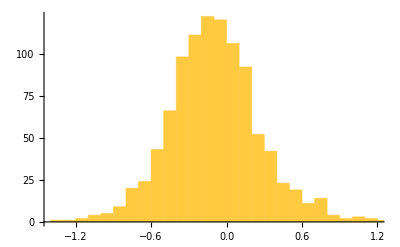

```mathematica
Histogram[int[[All, 3]]]
```

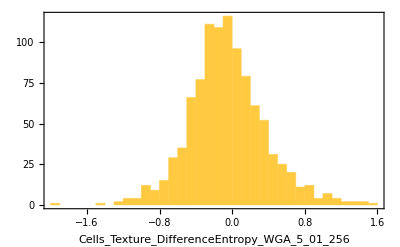
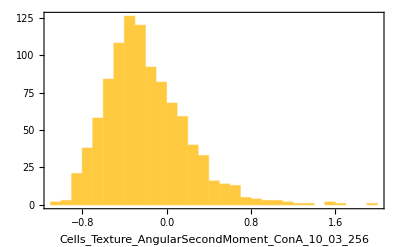
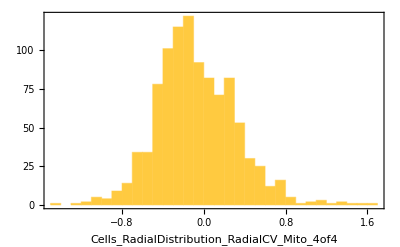
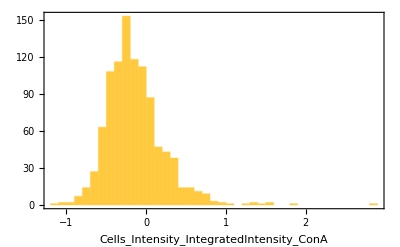
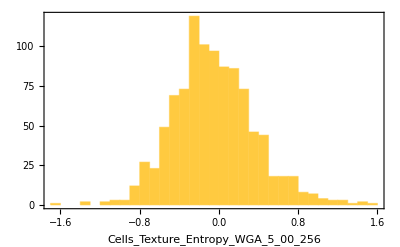
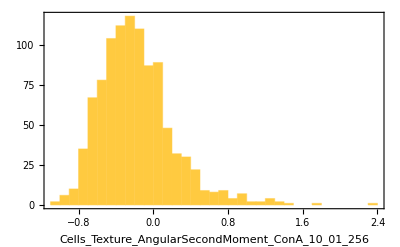
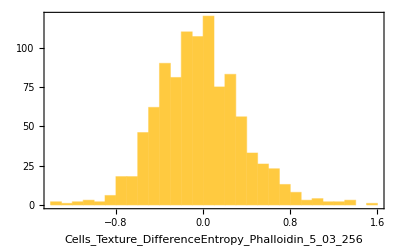
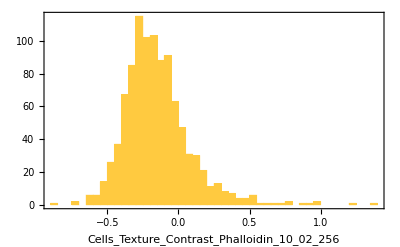
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Histogram[int[[All, #]], Frame->True, FrameLabel->{h2[[#]], Automatic}, PlotRange->All]&/@ RandomSample[Range[1000], 10]
```

#### CLI

```mathematica
RunProcess[{"cd .."}]
```

RunProcess::pnfd: Program cd .. not found.  Check Environment["PATH"].

$Failed

```mathematica
SetDirectory[""]
```

/Users/erichegonzales

```mathematica
RunProcess[]
```

```mathematica
RunProcess["erichegonzales"]
```

<|ExitCode→0,StandardOutput→Deleted Users
Guest
Shared
erichegonzales
willemnielsen (Deleted)
,StandardError→|>

```mathematica
RunProcess[{"bash","-c","cd .. && ls"}]
```

<|ExitCode→0,StandardOutput→Deleted Users
Guest
Shared
erichegonzales
willemnielsen (Deleted)
,StandardError→|>

```mathematica
SetDirectory["Projects/Wolfram/Biology/GrekaLab"]
```

/Users/erichegonzales/Projects/Wolfram/Biology/GrekaLab

```mathematica
RunProcess[{"ls"}]
```

<|ExitCode→0,StandardOutput→CellMorphology-01.nb
DataSample.csv
DataSample2.csv
GrekaLab-01.nb
chunk1.csv
or1.wxf
out1.wxf
pertmultiway.jpeg
pertmultiway.pdf
tab1.csv
,StandardError→|>

#### Smaller file attempt

```mathematica
tc = Import["A549_single_cell_metadata_CP186A_ALLWELLS.csv", "Tabular"];
```

```mathematica
tc2 = Import["20200805_A549_WG_Screen_gene_ALLBATCHES___CP186A___ALLWELLS.csv", "Tabular"];
```

```mathematica
Length[tc2]
```

20384

```mathematica
ByteCount[tc2]
```

614272579

```mathematica
Keys[Normal[tc2[[1]]]]
```

{Metadata_Foci_Barcode_MatchedTo_GeneCode,Cells_AreaShape_Area,Cells_AreaShape_BoundingBoxArea,Cells_AreaShape_BoundingBoxMaximum_X,Cells_AreaShape_BoundingBoxMaximum_Y,Cells_AreaShape_BoundingBoxMinimum_X,Cells_AreaShape_BoundingBoxMinimum_Y,Cells_AreaShape_Center_X,Cells_AreaShape_Center_Y,Cells_AreaShape_CentralMoment_0_0,Cells_AreaShape_CentralMoment_0_1,Cells_AreaShape_CentralMoment_0_2,Cells_AreaShape_CentralMoment_0_3,Cells_AreaShape_CentralMoment_1_0,Cells_AreaShape_CentralMoment_1_1,Cells_AreaShape_CentralMoment_1_2,Cells_AreaShape_CentralMoment_1_3,Cells_AreaShape_CentralMoment_2_0,Cells_AreaShape_CentralMoment_2_1,Cells_AreaShape_CentralMoment_2_2,Cells_AreaShape_CentralMoment_2_3,Cells_AreaShape_Compactness,Cells_AreaShape_Eccentricity,Cells_AreaShape_EquivalentDiameter,Cells_AreaShape_EulerNumber,Cells_AreaShape_Extent,Cells_AreaShape_FormFactor,Cells_AreaShape_HuMoment_0,Cells_AreaShape_HuMoment_1,Cells_AreaShape_HuMoment_2,Cells_AreaShape_HuMoment_3,Cells_AreaShape_HuMoment_4,Cells_AreaShape_HuMoment_5,Cells_AreaShape_HuMoment_6,Cells_AreaShape_InertiaTensorEigenvalues_0,Cells_AreaShape_InertiaTensorEigenvalues_1,Cells_AreaShape_InertiaTensor_0_0,Cells_AreaShape_InertiaTensor_0_1,Cells_AreaShape_InertiaTensor_1_0,Cells_AreaShape_InertiaTensor_1_1,Cells_AreaShape_MajorAxisLength,Cells_AreaShape_MaxFeretDiameter,Cells_AreaShape_MaximumRadius,Cells_AreaShape_MeanRadius,Cells_AreaShape_MedianRadius,Cells_AreaShape_MinFeretDiameter,Cells_AreaShape_MinorAxisLength,Cells_AreaShape_NormalizedMoment_0_0,Cells_AreaShape_NormalizedMoment_0_1,Cells_AreaShape_NormalizedMoment_0_2,Cells_AreaShape_NormalizedMoment_0_3,Cells_AreaShape_NormalizedMoment_1_0,Cells_AreaShape_NormalizedMoment_1_1,Cells_AreaShape_NormalizedMoment_1_2,Cells_AreaShape_NormalizedMoment_1_3,Cells_AreaShape_NormalizedMoment_2_0,Cells_AreaShape_NormalizedMoment_2_1,Cells_AreaShape_NormalizedMoment_2_2,Cells_AreaShape_NormalizedMoment_2_3,Cells_AreaShape_NormalizedMoment_3_0,Cells_AreaShape_NormalizedMoment_3_1,Cells_AreaShape_NormalizedMoment_3_2,Cells_AreaShape_NormalizedMoment_3_3,Cells_AreaShape_Orientation,Cells_AreaShape_Perimeter,Cells_AreaShape_Solidity,Cells_AreaShape_SpatialMoment_0_0,Cells_AreaShape_SpatialMoment_0_1,Cells_AreaShape_SpatialMoment_0_2,Cells_AreaShape_SpatialMoment_0_3,Cells_AreaShape_SpatialMoment_1_0,Cells_AreaShape_SpatialMoment_1_1,Cells_AreaShape_SpatialMoment_1_2,Cells_AreaShape_SpatialMoment_1_3,Cells_AreaShape_SpatialMoment_2_0,Cells_AreaShape_SpatialMoment_2_1,Cells_AreaShape_SpatialMoment_2_2,Cells_AreaShape_SpatialMoment_2_3,Cells_AreaShape_Zernike_0_0,Cells_AreaShape_Zernike_1_1,Cells_AreaShape_Zernike_2_0,Cells_AreaShape_Zernike_2_2,Cells_AreaShape_Zernike_3_1,Cells_AreaShape_Zernike_3_3,Cells_AreaShape_Zernike_4_0,Cells_AreaShape_Zernike_4_2,Cells_AreaShape_Zernike_4_4,Cells_AreaShape_Zernike_5_1,Cells_AreaShape_Zernike_5_3,Cells_AreaShape_Zernike_5_5,Cells_AreaShape_Zernike_6_0,Cells_AreaShape_Zernike_6_2,Cells_AreaShape_Zernike_6_4,Cells_AreaShape_Zernike_6_6,Cells_AreaShape_Zernike_7_1,Cells_AreaShape_Zernike_7_3,Cells_AreaShape_Zernike_7_5,Cells_AreaShape_Zernike_7_7,Cells_AreaShape_Zernike_8_0,Cells_AreaShape_Zernike_8_2,Cells_AreaShape_Zernike_8_4,Cells_AreaShape_Zernike_8_6,Cells_AreaShape_Zernike_8_8,Cells_AreaShape_Zernike_9_1,Cells_AreaShape_Zernike_9_3,Cells_AreaShape_Zernike_9_5,Cells_AreaShape_Zernike_9_7,Cells_AreaShape_Zernike_9_9,Cells_Correlation_Correlation_ConA_Cycle01_DAPI,Cells_Correlation_Correlation_ConA_DAPI_Painting,Cells_Correlation_Correlation_ConA_Mito,Cells_Correlation_Correlation_ConA_Phalloidin,Cells_Correlation_Correlation_ConA_WGA,Cells_Correlation_Correlation_Cycle01_DAPI_DAPI_Painting,Cells_Correlation_Correlation_Cycle01_DAPI_Mito,Cells_Correlation_Correlation_Cycle01_DAPI_Phalloidin,Cells_Correlation_Correlation_Cycle01_DAPI_WGA,Cells_Correlation_Correlation_DAPI_Painting_Mito,Cells_Correlation_Correlation_DAPI_Painting_Phalloidin,Cells_Correlation_Correlation_DAPI_Painting_WGA,Cells_Correlation_Correlation_Mito_Phalloidin,Cells_Correlation_Correlation_Mito_WGA,Cells_Correlation_Correlation_Phalloidin_WGA,Cells_Correlation_K_ConA_Cycle01_DAPI,Cells_Correlation_K_ConA_DAPI_Painting,Cells_Correlation_K_ConA_Mito,Cells_Correlation_K_ConA_Phalloidin,Cells_Correlation_K_ConA_WGA,Cells_Correlation_K_Cycle01_DAPI_ConA,Cells_Correlation_K_Cycle01_DAPI_DAPI_Painting,Cells_Correlation_K_Cycle01_DAPI_Mito,Cells_Correlation_K_Cycle01_DAPI_Phalloidin,Cells_Correlation_K_Cycle01_DAPI_WGA,Cells_Correlation_K_DAPI_Painting_ConA,Cells_Correlation_K_DAPI_Painting_Cycle01_DAPI,Cells_Correlation_K_DAPI_Painting_Mito,Cells_Correlation_K_DAPI_Painting_Phalloidin,Cells_Correlation_K_DAPI_Painting_WGA,Cells_Correlation_K_Mito_ConA,Cells_Correlation_K_Mito_Cycle01_DAPI,Cells_Correlation_K_Mito_DAPI_Painting,Cells_Correlation_K_Mito_Phalloidin,Cells_Correlation_K_Mito_WGA,Cells_Correlation_K_Phalloidin_ConA,Cells_Correlation_K_Phalloidin_Cycle01_DAPI,Cells_Correlation_K_Phalloidin_DAPI_Painting,Cells_Correlation_K_Phalloidin_Mito,Cells_Correlation_K_Phalloidin_WGA,Cells_Correlation_K_WGA_ConA,Cells_Correlation_K_WGA_Cycle01_DAPI,Cells_Correlation_K_WGA_DAPI_Painting,Cells_Correlation_K_WGA_Mito,Cells_Correlation_K_WGA_Phalloidin,Cells_Correlation_Overlap_ConA_Cycle01_DAPI,Cells_Correlation_Overlap_ConA_DAPI_Painting,Cells_Correlation_Overlap_ConA_Mito,Cells_Correlation_Overlap_ConA_Phalloidin,Cells_Correlation_Overlap_ConA_WGA,Cells_Correlation_Overlap_Cycle01_DAPI_DAPI_Painting,Cells_Correlation_Overlap_Cycle01_DAPI_Mito,Cells_Correlation_Overlap_Cycle01_DAPI_Phalloidin,Cells_Correlation_Overlap_Cycle01_DAPI_WGA,Cells_Correlation_Overlap_DAPI_Painting_Mito,Cells_Correlation_Overlap_DAPI_Painting_Phalloidin,Cells_Correlation_Overlap_DAPI_Painting_WGA,Cells_Correlation_Overlap_Mito_Phalloidin,Cells_Correlation_Overlap_Mito_WGA,Cells_Correlation_Overlap_Phalloidin_WGA,Cells_Granularity_10_ConA,Cells_Granularity_10_DAPI_Painting,Cells_Granularity_10_Mito,Cells_Granularity_10_Phalloidin,Cells_Granularity_10_WGA,Cells_Granularity_11_ConA,Cells_Granularity_11_DAPI_Painting,Cells_Granularity_11_Mito,Cells_Granularity_11_Phalloidin,Cells_Granularity_11_WGA,Cells_Granularity_12_ConA,Cells_Granularity_12_DAPI_Painting,Cells_Granularity_12_Mito,Cells_Granularity_12_Phalloidin,Cells_Granularity_12_WGA,Cells_Granularity_13_ConA,Cells_Granularity_13_DAPI_Painting,Cells_Granularity_13_Mito,Cells_Granularity_13_Phalloidin,Cells_Granularity_13_WGA,Cells_Granularity_14_ConA,Cells_Granularity_14_DAPI_Painting,Cells_Granularity_14_Mito,Cells_Granularity_14_Phalloidin,Cells_Granularity_14_WGA,Cells_Granularity_15_ConA,Cells_Granularity_15_DAPI_Painting,Cells_Granularity_15_Mito,Cells_Granularity_15_Phalloidin,Cells_Granularity_15_WGA,Cells_Granularity_16_ConA,Cells_Granularity_16_DAPI_Painting,Cells_Granularity_16_Mito,Cells_Granularity_16_Phalloidin,Cells_Granularity_16_WGA,Cells_Granularity_1_ConA,Cells_Granularity_1_DAPI_Painting,Cells_Granularity_1_Mito,Cells_Granularity_1_Phalloidin,Cells_Granularity_1_WGA,Cells_Granularity_2_ConA,Cells_Granularity_2_DAPI_Painting,Cells_Granularity_2_Mito,Cells_Granularity_2_Phalloidin,Cells_Granularity_2_WGA,Cells_Granularity_3_ConA,Cells_Granularity_3_DAPI_Painting,Cells_Granularity_3_Mito,Cells_Granularity_3_Phalloidin,Cells_Granularity_3_WGA,Cells_Granularity_4_ConA,Cells_Granularity_4_DAPI_Painting,Cells_Granularity_4_Mito,Cells_Granularity_4_Phalloidin,Cells_Granularity_4_WGA,Cells_Granularity_5_ConA,Cells_Granularity_5_DAPI_Painting,Cells_Granularity_5_Mito,Cells_Granularity_5_Phalloidin,Cells_Granularity_5_WGA,Cells_Granularity_6_ConA,Cells_Granularity_6_DAPI_Painting,Cells_Granularity_6_Mito,Cells_Granularity_6_Phalloidin,Cells_Granularity_6_WGA,Cells_Granularity_7_ConA,Cells_Granularity_7_DAPI_Painting,Cells_Granularity_7_Mito,Cells_Granularity_7_Phalloidin,Cells_Granularity_7_WGA,Cells_Granularity_8_ConA,Cells_Granularity_8_DAPI_Painting,Cells_Granularity_8_Mito,Cells_Granularity_8_Phalloidin,Cells_Granularity_8_WGA,Cells_Granularity_9_ConA,Cells_Granularity_9_DAPI_Painting,Cells_Granularity_9_Mito,Cells_Granularity_9_Phalloidin,Cells_Granularity_9_WGA,Cells_Intensity_IntegratedIntensityEdge_ConA,Cells_Intensity_IntegratedIntensityEdge_DAPI_Painting,Cells_Intensity_IntegratedIntensityEdge_MaskedScores_IntValues,Cells_Intensity_IntegratedIntensityEdge_Mito,Cells_Intensity_IntegratedIntensityEdge_Phalloidin,Cells_Intensity_IntegratedIntensityEdge_WGA,Cells_Intensity_IntegratedIntensityEdge_WellEdgeDistance,Cells_Intensity_IntegratedIntensity_ConA,Cells_Intensity_IntegratedIntensity_DAPI_Painting,Cells_Intensity_IntegratedIntensity_MaskedScores_IntValues,Cells_Intensity_IntegratedIntensity_Mito,Cells_Intensity_IntegratedIntensity_Phalloidin,Cells_Intensity_IntegratedIntensity_WGA,Cells_Intensity_IntegratedIntensity_WellEdgeDistance,Cells_Intensity_LowerQuartileIntensity_ConA,Cells_Intensity_LowerQuartileIntensity_DAPI_Painting,Cells_Intensity_LowerQuartileIntensity_MaskedScores_IntValues,Cells_Intensity_LowerQuartileIntensity_Mito,Cells_Intensity_LowerQuartileIntensity_Phalloidin,Cells_Intensity_LowerQuartileIntensity_WGA,Cells_Intensity_LowerQuartileIntensity_WellEdgeDistance,Cells_Intensity_MADIntensity_ConA,Cells_Intensity_MADIntensity_DAPI_Painting,Cells_Intensity_MADIntensity_MaskedScores_IntValues,Cells_Intensity_MADIntensity_Mito,Cells_Intensity_MADIntensity_Phalloidin,Cells_Intensity_MADIntensity_WGA,Cells_Intensity_MADIntensity_WellEdgeDistance,Cells_Intensity_MassDisplacement_ConA,Cells_Intensity_MassDisplacement_DAPI_Painting,Cells_Intensity_MassDisplacement_MaskedScores_IntValues,Cells_Intensity_MassDisplacement_Mito,Cells_Intensity_MassDisplacement_Phalloidin,Cells_Intensity_MassDisplacement_WGA,Cells_Intensity_MassDisplacement_WellEdgeDistance,Cells_Intensity_MaxIntensityEdge_ConA,Cells_Intensity_MaxIntensityEdge_DAPI_Painting,Cells_Intensity_MaxIntensityEdge_MaskedScores_IntValues,Cells_Intensity_MaxIntensityEdge_Mito,Cells_Intensity_MaxIntensityEdge_Phalloidin,Cells_Intensity_MaxIntensityEdge_WGA,Cells_Intensity_MaxIntensityEdge_WellEdgeDistance,Cells_Intensity_MaxIntensity_ConA,Cells_Intensity_MaxIntensity_DAPI_Painting,Cells_Intensity_MaxIntensity_MaskedScores_IntValues,Cells_Intensity_MaxIntensity_Mito,Cells_Intensity_MaxIntensity_Phalloidin,Cells_Intensity_MaxIntensity_WGA,Cells_Intensity_MaxIntensity_WellEdgeDistance,Cells_Intensity_MeanIntensityEdge_ConA,Cells_Intensity_MeanIntensityEdge_DAPI_Painting,Cells_Intensity_MeanIntensityEdge_MaskedScores_IntValues,Cells_Intensity_MeanIntensityEdge_Mito,Cells_Intensity_MeanIntensityEdge_Phalloidin,Cells_Intensity_MeanIntensityEdge_WGA,Cells_Intensity_MeanIntensityEdge_WellEdgeDistance,Cells_Intensity_MeanIntensity_ConA,Cells_Intensity_MeanIntensity_DAPI_Painting,Cells_Intensity_MeanIntensity_MaskedScores_IntValues,Cells_Intensity_MeanIntensity_Mito,Cells_Intensity_MeanIntensity_Phalloidin,Cells_Intensity_MeanIntensity_WGA,Cells_Intensity_MeanIntensity_WellEdgeDistance,Cells_Intensity_MedianIntensity_ConA,Cells_Intensity_MedianIntensity_DAPI_Painting,Cells_Intensity_MedianIntensity_MaskedScores_IntValues,Cells_Intensity_MedianIntensity_Mito,Cells_Intensity_MedianIntensity_Phalloidin,Cells_Intensity_MedianIntensity_WGA,Cells_Intensity_MedianIntensity_WellEdgeDistance,Cells_Intensity_MinIntensityEdge_ConA,Cells_Intensity_MinIntensityEdge_DAPI_Painting,Cells_Intensity_MinIntensityEdge_MaskedScores_IntValues,Cells_Intensity_MinIntensityEdge_Mito,Cells_Intensity_MinIntensityEdge_Phalloidin,Cells_Intensity_MinIntensityEdge_WGA,Cells_Intensity_MinIntensityEdge_WellEdgeDistance,Cells_Intensity_MinIntensity_ConA,Cells_Intensity_MinIntensity_DAPI_Painting,Cells_Intensity_MinIntensity_MaskedScores_IntValues,Cells_Intensity_MinIntensity_Mito,Cells_Intensity_MinIntensity_Phalloidin,Cells_Intensity_MinIntensity_WGA,Cells_Intensity_MinIntensity_WellEdgeDistance,Cells_Intensity_StdIntensityEdge_ConA,Cells_Intensity_StdIntensityEdge_DAPI_Painting,Cells_Intensity_StdIntensityEdge_MaskedScores_IntValues,Cells_Intensity_StdIntensityEdge_Mito,Cells_Intensity_StdIntensityEdge_Phalloidin,Cells_Intensity_StdIntensityEdge_WGA,Cells_Intensity_StdIntensityEdge_WellEdgeDistance,Cells_Intensity_StdIntensity_ConA,Cells_Intensity_StdIntensity_DAPI_Painting,Cells_Intensity_StdIntensity_MaskedScores_IntValues,Cells_Intensity_StdIntensity_Mito,Cells_Intensity_StdIntensity_Phalloidin,Cells_Intensity_StdIntensity_WGA,Cells_Intensity_StdIntensity_WellEdgeDistance,Cells_Intensity_UpperQuartileIntensity_ConA,Cells_Intensity_UpperQuartileIntensity_DAPI_Painting,Cells_Intensity_UpperQuartileIntensity_MaskedScores_IntValues,Cells_Intensity_UpperQuartileIntensity_Mito,Cells_Intensity_UpperQuartileIntensity_Phalloidin,Cells_Intensity_UpperQuartileIntensity_WGA,Cells_Intensity_UpperQuartileIntensity_WellEdgeDistance,Cells_Neighbors_AngleBetweenNeighbors_10,Cells_Neighbors_AngleBetweenNeighbors_Adjacent,Cells_Neighbors_FirstClosestDistance_10,Cells_Neighbors_FirstClosestDistance_Adjacent,Cells_Neighbors_FirstClosestObjectNumber_10,Cells_Neighbors_FirstClosestObjectNumber_Adjacent,Cells_Neighbors_NumberOfNeighbors_10,Cells_Neighbors_NumberOfNeighbors_Adjacent,Cells_Neighbors_PercentTouching_10,Cells_Neighbors_PercentTouching_Adjacent,Cells_Neighbors_SecondClosestDistance_10,Cells_Neighbors_SecondClosestDistance_Adjacent,Cells_Neighbors_SecondClosestObjectNumber_10,Cells_Neighbors_SecondClosestObjectNumber_Adjacent,Cells_Number_Object_Number,Cells_RadialDistribution_FracAtD_ConA_1of4,Cells_RadialDistribution_FracAtD_ConA_2of4,Cells_RadialDistribution_FracAtD_ConA_3of4,Cells_RadialDistribution_FracAtD_ConA_4of4,Cells_RadialDistribution_FracAtD_DAPI_Painting_1of4,Cells_RadialDistribution_FracAtD_DAPI_Painting_2of4,Cells_RadialDistribution_FracAtD_DAPI_Painting_3of4,Cells_RadialDistribution_FracAtD_DAPI_Painting_4of4,Cells_RadialDistribution_FracAtD_Mito_1of4,Cells_RadialDistribution_FracAtD_Mito_2of4,Cells_RadialDistribution_FracAtD_Mito_3of4,Cells_RadialDistribution_FracAtD_Mito_4of4,Cells_RadialDistribution_FracAtD_Phalloidin_1of4,Cells_RadialDistribution_FracAtD_Phalloidin_2of4,Cells_RadialDistribution_FracAtD_Phalloidin_3of4,Cells_RadialDistribution_FracAtD_Phalloidin_4of4,Cells_RadialDistribution_FracAtD_WGA_1of4,Cells_RadialDistribution_FracAtD_WGA_2of4,Cells_RadialDistribution_FracAtD_WGA_3of4,Cells_RadialDistribution_FracAtD_WGA_4of4,Cells_RadialDistribution_FracAtD_mito_tubeness_10of16,Cells_RadialDistribution_FracAtD_mito_tubeness_10of20,Cells_RadialDistribution_FracAtD_mito_tubeness_11of16,Cells_RadialDistribution_FracAtD_mito_tubeness_11of20,Cells_RadialDistribution_FracAtD_mito_tubeness_12of16,Cells_RadialDistribution_FracAtD_mito_tubeness_12of20,Cells_RadialDistribution_FracAtD_mito_tubeness_13of16,Cells_RadialDistribution_FracAtD_mito_tubeness_13of20,Cells_RadialDistribution_FracAtD_mito_tubeness_14of16,Cells_RadialDistribution_FracAtD_mito_tubeness_14of20,Cells_RadialDistribution_FracAtD_mito_tubeness_15of16,Cells_RadialDistribution_FracAtD_mito_tubeness_15of20,Cells_RadialDistribution_FracAtD_mito_tubeness_16of16,Cells_RadialDistribution_FracAtD_mito_tubeness_16of20,Cells_RadialDistribution_FracAtD_mito_tubeness_17of20,Cells_RadialDistribution_FracAtD_mito_tubeness_18of20,Cells_RadialDistribution_FracAtD_mito_tubeness_19of20,Cells_RadialDistribution_FracAtD_mito_tubeness_1of16,Cells_RadialDistribution_FracAtD_mito_tubeness_1of20,Cells_RadialDistribution_FracAtD_mito_tubeness_20of20,Cells_RadialDistribution_FracAtD_mito_tubeness_2of16,Cells_RadialDistribution_FracAtD_mito_tubeness_2of20,Cells_RadialDistribution_FracAtD_mito_tubeness_3of16,Cells_RadialDistribution_FracAtD_mito_tubeness_3of20,Cells_RadialDistribution_FracAtD_mito_tubeness_4of16,Cells_RadialDistribution_FracAtD_mito_tubeness_4of20,Cells_RadialDistribution_FracAtD_mito_tubeness_5of16,Cells_RadialDistribution_FracAtD_mito_tubeness_5of20,Cells_RadialDistribution_FracAtD_mito_tubeness_6of16,Cells_RadialDistribution_FracAtD_mito_tubeness_6of20,Cells_RadialDistribution_FracAtD_mito_tubeness_7of16,Cells_RadialDistribution_FracAtD_mito_tubeness_7of20,Cells_RadialDistribution_FracAtD_mito_tubeness_8of16,Cells_RadialDistribution_FracAtD_mito_tubeness_8of20,Cells_RadialDistribution_FracAtD_mito_tubeness_9of16,Cells_RadialDistribution_FracAtD_mito_tubeness_9of20,Cells_RadialDistribution_FracAtD_mito_tubeness_Overflow,Cells_RadialDistribution_MeanFrac_ConA_1of4,Cells_RadialDistribution_MeanFrac_ConA_2of4,Cells_RadialDistribution_MeanFrac_ConA_3of4,Cells_RadialDistribution_MeanFrac_ConA_4of4,Cells_RadialDistribution_MeanFrac_DAPI_Painting_1of4,Cells_RadialDistribution_MeanFrac_DAPI_Painting_2of4,Cells_RadialDistribution_MeanFrac_DAPI_Painting_3of4,Cells_RadialDistribution_MeanFrac_DAPI_Painting_4of4,Cells_RadialDistribution_MeanFrac_Mito_1of4,Cells_RadialDistribution_MeanFrac_Mito_2of4,Cells_RadialDistribution_MeanFrac_Mito_3of4,Cells_RadialDistribution_MeanFrac_Mito_4of4,Cells_RadialDistribution_MeanFrac_Phalloidin_1of4,Cells_RadialDistribution_MeanFrac_Phalloidin_2of4,Cells_RadialDistribution_MeanFrac_Phalloidin_3of4,Cells_RadialDistribution_MeanFrac_Phalloidin_4of4,Cells_RadialDistribution_MeanFrac_WGA_1of4,Cells_RadialDistribution_MeanFrac_WGA_2of4,Cells_RadialDistribution_MeanFrac_WGA_3of4,Cells_RadialDistribution_MeanFrac_WGA_4of4,Cells_RadialDistribution_MeanFrac_mito_tubeness_10of16,Cells_RadialDistribution_MeanFrac_mito_tubeness_10of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_11of16,Cells_RadialDistribution_MeanFrac_mito_tubeness_11of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_12of16,Cells_RadialDistribution_MeanFrac_mito_tubeness_12of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_13of16,Cells_RadialDistribution_MeanFrac_mito_tubeness_13of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_14of16,Cells_RadialDistribution_MeanFrac_mito_tubeness_14of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_15of16,Cells_RadialDistribution_MeanFrac_mito_tubeness_15of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_16of16,Cells_RadialDistribution_MeanFrac_mito_tubeness_16of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_17of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_18of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_19of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_1of16,Cells_RadialDistribution_MeanFrac_mito_tubeness_1of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_20of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_2of16,Cells_RadialDistribution_MeanFrac_mito_tubeness_2of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_3of16,Cells_RadialDistribution_MeanFrac_mito_tubeness_3of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_4of16,Cells_RadialDistribution_MeanFrac_mito_tubeness_4of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_5of16,Cells_RadialDistribution_MeanFrac_mito_tubeness_5of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_6of16,Cells_RadialDistribution_MeanFrac_mito_tubeness_6of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_7of16,Cells_RadialDistribution_MeanFrac_mito_tubeness_7of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_8of16,Cells_RadialDistribution_MeanFrac_mito_tubeness_8of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_9of16,Cells_RadialDistribution_MeanFrac_mito_tubeness_9of20,Cells_RadialDistribution_MeanFrac_mito_tubeness_Overflow,Cells_RadialDistribution_RadialCV_ConA_1of4,Cells_RadialDistribution_RadialCV_ConA_2of4,Cells_RadialDistribution_RadialCV_ConA_3of4,Cells_RadialDistribution_RadialCV_ConA_4of4,Cells_RadialDistribution_RadialCV_DAPI_Painting_1of4,Cells_RadialDistribution_RadialCV_DAPI_Painting_2of4,Cells_RadialDistribution_RadialCV_DAPI_Painting_3of4,Cells_RadialDistribution_RadialCV_DAPI_Painting_4of4,Cells_RadialDistribution_RadialCV_Mito_1of4,Cells_RadialDistribution_RadialCV_Mito_2of4,Cells_RadialDistribution_RadialCV_Mito_3of4,Cells_RadialDistribution_RadialCV_Mito_4of4,Cells_RadialDistribution_RadialCV_Phalloidin_1of4,Cells_RadialDistribution_RadialCV_Phalloidin_2of4,Cells_RadialDistribution_RadialCV_Phalloidin_3of4,Cells_RadialDistribution_RadialCV_Phalloidin_4of4,Cells_RadialDistribution_RadialCV_WGA_1of4,Cells_RadialDistribution_RadialCV_WGA_2of4,Cells_RadialDistribution_RadialCV_WGA_3of4,Cells_RadialDistribution_RadialCV_WGA_4of4,Cells_RadialDistribution_RadialCV_mito_tubeness_10of16,Cells_RadialDistribution_RadialCV_mito_tubeness_10of20,Cells_RadialDistribution_RadialCV_mito_tubeness_11of16,Cells_RadialDistribution_RadialCV_mito_tubeness_11of20,Cells_RadialDistribution_RadialCV_mito_tubeness_12of16,Cells_RadialDistribution_RadialCV_mito_tubeness_12of20,Cells_RadialDistribution_RadialCV_mito_tubeness_13of16,Cells_RadialDistribution_RadialCV_mito_tubeness_13of20,Cells_RadialDistribution_RadialCV_mito_tubeness_14of16,Cells_RadialDistribution_RadialCV_mito_tubeness_14of20,Cells_RadialDistribution_RadialCV_mito_tubeness_15of16,Cells_RadialDistribution_RadialCV_mito_tubeness_15of20,Cells_RadialDistribution_RadialCV_mito_tubeness_16of16,Cells_RadialDistribution_RadialCV_mito_tubeness_16of20,Cells_RadialDistribution_RadialCV_mito_tubeness_17of20,Cells_RadialDistribution_RadialCV_mito_tubeness_18of20,Cells_RadialDistribution_RadialCV_mito_tubeness_19of20,Cells_RadialDistribution_RadialCV_mito_tubeness_1of16,Cells_RadialDistribution_RadialCV_mito_tubeness_1of20,Cells_RadialDistribution_RadialCV_mito_tubeness_20of20,Cells_RadialDistribution_RadialCV_mito_tubeness_2of16,Cells_RadialDistribution_RadialCV_mito_tubeness_2of20,Cells_RadialDistribution_RadialCV_mito_tubeness_3of16,Cells_RadialDistribution_RadialCV_mito_tubeness_3of20,Cells_RadialDistribution_RadialCV_mito_tubeness_4of16,Cells_RadialDistribution_RadialCV_mito_tubeness_4of20,Cells_RadialDistribution_RadialCV_mito_tubeness_5of16,Cells_RadialDistribution_RadialCV_mito_tubeness_5of20,Cells_RadialDistribution_RadialCV_mito_tubeness_6of16,Cells_RadialDistribution_RadialCV_mito_tubeness_6of20,Cells_RadialDistribution_RadialCV_mito_tubeness_7of16,Cells_RadialDistribution_RadialCV_mito_tubeness_7of20,Cells_RadialDistribution_RadialCV_mito_tubeness_8of16,Cells_RadialDistribution_RadialCV_mito_tubeness_8of20,Cells_RadialDistribution_RadialCV_mito_tubeness_9of16,Cells_RadialDistribution_RadialCV_mito_tubeness_9of20,Cells_RadialDistribution_RadialCV_mito_tubeness_Overflow,Cells_Texture_AngularSecondMoment_ConA_10_00_256,Cells_Texture_AngularSecondMoment_ConA_10_01_256,Cells_Texture_AngularSecondMoment_ConA_10_02_256,Cells_Texture_AngularSecondMoment_ConA_10_03_256,Cells_Texture_AngularSecondMoment_ConA_20_00_256,Cells_Texture_AngularSecondMoment_ConA_20_01_256,Cells_Texture_AngularSecondMoment_ConA_20_02_256,Cells_Texture_AngularSecondMoment_ConA_20_03_256,Cells_Texture_AngularSecondMoment_ConA_5_00_256,Cells_Texture_AngularSecondMoment_ConA_5_01_256,Cells_Texture_AngularSecondMoment_ConA_5_02_256,Cells_Texture_AngularSecondMoment_ConA_5_03_256,Cells_Texture_AngularSecondMoment_DAPI_Painting_10_00_256,Cells_Texture_AngularSecondMoment_DAPI_Painting_10_01_256,Cells_Texture_AngularSecondMoment_DAPI_Painting_10_02_256,Cells_Texture_AngularSecondMoment_DAPI_Painting_10_03_256,Cells_Texture_AngularSecondMoment_DAPI_Painting_20_00_256,Cells_Texture_AngularSecondMoment_DAPI_Painting_20_01_256,Cells_Texture_AngularSecondMoment_DAPI_Painting_20_02_256,Cells_Texture_AngularSecondMoment_DAPI_Painting_20_03_256,Cells_Texture_AngularSecondMoment_DAPI_Painting_5_00_256,Cells_Texture_AngularSecondMoment_DAPI_Painting_5_01_256,Cells_Texture_AngularSecondMoment_DAPI_Painting_5_02_256,Cells_Texture_AngularSecondMoment_DAPI_Painting_5_03_256,Cells_Texture_AngularSecondMoment_Mito_10_00_256,Cells_Texture_AngularSecondMoment_Mito_10_01_256,Cells_Texture_AngularSecondMoment_Mito_10_02_256,Cells_Texture_AngularSecondMoment_Mito_10_03_256,Cells_Texture_AngularSecondMoment_Mito_20_00_256,Cells_Texture_AngularSecondMoment_Mito_20_01_256,Cells_Texture_AngularSecondMoment_Mito_20_02_256,Cells_Texture_AngularSecondMoment_Mito_20_03_256,Cells_Texture_AngularSecondMoment_Mito_5_00_256,Cells_Texture_AngularSecondMoment_Mito_5_01_256,Cells_Texture_AngularSecondMoment_Mito_5_02_256,Cells_Texture_AngularSecondMoment_Mito_5_03_256,Cells_Texture_AngularSecondMoment_Phalloidin_10_00_256,Cells_Texture_AngularSecondMoment_Phalloidin_10_01_256,Cells_Texture_AngularSecondMoment_Phalloidin_10_02_256,Cells_Texture_AngularSecondMoment_Phalloidin_10_03_256,Cells_Texture_AngularSecondMoment_Phalloidin_20_00_256,Cells_Texture_AngularSecondMoment_Phalloidin_20_01_256,Cells_Texture_AngularSecondMoment_Phalloidin_20_02_256,Cells_Texture_AngularSecondMoment_Phalloidin_20_03_256,Cells_Texture_AngularSecondMoment_Phalloidin_5_00_256,Cells_Texture_AngularSecondMoment_Phalloidin_5_01_256,Cells_Texture_AngularSecondMoment_Phalloidin_5_02_256,Cells_Texture_AngularSecondMoment_Phalloidin_5_03_256,Cells_Texture_AngularSecondMoment_WGA_10_00_256,Cells_Texture_AngularSecondMoment_WGA_10_01_256,Cells_Texture_AngularSecondMoment_WGA_10_02_256,Cells_Texture_AngularSecondMoment_WGA_10_03_256,Cells_Texture_AngularSecondMoment_WGA_20_00_256,Cells_Texture_AngularSecondMoment_WGA_20_01_256,Cells_Texture_AngularSecondMoment_WGA_20_02_256,Cells_Texture_AngularSecondMoment_WGA_20_03_256,Cells_Texture_AngularSecondMoment_WGA_5_00_256,Cells_Texture_AngularSecondMoment_WGA_5_01_256,Cells_Texture_AngularSecondMoment_WGA_5_02_256,Cells_Texture_AngularSecondMoment_WGA_5_03_256,Cells_Texture_Contrast_ConA_10_00_256,Cells_Texture_Contrast_ConA_10_01_256,Cells_Texture_Contrast_ConA_10_02_256,Cells_Texture_Contrast_ConA_10_03_256,Cells_Texture_Contrast_ConA_20_00_256,Cells_Texture_Contrast_ConA_20_01_256,Cells_Texture_Contrast_ConA_20_02_256,Cells_Texture_Contrast_ConA_20_03_256,Cells_Texture_Contrast_ConA_5_00_256,Cells_Texture_Contrast_ConA_5_01_256,Cells_Texture_Contrast_ConA_5_02_256,Cells_Texture_Contrast_ConA_5_03_256,Cells_Texture_Contrast_DAPI_Painting_10_00_256,Cells_Texture_Contrast_DAPI_Painting_10_01_256,Cells_Texture_Contrast_DAPI_Painting_10_02_256,Cells_Texture_Contrast_DAPI_Painting_10_03_256,Cells_Texture_Contrast_DAPI_Painting_20_00_256,Cells_Texture_Contrast_DAPI_Painting_20_01_256,Cells_Texture_Contrast_DAPI_Painting_20_02_256,Cells_Texture_Contrast_DAPI_Painting_20_03_256,Cells_Texture_Contrast_DAPI_Painting_5_00_256,Cells_Texture_Contrast_DAPI_Painting_5_01_256,Cells_Texture_Contrast_DAPI_Painting_5_02_256,Cells_Texture_Contrast_DAPI_Painting_5_03_256,Cells_Texture_Contrast_Mito_10_00_256,Cells_Texture_Contrast_Mito_10_01_256,Cells_Texture_Contrast_Mito_10_02_256,Cells_Texture_Contrast_Mito_10_03_256,Cells_Texture_Contrast_Mito_20_00_256,Cells_Texture_Contrast_Mito_20_01_256,Cells_Texture_Contrast_Mito_20_02_256,Cells_Texture_Contrast_Mito_20_03_256,Cells_Texture_Contrast_Mito_5_00_256,Cells_Texture_Contrast_Mito_5_01_256,Cells_Texture_Contrast_Mito_5_02_256,Cells_Texture_Contrast_Mito_5_03_256,Cells_Texture_Contrast_Phalloidin_10_00_256,Cells_Texture_Contrast_Phalloidin_10_01_256,Cells_Texture_Contrast_Phalloidin_10_02_256,Cells_Texture_Contrast_Phalloidin_10_03_256,Cells_Texture_Contrast_Phalloidin_20_00_256,Cells_Texture_Contrast_Phalloidin_20_01_256,Cells_Texture_Contrast_Phalloidin_20_02_256,Cells_Texture_Contrast_Phalloidin_20_03_256,Cells_Texture_Contrast_Phalloidin_5_00_256,Cells_Texture_Contrast_Phalloidin_5_01_256,Cells_Texture_Contrast_Phalloidin_5_02_256,Cells_Texture_Contrast_Phalloidin_5_03_256,Cells_Texture_Contrast_WGA_10_00_256,Cells_Texture_Contrast_WGA_10_01_256,Cells_Texture_Contrast_WGA_10_02_256,Cells_Texture_Contrast_WGA_10_03_256,Cells_Texture_Contrast_WGA_20_00_256,Cells_Texture_Contrast_WGA_20_01_256,Cells_Texture_Contrast_WGA_20_02_256,Cells_Texture_Contrast_WGA_20_03_256,Cells_Texture_Contrast_WGA_5_00_256,Cells_Texture_Contrast_WGA_5_01_256,Cells_Texture_Contrast_WGA_5_02_256,Cells_Texture_Contrast_WGA_5_03_256,Cells_Texture_Correlation_ConA_10_00_256,Cells_Texture_Correlation_ConA_10_01_256,Cells_Texture_Correlation_ConA_10_02_256,Cells_Texture_Correlation_ConA_10_03_256,Cells_Texture_Correlation_ConA_20_00_256,Cells_Texture_Correlation_ConA_20_01_256,Cells_Texture_Correlation_ConA_20_02_256,Cells_Texture_Correlation_ConA_20_03_256,Cells_Texture_Correlation_ConA_5_00_256,Cells_Texture_Correlation_ConA_5_01_256,Cells_Texture_Correlation_ConA_5_02_256,Cells_Texture_Correlation_ConA_5_03_256,Cells_Texture_Correlation_DAPI_Painting_10_00_256,Cells_Texture_Correlation_DAPI_Painting_10_01_256,Cells_Texture_Correlation_DAPI_Painting_10_02_256,Cells_Texture_Correlation_DAPI_Painting_10_03_256,Cells_Texture_Correlation_DAPI_Painting_20_00_256,Cells_Texture_Correlation_DAPI_Painting_20_01_256,Cells_Texture_Correlation_DAPI_Painting_20_02_256,Cells_Texture_Correlation_DAPI_Painting_20_03_256,Cells_Texture_Correlation_DAPI_Painting_5_00_256,Cells_Texture_Correlation_DAPI_Painting_5_01_256,Cells_Texture_Correlation_DAPI_Painting_5_02_256,Cells_Texture_Correlation_DAPI_Painting_5_03_256,Cells_Texture_Correlation_Mito_10_00_256,Cells_Texture_Correlation_Mito_10_01_256,Cells_Texture_Correlation_Mito_10_02_256,Cells_Texture_Correlation_Mito_10_03_256,Cells_Texture_Correlation_Mito_20_00_256,Cells_Texture_Correlation_Mito_20_01_256,Cells_Texture_Correlation_Mito_20_02_256,Cells_Texture_Correlation_Mito_20_03_256,Cells_Texture_Correlation_Mito_5_00_256,Cells_Texture_Correlation_Mito_5_01_256,Cells_Texture_Correlation_Mito_5_02_256,Cells_Texture_Correlation_Mito_5_03_256,Cells_Texture_Correlation_Phalloidin_10_00_256,Cells_Texture_Correlation_Phalloidin_10_01_256,Cells_Texture_Correlation_Phalloidin_10_02_256,Cells_Texture_Correlation_Phalloidin_10_03_256,Cells_Texture_Correlation_Phalloidin_20_00_256,Cells_Texture_Correlation_Phalloidin_20_01_256,Cells_Texture_Correlation_Phalloidin_20_02_256,Cells_Texture_Correlation_Phalloidin_20_03_256,Cells_Texture_Correlation_Phalloidin_5_00_256,Cells_Texture_Correlation_Phalloidin_5_01_256,Cells_Texture_Correlation_Phalloidin_5_02_256,Cells_Texture_Correlation_Phalloidin_5_03_256,Cells_Texture_Correlation_WGA_10_00_256,Cells_Texture_Correlation_WGA_10_01_256,Cells_Texture_Correlation_WGA_10_02_256,Cells_Texture_Correlation_WGA_10_03_256,Cells_Texture_Correlation_WGA_20_00_256,Cells_Texture_Correlation_WGA_20_01_256,Cells_Texture_Correlation_WGA_20_02_256,Cells_Texture_Correlation_WGA_20_03_256,Cells_Texture_Correlation_WGA_5_00_256,Cells_Texture_Correlation_WGA_5_01_256,Cells_Texture_Correlation_WGA_5_02_256,Cells_Texture_Correlation_WGA_5_03_256,Cells_Texture_DifferenceEntropy_ConA_10_00_256,Cells_Texture_DifferenceEntropy_ConA_10_01_256,Cells_Texture_DifferenceEntropy_ConA_10_02_256,Cells_Texture_DifferenceEntropy_ConA_10_03_256,Cells_Texture_DifferenceEntropy_ConA_20_00_256,Cells_Texture_DifferenceEntropy_ConA_20_01_256,Cells_Texture_DifferenceEntropy_ConA_20_02_256,Cells_Texture_DifferenceEntropy_ConA_20_03_256,Cells_Texture_DifferenceEntropy_ConA_5_00_256,Cells_Texture_DifferenceEntropy_ConA_5_01_256,Cells_Texture_DifferenceEntropy_ConA_5_02_256,Cells_Texture_DifferenceEntropy_ConA_5_03_256,Cells_Texture_DifferenceEntropy_DAPI_Painting_10_00_256,Cells_Texture_DifferenceEntropy_DAPI_Painting_10_01_256,Cells_Texture_DifferenceEntropy_DAPI_Painting_10_02_256,Cells_Texture_DifferenceEntropy_DAPI_Painting_10_03_256,Cells_Texture_DifferenceEntropy_DAPI_Painting_20_00_256,Cells_Texture_DifferenceEntropy_DAPI_Painting_20_01_256,Cells_Texture_DifferenceEntropy_DAPI_Painting_20_02_256,Cells_Texture_DifferenceEntropy_DAPI_Painting_20_03_256,Cells_Texture_DifferenceEntropy_DAPI_Painting_5_00_256,Cells_Texture_DifferenceEntropy_DAPI_Painting_5_01_256,Cells_Texture_DifferenceEntropy_DAPI_Painting_5_02_256,Cells_Texture_DifferenceEntropy_DAPI_Painting_5_03_256,Cells_Texture_DifferenceEntropy_Mito_10_00_256,Cells_Texture_DifferenceEntropy_Mito_10_01_256,Cells_Texture_DifferenceEntropy_Mito_10_02_256,Cells_Texture_DifferenceEntropy_Mito_10_03_256,Cells_Texture_DifferenceEntropy_Mito_20_00_256,Cells_Texture_DifferenceEntropy_Mito_20_01_256,Cells_Texture_DifferenceEntropy_Mito_20_02_256,Cells_Texture_DifferenceEntropy_Mito_20_03_256,Cells_Texture_DifferenceEntropy_Mito_5_00_256,Cells_Texture_DifferenceEntropy_Mito_5_01_256,Cells_Texture_DifferenceEntropy_Mito_5_02_256,Cells_Texture_DifferenceEntropy_Mito_5_03_256,Cells_Texture_DifferenceEntropy_Phalloidin_10_00_256,Cells_Texture_DifferenceEntropy_Phalloidin_10_01_256,Cells_Texture_DifferenceEntropy_Phalloidin_10_02_256,Cells_Texture_DifferenceEntropy_Phalloidin_10_03_256,Cells_Texture_DifferenceEntropy_Phalloidin_20_00_256,Cells_Texture_DifferenceEntropy_Phalloidin_20_01_256,Cells_Texture_DifferenceEntropy_Phalloidin_20_02_256,Cells_Texture_DifferenceEntropy_Phalloidin_20_03_256,Cells_Texture_DifferenceEntropy_Phalloidin_5_00_256,Cells_Texture_DifferenceEntropy_Phalloidin_5_01_256,Cells_Texture_DifferenceEntropy_Phalloidin_5_02_256,Cells_Texture_DifferenceEntropy_Phalloidin_5_03_256,Cells_Texture_DifferenceEntropy_WGA_10_00_256,Cells_Texture_DifferenceEntropy_WGA_10_01_256,Cells_Texture_DifferenceEntropy_WGA_10_02_256,Cells_Texture_DifferenceEntropy_WGA_10_03_256,Cells_Texture_DifferenceEntropy_WGA_20_00_256,Cells_Texture_DifferenceEntropy_WGA_20_01_256,Cells_Texture_DifferenceEntropy_WGA_20_02_256,Cells_Texture_DifferenceEntropy_WGA_20_03_256,Cells_Texture_DifferenceEntropy_WGA_5_00_256,Cells_Texture_DifferenceEntropy_WGA_5_01_256,Cells_Texture_DifferenceEntropy_WGA_5_02_256,Cells_Texture_DifferenceEntropy_WGA_5_03_256,Cells_Texture_DifferenceVariance_ConA_10_00_256,Cells_Texture_DifferenceVariance_ConA_10_01_256,Cells_Texture_DifferenceVariance_ConA_10_02_256,Cells_Texture_DifferenceVariance_ConA_10_03_256,Cells_Texture_DifferenceVariance_ConA_20_00_256,Cells_Texture_DifferenceVariance_ConA_20_01_256,Cells_Texture_DifferenceVariance_ConA_20_02_256,Cells_Texture_DifferenceVariance_ConA_20_03_256,Cells_Texture_DifferenceVariance_ConA_5_00_256,Cells_Texture_DifferenceVariance_ConA_5_01_256,Cells_Texture_DifferenceVariance_ConA_5_02_256,Cells_Texture_DifferenceVariance_ConA_5_03_256,Cells_Texture_DifferenceVariance_DAPI_Painting_10_00_256,Cells_Texture_DifferenceVariance_DAPI_Painting_10_01_256,Cells_Texture_DifferenceVariance_DAPI_Painting_10_02_256,Cells_Texture_DifferenceVariance_DAPI_Painting_10_03_256,Cells_Texture_DifferenceVariance_DAPI_Painting_20_00_256,Cells_Texture_DifferenceVariance_DAPI_Painting_20_01_256,Cells_Texture_DifferenceVariance_DAPI_Painting_20_02_256,Cells_Texture_DifferenceVariance_DAPI_Painting_20_03_256,Cells_Texture_DifferenceVariance_DAPI_Painting_5_00_256,Cells_Texture_DifferenceVariance_DAPI_Painting_5_01_256,Cells_Texture_DifferenceVariance_DAPI_Painting_5_02_256,Cells_Texture_DifferenceVariance_DAPI_Painting_5_03_256,Cells_Texture_DifferenceVariance_Mito_10_00_256,Cells_Texture_DifferenceVariance_Mito_10_01_256,Cells_Texture_DifferenceVariance_Mito_10_02_256,Cells_Texture_DifferenceVariance_Mito_10_03_256,Cells_Texture_DifferenceVariance_Mito_20_00_256,Cells_Texture_DifferenceVariance_Mito_20_01_256,Cells_Texture_DifferenceVariance_Mito_20_02_256,Cells_Texture_DifferenceVariance_Mito_20_03_256,Cells_Texture_DifferenceVariance_Mito_5_00_256,Cells_Texture_DifferenceVariance_Mito_5_01_256,Cells_Texture_DifferenceVariance_Mito_5_02_256,Cells_Texture_DifferenceVariance_Mito_5_03_256,Cells_Texture_DifferenceVariance_Phalloidin_10_00_256,Cells_Texture_DifferenceVariance_Phalloidin_10_01_256,Cells_Texture_DifferenceVariance_Phalloidin_10_02_256,Cells_Texture_DifferenceVariance_Phalloidin_10_03_256,Cells_Texture_DifferenceVariance_Phalloidin_20_00_256,Cells_Texture_DifferenceVariance_Phalloidin_20_01_256,Cells_Texture_DifferenceVariance_Phalloidin_20_02_256,Cells_Texture_DifferenceVariance_Phalloidin_20_03_256,Cells_Texture_DifferenceVariance_Phalloidin_5_00_256,Cells_Texture_DifferenceVariance_Phalloidin_5_01_256,Cells_Texture_DifferenceVariance_Phalloidin_5_02_256,Cells_Texture_DifferenceVariance_Phalloidin_5_03_256,Cells_Texture_DifferenceVariance_WGA_10_00_256,Cells_Texture_DifferenceVariance_WGA_10_01_256,Cells_Texture_DifferenceVariance_WGA_10_02_256,Cells_Texture_DifferenceVariance_WGA_10_03_256,Cells_Texture_DifferenceVariance_WGA_20_00_256,Cells_Texture_DifferenceVariance_WGA_20_01_256,Cells_Texture_DifferenceVariance_WGA_20_02_256,Cells_Texture_DifferenceVariance_WGA_20_03_256,Cells_Texture_DifferenceVariance_WGA_5_00_256,Cells_Texture_DifferenceVariance_WGA_5_01_256,Cells_Texture_DifferenceVariance_WGA_5_02_256,Cells_Texture_DifferenceVariance_WGA_5_03_256,Cells_Texture_Entropy_ConA_10_00_256,Cells_Texture_Entropy_ConA_10_01_256,Cells_Texture_Entropy_ConA_10_02_256,Cells_Texture_Entropy_ConA_10_03_256,Cells_Texture_Entropy_ConA_20_00_256,Cells_Texture_Entropy_ConA_20_01_256,Cells_Texture_Entropy_ConA_20_02_256,Cells_Texture_Entropy_ConA_20_03_256,Cells_Texture_Entropy_ConA_5_00_256,Cells_Texture_Entropy_ConA_5_01_256,Cells_Texture_Entropy_ConA_5_02_256,Cells_Texture_Entropy_ConA_5_03_256,Cells_Texture_Entropy_DAPI_Painting_10_00_256,Cells_Texture_Entropy_DAPI_Painting_10_01_256,Cells_Texture_Entropy_DAPI_Painting_10_02_256,Cells_Texture_Entropy_DAPI_Painting_10_03_256,Cells_Texture_Entropy_DAPI_Painting_20_00_256,Cells_Texture_Entropy_DAPI_Painting_20_01_256,Cells_Texture_Entropy_DAPI_Painting_20_02_256,Cells_Texture_Entropy_DAPI_Painting_20_03_256,Cells_Texture_Entropy_DAPI_Painting_5_00_256,Cells_Texture_Entropy_DAPI_Painting_5_01_256,Cells_Texture_Entropy_DAPI_Painting_5_02_256,Cells_Texture_Entropy_DAPI_Painting_5_03_256,Cells_Texture_Entropy_Mito_10_00_256,Cells_Texture_Entropy_Mito_10_01_256,Cells_Texture_Entropy_Mito_10_02_256,Cells_Texture_Entropy_Mito_10_03_256,Cells_Texture_Entropy_Mito_20_00_256,Cells_Texture_Entropy_Mito_20_01_256,Cells_Texture_Entropy_Mito_20_02_256,Cells_Texture_Entropy_Mito_20_03_256,Cells_Texture_Entropy_Mito_5_00_256,Cells_Texture_Entropy_Mito_5_01_256,Cells_Texture_Entropy_Mito_5_02_256,Cells_Texture_Entropy_Mito_5_03_256,Cells_Texture_Entropy_Phalloidin_10_00_256,Cells_Texture_Entropy_Phalloidin_10_01_256,Cells_Texture_Entropy_Phalloidin_10_02_256,Cells_Texture_Entropy_Phalloidin_10_03_256,Cells_Texture_Entropy_Phalloidin_20_00_256,Cells_Texture_Entropy_Phalloidin_20_01_256,Cells_Texture_Entropy_Phalloidin_20_02_256,Cells_Texture_Entropy_Phalloidin_20_03_256,Cells_Texture_Entropy_Phalloidin_5_00_256,Cells_Texture_Entropy_Phalloidin_5_01_256,Cells_Texture_Entropy_Phalloidin_5_02_256,Cells_Texture_Entropy_Phalloidin_5_03_256,Cells_Texture_Entropy_WGA_10_00_256,Cells_Texture_Entropy_WGA_10_01_256,Cells_Texture_Entropy_WGA_10_02_256,Cells_Texture_Entropy_WGA_10_03_256,Cells_Texture_Entropy_WGA_20_00_256,Cells_Texture_Entropy_WGA_20_01_256,Cells_Texture_Entropy_WGA_20_02_256,Cells_Texture_Entropy_WGA_20_03_256,Cells_Texture_Entropy_WGA_5_00_256,Cells_Texture_Entropy_WGA_5_01_256,Cells_Texture_Entropy_WGA_5_02_256,Cells_Texture_Entropy_WGA_5_03_256,Cells_Texture_InfoMeas1_ConA_10_00_256,Cells_Texture_InfoMeas1_ConA_10_01_256,Cells_Texture_InfoMeas1_ConA_10_02_256,Cells_Texture_InfoMeas1_ConA_10_03_256,Cells_Texture_InfoMeas1_ConA_20_00_256,Cells_Texture_InfoMeas1_ConA_20_01_256,Cells_Texture_InfoMeas1_ConA_20_02_256,Cells_Texture_InfoMeas1_ConA_20_03_256,Cells_Texture_InfoMeas1_ConA_5_00_256,Cells_Texture_InfoMeas1_ConA_5_01_256,Cells_Texture_InfoMeas1_ConA_5_02_256,Cells_Texture_InfoMeas1_ConA_5_03_256,Cells_Texture_InfoMeas1_DAPI_Painting_10_00_256,Cells_Texture_InfoMeas1_DAPI_Painting_10_01_256,Cells_Texture_InfoMeas1_DAPI_Painting_10_02_256,Cells_Texture_InfoMeas1_DAPI_Painting_10_03_256,Cells_Texture_InfoMeas1_DAPI_Painting_20_00_256,Cells_Texture_InfoMeas1_DAPI_Painting_20_01_256,Cells_Texture_InfoMeas1_DAPI_Painting_20_02_256,Cells_Texture_InfoMeas1_DAPI_Painting_20_03_256,Cells_Texture_InfoMeas1_DAPI_Painting_5_00_256,Cells_Texture_InfoMeas1_DAPI_Painting_5_01_256,Cells_Texture_InfoMeas1_DAPI_Painting_5_02_256,Cells_Texture_InfoMeas1_DAPI_Painting_5_03_256,Cells_Texture_InfoMeas1_Mito_10_00_256,Cells_Texture_InfoMeas1_Mito_10_01_256,Cells_Texture_InfoMeas1_Mito_10_02_256,Cells_Texture_InfoMeas1_Mito_10_03_256,Cells_Texture_InfoMeas1_Mito_20_00_256,Cells_Texture_InfoMeas1_Mito_20_01_256,Cells_Texture_InfoMeas1_Mito_20_02_256,Cells_Texture_InfoMeas1_Mito_20_03_256,Cells_Texture_InfoMeas1_Mito_5_00_256,Cells_Texture_InfoMeas1_Mito_5_01_256,Cells_Texture_InfoMeas1_Mito_5_02_256,Cells_Texture_InfoMeas1_Mito_5_03_256,Cells_Texture_InfoMeas1_Phalloidin_10_00_256,Cells_Texture_InfoMeas1_Phalloidin_10_01_256,Cells_Texture_InfoMeas1_Phalloidin_10_02_256,Cells_Texture_InfoMeas1_Phalloidin_10_03_256,Cells_Texture_InfoMeas1_Phalloidin_20_00_256,Cells_Texture_InfoMeas1_Phalloidin_20_01_256,Cells_Texture_InfoMeas1_Phalloidin_20_02_256,Cells_Texture_InfoMeas1_Phalloidin_20_03_256,Cells_Texture_InfoMeas1_Phalloidin_5_00_256,Cells_Texture_InfoMeas1_Phalloidin_5_01_256,Cells_Texture_InfoMeas1_Phalloidin_5_02_256,Cells_Texture_InfoMeas1_Phalloidin_5_03_256,Cells_Texture_InfoMeas1_WGA_10_00_256,Cells_Texture_InfoMeas1_WGA_10_01_256,Cells_Texture_InfoMeas1_WGA_10_02_256,Cells_Texture_InfoMeas1_WGA_10_03_256,Cells_Texture_InfoMeas1_WGA_20_00_256,Cells_Texture_InfoMeas1_WGA_20_01_256,Cells_Texture_InfoMeas1_WGA_20_02_256,Cells_Texture_InfoMeas1_WGA_20_03_256,Cells_Texture_InfoMeas1_WGA_5_00_256,Cells_Texture_InfoMeas1_WGA_5_01_256,Cells_Texture_InfoMeas1_WGA_5_02_256,Cells_Texture_InfoMeas1_WGA_5_03_256,Cells_Texture_InfoMeas2_ConA_10_00_256,Cells_Texture_InfoMeas2_ConA_10_01_256,Cells_Texture_InfoMeas2_ConA_10_02_256,Cells_Texture_InfoMeas2_ConA_10_03_256,Cells_Texture_InfoMeas2_ConA_20_00_256,Cells_Texture_InfoMeas2_ConA_20_01_256,Cells_Texture_InfoMeas2_ConA_20_02_256,Cells_Texture_InfoMeas2_ConA_20_03_256,Cells_Texture_InfoMeas2_ConA_5_00_256,Cells_Texture_InfoMeas2_ConA_5_01_256,Cells_Texture_InfoMeas2_ConA_5_02_256,Cells_Texture_InfoMeas2_ConA_5_03_256,Cells_Texture_InfoMeas2_DAPI_Painting_10_00_256,Cells_Texture_InfoMeas2_DAPI_Painting_10_01_256,Cells_Texture_InfoMeas2_DAPI_Painting_10_02_256,Cells_Texture_InfoMeas2_DAPI_Painting_10_03_256,Cells_Texture_InfoMeas2_DAPI_Painting_20_00_256,Cells_Texture_InfoMeas2_DAPI_Painting_20_01_256,Cells_Texture_InfoMeas2_DAPI_Painting_20_02_256,Cells_Texture_InfoMeas2_DAPI_Painting_20_03_256,Cells_Texture_InfoMeas2_DAPI_Painting_5_00_256,Cells_Texture_InfoMeas2_DAPI_Painting_5_01_256,Cells_Texture_InfoMeas2_DAPI_Painting_5_02_256,Cells_Texture_InfoMeas2_DAPI_Painting_5_03_256,Cells_Texture_InfoMeas2_Mito_10_00_256,Cells_Texture_InfoMeas2_Mito_10_01_256,Cells_Texture_InfoMeas2_Mito_10_02_256,Cells_Texture_InfoMeas2_Mito_10_03_256,Cells_Texture_InfoMeas2_Mito_20_00_256,Cells_Texture_InfoMeas2_Mito_20_01_256,Cells_Texture_InfoMeas2_Mito_20_02_256,Cells_Texture_InfoMeas2_Mito_20_03_256,Cells_Texture_InfoMeas2_Mito_5_00_256,Cells_Texture_InfoMeas2_Mito_5_01_256,Cells_Texture_InfoMeas2_Mito_5_02_256,Cells_Texture_InfoMeas2_Mito_5_03_256,Cells_Texture_InfoMeas2_Phalloidin_10_00_256,Cells_Texture_InfoMeas2_Phalloidin_10_01_256,Cells_Texture_InfoMeas2_Phalloidin_10_02_256,Cells_Texture_InfoMeas2_Phalloidin_10_03_256,Cells_Texture_InfoMeas2_Phalloidin_20_00_256,Cells_Texture_InfoMeas2_Phalloidin_20_01_256,Cells_Texture_InfoMeas2_Phalloidin_20_02_256,Cells_Texture_InfoMeas2_Phalloidin_20_03_256,Cells_Texture_InfoMeas2_Phalloidin_5_00_256,Cells_Texture_InfoMeas2_Phalloidin_5_01_256,Cells_Texture_InfoMeas2_Phalloidin_5_02_256,Cells_Texture_InfoMeas2_Phalloidin_5_03_256,Cells_Texture_InfoMeas2_WGA_10_00_256,Cells_Texture_InfoMeas2_WGA_10_01_256,Cells_Texture_InfoMeas2_WGA_10_02_256,Cells_Texture_InfoMeas2_WGA_10_03_256,Cells_Texture_InfoMeas2_WGA_20_00_256,Cells_Texture_InfoMeas2_WGA_20_01_256,Cells_Texture_InfoMeas2_WGA_20_02_256,Cells_Texture_InfoMeas2_WGA_20_03_256,Cells_Texture_InfoMeas2_WGA_5_00_256,Cells_Texture_InfoMeas2_WGA_5_01_256,Cells_Texture_InfoMeas2_WGA_5_02_256,Cells_Texture_InfoMeas2_WGA_5_03_256,Cells_Texture_InverseDifferenceMoment_ConA_10_00_256,Cells_Texture_InverseDifferenceMoment_ConA_10_01_256,Cells_Texture_InverseDifferenceMoment_ConA_10_02_256,Cells_Texture_InverseDifferenceMoment_ConA_10_03_256,Cells_Texture_InverseDifferenceMoment_ConA_20_00_256,Cells_Texture_InverseDifferenceMoment_ConA_20_01_256,Cells_Texture_InverseDifferenceMoment_ConA_20_02_256,Cells_Texture_InverseDifferenceMoment_ConA_20_03_256,Cells_Texture_InverseDifferenceMoment_ConA_5_00_256,Cells_Texture_InverseDifferenceMoment_ConA_5_01_256,Cells_Texture_InverseDifferenceMoment_ConA_5_02_256,Cells_Texture_InverseDifferenceMoment_ConA_5_03_256,Cells_Texture_InverseDifferenceMoment_DAPI_Painting_10_00_256,Cells_Texture_InverseDifferenceMoment_DAPI_Painting_10_01_256,Cells_Texture_InverseDifferenceMoment_DAPI_Painting_10_02_256,Cells_Texture_InverseDifferenceMoment_DAPI_Painting_10_03_256,Cells_Texture_InverseDifferenceMoment_DAPI_Painting_20_00_256,Cells_Texture_InverseDifferenceMoment_DAPI_Painting_20_01_256,Cells_Texture_InverseDifferenceMoment_DAPI_Painting_20_02_256,Cells_Texture_InverseDifferenceMoment_DAPI_Painting_20_03_256,Cells_Texture_InverseDifferenceMoment_DAPI_Painting_5_00_256,Cells_Texture_InverseDifferenceMoment_DAPI_Painting_5_01_256,Cells_Texture_InverseDifferenceMoment_DAPI_Painting_5_02_256,Cells_Texture_InverseDifferenceMoment_DAPI_Painting_5_03_256,Cells_Texture_InverseDifferenceMoment_Mito_10_00_256,Cells_Texture_InverseDifferenceMoment_Mito_10_01_256,Cells_Texture_InverseDifferenceMoment_Mito_10_02_256,Cells_Texture_InverseDifferenceMoment_Mito_10_03_256,Cells_Texture_InverseDifferenceMoment_Mito_20_00_256,Cells_Texture_InverseDifferenceMoment_Mito_20_01_256,Cells_Texture_InverseDifferenceMoment_Mito_20_02_256,Cells_Texture_InverseDifferenceMoment_Mito_20_03_256,Cells_Texture_InverseDifferenceMoment_Mito_5_00_256,Cells_Texture_InverseDifferenceMoment_Mito_5_01_256,Cells_Texture_InverseDifferenceMoment_Mito_5_02_256,Cells_Texture_InverseDifferenceMoment_Mito_5_03_256,Cells_Texture_InverseDifferenceMoment_Phalloidin_10_00_256,Cells_Texture_InverseDifferenceMoment_Phalloidin_10_01_256,Cells_Texture_InverseDifferenceMoment_Phalloidin_10_02_256,Cells_Texture_InverseDifferenceMoment_Phalloidin_10_03_256,Cells_Texture_InverseDifferenceMoment_Phalloidin_20_00_256,Cells_Texture_InverseDifferenceMoment_Phalloidin_20_01_256,Cells_Texture_InverseDifferenceMoment_Phalloidin_20_02_256,Cells_Texture_InverseDifferenceMoment_Phalloidin_20_03_256,Cells_Texture_InverseDifferenceMoment_Phalloidin_5_00_256,Cells_Texture_InverseDifferenceMoment_Phalloidin_5_01_256,Cells_Texture_InverseDifferenceMoment_Phalloidin_5_02_256,Cells_Texture_InverseDifferenceMoment_Phalloidin_5_03_256,Cells_Texture_InverseDifferenceMoment_WGA_10_00_256,Cells_Texture_InverseDifferenceMoment_WGA_10_01_256,Cells_Texture_InverseDifferenceMoment_WGA_10_02_256,Cells_Texture_InverseDifferenceMoment_WGA_10_03_256,Cells_Texture_InverseDifferenceMoment_WGA_20_00_256,Cells_Texture_InverseDifferenceMoment_WGA_20_01_256,Cells_Texture_InverseDifferenceMoment_WGA_20_02_256,Cells_Texture_InverseDifferenceMoment_WGA_20_03_256,Cells_Texture_InverseDifferenceMoment_WGA_5_00_256,Cells_Texture_InverseDifferenceMoment_WGA_5_01_256,Cells_Texture_InverseDifferenceMoment_WGA_5_02_256,Cells_Texture_InverseDifferenceMoment_WGA_5_03_256,Cells_Texture_SumAverage_ConA_10_00_256,Cells_Texture_SumAverage_ConA_10_01_256,Cells_Texture_SumAverage_ConA_10_02_256,Cells_Texture_SumAverage_ConA_10_03_256,Cells_Texture_SumAverage_ConA_20_00_256,Cells_Texture_SumAverage_ConA_20_01_256,Cells_Texture_SumAverage_ConA_20_02_256,Cells_Texture_SumAverage_ConA_20_03_256,Cells_Texture_SumAverage_ConA_5_00_256,Cells_Texture_SumAverage_ConA_5_01_256,Cells_Texture_SumAverage_ConA_5_02_256,Cells_Texture_SumAverage_ConA_5_03_256,Cells_Texture_SumAverage_DAPI_Painting_10_00_256,Cells_Texture_SumAverage_DAPI_Painting_10_01_256,Cells_Texture_SumAverage_DAPI_Painting_10_02_256,Cells_Texture_SumAverage_DAPI_Painting_10_03_256,Cells_Texture_SumAverage_DAPI_Painting_20_00_256,Cells_Texture_SumAverage_DAPI_Painting_20_01_256,Cells_Texture_SumAverage_DAPI_Painting_20_02_256,Cells_Texture_SumAverage_DAPI_Painting_20_03_256,Cells_Texture_SumAverage_DAPI_Painting_5_00_256,Cells_Texture_SumAverage_DAPI_Painting_5_01_256,Cells_Texture_SumAverage_DAPI_Painting_5_02_256,Cells_Texture_SumAverage_DAPI_Painting_5_03_256,Cells_Texture_SumAverage_Mito_10_00_256,Cells_Texture_SumAverage_Mito_10_01_256,Cells_Texture_SumAverage_Mito_10_02_256,Cells_Texture_SumAverage_Mito_10_03_256,Cells_Texture_SumAverage_Mito_20_00_256,Cells_Texture_SumAverage_Mito_20_01_256,Cells_Texture_SumAverage_Mito_20_02_256,Cells_Texture_SumAverage_Mito_20_03_256,Cells_Texture_SumAverage_Mito_5_00_256,Cells_Texture_SumAverage_Mito_5_01_256,Cells_Texture_SumAverage_Mito_5_02_256,Cells_Texture_SumAverage_Mito_5_03_256,Cells_Texture_SumAverage_Phalloidin_10_00_256,Cells_Texture_SumAverage_Phalloidin_10_01_256,Cells_Texture_SumAverage_Phalloidin_10_02_256,Cells_Texture_SumAverage_Phalloidin_10_03_256,Cells_Texture_SumAverage_Phalloidin_20_00_256,Cells_Texture_SumAverage_Phalloidin_20_01_256,Cells_Texture_SumAverage_Phalloidin_20_02_256,Cells_Texture_SumAverage_Phalloidin_20_03_256,Cells_Texture_SumAverage_Phalloidin_5_00_256,Cells_Texture_SumAverage_Phalloidin_5_01_256,Cells_Texture_SumAverage_Phalloidin_5_02_256,Cells_Texture_SumAverage_Phalloidin_5_03_256,Cells_Texture_SumAverage_WGA_10_00_256,Cells_Texture_SumAverage_WGA_10_01_256,Cells_Texture_SumAverage_WGA_10_02_256,Cells_Texture_SumAverage_WGA_10_03_256,Cells_Texture_SumAverage_WGA_20_00_256,Cells_Texture_SumAverage_WGA_20_01_256,Cells_Texture_SumAverage_WGA_20_02_256,Cells_Texture_SumAverage_WGA_20_03_256,Cells_Texture_SumAverage_WGA_5_00_256,Cells_Texture_SumAverage_WGA_5_01_256,Cells_Texture_SumAverage_WGA_5_02_256,Cells_Texture_SumAverage_WGA_5_03_256,Cells_Texture_SumEntropy_ConA_10_00_256,Cells_Texture_SumEntropy_ConA_10_01_256,Cells_Texture_SumEntropy_ConA_10_02_256,Cells_Texture_SumEntropy_ConA_10_03_256,Cells_Texture_SumEntropy_ConA_20_00_256,Cells_Texture_SumEntropy_ConA_20_01_256,Cells_Texture_SumEntropy_ConA_20_02_256,Cells_Texture_SumEntropy_ConA_20_03_256,Cells_Texture_SumEntropy_ConA_5_00_256,Cells_Texture_SumEntropy_ConA_5_01_256,Cells_Texture_SumEntropy_ConA_5_02_256,Cells_Texture_SumEntropy_ConA_5_03_256,Cells_Texture_SumEntropy_DAPI_Painting_10_00_256,Cells_Texture_SumEntropy_DAPI_Painting_10_01_256,Cells_Texture_SumEntropy_DAPI_Painting_10_02_256,Cells_Texture_SumEntropy_DAPI_Painting_10_03_256,Cells_Texture_SumEntropy_DAPI_Painting_20_00_256,Cells_Texture_SumEntropy_DAPI_Painting_20_01_256,Cells_Texture_SumEntropy_DAPI_Painting_20_02_256,Cells_Texture_SumEntropy_DAPI_Painting_20_03_256,Cells_Texture_SumEntropy_DAPI_Painting_5_00_256,Cells_Texture_SumEntropy_DAPI_Painting_5_01_256,Cells_Texture_SumEntropy_DAPI_Painting_5_02_256,Cells_Texture_SumEntropy_DAPI_Painting_5_03_256,Cells_Texture_SumEntropy_Mito_10_00_256,Cells_Texture_SumEntropy_Mito_10_01_256,Cells_Texture_SumEntropy_Mito_10_02_256,Cells_Texture_SumEntropy_Mito_10_03_256,Cells_Texture_SumEntropy_Mito_20_00_256,Cells_Texture_SumEntropy_Mito_20_01_256,Cells_Texture_SumEntropy_Mito_20_02_256,Cells_Texture_SumEntropy_Mito_20_03_256,Cells_Texture_SumEntropy_Mito_5_00_256,Cells_Texture_SumEntropy_Mito_5_01_256,Cells_Texture_SumEntropy_Mito_5_02_256,Cells_Texture_SumEntropy_Mito_5_03_256,Cells_Texture_SumEntropy_Phalloidin_10_00_256,Cells_Texture_SumEntropy_Phalloidin_10_01_256,Cells_Texture_SumEntropy_Phalloidin_10_02_256,Cells_Texture_SumEntropy_Phalloidin_10_03_256,Cells_Texture_SumEntropy_Phalloidin_20_00_256,Cells_Texture_SumEntropy_Phalloidin_20_01_256,Cells_Texture_SumEntropy_Phalloidin_20_02_256,Cells_Texture_SumEntropy_Phalloidin_20_03_256,Cells_Texture_SumEntropy_Phalloidin_5_00_256,Cells_Texture_SumEntropy_Phalloidin_5_01_256,Cells_Texture_SumEntropy_Phalloidin_5_02_256,Cells_Texture_SumEntropy_Phalloidin_5_03_256,Cells_Texture_SumEntropy_WGA_10_00_256,Cells_Texture_SumEntropy_WGA_10_01_256,Cells_Texture_SumEntropy_WGA_10_02_256,Cells_Texture_SumEntropy_WGA_10_03_256,Cells_Texture_SumEntropy_WGA_20_00_256,Cells_Texture_SumEntropy_WGA_20_01_256,Cells_Texture_SumEntropy_WGA_20_02_256,Cells_Texture_SumEntropy_WGA_20_03_256,Cells_Texture_SumEntropy_WGA_5_00_256,Cells_Texture_SumEntropy_WGA_5_01_256,Cells_Texture_SumEntropy_WGA_5_02_256,Cells_Texture_SumEntropy_WGA_5_03_256,Cells_Texture_SumVariance_ConA_10_00_256,Cells_Texture_SumVariance_ConA_10_01_256,Cells_Texture_SumVariance_ConA_10_02_256,Cells_Texture_SumVariance_ConA_10_03_256,Cells_Texture_SumVariance_ConA_20_00_256,Cells_Texture_SumVariance_ConA_20_01_256,Cells_Texture_SumVariance_ConA_20_02_256,Cells_Texture_SumVariance_ConA_20_03_256,Cells_Texture_SumVariance_ConA_5_00_256,Cells_Texture_SumVariance_ConA_5_01_256,Cells_Texture_SumVariance_ConA_5_02_256,Cells_Texture_SumVariance_ConA_5_03_256,Cells_Texture_SumVariance_DAPI_Painting_10_00_256,Cells_Texture_SumVariance_DAPI_Painting_10_01_256,Cells_Texture_SumVariance_DAPI_Painting_10_02_256,Cells_Texture_SumVariance_DAPI_Painting_10_03_256,Cells_Texture_SumVariance_DAPI_Painting_20_00_256,Cells_Texture_SumVariance_DAPI_Painting_20_01_256,Cells_Texture_SumVariance_DAPI_Painting_20_02_256,Cells_Texture_SumVariance_DAPI_Painting_20_03_256,Cells_Texture_SumVariance_DAPI_Painting_5_00_256,Cells_Texture_SumVariance_DAPI_Painting_5_01_256,Cells_Texture_SumVariance_DAPI_Painting_5_02_256,Cells_Texture_SumVariance_DAPI_Painting_5_03_256,Cells_Texture_SumVariance_Mito_10_00_256,Cells_Texture_SumVariance_Mito_10_01_256,Cells_Texture_SumVariance_Mito_10_02_256,Cells_Texture_SumVariance_Mito_10_03_256,Cells_Texture_SumVariance_Mito_20_00_256,Cells_Texture_SumVariance_Mito_20_01_256,Cells_Texture_SumVariance_Mito_20_02_256,Cells_Texture_SumVariance_Mito_20_03_256,Cells_Texture_SumVariance_Mito_5_00_256,Cells_Texture_SumVariance_Mito_5_01_256,Cells_Texture_SumVariance_Mito_5_02_256,Cells_Texture_SumVariance_Mito_5_03_256,Cells_Texture_SumVariance_Phalloidin_10_00_256,Cells_Texture_SumVariance_Phalloidin_10_01_256,Cells_Texture_SumVariance_Phalloidin_10_02_256,Cells_Texture_SumVariance_Phalloidin_10_03_256,Cells_Texture_SumVariance_Phalloidin_20_00_256,Cells_Texture_SumVariance_Phalloidin_20_01_256,Cells_Texture_SumVariance_Phalloidin_20_02_256,Cells_Texture_SumVariance_Phalloidin_20_03_256,Cells_Texture_SumVariance_Phalloidin_5_00_256,Cells_Texture_SumVariance_Phalloidin_5_01_256,Cells_Texture_SumVariance_Phalloidin_5_02_256,Cells_Texture_SumVariance_Phalloidin_5_03_256,Cells_Texture_SumVariance_WGA_10_00_256,Cells_Texture_SumVariance_WGA_10_01_256,Cells_Texture_SumVariance_WGA_10_02_256,Cells_Texture_SumVariance_WGA_10_03_256,Cells_Texture_SumVariance_WGA_20_00_256,Cells_Texture_SumVariance_WGA_20_01_256,Cells_Texture_SumVariance_WGA_20_02_256,Cells_Texture_SumVariance_WGA_20_03_256,Cells_Texture_SumVariance_WGA_5_00_256,Cells_Texture_SumVariance_WGA_5_01_256,Cells_Texture_SumVariance_WGA_5_02_256,Cells_Texture_SumVariance_WGA_5_03_256,Cells_Texture_Variance_ConA_10_00_256,Cells_Texture_Variance_ConA_10_01_256,Cells_Texture_Variance_ConA_10_02_256,Cells_Texture_Variance_ConA_10_03_256,Cells_Texture_Variance_ConA_20_00_256,Cells_Texture_Variance_ConA_20_01_256,Cells_Texture_Variance_ConA_20_02_256,Cells_Texture_Variance_ConA_20_03_256,Cells_Texture_Variance_ConA_5_00_256,Cells_Texture_Variance_ConA_5_01_256,Cells_Texture_Variance_ConA_5_02_256,Cells_Texture_Variance_ConA_5_03_256,Cells_Texture_Variance_DAPI_Painting_10_00_256,Cells_Texture_Variance_DAPI_Painting_10_01_256,Cells_Texture_Variance_DAPI_Painting_10_02_256,Cells_Texture_Variance_DAPI_Painting_10_03_256,Cells_Texture_Variance_DAPI_Painting_20_00_256,Cells_Texture_Variance_DAPI_Painting_20_01_256,Cells_Texture_Variance_DAPI_Painting_20_02_256,Cells_Texture_Variance_DAPI_Painting_20_03_256,Cells_Texture_Variance_DAPI_Painting_5_00_256,Cells_Texture_Variance_DAPI_Painting_5_01_256,Cells_Texture_Variance_DAPI_Painting_5_02_256,Cells_Texture_Variance_DAPI_Painting_5_03_256,Cells_Texture_Variance_Mito_10_00_256,Cells_Texture_Variance_Mito_10_01_256,Cells_Texture_Variance_Mito_10_02_256,Cells_Texture_Variance_Mito_10_03_256,Cells_Texture_Variance_Mito_20_00_256,Cells_Texture_Variance_Mito_20_01_256,Cells_Texture_Variance_Mito_20_02_256,Cells_Texture_Variance_Mito_20_03_256,Cells_Texture_Variance_Mito_5_00_256,Cells_Texture_Variance_Mito_5_01_256,Cells_Texture_Variance_Mito_5_02_256,Cells_Texture_Variance_Mito_5_03_256,Cells_Texture_Variance_Phalloidin_10_00_256,Cells_Texture_Variance_Phalloidin_10_01_256,Cells_Texture_Variance_Phalloidin_10_02_256,Cells_Texture_Variance_Phalloidin_10_03_256,Cells_Texture_Variance_Phalloidin_20_00_256,Cells_Texture_Variance_Phalloidin_20_01_256,Cells_Texture_Variance_Phalloidin_20_02_256,Cells_Texture_Variance_Phalloidin_20_03_256,Cells_Texture_Variance_Phalloidin_5_00_256,Cells_Texture_Variance_Phalloidin_5_01_256,Cells_Texture_Variance_Phalloidin_5_02_256,Cells_Texture_Variance_Phalloidin_5_03_256,Cells_Texture_Variance_WGA_10_00_256,Cells_Texture_Variance_WGA_10_01_256,Cells_Texture_Variance_WGA_10_02_256,Cells_Texture_Variance_WGA_10_03_256,Cells_Texture_Variance_WGA_20_00_256,Cells_Texture_Variance_WGA_20_01_256,Cells_Texture_Variance_WGA_20_02_256,Cells_Texture_Variance_WGA_20_03_256,Cells_Texture_Variance_WGA_5_00_256,Cells_Texture_Variance_WGA_5_01_256,Cells_Texture_Variance_WGA_5_02_256,Cells_Texture_Variance_WGA_5_03_256,Cytoplasm_AreaShape_Area,Cytoplasm_AreaShape_BoundingBoxArea,Cytoplasm_AreaShape_BoundingBoxMaximum_X,Cytoplasm_AreaShape_BoundingBoxMaximum_Y,Cytoplasm_AreaShape_BoundingBoxMinimum_X,Cytoplasm_AreaShape_BoundingBoxMinimum_Y,Cytoplasm_AreaShape_Center_X,Cytoplasm_AreaShape_Center_Y,Cytoplasm_AreaShape_CentralMoment_0_0,Cytoplasm_AreaShape_CentralMoment_0_1,Cytoplasm_AreaShape_CentralMoment_0_2,Cytoplasm_AreaShape_CentralMoment_0_3,Cytoplasm_AreaShape_CentralMoment_1_0,Cytoplasm_AreaShape_CentralMoment_1_1,Cytoplasm_AreaShape_CentralMoment_1_2,Cytoplasm_AreaShape_CentralMoment_1_3,Cytoplasm_AreaShape_CentralMoment_2_0,Cytoplasm_AreaShape_CentralMoment_2_1,Cytoplasm_AreaShape_CentralMoment_2_2,Cytoplasm_AreaShape_CentralMoment_2_3,Cytoplasm_AreaShape_Compactness,Cytoplasm_AreaShape_Eccentricity,Cytoplasm_AreaShape_EquivalentDiameter,Cytoplasm_AreaShape_EulerNumber,Cytoplasm_AreaShape_Extent,Cytoplasm_AreaShape_FormFactor,Cytoplasm_AreaShape_HuMoment_0,Cytoplasm_AreaShape_HuMoment_1,Cytoplasm_AreaShape_HuMoment_2,Cytoplasm_AreaShape_HuMoment_3,Cytoplasm_AreaShape_HuMoment_4,Cytoplasm_AreaShape_HuMoment_5,Cytoplasm_AreaShape_HuMoment_6,Cytoplasm_AreaShape_InertiaTensorEigenvalues_0,Cytoplasm_AreaShape_InertiaTensorEigenvalues_1,Cytoplasm_AreaShape_InertiaTensor_0_0,Cytoplasm_AreaShape_InertiaTensor_0_1,Cytoplasm_AreaShape_InertiaTensor_1_0,Cytoplasm_AreaShape_InertiaTensor_1_1,Cytoplasm_AreaShape_MajorAxisLength,Cytoplasm_AreaShape_MaxFeretDiameter,Cytoplasm_AreaShape_MaximumRadius,Cytoplasm_AreaShape_MeanRadius,Cytoplasm_AreaShape_MedianRadius,Cytoplasm_AreaShape_MinFeretDiameter,Cytoplasm_AreaShape_MinorAxisLength,Cytoplasm_AreaShape_NormalizedMoment_0_0,Cytoplasm_AreaShape_NormalizedMoment_0_1,Cytoplasm_AreaShape_NormalizedMoment_0_2,Cytoplasm_AreaShape_NormalizedMoment_0_3,Cytoplasm_AreaShape_NormalizedMoment_1_0,Cytoplasm_AreaShape_NormalizedMoment_1_1,Cytoplasm_AreaShape_NormalizedMoment_1_2,Cytoplasm_AreaShape_NormalizedMoment_1_3,Cytoplasm_AreaShape_NormalizedMoment_2_0,Cytoplasm_AreaShape_NormalizedMoment_2_1,Cytoplasm_AreaShape_NormalizedMoment_2_2,Cytoplasm_AreaShape_NormalizedMoment_2_3,Cytoplasm_AreaShape_NormalizedMoment_3_0,Cytoplasm_AreaShape_NormalizedMoment_3_1,Cytoplasm_AreaShape_NormalizedMoment_3_2,Cytoplasm_AreaShape_NormalizedMoment_3_3,Cytoplasm_AreaShape_Orientation,Cytoplasm_AreaShape_Perimeter,Cytoplasm_AreaShape_Solidity,Cytoplasm_AreaShape_SpatialMoment_0_0,Cytoplasm_AreaShape_SpatialMoment_0_1,Cytoplasm_AreaShape_SpatialMoment_0_2,Cytoplasm_AreaShape_SpatialMoment_0_3,Cytoplasm_AreaShape_SpatialMoment_1_0,Cytoplasm_AreaShape_SpatialMoment_1_1,Cytoplasm_AreaShape_SpatialMoment_1_2,Cytoplasm_AreaShape_SpatialMoment_1_3,Cytoplasm_AreaShape_SpatialMoment_2_0,Cytoplasm_AreaShape_SpatialMoment_2_1,Cytoplasm_AreaShape_SpatialMoment_2_2,Cytoplasm_AreaShape_SpatialMoment_2_3,Cytoplasm_AreaShape_Zernike_0_0,Cytoplasm_AreaShape_Zernike_1_1,Cytoplasm_AreaShape_Zernike_2_0,Cytoplasm_AreaShape_Zernike_2_2,Cytoplasm_AreaShape_Zernike_3_1,Cytoplasm_AreaShape_Zernike_3_3,Cytoplasm_AreaShape_Zernike_4_0,Cytoplasm_AreaShape_Zernike_4_2,Cytoplasm_AreaShape_Zernike_4_4,Cytoplasm_AreaShape_Zernike_5_1,Cytoplasm_AreaShape_Zernike_5_3,Cytoplasm_AreaShape_Zernike_5_5,Cytoplasm_AreaShape_Zernike_6_0,Cytoplasm_AreaShape_Zernike_6_2,Cytoplasm_AreaShape_Zernike_6_4,Cytoplasm_AreaShape_Zernike_6_6,Cytoplasm_AreaShape_Zernike_7_1,Cytoplasm_AreaShape_Zernike_7_3,Cytoplasm_AreaShape_Zernike_7_5,Cytoplasm_AreaShape_Zernike_7_7,Cytoplasm_AreaShape_Zernike_8_0,Cytoplasm_AreaShape_Zernike_8_2,Cytoplasm_AreaShape_Zernike_8_4,Cytoplasm_AreaShape_Zernike_8_6,Cytoplasm_AreaShape_Zernike_8_8,Cytoplasm_AreaShape_Zernike_9_1,Cytoplasm_AreaShape_Zernike_9_3,Cytoplasm_AreaShape_Zernike_9_5,Cytoplasm_AreaShape_Zernike_9_7,Cytoplasm_AreaShape_Zernike_9_9,Cytoplasm_Correlation_Correlation_ConA_Cycle01_DAPI,Cytoplasm_Correlation_Correlation_ConA_DAPI_Painting,Cytoplasm_Correlation_Correlation_ConA_Mito,Cytoplasm_Correlation_Correlation_ConA_Phalloidin,Cytoplasm_Correlation_Correlation_ConA_WGA,Cytoplasm_Correlation_Correlation_Cycle01_DAPI_DAPI_Painting,Cytoplasm_Correlation_Correlation_Cycle01_DAPI_Mito,Cytoplasm_Correlation_Correlation_Cycle01_DAPI_Phalloidin,Cytoplasm_Correlation_Correlation_Cycle01_DAPI_WGA,Cytoplasm_Correlation_Correlation_DAPI_Painting_Mito,Cytoplasm_Correlation_Correlation_DAPI_Painting_Phalloidin,Cytoplasm_Correlation_Correlation_DAPI_Painting_WGA,Cytoplasm_Correlation_Correlation_Mito_Phalloidin,Cytoplasm_Correlation_Correlation_Mito_WGA,Cytoplasm_Correlation_Correlation_Phalloidin_WGA,Cytoplasm_Correlation_K_ConA_Cycle01_DAPI,Cytoplasm_Correlation_K_ConA_DAPI_Painting,Cytoplasm_Correlation_K_ConA_Mito,Cytoplasm_Correlation_K_ConA_Phalloidin,Cytoplasm_Correlation_K_ConA_WGA,Cytoplasm_Correlation_K_Cycle01_DAPI_ConA,Cytoplasm_Correlation_K_Cycle01_DAPI_DAPI_Painting,Cytoplasm_Correlation_K_Cycle01_DAPI_Mito,Cytoplasm_Correlation_K_Cycle01_DAPI_Phalloidin,Cytoplasm_Correlation_K_Cycle01_DAPI_WGA,Cytoplasm_Correlation_K_DAPI_Painting_ConA,Cytoplasm_Correlation_K_DAPI_Painting_Cycle01_DAPI,Cytoplasm_Correlation_K_DAPI_Painting_Mito,Cytoplasm_Correlation_K_DAPI_Painting_Phalloidin,Cytoplasm_Correlation_K_DAPI_Painting_WGA,Cytoplasm_Correlation_K_Mito_ConA,Cytoplasm_Correlation_K_Mito_Cycle01_DAPI,Cytoplasm_Correlation_K_Mito_DAPI_Painting,Cytoplasm_Correlation_K_Mito_Phalloidin,Cytoplasm_Correlation_K_Mito_WGA,Cytoplasm_Correlation_K_Phalloidin_ConA,Cytoplasm_Correlation_K_Phalloidin_Cycle01_DAPI,Cytoplasm_Correlation_K_Phalloidin_DAPI_Painting,Cytoplasm_Correlation_K_Phalloidin_Mito,Cytoplasm_Correlation_K_Phalloidin_WGA,Cytoplasm_Correlation_K_WGA_ConA,Cytoplasm_Correlation_K_WGA_Cycle01_DAPI,Cytoplasm_Correlation_K_WGA_DAPI_Painting,Cytoplasm_Correlation_K_WGA_Mito,Cytoplasm_Correlation_K_WGA_Phalloidin,Cytoplasm_Correlation_Overlap_ConA_Cycle01_DAPI,Cytoplasm_Correlation_Overlap_ConA_DAPI_Painting,Cytoplasm_Correlation_Overlap_ConA_Mito,Cytoplasm_Correlation_Overlap_ConA_Phalloidin,Cytoplasm_Correlation_Overlap_ConA_WGA,Cytoplasm_Correlation_Overlap_Cycle01_DAPI_DAPI_Painting,Cytoplasm_Correlation_Overlap_Cycle01_DAPI_Mito,Cytoplasm_Correlation_Overlap_Cycle01_DAPI_Phalloidin,Cytoplasm_Correlation_Overlap_Cycle01_DAPI_WGA,Cytoplasm_Correlation_Overlap_DAPI_Painting_Mito,Cytoplasm_Correlation_Overlap_DAPI_Painting_Phalloidin,Cytoplasm_Correlation_Overlap_DAPI_Painting_WGA,Cytoplasm_Correlation_Overlap_Mito_Phalloidin,Cytoplasm_Correlation_Overlap_Mito_WGA,Cytoplasm_Correlation_Overlap_Phalloidin_WGA,Cytoplasm_Granularity_10_ConA,Cytoplasm_Granularity_10_DAPI_Painting,Cytoplasm_Granularity_10_Mito,Cytoplasm_Granularity_10_Phalloidin,Cytoplasm_Granularity_10_WGA,Cytoplasm_Granularity_11_ConA,Cytoplasm_Granularity_11_DAPI_Painting,Cytoplasm_Granularity_11_Mito,Cytoplasm_Granularity_11_Phalloidin,Cytoplasm_Granularity_11_WGA,Cytoplasm_Granularity_12_ConA,Cytoplasm_Granularity_12_DAPI_Painting,Cytoplasm_Granularity_12_Mito,Cytoplasm_Granularity_12_Phalloidin,Cytoplasm_Granularity_12_WGA,Cytoplasm_Granularity_13_ConA,Cytoplasm_Granularity_13_DAPI_Painting,Cytoplasm_Granularity_13_Mito,Cytoplasm_Granularity_13_Phalloidin,Cytoplasm_Granularity_13_WGA,Cytoplasm_Granularity_14_ConA,Cytoplasm_Granularity_14_DAPI_Painting,Cytoplasm_Granularity_14_Mito,Cytoplasm_Granularity_14_Phalloidin,Cytoplasm_Granularity_14_WGA,Cytoplasm_Granularity_15_ConA,Cytoplasm_Granularity_15_DAPI_Painting,Cytoplasm_Granularity_15_Mito,Cytoplasm_Granularity_15_Phalloidin,Cytoplasm_Granularity_15_WGA,Cytoplasm_Granularity_16_ConA,Cytoplasm_Granularity_16_DAPI_Painting,Cytoplasm_Granularity_16_Mito,Cytoplasm_Granularity_16_Phalloidin,Cytoplasm_Granularity_16_WGA,Cytoplasm_Granularity_1_ConA,Cytoplasm_Granularity_1_DAPI_Painting,Cytoplasm_Granularity_1_Mito,Cytoplasm_Granularity_1_Phalloidin,Cytoplasm_Granularity_1_WGA,Cytoplasm_Granularity_2_ConA,Cytoplasm_Granularity_2_DAPI_Painting,Cytoplasm_Granularity_2_Mito,Cytoplasm_Granularity_2_Phalloidin,Cytoplasm_Granularity_2_WGA,Cytoplasm_Granularity_3_ConA,Cytoplasm_Granularity_3_DAPI_Painting,Cytoplasm_Granularity_3_Mito,Cytoplasm_Granularity_3_Phalloidin,Cytoplasm_Granularity_3_WGA,Cytoplasm_Granularity_4_ConA,Cytoplasm_Granularity_4_DAPI_Painting,Cytoplasm_Granularity_4_Mito,Cytoplasm_Granularity_4_Phalloidin,Cytoplasm_Granularity_4_WGA,Cytoplasm_Granularity_5_ConA,Cytoplasm_Granularity_5_DAPI_Painting,Cytoplasm_Granularity_5_Mito,Cytoplasm_Granularity_5_Phalloidin,Cytoplasm_Granularity_5_WGA,Cytoplasm_Granularity_6_ConA,Cytoplasm_Granularity_6_DAPI_Painting,Cytoplasm_Granularity_6_Mito,Cytoplasm_Granularity_6_Phalloidin,Cytoplasm_Granularity_6_WGA,Cytoplasm_Granularity_7_ConA,Cytoplasm_Granularity_7_DAPI_Painting,Cytoplasm_Granularity_7_Mito,Cytoplasm_Granularity_7_Phalloidin,Cytoplasm_Granularity_7_WGA,Cytoplasm_Granularity_8_ConA,Cytoplasm_Granularity_8_DAPI_Painting,Cytoplasm_Granularity_8_Mito,Cytoplasm_Granularity_8_Phalloidin,Cytoplasm_Granularity_8_WGA,Cytoplasm_Granularity_9_ConA,Cytoplasm_Granularity_9_DAPI_Painting,Cytoplasm_Granularity_9_Mito,Cytoplasm_Granularity_9_Phalloidin,Cytoplasm_Granularity_9_WGA,Cytoplasm_Intensity_IntegratedIntensityEdge_ConA,Cytoplasm_Intensity_IntegratedIntensityEdge_DAPI_Painting,Cytoplasm_Intensity_IntegratedIntensityEdge_Mito,Cytoplasm_Intensity_IntegratedIntensityEdge_Phalloidin,Cytoplasm_Intensity_IntegratedIntensityEdge_WGA,Cytoplasm_Intensity_IntegratedIntensity_ConA,Cytoplasm_Intensity_IntegratedIntensity_DAPI_Painting,Cytoplasm_Intensity_IntegratedIntensity_Mito,Cytoplasm_Intensity_IntegratedIntensity_Phalloidin,Cytoplasm_Intensity_IntegratedIntensity_WGA,Cytoplasm_Intensity_LowerQuartileIntensity_ConA,Cytoplasm_Intensity_LowerQuartileIntensity_DAPI_Painting,Cytoplasm_Intensity_LowerQuartileIntensity_Mito,Cytoplasm_Intensity_LowerQuartileIntensity_Phalloidin,Cytoplasm_Intensity_LowerQuartileIntensity_WGA,Cytoplasm_Intensity_MADIntensity_ConA,Cytoplasm_Intensity_MADIntensity_DAPI_Painting,Cytoplasm_Intensity_MADIntensity_Mito,Cytoplasm_Intensity_MADIntensity_Phalloidin,Cytoplasm_Intensity_MADIntensity_WGA,Cytoplasm_Intensity_MassDisplacement_ConA,Cytoplasm_Intensity_MassDisplacement_DAPI_Painting,Cytoplasm_Intensity_MassDisplacement_Mito,Cytoplasm_Intensity_MassDisplacement_Phalloidin,Cytoplasm_Intensity_MassDisplacement_WGA,Cytoplasm_Intensity_MaxIntensityEdge_ConA,Cytoplasm_Intensity_MaxIntensityEdge_DAPI_Painting,Cytoplasm_Intensity_MaxIntensityEdge_Mito,Cytoplasm_Intensity_MaxIntensityEdge_Phalloidin,Cytoplasm_Intensity_MaxIntensityEdge_WGA,Cytoplasm_Intensity_MaxIntensity_ConA,Cytoplasm_Intensity_MaxIntensity_DAPI_Painting,Cytoplasm_Intensity_MaxIntensity_Mito,Cytoplasm_Intensity_MaxIntensity_Phalloidin,Cytoplasm_Intensity_MaxIntensity_WGA,Cytoplasm_Intensity_MeanIntensityEdge_ConA,Cytoplasm_Intensity_MeanIntensityEdge_DAPI_Painting,Cytoplasm_Intensity_MeanIntensityEdge_Mito,Cytoplasm_Intensity_MeanIntensityEdge_Phalloidin,Cytoplasm_Intensity_MeanIntensityEdge_WGA,Cytoplasm_Intensity_MeanIntensity_ConA,Cytoplasm_Intensity_MeanIntensity_DAPI_Painting,Cytoplasm_Intensity_MeanIntensity_Mito,Cytoplasm_Intensity_MeanIntensity_Phalloidin,Cytoplasm_Intensity_MeanIntensity_WGA,Cytoplasm_Intensity_MedianIntensity_ConA,Cytoplasm_Intensity_MedianIntensity_DAPI_Painting,Cytoplasm_Intensity_MedianIntensity_Mito,Cytoplasm_Intensity_MedianIntensity_Phalloidin,Cytoplasm_Intensity_MedianIntensity_WGA,Cytoplasm_Intensity_MinIntensityEdge_ConA,Cytoplasm_Intensity_MinIntensityEdge_DAPI_Painting,Cytoplasm_Intensity_MinIntensityEdge_Mito,Cytoplasm_Intensity_MinIntensityEdge_Phalloidin,Cytoplasm_Intensity_MinIntensityEdge_WGA,Cytoplasm_Intensity_MinIntensity_ConA,Cytoplasm_Intensity_MinIntensity_DAPI_Painting,Cytoplasm_Intensity_MinIntensity_Mito,Cytoplasm_Intensity_MinIntensity_Phalloidin,Cytoplasm_Intensity_MinIntensity_WGA,Cytoplasm_Intensity_StdIntensityEdge_ConA,Cytoplasm_Intensity_StdIntensityEdge_DAPI_Painting,Cytoplasm_Intensity_StdIntensityEdge_Mito,Cytoplasm_Intensity_StdIntensityEdge_Phalloidin,Cytoplasm_Intensity_StdIntensityEdge_WGA,Cytoplasm_Intensity_StdIntensity_ConA,Cytoplasm_Intensity_StdIntensity_DAPI_Painting,Cytoplasm_Intensity_StdIntensity_Mito,Cytoplasm_Intensity_StdIntensity_Phalloidin,Cytoplasm_Intensity_StdIntensity_WGA,Cytoplasm_Intensity_UpperQuartileIntensity_ConA,Cytoplasm_Intensity_UpperQuartileIntensity_DAPI_Painting,Cytoplasm_Intensity_UpperQuartileIntensity_Mito,Cytoplasm_Intensity_UpperQuartileIntensity_Phalloidin,Cytoplasm_Intensity_UpperQuartileIntensity_WGA,Cytoplasm_Number_Object_Number,Cytoplasm_RadialDistribution_FracAtD_ConA_1of4,Cytoplasm_RadialDistribution_FracAtD_ConA_2of4,Cytoplasm_RadialDistribution_FracAtD_ConA_3of4,Cytoplasm_RadialDistribution_FracAtD_ConA_4of4,Cytoplasm_RadialDistribution_FracAtD_DAPI_Painting_1of4,Cytoplasm_RadialDistribution_FracAtD_DAPI_Painting_2of4,Cytoplasm_RadialDistribution_FracAtD_DAPI_Painting_3of4,Cytoplasm_RadialDistribution_FracAtD_DAPI_Painting_4of4,Cytoplasm_RadialDistribution_FracAtD_Mito_1of4,Cytoplasm_RadialDistribution_FracAtD_Mito_2of4,Cytoplasm_RadialDistribution_FracAtD_Mito_3of4,Cytoplasm_RadialDistribution_FracAtD_Mito_4of4,Cytoplasm_RadialDistribution_FracAtD_Phalloidin_1of4,Cytoplasm_RadialDistribution_FracAtD_Phalloidin_2of4,Cytoplasm_RadialDistribution_FracAtD_Phalloidin_3of4,Cytoplasm_RadialDistribution_FracAtD_Phalloidin_4of4,Cytoplasm_RadialDistribution_FracAtD_WGA_1of4,Cytoplasm_RadialDistribution_FracAtD_WGA_2of4,Cytoplasm_RadialDistribution_FracAtD_WGA_3of4,Cytoplasm_RadialDistribution_FracAtD_WGA_4of4,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_10of16,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_10of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_11of16,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_11of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_12of16,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_12of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_13of16,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_13of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_14of16,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_14of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_15of16,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_15of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_16of16,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_16of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_17of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_18of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_19of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_1of16,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_1of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_20of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_2of16,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_2of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_3of16,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_3of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_4of16,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_4of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_5of16,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_5of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_6of16,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_6of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_7of16,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_7of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_8of16,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_8of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_9of16,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_9of20,Cytoplasm_RadialDistribution_FracAtD_mito_tubeness_Overflow,Cytoplasm_RadialDistribution_MeanFrac_ConA_1of4,Cytoplasm_RadialDistribution_MeanFrac_ConA_2of4,Cytoplasm_RadialDistribution_MeanFrac_ConA_3of4,Cytoplasm_RadialDistribution_MeanFrac_ConA_4of4,Cytoplasm_RadialDistribution_MeanFrac_DAPI_Painting_1of4,Cytoplasm_RadialDistribution_MeanFrac_DAPI_Painting_2of4,Cytoplasm_RadialDistribution_MeanFrac_DAPI_Painting_3of4,Cytoplasm_RadialDistribution_MeanFrac_DAPI_Painting_4of4,Cytoplasm_RadialDistribution_MeanFrac_Mito_1of4,Cytoplasm_RadialDistribution_MeanFrac_Mito_2of4,Cytoplasm_RadialDistribution_MeanFrac_Mito_3of4,Cytoplasm_RadialDistribution_MeanFrac_Mito_4of4,Cytoplasm_RadialDistribution_MeanFrac_Phalloidin_1of4,Cytoplasm_RadialDistribution_MeanFrac_Phalloidin_2of4,Cytoplasm_RadialDistribution_MeanFrac_Phalloidin_3of4,Cytoplasm_RadialDistribution_MeanFrac_Phalloidin_4of4,Cytoplasm_RadialDistribution_MeanFrac_WGA_1of4,Cytoplasm_RadialDistribution_MeanFrac_WGA_2of4,Cytoplasm_RadialDistribution_MeanFrac_WGA_3of4,Cytoplasm_RadialDistribution_MeanFrac_WGA_4of4,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_10of16,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_10of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_11of16,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_11of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_12of16,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_12of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_13of16,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_13of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_14of16,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_14of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_15of16,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_15of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_16of16,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_16of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_17of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_18of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_19of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_1of16,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_1of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_20of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_2of16,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_2of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_3of16,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_3of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_4of16,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_4of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_5of16,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_5of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_6of16,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_6of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_7of16,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_7of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_8of16,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_8of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_9of16,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_9of20,Cytoplasm_RadialDistribution_MeanFrac_mito_tubeness_Overflow,Cytoplasm_RadialDistribution_RadialCV_ConA_1of4,Cytoplasm_RadialDistribution_RadialCV_ConA_2of4,Cytoplasm_RadialDistribution_RadialCV_ConA_3of4,Cytoplasm_RadialDistribution_RadialCV_ConA_4of4,Cytoplasm_RadialDistribution_RadialCV_DAPI_Painting_1of4,Cytoplasm_RadialDistribution_RadialCV_DAPI_Painting_2of4,Cytoplasm_RadialDistribution_RadialCV_DAPI_Painting_3of4,Cytoplasm_RadialDistribution_RadialCV_DAPI_Painting_4of4,Cytoplasm_RadialDistribution_RadialCV_Mito_1of4,Cytoplasm_RadialDistribution_RadialCV_Mito_2of4,Cytoplasm_RadialDistribution_RadialCV_Mito_3of4,Cytoplasm_RadialDistribution_RadialCV_Mito_4of4,Cytoplasm_RadialDistribution_RadialCV_Phalloidin_1of4,Cytoplasm_RadialDistribution_RadialCV_Phalloidin_2of4,Cytoplasm_RadialDistribution_RadialCV_Phalloidin_3of4,Cytoplasm_RadialDistribution_RadialCV_Phalloidin_4of4,Cytoplasm_RadialDistribution_RadialCV_WGA_1of4,Cytoplasm_RadialDistribution_RadialCV_WGA_2of4,Cytoplasm_RadialDistribution_RadialCV_WGA_3of4,Cytoplasm_RadialDistribution_RadialCV_WGA_4of4,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_10of16,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_10of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_11of16,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_11of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_12of16,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_12of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_13of16,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_13of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_14of16,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_14of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_15of16,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_15of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_16of16,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_16of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_17of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_18of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_19of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_1of16,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_1of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_20of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_2of16,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_2of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_3of16,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_3of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_4of16,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_4of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_5of16,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_5of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_6of16,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_6of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_7of16,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_7of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_8of16,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_8of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_9of16,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_9of20,Cytoplasm_RadialDistribution_RadialCV_mito_tubeness_Overflow,Cytoplasm_Texture_AngularSecondMoment_ConA_10_00_256,Cytoplasm_Texture_AngularSecondMoment_ConA_10_01_256,Cytoplasm_Texture_AngularSecondMoment_ConA_10_02_256,Cytoplasm_Texture_AngularSecondMoment_ConA_10_03_256,Cytoplasm_Texture_AngularSecondMoment_ConA_20_00_256,Cytoplasm_Texture_AngularSecondMoment_ConA_20_01_256,Cytoplasm_Texture_AngularSecondMoment_ConA_20_02_256,Cytoplasm_Texture_AngularSecondMoment_ConA_20_03_256,Cytoplasm_Texture_AngularSecondMoment_ConA_5_00_256,Cytoplasm_Texture_AngularSecondMoment_ConA_5_01_256,Cytoplasm_Texture_AngularSecondMoment_ConA_5_02_256,Cytoplasm_Texture_AngularSecondMoment_ConA_5_03_256,Cytoplasm_Texture_AngularSecondMoment_DAPI_Painting_10_00_256,Cytoplasm_Texture_AngularSecondMoment_DAPI_Painting_10_01_256,Cytoplasm_Texture_AngularSecondMoment_DAPI_Painting_10_02_256,Cytoplasm_Texture_AngularSecondMoment_DAPI_Painting_10_03_256,Cytoplasm_Texture_AngularSecondMoment_DAPI_Painting_20_00_256,Cytoplasm_Texture_AngularSecondMoment_DAPI_Painting_20_01_256,Cytoplasm_Texture_AngularSecondMoment_DAPI_Painting_20_02_256,Cytoplasm_Texture_AngularSecondMoment_DAPI_Painting_20_03_256,Cytoplasm_Texture_AngularSecondMoment_DAPI_Painting_5_00_256,Cytoplasm_Texture_AngularSecondMoment_DAPI_Painting_5_01_256,Cytoplasm_Texture_AngularSecondMoment_DAPI_Painting_5_02_256,Cytoplasm_Texture_AngularSecondMoment_DAPI_Painting_5_03_256,Cytoplasm_Texture_AngularSecondMoment_Mito_10_00_256,Cytoplasm_Texture_AngularSecondMoment_Mito_10_01_256,Cytoplasm_Texture_AngularSecondMoment_Mito_10_02_256,Cytoplasm_Texture_AngularSecondMoment_Mito_10_03_256,Cytoplasm_Texture_AngularSecondMoment_Mito_20_00_256,Cytoplasm_Texture_AngularSecondMoment_Mito_20_01_256,Cytoplasm_Texture_AngularSecondMoment_Mito_20_02_256,Cytoplasm_Texture_AngularSecondMoment_Mito_20_03_256,Cytoplasm_Texture_AngularSecondMoment_Mito_5_00_256,Cytoplasm_Texture_AngularSecondMoment_Mito_5_01_256,Cytoplasm_Texture_AngularSecondMoment_Mito_5_02_256,Cytoplasm_Texture_AngularSecondMoment_Mito_5_03_256,Cytoplasm_Texture_AngularSecondMoment_Phalloidin_10_00_256,Cytoplasm_Texture_AngularSecondMoment_Phalloidin_10_01_256,Cytoplasm_Texture_AngularSecondMoment_Phalloidin_10_02_256,Cytoplasm_Texture_AngularSecondMoment_Phalloidin_10_03_256,Cytoplasm_Texture_AngularSecondMoment_Phalloidin_20_00_256,Cytoplasm_Texture_AngularSecondMoment_Phalloidin_20_01_256,Cytoplasm_Texture_AngularSecondMoment_Phalloidin_20_02_256,Cytoplasm_Texture_AngularSecondMoment_Phalloidin_20_03_256,Cytoplasm_Texture_AngularSecondMoment_Phalloidin_5_00_256,Cytoplasm_Texture_AngularSecondMoment_Phalloidin_5_01_256,Cytoplasm_Texture_AngularSecondMoment_Phalloidin_5_02_256,Cytoplasm_Texture_AngularSecondMoment_Phalloidin_5_03_256,Cytoplasm_Texture_AngularSecondMoment_WGA_10_00_256,Cytoplasm_Texture_AngularSecondMoment_WGA_10_01_256,Cytoplasm_Texture_AngularSecondMoment_WGA_10_02_256,Cytoplasm_Texture_AngularSecondMoment_WGA_10_03_256,Cytoplasm_Texture_AngularSecondMoment_WGA_20_00_256,Cytoplasm_Texture_AngularSecondMoment_WGA_20_01_256,Cytoplasm_Texture_AngularSecondMoment_WGA_20_02_256,Cytoplasm_Texture_AngularSecondMoment_WGA_20_03_256,Cytoplasm_Texture_AngularSecondMoment_WGA_5_00_256,Cytoplasm_Texture_AngularSecondMoment_WGA_5_01_256,Cytoplasm_Texture_AngularSecondMoment_WGA_5_02_256,Cytoplasm_Texture_AngularSecondMoment_WGA_5_03_256,Cytoplasm_Texture_Contrast_ConA_10_00_256,Cytoplasm_Texture_Contrast_ConA_10_01_256,Cytoplasm_Texture_Contrast_ConA_10_02_256,Cytoplasm_Texture_Contrast_ConA_10_03_256,Cytoplasm_Texture_Contrast_ConA_20_00_256,Cytoplasm_Texture_Contrast_ConA_20_01_256,Cytoplasm_Texture_Contrast_ConA_20_02_256,Cytoplasm_Texture_Contrast_ConA_20_03_256,Cytoplasm_Texture_Contrast_ConA_5_00_256,Cytoplasm_Texture_Contrast_ConA_5_01_256,Cytoplasm_Texture_Contrast_ConA_5_02_256,Cytoplasm_Texture_Contrast_ConA_5_03_256,Cytoplasm_Texture_Contrast_DAPI_Painting_10_00_256,Cytoplasm_Texture_Contrast_DAPI_Painting_10_01_256,Cytoplasm_Texture_Contrast_DAPI_Painting_10_02_256,Cytoplasm_Texture_Contrast_DAPI_Painting_10_03_256,Cytoplasm_Texture_Contrast_DAPI_Painting_20_00_256,Cytoplasm_Texture_Contrast_DAPI_Painting_20_01_256,Cytoplasm_Texture_Contrast_DAPI_Painting_20_02_256,Cytoplasm_Texture_Contrast_DAPI_Painting_20_03_256,Cytoplasm_Texture_Contrast_DAPI_Painting_5_00_256,Cytoplasm_Texture_Contrast_DAPI_Painting_5_01_256,Cytoplasm_Texture_Contrast_DAPI_Painting_5_02_256,Cytoplasm_Texture_Contrast_DAPI_Painting_5_03_256,Cytoplasm_Texture_Contrast_Mito_10_00_256,Cytoplasm_Texture_Contrast_Mito_10_01_256,Cytoplasm_Texture_Contrast_Mito_10_02_256,Cytoplasm_Texture_Contrast_Mito_10_03_256,Cytoplasm_Texture_Contrast_Mito_20_00_256,Cytoplasm_Texture_Contrast_Mito_20_01_256,Cytoplasm_Texture_Contrast_Mito_20_02_256,Cytoplasm_Texture_Contrast_Mito_20_03_256,Cytoplasm_Texture_Contrast_Mito_5_00_256,Cytoplasm_Texture_Contrast_Mito_5_01_256,Cytoplasm_Texture_Contrast_Mito_5_02_256,Cytoplasm_Texture_Contrast_Mito_5_03_256,Cytoplasm_Texture_Contrast_Phalloidin_10_00_256,Cytoplasm_Texture_Contrast_Phalloidin_10_01_256,Cytoplasm_Texture_Contrast_Phalloidin_10_02_256,Cytoplasm_Texture_Contrast_Phalloidin_10_03_256,Cytoplasm_Texture_Contrast_Phalloidin_20_00_256,Cytoplasm_Texture_Contrast_Phalloidin_20_01_256,Cytoplasm_Texture_Contrast_Phalloidin_20_02_256,Cytoplasm_Texture_Contrast_Phalloidin_20_03_256,Cytoplasm_Texture_Contrast_Phalloidin_5_00_256,Cytoplasm_Texture_Contrast_Phalloidin_5_01_256,Cytoplasm_Texture_Contrast_Phalloidin_5_02_256,Cytoplasm_Texture_Contrast_Phalloidin_5_03_256,Cytoplasm_Texture_Contrast_WGA_10_00_256,Cytoplasm_Texture_Contrast_WGA_10_01_256,Cytoplasm_Texture_Contrast_WGA_10_02_256,Cytoplasm_Texture_Contrast_WGA_10_03_256,Cytoplasm_Texture_Contrast_WGA_20_00_256,Cytoplasm_Texture_Contrast_WGA_20_01_256,Cytoplasm_Texture_Contrast_WGA_20_02_256,Cytoplasm_Texture_Contrast_WGA_20_03_256,Cytoplasm_Texture_Contrast_WGA_5_00_256,Cytoplasm_Texture_Contrast_WGA_5_01_256,Cytoplasm_Texture_Contrast_WGA_5_02_256,Cytoplasm_Texture_Contrast_WGA_5_03_256,Cytoplasm_Texture_Correlation_ConA_10_00_256,Cytoplasm_Texture_Correlation_ConA_10_01_256,Cytoplasm_Texture_Correlation_ConA_10_02_256,Cytoplasm_Texture_Correlation_ConA_10_03_256,Cytoplasm_Texture_Correlation_ConA_20_00_256,Cytoplasm_Texture_Correlation_ConA_20_01_256,Cytoplasm_Texture_Correlation_ConA_20_02_256,Cytoplasm_Texture_Correlation_ConA_20_03_256,Cytoplasm_Texture_Correlation_ConA_5_00_256,Cytoplasm_Texture_Correlation_ConA_5_01_256,Cytoplasm_Texture_Correlation_ConA_5_02_256,Cytoplasm_Texture_Correlation_ConA_5_03_256,Cytoplasm_Texture_Correlation_DAPI_Painting_10_00_256,Cytoplasm_Texture_Correlation_DAPI_Painting_10_01_256,Cytoplasm_Texture_Correlation_DAPI_Painting_10_02_256,Cytoplasm_Texture_Correlation_DAPI_Painting_10_03_256,Cytoplasm_Texture_Correlation_DAPI_Painting_20_00_256,Cytoplasm_Texture_Correlation_DAPI_Painting_20_01_256,Cytoplasm_Texture_Correlation_DAPI_Painting_20_02_256,Cytoplasm_Texture_Correlation_DAPI_Painting_20_03_256,Cytoplasm_Texture_Correlation_DAPI_Painting_5_00_256,Cytoplasm_Texture_Correlation_DAPI_Painting_5_01_256,Cytoplasm_Texture_Correlation_DAPI_Painting_5_02_256,Cytoplasm_Texture_Correlation_DAPI_Painting_5_03_256,Cytoplasm_Texture_Correlation_Mito_10_00_256,Cytoplasm_Texture_Correlation_Mito_10_01_256,Cytoplasm_Texture_Correlation_Mito_10_02_256,Cytoplasm_Texture_Correlation_Mito_10_03_256,Cytoplasm_Texture_Correlation_Mito_20_00_256,Cytoplasm_Texture_Correlation_Mito_20_01_256,Cytoplasm_Texture_Correlation_Mito_20_02_256,Cytoplasm_Texture_Correlation_Mito_20_03_256,Cytoplasm_Texture_Correlation_Mito_5_00_256,Cytoplasm_Texture_Correlation_Mito_5_01_256,Cytoplasm_Texture_Correlation_Mito_5_02_256,Cytoplasm_Texture_Correlation_Mito_5_03_256,Cytoplasm_Texture_Correlation_Phalloidin_10_00_256,Cytoplasm_Texture_Correlation_Phalloidin_10_01_256,Cytoplasm_Texture_Correlation_Phalloidin_10_02_256,Cytoplasm_Texture_Correlation_Phalloidin_10_03_256,Cytoplasm_Texture_Correlation_Phalloidin_20_00_256,Cytoplasm_Texture_Correlation_Phalloidin_20_01_256,Cytoplasm_Texture_Correlation_Phalloidin_20_02_256,Cytoplasm_Texture_Correlation_Phalloidin_20_03_256,Cytoplasm_Texture_Correlation_Phalloidin_5_00_256,Cytoplasm_Texture_Correlation_Phalloidin_5_01_256,Cytoplasm_Texture_Correlation_Phalloidin_5_02_256,Cytoplasm_Texture_Correlation_Phalloidin_5_03_256,Cytoplasm_Texture_Correlation_WGA_10_00_256,Cytoplasm_Texture_Correlation_WGA_10_01_256,Cytoplasm_Texture_Correlation_WGA_10_02_256,Cytoplasm_Texture_Correlation_WGA_10_03_256,Cytoplasm_Texture_Correlation_WGA_20_00_256,Cytoplasm_Texture_Correlation_WGA_20_01_256,Cytoplasm_Texture_Correlation_WGA_20_02_256,Cytoplasm_Texture_Correlation_WGA_20_03_256,Cytoplasm_Texture_Correlation_WGA_5_00_256,Cytoplasm_Texture_Correlation_WGA_5_01_256,Cytoplasm_Texture_Correlation_WGA_5_02_256,Cytoplasm_Texture_Correlation_WGA_5_03_256,Cytoplasm_Texture_DifferenceEntropy_ConA_10_00_256,Cytoplasm_Texture_DifferenceEntropy_ConA_10_01_256,Cytoplasm_Texture_DifferenceEntropy_ConA_10_02_256,Cytoplasm_Texture_DifferenceEntropy_ConA_10_03_256,Cytoplasm_Texture_DifferenceEntropy_ConA_20_00_256,Cytoplasm_Texture_DifferenceEntropy_ConA_20_01_256,Cytoplasm_Texture_DifferenceEntropy_ConA_20_02_256,Cytoplasm_Texture_DifferenceEntropy_ConA_20_03_256,Cytoplasm_Texture_DifferenceEntropy_ConA_5_00_256,Cytoplasm_Texture_DifferenceEntropy_ConA_5_01_256,Cytoplasm_Texture_DifferenceEntropy_ConA_5_02_256,Cytoplasm_Texture_DifferenceEntropy_ConA_5_03_256,Cytoplasm_Texture_DifferenceEntropy_DAPI_Painting_10_00_256,Cytoplasm_Texture_DifferenceEntropy_DAPI_Painting_10_01_256,Cytoplasm_Texture_DifferenceEntropy_DAPI_Painting_10_02_256,Cytoplasm_Texture_DifferenceEntropy_DAPI_Painting_10_03_256,Cytoplasm_Texture_DifferenceEntropy_DAPI_Painting_20_00_256,Cytoplasm_Texture_DifferenceEntropy_DAPI_Painting_20_01_256,Cytoplasm_Texture_DifferenceEntropy_DAPI_Painting_20_02_256,Cytoplasm_Texture_DifferenceEntropy_DAPI_Painting_20_03_256,Cytoplasm_Texture_DifferenceEntropy_DAPI_Painting_5_00_256,Cytoplasm_Texture_DifferenceEntropy_DAPI_Painting_5_01_256,Cytoplasm_Texture_DifferenceEntropy_DAPI_Painting_5_02_256,Cytoplasm_Texture_DifferenceEntropy_DAPI_Painting_5_03_256,Cytoplasm_Texture_DifferenceEntropy_Mito_10_00_256,Cytoplasm_Texture_DifferenceEntropy_Mito_10_01_256,Cytoplasm_Texture_DifferenceEntropy_Mito_10_02_256,Cytoplasm_Texture_DifferenceEntropy_Mito_10_03_256,Cytoplasm_Texture_DifferenceEntropy_Mito_20_00_256,Cytoplasm_Texture_DifferenceEntropy_Mito_20_01_256,Cytoplasm_Texture_DifferenceEntropy_Mito_20_02_256,Cytoplasm_Texture_DifferenceEntropy_Mito_20_03_256,Cytoplasm_Texture_DifferenceEntropy_Mito_5_00_256,Cytoplasm_Texture_DifferenceEntropy_Mito_5_01_256,Cytoplasm_Texture_DifferenceEntropy_Mito_5_02_256,Cytoplasm_Texture_DifferenceEntropy_Mito_5_03_256,Cytoplasm_Texture_DifferenceEntropy_Phalloidin_10_00_256,Cytoplasm_Texture_DifferenceEntropy_Phalloidin_10_01_256,Cytoplasm_Texture_DifferenceEntropy_Phalloidin_10_02_256,Cytoplasm_Texture_DifferenceEntropy_Phalloidin_10_03_256,Cytoplasm_Texture_DifferenceEntropy_Phalloidin_20_00_256,Cytoplasm_Texture_DifferenceEntropy_Phalloidin_20_01_256,Cytoplasm_Texture_DifferenceEntropy_Phalloidin_20_02_256,Cytoplasm_Texture_DifferenceEntropy_Phalloidin_20_03_256,Cytoplasm_Texture_DifferenceEntropy_Phalloidin_5_00_256,Cytoplasm_Texture_DifferenceEntropy_Phalloidin_5_01_256,Cytoplasm_Texture_DifferenceEntropy_Phalloidin_5_02_256,Cytoplasm_Texture_DifferenceEntropy_Phalloidin_5_03_256,Cytoplasm_Texture_DifferenceEntropy_WGA_10_00_256,Cytoplasm_Texture_DifferenceEntropy_WGA_10_01_256,Cytoplasm_Texture_DifferenceEntropy_WGA_10_02_256,Cytoplasm_Texture_DifferenceEntropy_WGA_10_03_256,Cytoplasm_Texture_DifferenceEntropy_WGA_20_00_256,Cytoplasm_Texture_DifferenceEntropy_WGA_20_01_256,Cytoplasm_Texture_DifferenceEntropy_WGA_20_02_256,Cytoplasm_Texture_DifferenceEntropy_WGA_20_03_256,Cytoplasm_Texture_DifferenceEntropy_WGA_5_00_256,Cytoplasm_Texture_DifferenceEntropy_WGA_5_01_256,Cytoplasm_Texture_DifferenceEntropy_WGA_5_02_256,Cytoplasm_Texture_DifferenceEntropy_WGA_5_03_256,Cytoplasm_Texture_DifferenceVariance_ConA_10_00_256,Cytoplasm_Texture_DifferenceVariance_ConA_10_01_256,Cytoplasm_Texture_DifferenceVariance_ConA_10_02_256,Cytoplasm_Texture_DifferenceVariance_ConA_10_03_256,Cytoplasm_Texture_DifferenceVariance_ConA_20_00_256,Cytoplasm_Texture_DifferenceVariance_ConA_20_01_256,Cytoplasm_Texture_DifferenceVariance_ConA_20_02_256,Cytoplasm_Texture_DifferenceVariance_ConA_20_03_256,Cytoplasm_Texture_DifferenceVariance_ConA_5_00_256,Cytoplasm_Texture_DifferenceVariance_ConA_5_01_256,Cytoplasm_Texture_DifferenceVariance_ConA_5_02_256,Cytoplasm_Texture_DifferenceVariance_ConA_5_03_256,Cytoplasm_Texture_DifferenceVariance_DAPI_Painting_10_00_256,Cytoplasm_Texture_DifferenceVariance_DAPI_Painting_10_01_256,Cytoplasm_Texture_DifferenceVariance_DAPI_Painting_10_02_256,Cytoplasm_Texture_DifferenceVariance_DAPI_Painting_10_03_256,Cytoplasm_Texture_DifferenceVariance_DAPI_Painting_20_00_256,Cytoplasm_Texture_DifferenceVariance_DAPI_Painting_20_01_256,Cytoplasm_Texture_DifferenceVariance_DAPI_Painting_20_02_256,Cytoplasm_Texture_DifferenceVariance_DAPI_Painting_20_03_256,Cytoplasm_Texture_DifferenceVariance_DAPI_Painting_5_00_256,Cytoplasm_Texture_DifferenceVariance_DAPI_Painting_5_01_256,Cytoplasm_Texture_DifferenceVariance_DAPI_Painting_5_02_256,Cytoplasm_Texture_DifferenceVariance_DAPI_Painting_5_03_256,Cytoplasm_Texture_DifferenceVariance_Mito_10_00_256,Cytoplasm_Texture_DifferenceVariance_Mito_10_01_256,Cytoplasm_Texture_DifferenceVariance_Mito_10_02_256,Cytoplasm_Texture_DifferenceVariance_Mito_10_03_256,Cytoplasm_Texture_DifferenceVariance_Mito_20_00_256,Cytoplasm_Texture_DifferenceVariance_Mito_20_01_256,Cytoplasm_Texture_DifferenceVariance_Mito_20_02_256,Cytoplasm_Texture_DifferenceVariance_Mito_20_03_256,Cytoplasm_Texture_DifferenceVariance_Mito_5_00_256,Cytoplasm_Texture_DifferenceVariance_Mito_5_01_256,Cytoplasm_Texture_DifferenceVariance_Mito_5_02_256,Cytoplasm_Texture_DifferenceVariance_Mito_5_03_256,Cytoplasm_Texture_DifferenceVariance_Phalloidin_10_00_256,Cytoplasm_Texture_DifferenceVariance_Phalloidin_10_01_256,Cytoplasm_Texture_DifferenceVariance_Phalloidin_10_02_256,Cytoplasm_Texture_DifferenceVariance_Phalloidin_10_03_256,Cytoplasm_Texture_DifferenceVariance_Phalloidin_20_00_256,Cytoplasm_Texture_DifferenceVariance_Phalloidin_20_01_256,Cytoplasm_Texture_DifferenceVariance_Phalloidin_20_02_256,Cytoplasm_Texture_DifferenceVariance_Phalloidin_20_03_256,Cytoplasm_Texture_DifferenceVariance_Phalloidin_5_00_256,Cytoplasm_Texture_DifferenceVariance_Phalloidin_5_01_256,Cytoplasm_Texture_DifferenceVariance_Phalloidin_5_02_256,Cytoplasm_Texture_DifferenceVariance_Phalloidin_5_03_256,Cytoplasm_Texture_DifferenceVariance_WGA_10_00_256,Cytoplasm_Texture_DifferenceVariance_WGA_10_01_256,Cytoplasm_Texture_DifferenceVariance_WGA_10_02_256,Cytoplasm_Texture_DifferenceVariance_WGA_10_03_256,Cytoplasm_Texture_DifferenceVariance_WGA_20_00_256,Cytoplasm_Texture_DifferenceVariance_WGA_20_01_256,Cytoplasm_Texture_DifferenceVariance_WGA_20_02_256,Cytoplasm_Texture_DifferenceVariance_WGA_20_03_256,Cytoplasm_Texture_DifferenceVariance_WGA_5_00_256,Cytoplasm_Texture_DifferenceVariance_WGA_5_01_256,Cytoplasm_Texture_DifferenceVariance_WGA_5_02_256,Cytoplasm_Texture_DifferenceVariance_WGA_5_03_256,Cytoplasm_Texture_Entropy_ConA_10_00_256,Cytoplasm_Texture_Entropy_ConA_10_01_256,Cytoplasm_Texture_Entropy_ConA_10_02_256,Cytoplasm_Texture_Entropy_ConA_10_03_256,Cytoplasm_Texture_Entropy_ConA_20_00_256,Cytoplasm_Texture_Entropy_ConA_20_01_256,Cytoplasm_Texture_Entropy_ConA_20_02_256,Cytoplasm_Texture_Entropy_ConA_20_03_256,Cytoplasm_Texture_Entropy_ConA_5_00_256,Cytoplasm_Texture_Entropy_ConA_5_01_256,Cytoplasm_Texture_Entropy_ConA_5_02_256,Cytoplasm_Texture_Entropy_ConA_5_03_256,Cytoplasm_Texture_Entropy_DAPI_Painting_10_00_256,Cytoplasm_Texture_Entropy_DAPI_Painting_10_01_256,Cytoplasm_Texture_Entropy_DAPI_Painting_10_02_256,Cytoplasm_Texture_Entropy_DAPI_Painting_10_03_256,Cytoplasm_Texture_Entropy_DAPI_Painting_20_00_256,Cytoplasm_Texture_Entropy_DAPI_Painting_20_01_256,Cytoplasm_Texture_Entropy_DAPI_Painting_20_02_256,Cytoplasm_Texture_Entropy_DAPI_Painting_20_03_256,Cytoplasm_Texture_Entropy_DAPI_Painting_5_00_256,Cytoplasm_Texture_Entropy_DAPI_Painting_5_01_256,Cytoplasm_Texture_Entropy_DAPI_Painting_5_02_256,Cytoplasm_Texture_Entropy_DAPI_Painting_5_03_256,Cytoplasm_Texture_Entropy_Mito_10_00_256,Cytoplasm_Texture_Entropy_Mito_10_01_256,Cytoplasm_Texture_Entropy_Mito_10_02_256,Cytoplasm_Texture_Entropy_Mito_10_03_256,Cytoplasm_Texture_Entropy_Mito_20_00_256,Cytoplasm_Texture_Entropy_Mito_20_01_256,Cytoplasm_Texture_Entropy_Mito_20_02_256,Cytoplasm_Texture_Entropy_Mito_20_03_256,Cytoplasm_Texture_Entropy_Mito_5_00_256,Cytoplasm_Texture_Entropy_Mito_5_01_256,Cytoplasm_Texture_Entropy_Mito_5_02_256,Cytoplasm_Texture_Entropy_Mito_5_03_256,Cytoplasm_Texture_Entropy_Phalloidin_10_00_256,Cytoplasm_Texture_Entropy_Phalloidin_10_01_256,Cytoplasm_Texture_Entropy_Phalloidin_10_02_256,Cytoplasm_Texture_Entropy_Phalloidin_10_03_256,Cytoplasm_Texture_Entropy_Phalloidin_20_00_256,Cytoplasm_Texture_Entropy_Phalloidin_20_01_256,Cytoplasm_Texture_Entropy_Phalloidin_20_02_256,Cytoplasm_Texture_Entropy_Phalloidin_20_03_256,Cytoplasm_Texture_Entropy_Phalloidin_5_00_256,Cytoplasm_Texture_Entropy_Phalloidin_5_01_256,Cytoplasm_Texture_Entropy_Phalloidin_5_02_256,Cytoplasm_Texture_Entropy_Phalloidin_5_03_256,Cytoplasm_Texture_Entropy_WGA_10_00_256,Cytoplasm_Texture_Entropy_WGA_10_01_256,Cytoplasm_Texture_Entropy_WGA_10_02_256,Cytoplasm_Texture_Entropy_WGA_10_03_256,Cytoplasm_Texture_Entropy_WGA_20_00_256,Cytoplasm_Texture_Entropy_WGA_20_01_256,Cytoplasm_Texture_Entropy_WGA_20_02_256,Cytoplasm_Texture_Entropy_WGA_20_03_256,Cytoplasm_Texture_Entropy_WGA_5_00_256,Cytoplasm_Texture_Entropy_WGA_5_01_256,Cytoplasm_Texture_Entropy_WGA_5_02_256,Cytoplasm_Texture_Entropy_WGA_5_03_256,Cytoplasm_Texture_InfoMeas1_ConA_10_00_256,Cytoplasm_Texture_InfoMeas1_ConA_10_01_256,Cytoplasm_Texture_InfoMeas1_ConA_10_02_256,Cytoplasm_Texture_InfoMeas1_ConA_10_03_256,Cytoplasm_Texture_InfoMeas1_ConA_20_00_256,Cytoplasm_Texture_InfoMeas1_ConA_20_01_256,Cytoplasm_Texture_InfoMeas1_ConA_20_02_256,Cytoplasm_Texture_InfoMeas1_ConA_20_03_256,Cytoplasm_Texture_InfoMeas1_ConA_5_00_256,Cytoplasm_Texture_InfoMeas1_ConA_5_01_256,Cytoplasm_Texture_InfoMeas1_ConA_5_02_256,Cytoplasm_Texture_InfoMeas1_ConA_5_03_256,Cytoplasm_Texture_InfoMeas1_DAPI_Painting_10_00_256,Cytoplasm_Texture_InfoMeas1_DAPI_Painting_10_01_256,Cytoplasm_Texture_InfoMeas1_DAPI_Painting_10_02_256,Cytoplasm_Texture_InfoMeas1_DAPI_Painting_10_03_256,Cytoplasm_Texture_InfoMeas1_DAPI_Painting_20_00_256,Cytoplasm_Texture_InfoMeas1_DAPI_Painting_20_01_256,Cytoplasm_Texture_InfoMeas1_DAPI_Painting_20_02_256,Cytoplasm_Texture_InfoMeas1_DAPI_Painting_20_03_256,Cytoplasm_Texture_InfoMeas1_DAPI_Painting_5_00_256,Cytoplasm_Texture_InfoMeas1_DAPI_Painting_5_01_256,Cytoplasm_Texture_InfoMeas1_DAPI_Painting_5_02_256,Cytoplasm_Texture_InfoMeas1_DAPI_Painting_5_03_256,Cytoplasm_Texture_InfoMeas1_Mito_10_00_256,Cytoplasm_Texture_InfoMeas1_Mito_10_01_256,Cytoplasm_Texture_InfoMeas1_Mito_10_02_256,Cytoplasm_Texture_InfoMeas1_Mito_10_03_256,Cytoplasm_Texture_InfoMeas1_Mito_20_00_256,Cytoplasm_Texture_InfoMeas1_Mito_20_01_256,Cytoplasm_Texture_InfoMeas1_Mito_20_02_256,Cytoplasm_Texture_InfoMeas1_Mito_20_03_256,Cytoplasm_Texture_InfoMeas1_Mito_5_00_256,Cytoplasm_Texture_InfoMeas1_Mito_5_01_256,Cytoplasm_Texture_InfoMeas1_Mito_5_02_256,Cytoplasm_Texture_InfoMeas1_Mito_5_03_256,Cytoplasm_Texture_InfoMeas1_Phalloidin_10_00_256,Cytoplasm_Texture_InfoMeas1_Phalloidin_10_01_256,Cytoplasm_Texture_InfoMeas1_Phalloidin_10_02_256,Cytoplasm_Texture_InfoMeas1_Phalloidin_10_03_256,Cytoplasm_Texture_InfoMeas1_Phalloidin_20_00_256,Cytoplasm_Texture_InfoMeas1_Phalloidin_20_01_256,Cytoplasm_Texture_InfoMeas1_Phalloidin_20_02_256,Cytoplasm_Texture_InfoMeas1_Phalloidin_20_03_256,Cytoplasm_Texture_InfoMeas1_Phalloidin_5_00_256,Cytoplasm_Texture_InfoMeas1_Phalloidin_5_01_256,Cytoplasm_Texture_InfoMeas1_Phalloidin_5_02_256,Cytoplasm_Texture_InfoMeas1_Phalloidin_5_03_256,Cytoplasm_Texture_InfoMeas1_WGA_10_00_256,Cytoplasm_Texture_InfoMeas1_WGA_10_01_256,Cytoplasm_Texture_InfoMeas1_WGA_10_02_256,Cytoplasm_Texture_InfoMeas1_WGA_10_03_256,Cytoplasm_Texture_InfoMeas1_WGA_20_00_256,Cytoplasm_Texture_InfoMeas1_WGA_20_01_256,Cytoplasm_Texture_InfoMeas1_WGA_20_02_256,Cytoplasm_Texture_InfoMeas1_WGA_20_03_256,Cytoplasm_Texture_InfoMeas1_WGA_5_00_256,Cytoplasm_Texture_InfoMeas1_WGA_5_01_256,Cytoplasm_Texture_InfoMeas1_WGA_5_02_256,Cytoplasm_Texture_InfoMeas1_WGA_5_03_256,Cytoplasm_Texture_InfoMeas2_ConA_10_00_256,Cytoplasm_Texture_InfoMeas2_ConA_10_01_256,Cytoplasm_Texture_InfoMeas2_ConA_10_02_256,Cytoplasm_Texture_InfoMeas2_ConA_10_03_256,Cytoplasm_Texture_InfoMeas2_ConA_20_00_256,Cytoplasm_Texture_InfoMeas2_ConA_20_01_256,Cytoplasm_Texture_InfoMeas2_ConA_20_02_256,Cytoplasm_Texture_InfoMeas2_ConA_20_03_256,Cytoplasm_Texture_InfoMeas2_ConA_5_00_256,Cytoplasm_Texture_InfoMeas2_ConA_5_01_256,Cytoplasm_Texture_InfoMeas2_ConA_5_02_256,Cytoplasm_Texture_InfoMeas2_ConA_5_03_256,Cytoplasm_Texture_InfoMeas2_DAPI_Painting_10_00_256,Cytoplasm_Texture_InfoMeas2_DAPI_Painting_10_01_256,Cytoplasm_Texture_InfoMeas2_DAPI_Painting_10_02_256,Cytoplasm_Texture_InfoMeas2_DAPI_Painting_10_03_256,Cytoplasm_Texture_InfoMeas2_DAPI_Painting_20_00_256,Cytoplasm_Texture_InfoMeas2_DAPI_Painting_20_01_256,Cytoplasm_Texture_InfoMeas2_DAPI_Painting_20_02_256,Cytoplasm_Texture_InfoMeas2_DAPI_Painting_20_03_256,Cytoplasm_Texture_InfoMeas2_DAPI_Painting_5_00_256,Cytoplasm_Texture_InfoMeas2_DAPI_Painting_5_01_256,Cytoplasm_Texture_InfoMeas2_DAPI_Painting_5_02_256,Cytoplasm_Texture_InfoMeas2_DAPI_Painting_5_03_256,Cytoplasm_Texture_InfoMeas2_Mito_10_00_256,Cytoplasm_Texture_InfoMeas2_Mito_10_01_256,Cytoplasm_Texture_InfoMeas2_Mito_10_02_256,Cytoplasm_Texture_InfoMeas2_Mito_10_03_256,Cytoplasm_Texture_InfoMeas2_Mito_20_00_256,Cytoplasm_Texture_InfoMeas2_Mito_20_01_256,Cytoplasm_Texture_InfoMeas2_Mito_20_02_256,Cytoplasm_Texture_InfoMeas2_Mito_20_03_256,Cytoplasm_Texture_InfoMeas2_Mito_5_00_256,Cytoplasm_Texture_InfoMeas2_Mito_5_01_256,Cytoplasm_Texture_InfoMeas2_Mito_5_02_256,Cytoplasm_Texture_InfoMeas2_Mito_5_03_256,Cytoplasm_Texture_InfoMeas2_Phalloidin_10_00_256,Cytoplasm_Texture_InfoMeas2_Phalloidin_10_01_256,Cytoplasm_Texture_InfoMeas2_Phalloidin_10_02_256,Cytoplasm_Texture_InfoMeas2_Phalloidin_10_03_256,Cytoplasm_Texture_InfoMeas2_Phalloidin_20_00_256,Cytoplasm_Texture_InfoMeas2_Phalloidin_20_01_256,Cytoplasm_Texture_InfoMeas2_Phalloidin_20_02_256,Cytoplasm_Texture_InfoMeas2_Phalloidin_20_03_256,Cytoplasm_Texture_InfoMeas2_Phalloidin_5_00_256,Cytoplasm_Texture_InfoMeas2_Phalloidin_5_01_256,Cytoplasm_Texture_InfoMeas2_Phalloidin_5_02_256,Cytoplasm_Texture_InfoMeas2_Phalloidin_5_03_256,Cytoplasm_Texture_InfoMeas2_WGA_10_00_256,Cytoplasm_Texture_InfoMeas2_WGA_10_01_256,Cytoplasm_Texture_InfoMeas2_WGA_10_02_256,Cytoplasm_Texture_InfoMeas2_WGA_10_03_256,Cytoplasm_Texture_InfoMeas2_WGA_20_00_256,Cytoplasm_Texture_InfoMeas2_WGA_20_01_256,Cytoplasm_Texture_InfoMeas2_WGA_20_02_256,Cytoplasm_Texture_InfoMeas2_WGA_20_03_256,Cytoplasm_Texture_InfoMeas2_WGA_5_00_256,Cytoplasm_Texture_InfoMeas2_WGA_5_01_256,Cytoplasm_Texture_InfoMeas2_WGA_5_02_256,Cytoplasm_Texture_InfoMeas2_WGA_5_03_256,Cytoplasm_Texture_InverseDifferenceMoment_ConA_10_00_256,Cytoplasm_Texture_InverseDifferenceMoment_ConA_10_01_256,Cytoplasm_Texture_InverseDifferenceMoment_ConA_10_02_256,Cytoplasm_Texture_InverseDifferenceMoment_ConA_10_03_256,Cytoplasm_Texture_InverseDifferenceMoment_ConA_20_00_256,Cytoplasm_Texture_InverseDifferenceMoment_ConA_20_01_256,Cytoplasm_Texture_InverseDifferenceMoment_ConA_20_02_256,Cytoplasm_Texture_InverseDifferenceMoment_ConA_20_03_256,Cytoplasm_Texture_InverseDifferenceMoment_ConA_5_00_256,Cytoplasm_Texture_InverseDifferenceMoment_ConA_5_01_256,Cytoplasm_Texture_InverseDifferenceMoment_ConA_5_02_256,Cytoplasm_Texture_InverseDifferenceMoment_ConA_5_03_256,Cytoplasm_Texture_InverseDifferenceMoment_DAPI_Painting_10_00_256,Cytoplasm_Texture_InverseDifferenceMoment_DAPI_Painting_10_01_256,Cytoplasm_Texture_InverseDifferenceMoment_DAPI_Painting_10_02_256,Cytoplasm_Texture_InverseDifferenceMoment_DAPI_Painting_10_03_256,Cytoplasm_Texture_InverseDifferenceMoment_DAPI_Painting_20_00_256,Cytoplasm_Texture_InverseDifferenceMoment_DAPI_Painting_20_01_256,Cytoplasm_Texture_InverseDifferenceMoment_DAPI_Painting_20_02_256,Cytoplasm_Texture_InverseDifferenceMoment_DAPI_Painting_20_03_256,Cytoplasm_Texture_InverseDifferenceMoment_DAPI_Painting_5_00_256,Cytoplasm_Texture_InverseDifferenceMoment_DAPI_Painting_5_01_256,Cytoplasm_Texture_InverseDifferenceMoment_DAPI_Painting_5_02_256,Cytoplasm_Texture_InverseDifferenceMoment_DAPI_Painting_5_03_256,Cytoplasm_Texture_InverseDifferenceMoment_Mito_10_00_256,Cytoplasm_Texture_InverseDifferenceMoment_Mito_10_01_256,Cytoplasm_Texture_InverseDifferenceMoment_Mito_10_02_256,Cytoplasm_Texture_InverseDifferenceMoment_Mito_10_03_256,Cytoplasm_Texture_InverseDifferenceMoment_Mito_20_00_256,Cytoplasm_Texture_InverseDifferenceMoment_Mito_20_01_256,Cytoplasm_Texture_InverseDifferenceMoment_Mito_20_02_256,Cytoplasm_Texture_InverseDifferenceMoment_Mito_20_03_256,Cytoplasm_Texture_InverseDifferenceMoment_Mito_5_00_256,Cytoplasm_Texture_InverseDifferenceMoment_Mito_5_01_256,Cytoplasm_Texture_InverseDifferenceMoment_Mito_5_02_256,Cytoplasm_Texture_InverseDifferenceMoment_Mito_5_03_256,Cytoplasm_Texture_InverseDifferenceMoment_Phalloidin_10_00_256,Cytoplasm_Texture_InverseDifferenceMoment_Phalloidin_10_01_256,Cytoplasm_Texture_InverseDifferenceMoment_Phalloidin_10_02_256,Cytoplasm_Texture_InverseDifferenceMoment_Phalloidin_10_03_256,Cytoplasm_Texture_InverseDifferenceMoment_Phalloidin_20_00_256,Cytoplasm_Texture_InverseDifferenceMoment_Phalloidin_20_01_256,Cytoplasm_Texture_InverseDifferenceMoment_Phalloidin_20_02_256,Cytoplasm_Texture_InverseDifferenceMoment_Phalloidin_20_03_256,Cytoplasm_Texture_InverseDifferenceMoment_Phalloidin_5_00_256,Cytoplasm_Texture_InverseDifferenceMoment_Phalloidin_5_01_256,Cytoplasm_Texture_InverseDifferenceMoment_Phalloidin_5_02_256,Cytoplasm_Texture_InverseDifferenceMoment_Phalloidin_5_03_256,Cytoplasm_Texture_InverseDifferenceMoment_WGA_10_00_256,Cytoplasm_Texture_InverseDifferenceMoment_WGA_10_01_256,Cytoplasm_Texture_InverseDifferenceMoment_WGA_10_02_256,Cytoplasm_Texture_InverseDifferenceMoment_WGA_10_03_256,Cytoplasm_Texture_InverseDifferenceMoment_WGA_20_00_256,Cytoplasm_Texture_InverseDifferenceMoment_WGA_20_01_256,Cytoplasm_Texture_InverseDifferenceMoment_WGA_20_02_256,Cytoplasm_Texture_InverseDifferenceMoment_WGA_20_03_256,Cytoplasm_Texture_InverseDifferenceMoment_WGA_5_00_256,Cytoplasm_Texture_InverseDifferenceMoment_WGA_5_01_256,Cytoplasm_Texture_InverseDifferenceMoment_WGA_5_02_256,Cytoplasm_Texture_InverseDifferenceMoment_WGA_5_03_256,Cytoplasm_Texture_SumAverage_ConA_10_00_256,Cytoplasm_Texture_SumAverage_ConA_10_01_256,Cytoplasm_Texture_SumAverage_ConA_10_02_256,Cytoplasm_Texture_SumAverage_ConA_10_03_256,Cytoplasm_Texture_SumAverage_ConA_20_00_256,Cytoplasm_Texture_SumAverage_ConA_20_01_256,Cytoplasm_Texture_SumAverage_ConA_20_02_256,Cytoplasm_Texture_SumAverage_ConA_20_03_256,Cytoplasm_Texture_SumAverage_ConA_5_00_256,Cytoplasm_Texture_SumAverage_ConA_5_01_256,Cytoplasm_Texture_SumAverage_ConA_5_02_256,Cytoplasm_Texture_SumAverage_ConA_5_03_256,Cytoplasm_Texture_SumAverage_DAPI_Painting_10_00_256,Cytoplasm_Texture_SumAverage_DAPI_Painting_10_01_256,Cytoplasm_Texture_SumAverage_DAPI_Painting_10_02_256,Cytoplasm_Texture_SumAverage_DAPI_Painting_10_03_256,Cytoplasm_Texture_SumAverage_DAPI_Painting_20_00_256,Cytoplasm_Texture_SumAverage_DAPI_Painting_20_01_256,Cytoplasm_Texture_SumAverage_DAPI_Painting_20_02_256,Cytoplasm_Texture_SumAverage_DAPI_Painting_20_03_256,Cytoplasm_Texture_SumAverage_DAPI_Painting_5_00_256,Cytoplasm_Texture_SumAverage_DAPI_Painting_5_01_256,Cytoplasm_Texture_SumAverage_DAPI_Painting_5_02_256,Cytoplasm_Texture_SumAverage_DAPI_Painting_5_03_256,Cytoplasm_Texture_SumAverage_Mito_10_00_256,Cytoplasm_Texture_SumAverage_Mito_10_01_256,Cytoplasm_Texture_SumAverage_Mito_10_02_256,Cytoplasm_Texture_SumAverage_Mito_10_03_256,Cytoplasm_Texture_SumAverage_Mito_20_00_256,Cytoplasm_Texture_SumAverage_Mito_20_01_256,Cytoplasm_Texture_SumAverage_Mito_20_02_256,Cytoplasm_Texture_SumAverage_Mito_20_03_256,Cytoplasm_Texture_SumAverage_Mito_5_00_256,Cytoplasm_Texture_SumAverage_Mito_5_01_256,Cytoplasm_Texture_SumAverage_Mito_5_02_256,Cytoplasm_Texture_SumAverage_Mito_5_03_256,Cytoplasm_Texture_SumAverage_Phalloidin_10_00_256,Cytoplasm_Texture_SumAverage_Phalloidin_10_01_256,Cytoplasm_Texture_SumAverage_Phalloidin_10_02_256,Cytoplasm_Texture_SumAverage_Phalloidin_10_03_256,Cytoplasm_Texture_SumAverage_Phalloidin_20_00_256,Cytoplasm_Texture_SumAverage_Phalloidin_20_01_256,Cytoplasm_Texture_SumAverage_Phalloidin_20_02_256,Cytoplasm_Texture_SumAverage_Phalloidin_20_03_256,Cytoplasm_Texture_SumAverage_Phalloidin_5_00_256,Cytoplasm_Texture_SumAverage_Phalloidin_5_01_256,Cytoplasm_Texture_SumAverage_Phalloidin_5_02_256,Cytoplasm_Texture_SumAverage_Phalloidin_5_03_256,Cytoplasm_Texture_SumAverage_WGA_10_00_256,Cytoplasm_Texture_SumAverage_WGA_10_01_256,Cytoplasm_Texture_SumAverage_WGA_10_02_256,Cytoplasm_Texture_SumAverage_WGA_10_03_256,Cytoplasm_Texture_SumAverage_WGA_20_00_256,Cytoplasm_Texture_SumAverage_WGA_20_01_256,Cytoplasm_Texture_SumAverage_WGA_20_02_256,Cytoplasm_Texture_SumAverage_WGA_20_03_256,Cytoplasm_Texture_SumAverage_WGA_5_00_256,Cytoplasm_Texture_SumAverage_WGA_5_01_256,Cytoplasm_Texture_SumAverage_WGA_5_02_256,Cytoplasm_Texture_SumAverage_WGA_5_03_256,Cytoplasm_Texture_SumEntropy_ConA_10_00_256,Cytoplasm_Texture_SumEntropy_ConA_10_01_256,Cytoplasm_Texture_SumEntropy_ConA_10_02_256,Cytoplasm_Texture_SumEntropy_ConA_10_03_256,Cytoplasm_Texture_SumEntropy_ConA_20_00_256,Cytoplasm_Texture_SumEntropy_ConA_20_01_256,Cytoplasm_Texture_SumEntropy_ConA_20_02_256,Cytoplasm_Texture_SumEntropy_ConA_20_03_256,Cytoplasm_Texture_SumEntropy_ConA_5_00_256,Cytoplasm_Texture_SumEntropy_ConA_5_01_256,Cytoplasm_Texture_SumEntropy_ConA_5_02_256,Cytoplasm_Texture_SumEntropy_ConA_5_03_256,Cytoplasm_Texture_SumEntropy_DAPI_Painting_10_00_256,Cytoplasm_Texture_SumEntropy_DAPI_Painting_10_01_256,Cytoplasm_Texture_SumEntropy_DAPI_Painting_10_02_256,Cytoplasm_Texture_SumEntropy_DAPI_Painting_10_03_256,Cytoplasm_Texture_SumEntropy_DAPI_Painting_20_00_256,Cytoplasm_Texture_SumEntropy_DAPI_Painting_20_01_256,Cytoplasm_Texture_SumEntropy_DAPI_Painting_20_02_256,Cytoplasm_Texture_SumEntropy_DAPI_Painting_20_03_256,Cytoplasm_Texture_SumEntropy_DAPI_Painting_5_00_256,Cytoplasm_Texture_SumEntropy_DAPI_Painting_5_01_256,Cytoplasm_Texture_SumEntropy_DAPI_Painting_5_02_256,Cytoplasm_Texture_SumEntropy_DAPI_Painting_5_03_256,Cytoplasm_Texture_SumEntropy_Mito_10_00_256,Cytoplasm_Texture_SumEntropy_Mito_10_01_256,Cytoplasm_Texture_SumEntropy_Mito_10_02_256,Cytoplasm_Texture_SumEntropy_Mito_10_03_256,Cytoplasm_Texture_SumEntropy_Mito_20_00_256,Cytoplasm_Texture_SumEntropy_Mito_20_01_256,Cytoplasm_Texture_SumEntropy_Mito_20_02_256,Cytoplasm_Texture_SumEntropy_Mito_20_03_256,Cytoplasm_Texture_SumEntropy_Mito_5_00_256,Cytoplasm_Texture_SumEntropy_Mito_5_01_256,Cytoplasm_Texture_SumEntropy_Mito_5_02_256,Cytoplasm_Texture_SumEntropy_Mito_5_03_256,Cytoplasm_Texture_SumEntropy_Phalloidin_10_00_256,Cytoplasm_Texture_SumEntropy_Phalloidin_10_01_256,Cytoplasm_Texture_SumEntropy_Phalloidin_10_02_256,Cytoplasm_Texture_SumEntropy_Phalloidin_10_03_256,Cytoplasm_Texture_SumEntropy_Phalloidin_20_00_256,Cytoplasm_Texture_SumEntropy_Phalloidin_20_01_256,Cytoplasm_Texture_SumEntropy_Phalloidin_20_02_256,Cytoplasm_Texture_SumEntropy_Phalloidin_20_03_256,Cytoplasm_Texture_SumEntropy_Phalloidin_5_00_256,Cytoplasm_Texture_SumEntropy_Phalloidin_5_01_256,Cytoplasm_Texture_SumEntropy_Phalloidin_5_02_256,Cytoplasm_Texture_SumEntropy_Phalloidin_5_03_256,Cytoplasm_Texture_SumEntropy_WGA_10_00_256,Cytoplasm_Texture_SumEntropy_WGA_10_01_256,Cytoplasm_Texture_SumEntropy_WGA_10_02_256,Cytoplasm_Texture_SumEntropy_WGA_10_03_256,Cytoplasm_Texture_SumEntropy_WGA_20_00_256,Cytoplasm_Texture_SumEntropy_WGA_20_01_256,Cytoplasm_Texture_SumEntropy_WGA_20_02_256,Cytoplasm_Texture_SumEntropy_WGA_20_03_256,Cytoplasm_Texture_SumEntropy_WGA_5_00_256,Cytoplasm_Texture_SumEntropy_WGA_5_01_256,Cytoplasm_Texture_SumEntropy_WGA_5_02_256,Cytoplasm_Texture_SumEntropy_WGA_5_03_256,Cytoplasm_Texture_SumVariance_ConA_10_00_256,Cytoplasm_Texture_SumVariance_ConA_10_01_256,Cytoplasm_Texture_SumVariance_ConA_10_02_256,Cytoplasm_Texture_SumVariance_ConA_10_03_256,Cytoplasm_Texture_SumVariance_ConA_20_00_256,Cytoplasm_Texture_SumVariance_ConA_20_01_256,Cytoplasm_Texture_SumVariance_ConA_20_02_256,Cytoplasm_Texture_SumVariance_ConA_20_03_256,Cytoplasm_Texture_SumVariance_ConA_5_00_256,Cytoplasm_Texture_SumVariance_ConA_5_01_256,Cytoplasm_Texture_SumVariance_ConA_5_02_256,Cytoplasm_Texture_SumVariance_ConA_5_03_256,Cytoplasm_Texture_SumVariance_DAPI_Painting_10_00_256,Cytoplasm_Texture_SumVariance_DAPI_Painting_10_01_256,Cytoplasm_Texture_SumVariance_DAPI_Painting_10_02_256,Cytoplasm_Texture_SumVariance_DAPI_Painting_10_03_256,Cytoplasm_Texture_SumVariance_DAPI_Painting_20_00_256,Cytoplasm_Texture_SumVariance_DAPI_Painting_20_01_256,Cytoplasm_Texture_SumVariance_DAPI_Painting_20_02_256,Cytoplasm_Texture_SumVariance_DAPI_Painting_20_03_256,Cytoplasm_Texture_SumVariance_DAPI_Painting_5_00_256,Cytoplasm_Texture_SumVariance_DAPI_Painting_5_01_256,Cytoplasm_Texture_SumVariance_DAPI_Painting_5_02_256,Cytoplasm_Texture_SumVariance_DAPI_Painting_5_03_256,Cytoplasm_Texture_SumVariance_Mito_10_00_256,Cytoplasm_Texture_SumVariance_Mito_10_01_256,Cytoplasm_Texture_SumVariance_Mito_10_02_256,Cytoplasm_Texture_SumVariance_Mito_10_03_256,Cytoplasm_Texture_SumVariance_Mito_20_00_256,Cytoplasm_Texture_SumVariance_Mito_20_01_256,Cytoplasm_Texture_SumVariance_Mito_20_02_256,Cytoplasm_Texture_SumVariance_Mito_20_03_256,Cytoplasm_Texture_SumVariance_Mito_5_00_256,Cytoplasm_Texture_SumVariance_Mito_5_01_256,Cytoplasm_Texture_SumVariance_Mito_5_02_256,Cytoplasm_Texture_SumVariance_Mito_5_03_256,Cytoplasm_Texture_SumVariance_Phalloidin_10_00_256,Cytoplasm_Texture_SumVariance_Phalloidin_10_01_256,Cytoplasm_Texture_SumVariance_Phalloidin_10_02_256,Cytoplasm_Texture_SumVariance_Phalloidin_10_03_256,Cytoplasm_Texture_SumVariance_Phalloidin_20_00_256,Cytoplasm_Texture_SumVariance_Phalloidin_20_01_256,Cytoplasm_Texture_SumVariance_Phalloidin_20_02_256,Cytoplasm_Texture_SumVariance_Phalloidin_20_03_256,Cytoplasm_Texture_SumVariance_Phalloidin_5_00_256,Cytoplasm_Texture_SumVariance_Phalloidin_5_01_256,Cytoplasm_Texture_SumVariance_Phalloidin_5_02_256,Cytoplasm_Texture_SumVariance_Phalloidin_5_03_256,Cytoplasm_Texture_SumVariance_WGA_10_00_256,Cytoplasm_Texture_SumVariance_WGA_10_01_256,Cytoplasm_Texture_SumVariance_WGA_10_02_256,Cytoplasm_Texture_SumVariance_WGA_10_03_256,Cytoplasm_Texture_SumVariance_WGA_20_00_256,Cytoplasm_Texture_SumVariance_WGA_20_01_256,Cytoplasm_Texture_SumVariance_WGA_20_02_256,Cytoplasm_Texture_SumVariance_WGA_20_03_256,Cytoplasm_Texture_SumVariance_WGA_5_00_256,Cytoplasm_Texture_SumVariance_WGA_5_01_256,Cytoplasm_Texture_SumVariance_WGA_5_02_256,Cytoplasm_Texture_SumVariance_WGA_5_03_256,Cytoplasm_Texture_Variance_ConA_10_00_256,Cytoplasm_Texture_Variance_ConA_10_01_256,Cytoplasm_Texture_Variance_ConA_10_02_256,Cytoplasm_Texture_Variance_ConA_10_03_256,Cytoplasm_Texture_Variance_ConA_20_00_256,Cytoplasm_Texture_Variance_ConA_20_01_256,Cytoplasm_Texture_Variance_ConA_20_02_256,Cytoplasm_Texture_Variance_ConA_20_03_256,Cytoplasm_Texture_Variance_ConA_5_00_256,Cytoplasm_Texture_Variance_ConA_5_01_256,Cytoplasm_Texture_Variance_ConA_5_02_256,Cytoplasm_Texture_Variance_ConA_5_03_256,Cytoplasm_Texture_Variance_DAPI_Painting_10_00_256,Cytoplasm_Texture_Variance_DAPI_Painting_10_01_256,Cytoplasm_Texture_Variance_DAPI_Painting_10_02_256,Cytoplasm_Texture_Variance_DAPI_Painting_10_03_256,Cytoplasm_Texture_Variance_DAPI_Painting_20_00_256,Cytoplasm_Texture_Variance_DAPI_Painting_20_01_256,Cytoplasm_Texture_Variance_DAPI_Painting_20_02_256,Cytoplasm_Texture_Variance_DAPI_Painting_20_03_256,Cytoplasm_Texture_Variance_DAPI_Painting_5_00_256,Cytoplasm_Texture_Variance_DAPI_Painting_5_01_256,Cytoplasm_Texture_Variance_DAPI_Painting_5_02_256,Cytoplasm_Texture_Variance_DAPI_Painting_5_03_256,Cytoplasm_Texture_Variance_Mito_10_00_256,Cytoplasm_Texture_Variance_Mito_10_01_256,Cytoplasm_Texture_Variance_Mito_10_02_256,Cytoplasm_Texture_Variance_Mito_10_03_256,Cytoplasm_Texture_Variance_Mito_20_00_256,Cytoplasm_Texture_Variance_Mito_20_01_256,Cytoplasm_Texture_Variance_Mito_20_02_256,Cytoplasm_Texture_Variance_Mito_20_03_256,Cytoplasm_Texture_Variance_Mito_5_00_256,Cytoplasm_Texture_Variance_Mito_5_01_256,Cytoplasm_Texture_Variance_Mito_5_02_256,Cytoplasm_Texture_Variance_Mito_5_03_256,Cytoplasm_Texture_Variance_Phalloidin_10_00_256,Cytoplasm_Texture_Variance_Phalloidin_10_01_256,Cytoplasm_Texture_Variance_Phalloidin_10_02_256,Cytoplasm_Texture_Variance_Phalloidin_10_03_256,Cytoplasm_Texture_Variance_Phalloidin_20_00_256,Cytoplasm_Texture_Variance_Phalloidin_20_01_256,Cytoplasm_Texture_Variance_Phalloidin_20_02_256,Cytoplasm_Texture_Variance_Phalloidin_20_03_256,Cytoplasm_Texture_Variance_Phalloidin_5_00_256,Cytoplasm_Texture_Variance_Phalloidin_5_01_256,Cytoplasm_Texture_Variance_Phalloidin_5_02_256,Cytoplasm_Texture_Variance_Phalloidin_5_03_256,Cytoplasm_Texture_Variance_WGA_10_00_256,Cytoplasm_Texture_Variance_WGA_10_01_256,Cytoplasm_Texture_Variance_WGA_10_02_256,Cytoplasm_Texture_Variance_WGA_10_03_256,Cytoplasm_Texture_Variance_WGA_20_00_256,Cytoplasm_Texture_Variance_WGA_20_01_256,Cytoplasm_Texture_Variance_WGA_20_02_256,Cytoplasm_Texture_Variance_WGA_20_03_256,Cytoplasm_Texture_Variance_WGA_5_00_256,Cytoplasm_Texture_Variance_WGA_5_01_256,Cytoplasm_Texture_Variance_WGA_5_02_256,Cytoplasm_Texture_Variance_WGA_5_03_256,Nuclei_AreaShape_Area,Nuclei_AreaShape_BoundingBoxArea,Nuclei_AreaShape_BoundingBoxMaximum_X,Nuclei_AreaShape_BoundingBoxMaximum_Y,Nuclei_AreaShape_BoundingBoxMinimum_X,Nuclei_AreaShape_BoundingBoxMinimum_Y,Nuclei_AreaShape_Center_X,Nuclei_AreaShape_Center_Y,Nuclei_AreaShape_CentralMoment_0_0,Nuclei_AreaShape_CentralMoment_0_1,Nuclei_AreaShape_CentralMoment_0_2,Nuclei_AreaShape_CentralMoment_0_3,Nuclei_AreaShape_CentralMoment_1_0,Nuclei_AreaShape_CentralMoment_1_1,Nuclei_AreaShape_CentralMoment_1_2,Nuclei_AreaShape_CentralMoment_1_3,Nuclei_AreaShape_CentralMoment_2_0,Nuclei_AreaShape_CentralMoment_2_1,Nuclei_AreaShape_CentralMoment_2_2,Nuclei_AreaShape_CentralMoment_2_3,Nuclei_AreaShape_Compactness,Nuclei_AreaShape_Eccentricity,Nuclei_AreaShape_EquivalentDiameter,Nuclei_AreaShape_EulerNumber,Nuclei_AreaShape_Extent,Nuclei_AreaShape_FormFactor,Nuclei_AreaShape_HuMoment_0,Nuclei_AreaShape_HuMoment_1,Nuclei_AreaShape_HuMoment_2,Nuclei_AreaShape_HuMoment_3,Nuclei_AreaShape_HuMoment_4,Nuclei_AreaShape_HuMoment_5,Nuclei_AreaShape_HuMoment_6,Nuclei_AreaShape_InertiaTensorEigenvalues_0,Nuclei_AreaShape_InertiaTensorEigenvalues_1,Nuclei_AreaShape_InertiaTensor_0_0,Nuclei_AreaShape_InertiaTensor_0_1,Nuclei_AreaShape_InertiaTensor_1_0,Nuclei_AreaShape_InertiaTensor_1_1,Nuclei_AreaShape_MajorAxisLength,Nuclei_AreaShape_MaxFeretDiameter,Nuclei_AreaShape_MaximumRadius,Nuclei_AreaShape_MeanRadius,Nuclei_AreaShape_MedianRadius,Nuclei_AreaShape_MinFeretDiameter,Nuclei_AreaShape_MinorAxisLength,Nuclei_AreaShape_NormalizedMoment_0_0,Nuclei_AreaShape_NormalizedMoment_0_1,Nuclei_AreaShape_NormalizedMoment_0_2,Nuclei_AreaShape_NormalizedMoment_0_3,Nuclei_AreaShape_NormalizedMoment_1_0,Nuclei_AreaShape_NormalizedMoment_1_1,Nuclei_AreaShape_NormalizedMoment_1_2,Nuclei_AreaShape_NormalizedMoment_1_3,Nuclei_AreaShape_NormalizedMoment_2_0,Nuclei_AreaShape_NormalizedMoment_2_1,Nuclei_AreaShape_NormalizedMoment_2_2,Nuclei_AreaShape_NormalizedMoment_2_3,Nuclei_AreaShape_NormalizedMoment_3_0,Nuclei_AreaShape_NormalizedMoment_3_1,Nuclei_AreaShape_NormalizedMoment_3_2,Nuclei_AreaShape_NormalizedMoment_3_3,Nuclei_AreaShape_Orientation,Nuclei_AreaShape_Perimeter,Nuclei_AreaShape_Solidity,Nuclei_AreaShape_SpatialMoment_0_0,Nuclei_AreaShape_SpatialMoment_0_1,Nuclei_AreaShape_SpatialMoment_0_2,Nuclei_AreaShape_SpatialMoment_0_3,Nuclei_AreaShape_SpatialMoment_1_0,Nuclei_AreaShape_SpatialMoment_1_1,Nuclei_AreaShape_SpatialMoment_1_2,Nuclei_AreaShape_SpatialMoment_1_3,Nuclei_AreaShape_SpatialMoment_2_0,Nuclei_AreaShape_SpatialMoment_2_1,Nuclei_AreaShape_SpatialMoment_2_2,Nuclei_AreaShape_SpatialMoment_2_3,Nuclei_AreaShape_Zernike_0_0,Nuclei_AreaShape_Zernike_1_1,Nuclei_AreaShape_Zernike_2_0,Nuclei_AreaShape_Zernike_2_2,Nuclei_AreaShape_Zernike_3_1,Nuclei_AreaShape_Zernike_3_3,Nuclei_AreaShape_Zernike_4_0,Nuclei_AreaShape_Zernike_4_2,Nuclei_AreaShape_Zernike_4_4,Nuclei_AreaShape_Zernike_5_1,Nuclei_AreaShape_Zernike_5_3,Nuclei_AreaShape_Zernike_5_5,Nuclei_AreaShape_Zernike_6_0,Nuclei_AreaShape_Zernike_6_2,Nuclei_AreaShape_Zernike_6_4,Nuclei_AreaShape_Zernike_6_6,Nuclei_AreaShape_Zernike_7_1,Nuclei_AreaShape_Zernike_7_3,Nuclei_AreaShape_Zernike_7_5,Nuclei_AreaShape_Zernike_7_7,Nuclei_AreaShape_Zernike_8_0,Nuclei_AreaShape_Zernike_8_2,Nuclei_AreaShape_Zernike_8_4,Nuclei_AreaShape_Zernike_8_6,Nuclei_AreaShape_Zernike_8_8,Nuclei_AreaShape_Zernike_9_1,Nuclei_AreaShape_Zernike_9_3,Nuclei_AreaShape_Zernike_9_5,Nuclei_AreaShape_Zernike_9_7,Nuclei_AreaShape_Zernike_9_9,Nuclei_Correlation_Correlation_ConA_Cycle01_DAPI,Nuclei_Correlation_Correlation_ConA_DAPI_Painting,Nuclei_Correlation_Correlation_ConA_Mito,Nuclei_Correlation_Correlation_ConA_Phalloidin,Nuclei_Correlation_Correlation_ConA_WGA,Nuclei_Correlation_Correlation_Cycle01_DAPI_DAPI_Painting,Nuclei_Correlation_Correlation_Cycle01_DAPI_Mito,Nuclei_Correlation_Correlation_Cycle01_DAPI_Phalloidin,Nuclei_Correlation_Correlation_Cycle01_DAPI_WGA,Nuclei_Correlation_Correlation_DAPI_Painting_Mito,Nuclei_Correlation_Correlation_DAPI_Painting_Phalloidin,Nuclei_Correlation_Correlation_DAPI_Painting_WGA,Nuclei_Correlation_Correlation_Mito_Phalloidin,Nuclei_Correlation_Correlation_Mito_WGA,Nuclei_Correlation_Correlation_Phalloidin_WGA,Nuclei_Correlation_K_ConA_Cycle01_DAPI,Nuclei_Correlation_K_ConA_DAPI_Painting,Nuclei_Correlation_K_ConA_Mito,Nuclei_Correlation_K_ConA_Phalloidin,Nuclei_Correlation_K_ConA_WGA,Nuclei_Correlation_K_Cycle01_DAPI_ConA,Nuclei_Correlation_K_Cycle01_DAPI_DAPI_Painting,Nuclei_Correlation_K_Cycle01_DAPI_Mito,Nuclei_Correlation_K_Cycle01_DAPI_Phalloidin,Nuclei_Correlation_K_Cycle01_DAPI_WGA,Nuclei_Correlation_K_DAPI_Painting_ConA,Nuclei_Correlation_K_DAPI_Painting_Cycle01_DAPI,Nuclei_Correlation_K_DAPI_Painting_Mito,Nuclei_Correlation_K_DAPI_Painting_Phalloidin,Nuclei_Correlation_K_DAPI_Painting_WGA,Nuclei_Correlation_K_Mito_ConA,Nuclei_Correlation_K_Mito_Cycle01_DAPI,Nuclei_Correlation_K_Mito_DAPI_Painting,Nuclei_Correlation_K_Mito_Phalloidin,Nuclei_Correlation_K_Mito_WGA,Nuclei_Correlation_K_Phalloidin_ConA,Nuclei_Correlation_K_Phalloidin_Cycle01_DAPI,Nuclei_Correlation_K_Phalloidin_DAPI_Painting,Nuclei_Correlation_K_Phalloidin_Mito,Nuclei_Correlation_K_Phalloidin_WGA,Nuclei_Correlation_K_WGA_ConA,Nuclei_Correlation_K_WGA_Cycle01_DAPI,Nuclei_Correlation_K_WGA_DAPI_Painting,Nuclei_Correlation_K_WGA_Mito,Nuclei_Correlation_K_WGA_Phalloidin,Nuclei_Correlation_Overlap_ConA_Cycle01_DAPI,Nuclei_Correlation_Overlap_ConA_DAPI_Painting,Nuclei_Correlation_Overlap_ConA_Mito,Nuclei_Correlation_Overlap_ConA_Phalloidin,Nuclei_Correlation_Overlap_ConA_WGA,Nuclei_Correlation_Overlap_Cycle01_DAPI_DAPI_Painting,Nuclei_Correlation_Overlap_Cycle01_DAPI_Mito,Nuclei_Correlation_Overlap_Cycle01_DAPI_Phalloidin,Nuclei_Correlation_Overlap_Cycle01_DAPI_WGA,Nuclei_Correlation_Overlap_DAPI_Painting_Mito,Nuclei_Correlation_Overlap_DAPI_Painting_Phalloidin,Nuclei_Correlation_Overlap_DAPI_Painting_WGA,Nuclei_Correlation_Overlap_Mito_Phalloidin,Nuclei_Correlation_Overlap_Mito_WGA,Nuclei_Correlation_Overlap_Phalloidin_WGA,Nuclei_Granularity_10_ConA,Nuclei_Granularity_10_DAPI_Painting,Nuclei_Granularity_10_Mito,Nuclei_Granularity_10_Phalloidin,Nuclei_Granularity_10_WGA,Nuclei_Granularity_11_ConA,Nuclei_Granularity_11_DAPI_Painting,Nuclei_Granularity_11_Mito,Nuclei_Granularity_11_Phalloidin,Nuclei_Granularity_11_WGA,Nuclei_Granularity_12_ConA,Nuclei_Granularity_12_DAPI_Painting,Nuclei_Granularity_12_Mito,Nuclei_Granularity_12_Phalloidin,Nuclei_Granularity_12_WGA,Nuclei_Granularity_13_ConA,Nuclei_Granularity_13_DAPI_Painting,Nuclei_Granularity_13_Mito,Nuclei_Granularity_13_Phalloidin,Nuclei_Granularity_13_WGA,Nuclei_Granularity_14_ConA,Nuclei_Granularity_14_DAPI_Painting,Nuclei_Granularity_14_Mito,Nuclei_Granularity_14_Phalloidin,Nuclei_Granularity_14_WGA,Nuclei_Granularity_15_ConA,Nuclei_Granularity_15_DAPI_Painting,Nuclei_Granularity_15_Mito,Nuclei_Granularity_15_Phalloidin,Nuclei_Granularity_15_WGA,Nuclei_Granularity_16_ConA,Nuclei_Granularity_16_DAPI_Painting,Nuclei_Granularity_16_Mito,Nuclei_Granularity_16_Phalloidin,Nuclei_Granularity_16_WGA,Nuclei_Granularity_1_ConA,Nuclei_Granularity_1_DAPI_Painting,Nuclei_Granularity_1_Mito,Nuclei_Granularity_1_Phalloidin,Nuclei_Granularity_1_WGA,Nuclei_Granularity_2_ConA,Nuclei_Granularity_2_DAPI_Painting,Nuclei_Granularity_2_Mito,Nuclei_Granularity_2_Phalloidin,Nuclei_Granularity_2_WGA,Nuclei_Granularity_3_ConA,Nuclei_Granularity_3_DAPI_Painting,Nuclei_Granularity_3_Mito,Nuclei_Granularity_3_Phalloidin,Nuclei_Granularity_3_WGA,Nuclei_Granularity_4_ConA,Nuclei_Granularity_4_DAPI_Painting,Nuclei_Granularity_4_Mito,Nuclei_Granularity_4_Phalloidin,Nuclei_Granularity_4_WGA,Nuclei_Granularity_5_ConA,Nuclei_Granularity_5_DAPI_Painting,Nuclei_Granularity_5_Mito,Nuclei_Granularity_5_Phalloidin,Nuclei_Granularity_5_WGA,Nuclei_Granularity_6_ConA,Nuclei_Granularity_6_DAPI_Painting,Nuclei_Granularity_6_Mito,Nuclei_Granularity_6_Phalloidin,Nuclei_Granularity_6_WGA,Nuclei_Granularity_7_ConA,Nuclei_Granularity_7_DAPI_Painting,Nuclei_Granularity_7_Mito,Nuclei_Granularity_7_Phalloidin,Nuclei_Granularity_7_WGA,Nuclei_Granularity_8_ConA,Nuclei_Granularity_8_DAPI_Painting,Nuclei_Granularity_8_Mito,Nuclei_Granularity_8_Phalloidin,Nuclei_Granularity_8_WGA,Nuclei_Granularity_9_ConA,Nuclei_Granularity_9_DAPI_Painting,Nuclei_Granularity_9_Mito,Nuclei_Granularity_9_Phalloidin,Nuclei_Granularity_9_WGA,Nuclei_Intensity_IntegratedIntensityEdge_ConA,Nuclei_Intensity_IntegratedIntensityEdge_DAPI_Painting,Nuclei_Intensity_IntegratedIntensityEdge_Mito,Nuclei_Intensity_IntegratedIntensityEdge_Phalloidin,Nuclei_Intensity_IntegratedIntensityEdge_WGA,Nuclei_Intensity_IntegratedIntensity_ConA,Nuclei_Intensity_IntegratedIntensity_DAPI_Painting,Nuclei_Intensity_IntegratedIntensity_Mito,Nuclei_Intensity_IntegratedIntensity_Phalloidin,Nuclei_Intensity_IntegratedIntensity_WGA,Nuclei_Intensity_LowerQuartileIntensity_ConA,Nuclei_Intensity_LowerQuartileIntensity_DAPI_Painting,Nuclei_Intensity_LowerQuartileIntensity_Mito,Nuclei_Intensity_LowerQuartileIntensity_Phalloidin,Nuclei_Intensity_LowerQuartileIntensity_WGA,Nuclei_Intensity_MADIntensity_ConA,Nuclei_Intensity_MADIntensity_DAPI_Painting,Nuclei_Intensity_MADIntensity_Mito,Nuclei_Intensity_MADIntensity_Phalloidin,Nuclei_Intensity_MADIntensity_WGA,Nuclei_Intensity_MassDisplacement_ConA,Nuclei_Intensity_MassDisplacement_DAPI_Painting,Nuclei_Intensity_MassDisplacement_Mito,Nuclei_Intensity_MassDisplacement_Phalloidin,Nuclei_Intensity_MassDisplacement_WGA,Nuclei_Intensity_MaxIntensityEdge_ConA,Nuclei_Intensity_MaxIntensityEdge_DAPI_Painting,Nuclei_Intensity_MaxIntensityEdge_Mito,Nuclei_Intensity_MaxIntensityEdge_Phalloidin,Nuclei_Intensity_MaxIntensityEdge_WGA,Nuclei_Intensity_MaxIntensity_ConA,Nuclei_Intensity_MaxIntensity_DAPI_Painting,Nuclei_Intensity_MaxIntensity_Mito,Nuclei_Intensity_MaxIntensity_Phalloidin,Nuclei_Intensity_MaxIntensity_WGA,Nuclei_Intensity_MeanIntensityEdge_ConA,Nuclei_Intensity_MeanIntensityEdge_DAPI_Painting,Nuclei_Intensity_MeanIntensityEdge_Mito,Nuclei_Intensity_MeanIntensityEdge_Phalloidin,Nuclei_Intensity_MeanIntensityEdge_WGA,Nuclei_Intensity_MeanIntensity_ConA,Nuclei_Intensity_MeanIntensity_DAPI_Painting,Nuclei_Intensity_MeanIntensity_Mito,Nuclei_Intensity_MeanIntensity_Phalloidin,Nuclei_Intensity_MeanIntensity_WGA,Nuclei_Intensity_MedianIntensity_ConA,Nuclei_Intensity_MedianIntensity_DAPI_Painting,Nuclei_Intensity_MedianIntensity_Mito,Nuclei_Intensity_MedianIntensity_Phalloidin,Nuclei_Intensity_MedianIntensity_WGA,Nuclei_Intensity_MinIntensityEdge_ConA,Nuclei_Intensity_MinIntensityEdge_DAPI_Painting,Nuclei_Intensity_MinIntensityEdge_Mito,Nuclei_Intensity_MinIntensityEdge_Phalloidin,Nuclei_Intensity_MinIntensityEdge_WGA,Nuclei_Intensity_MinIntensity_ConA,Nuclei_Intensity_MinIntensity_DAPI_Painting,Nuclei_Intensity_MinIntensity_Mito,Nuclei_Intensity_MinIntensity_Phalloidin,Nuclei_Intensity_MinIntensity_WGA,Nuclei_Intensity_StdIntensityEdge_ConA,Nuclei_Intensity_StdIntensityEdge_DAPI_Painting,Nuclei_Intensity_StdIntensityEdge_Mito,Nuclei_Intensity_StdIntensityEdge_Phalloidin,Nuclei_Intensity_StdIntensityEdge_WGA,Nuclei_Intensity_StdIntensity_ConA,Nuclei_Intensity_StdIntensity_DAPI_Painting,Nuclei_Intensity_StdIntensity_Mito,Nuclei_Intensity_StdIntensity_Phalloidin,Nuclei_Intensity_StdIntensity_WGA,Nuclei_Intensity_UpperQuartileIntensity_ConA,Nuclei_Intensity_UpperQuartileIntensity_DAPI_Painting,Nuclei_Intensity_UpperQuartileIntensity_Mito,Nuclei_Intensity_UpperQuartileIntensity_Phalloidin,Nuclei_Intensity_UpperQuartileIntensity_WGA,Nuclei_Neighbors_AngleBetweenNeighbors_2,Nuclei_Neighbors_FirstClosestDistance_2,Nuclei_Neighbors_FirstClosestObjectNumber_2,Nuclei_Neighbors_NumberOfNeighbors_2,Nuclei_Neighbors_PercentTouching_2,Nuclei_Neighbors_SecondClosestDistance_2,Nuclei_Neighbors_SecondClosestObjectNumber_2,Nuclei_Number_Object_Number,Nuclei_ObjectSkeleton_NumberBranchEnds_mito_skel,Nuclei_ObjectSkeleton_NumberNonTrunkBranches_mito_skel,Nuclei_ObjectSkeleton_NumberTrunks_mito_skel,Nuclei_ObjectSkeleton_TotalObjectSkeletonLength_mito_skel,Nuclei_RadialDistribution_FracAtD_ConA_1of4,Nuclei_RadialDistribution_FracAtD_ConA_2of4,Nuclei_RadialDistribution_FracAtD_ConA_3of4,Nuclei_RadialDistribution_FracAtD_ConA_4of4,Nuclei_RadialDistribution_FracAtD_DAPI_Painting_1of4,Nuclei_RadialDistribution_FracAtD_DAPI_Painting_2of4,Nuclei_RadialDistribution_FracAtD_DAPI_Painting_3of4,Nuclei_RadialDistribution_FracAtD_DAPI_Painting_4of4,Nuclei_RadialDistribution_FracAtD_Mito_1of4,Nuclei_RadialDistribution_FracAtD_Mito_2of4,Nuclei_RadialDistribution_FracAtD_Mito_3of4,Nuclei_RadialDistribution_FracAtD_Mito_4of4,Nuclei_RadialDistribution_FracAtD_Phalloidin_1of4,Nuclei_RadialDistribution_FracAtD_Phalloidin_2of4,Nuclei_RadialDistribution_FracAtD_Phalloidin_3of4,Nuclei_RadialDistribution_FracAtD_Phalloidin_4of4,Nuclei_RadialDistribution_FracAtD_WGA_1of4,Nuclei_RadialDistribution_FracAtD_WGA_2of4,Nuclei_RadialDistribution_FracAtD_WGA_3of4,Nuclei_RadialDistribution_FracAtD_WGA_4of4,Nuclei_RadialDistribution_MeanFrac_ConA_1of4,Nuclei_RadialDistribution_MeanFrac_ConA_2of4,Nuclei_RadialDistribution_MeanFrac_ConA_3of4,Nuclei_RadialDistribution_MeanFrac_ConA_4of4,Nuclei_RadialDistribution_MeanFrac_DAPI_Painting_1of4,Nuclei_RadialDistribution_MeanFrac_DAPI_Painting_2of4,Nuclei_RadialDistribution_MeanFrac_DAPI_Painting_3of4,Nuclei_RadialDistribution_MeanFrac_DAPI_Painting_4of4,Nuclei_RadialDistribution_MeanFrac_Mito_1of4,Nuclei_RadialDistribution_MeanFrac_Mito_2of4,Nuclei_RadialDistribution_MeanFrac_Mito_3of4,Nuclei_RadialDistribution_MeanFrac_Mito_4of4,Nuclei_RadialDistribution_MeanFrac_Phalloidin_1of4,Nuclei_RadialDistribution_MeanFrac_Phalloidin_2of4,Nuclei_RadialDistribution_MeanFrac_Phalloidin_3of4,Nuclei_RadialDistribution_MeanFrac_Phalloidin_4of4,Nuclei_RadialDistribution_MeanFrac_WGA_1of4,Nuclei_RadialDistribution_MeanFrac_WGA_2of4,Nuclei_RadialDistribution_MeanFrac_WGA_3of4,Nuclei_RadialDistribution_MeanFrac_WGA_4of4,Nuclei_RadialDistribution_RadialCV_ConA_1of4,Nuclei_RadialDistribution_RadialCV_ConA_2of4,Nuclei_RadialDistribution_RadialCV_ConA_3of4,Nuclei_RadialDistribution_RadialCV_ConA_4of4,Nuclei_RadialDistribution_RadialCV_DAPI_Painting_1of4,Nuclei_RadialDistribution_RadialCV_DAPI_Painting_2of4,Nuclei_RadialDistribution_RadialCV_DAPI_Painting_3of4,Nuclei_RadialDistribution_RadialCV_DAPI_Painting_4of4,Nuclei_RadialDistribution_RadialCV_Mito_1of4,Nuclei_RadialDistribution_RadialCV_Mito_2of4,Nuclei_RadialDistribution_RadialCV_Mito_3of4,Nuclei_RadialDistribution_RadialCV_Mito_4of4,Nuclei_RadialDistribution_RadialCV_Phalloidin_1of4,Nuclei_RadialDistribution_RadialCV_Phalloidin_2of4,Nuclei_RadialDistribution_RadialCV_Phalloidin_3of4,Nuclei_RadialDistribution_RadialCV_Phalloidin_4of4,Nuclei_RadialDistribution_RadialCV_WGA_1of4,Nuclei_RadialDistribution_RadialCV_WGA_2of4,Nuclei_RadialDistribution_RadialCV_WGA_3of4,Nuclei_RadialDistribution_RadialCV_WGA_4of4,Nuclei_Texture_AngularSecondMoment_ConA_10_00_256,Nuclei_Texture_AngularSecondMoment_ConA_10_01_256,Nuclei_Texture_AngularSecondMoment_ConA_10_02_256,Nuclei_Texture_AngularSecondMoment_ConA_10_03_256,Nuclei_Texture_AngularSecondMoment_ConA_20_00_256,Nuclei_Texture_AngularSecondMoment_ConA_20_01_256,Nuclei_Texture_AngularSecondMoment_ConA_20_02_256,Nuclei_Texture_AngularSecondMoment_ConA_20_03_256,Nuclei_Texture_AngularSecondMoment_ConA_5_00_256,Nuclei_Texture_AngularSecondMoment_ConA_5_01_256,Nuclei_Texture_AngularSecondMoment_ConA_5_02_256,Nuclei_Texture_AngularSecondMoment_ConA_5_03_256,Nuclei_Texture_AngularSecondMoment_DAPI_Painting_10_00_256,Nuclei_Texture_AngularSecondMoment_DAPI_Painting_10_01_256,Nuclei_Texture_AngularSecondMoment_DAPI_Painting_10_02_256,Nuclei_Texture_AngularSecondMoment_DAPI_Painting_10_03_256,Nuclei_Texture_AngularSecondMoment_DAPI_Painting_20_00_256,Nuclei_Texture_AngularSecondMoment_DAPI_Painting_20_01_256,Nuclei_Texture_AngularSecondMoment_DAPI_Painting_20_02_256,Nuclei_Texture_AngularSecondMoment_DAPI_Painting_20_03_256,Nuclei_Texture_AngularSecondMoment_DAPI_Painting_5_00_256,Nuclei_Texture_AngularSecondMoment_DAPI_Painting_5_01_256,Nuclei_Texture_AngularSecondMoment_DAPI_Painting_5_02_256,Nuclei_Texture_AngularSecondMoment_DAPI_Painting_5_03_256,Nuclei_Texture_AngularSecondMoment_Mito_10_00_256,Nuclei_Texture_AngularSecondMoment_Mito_10_01_256,Nuclei_Texture_AngularSecondMoment_Mito_10_02_256,Nuclei_Texture_AngularSecondMoment_Mito_10_03_256,Nuclei_Texture_AngularSecondMoment_Mito_20_00_256,Nuclei_Texture_AngularSecondMoment_Mito_20_01_256,Nuclei_Texture_AngularSecondMoment_Mito_20_02_256,Nuclei_Texture_AngularSecondMoment_Mito_20_03_256,Nuclei_Texture_AngularSecondMoment_Mito_5_00_256,Nuclei_Texture_AngularSecondMoment_Mito_5_01_256,Nuclei_Texture_AngularSecondMoment_Mito_5_02_256,Nuclei_Texture_AngularSecondMoment_Mito_5_03_256,Nuclei_Texture_AngularSecondMoment_Phalloidin_10_00_256,Nuclei_Texture_AngularSecondMoment_Phalloidin_10_01_256,Nuclei_Texture_AngularSecondMoment_Phalloidin_10_02_256,Nuclei_Texture_AngularSecondMoment_Phalloidin_10_03_256,Nuclei_Texture_AngularSecondMoment_Phalloidin_20_00_256,Nuclei_Texture_AngularSecondMoment_Phalloidin_20_01_256,Nuclei_Texture_AngularSecondMoment_Phalloidin_20_02_256,Nuclei_Texture_AngularSecondMoment_Phalloidin_20_03_256,Nuclei_Texture_AngularSecondMoment_Phalloidin_5_00_256,Nuclei_Texture_AngularSecondMoment_Phalloidin_5_01_256,Nuclei_Texture_AngularSecondMoment_Phalloidin_5_02_256,Nuclei_Texture_AngularSecondMoment_Phalloidin_5_03_256,Nuclei_Texture_AngularSecondMoment_WGA_10_00_256,Nuclei_Texture_AngularSecondMoment_WGA_10_01_256,Nuclei_Texture_AngularSecondMoment_WGA_10_02_256,Nuclei_Texture_AngularSecondMoment_WGA_10_03_256,Nuclei_Texture_AngularSecondMoment_WGA_20_00_256,Nuclei_Texture_AngularSecondMoment_WGA_20_01_256,Nuclei_Texture_AngularSecondMoment_WGA_20_02_256,Nuclei_Texture_AngularSecondMoment_WGA_20_03_256,Nuclei_Texture_AngularSecondMoment_WGA_5_00_256,Nuclei_Texture_AngularSecondMoment_WGA_5_01_256,Nuclei_Texture_AngularSecondMoment_WGA_5_02_256,Nuclei_Texture_AngularSecondMoment_WGA_5_03_256,Nuclei_Texture_Contrast_ConA_10_00_256,Nuclei_Texture_Contrast_ConA_10_01_256,Nuclei_Texture_Contrast_ConA_10_02_256,Nuclei_Texture_Contrast_ConA_10_03_256,Nuclei_Texture_Contrast_ConA_20_00_256,Nuclei_Texture_Contrast_ConA_20_01_256,Nuclei_Texture_Contrast_ConA_20_02_256,Nuclei_Texture_Contrast_ConA_20_03_256,Nuclei_Texture_Contrast_ConA_5_00_256,Nuclei_Texture_Contrast_ConA_5_01_256,Nuclei_Texture_Contrast_ConA_5_02_256,Nuclei_Texture_Contrast_ConA_5_03_256,Nuclei_Texture_Contrast_DAPI_Painting_10_00_256,Nuclei_Texture_Contrast_DAPI_Painting_10_01_256,Nuclei_Texture_Contrast_DAPI_Painting_10_02_256,Nuclei_Texture_Contrast_DAPI_Painting_10_03_256,Nuclei_Texture_Contrast_DAPI_Painting_20_00_256,Nuclei_Texture_Contrast_DAPI_Painting_20_01_256,Nuclei_Texture_Contrast_DAPI_Painting_20_02_256,Nuclei_Texture_Contrast_DAPI_Painting_20_03_256,Nuclei_Texture_Contrast_DAPI_Painting_5_00_256,Nuclei_Texture_Contrast_DAPI_Painting_5_01_256,Nuclei_Texture_Contrast_DAPI_Painting_5_02_256,Nuclei_Texture_Contrast_DAPI_Painting_5_03_256,Nuclei_Texture_Contrast_Mito_10_00_256,Nuclei_Texture_Contrast_Mito_10_01_256,Nuclei_Texture_Contrast_Mito_10_02_256,Nuclei_Texture_Contrast_Mito_10_03_256,Nuclei_Texture_Contrast_Mito_20_00_256,Nuclei_Texture_Contrast_Mito_20_01_256,Nuclei_Texture_Contrast_Mito_20_02_256,Nuclei_Texture_Contrast_Mito_20_03_256,Nuclei_Texture_Contrast_Mito_5_00_256,Nuclei_Texture_Contrast_Mito_5_01_256,Nuclei_Texture_Contrast_Mito_5_02_256,Nuclei_Texture_Contrast_Mito_5_03_256,Nuclei_Texture_Contrast_Phalloidin_10_00_256,Nuclei_Texture_Contrast_Phalloidin_10_01_256,Nuclei_Texture_Contrast_Phalloidin_10_02_256,Nuclei_Texture_Contrast_Phalloidin_10_03_256,Nuclei_Texture_Contrast_Phalloidin_20_00_256,Nuclei_Texture_Contrast_Phalloidin_20_01_256,Nuclei_Texture_Contrast_Phalloidin_20_02_256,Nuclei_Texture_Contrast_Phalloidin_20_03_256,Nuclei_Texture_Contrast_Phalloidin_5_00_256,Nuclei_Texture_Contrast_Phalloidin_5_01_256,Nuclei_Texture_Contrast_Phalloidin_5_02_256,Nuclei_Texture_Contrast_Phalloidin_5_03_256,Nuclei_Texture_Contrast_WGA_10_00_256,Nuclei_Texture_Contrast_WGA_10_01_256,Nuclei_Texture_Contrast_WGA_10_02_256,Nuclei_Texture_Contrast_WGA_10_03_256,Nuclei_Texture_Contrast_WGA_20_00_256,Nuclei_Texture_Contrast_WGA_20_01_256,Nuclei_Texture_Contrast_WGA_20_02_256,Nuclei_Texture_Contrast_WGA_20_03_256,Nuclei_Texture_Contrast_WGA_5_00_256,Nuclei_Texture_Contrast_WGA_5_01_256,Nuclei_Texture_Contrast_WGA_5_02_256,Nuclei_Texture_Contrast_WGA_5_03_256,Nuclei_Texture_Correlation_ConA_10_00_256,Nuclei_Texture_Correlation_ConA_10_01_256,Nuclei_Texture_Correlation_ConA_10_02_256,Nuclei_Texture_Correlation_ConA_10_03_256,Nuclei_Texture_Correlation_ConA_20_00_256,Nuclei_Texture_Correlation_ConA_20_01_256,Nuclei_Texture_Correlation_ConA_20_02_256,Nuclei_Texture_Correlation_ConA_20_03_256,Nuclei_Texture_Correlation_ConA_5_00_256,Nuclei_Texture_Correlation_ConA_5_01_256,Nuclei_Texture_Correlation_ConA_5_02_256,Nuclei_Texture_Correlation_ConA_5_03_256,Nuclei_Texture_Correlation_DAPI_Painting_10_00_256,Nuclei_Texture_Correlation_DAPI_Painting_10_01_256,Nuclei_Texture_Correlation_DAPI_Painting_10_02_256,Nuclei_Texture_Correlation_DAPI_Painting_10_03_256,Nuclei_Texture_Correlation_DAPI_Painting_20_00_256,Nuclei_Texture_Correlation_DAPI_Painting_20_01_256,Nuclei_Texture_Correlation_DAPI_Painting_20_02_256,Nuclei_Texture_Correlation_DAPI_Painting_20_03_256,Nuclei_Texture_Correlation_DAPI_Painting_5_00_256,Nuclei_Texture_Correlation_DAPI_Painting_5_01_256,Nuclei_Texture_Correlation_DAPI_Painting_5_02_256,Nuclei_Texture_Correlation_DAPI_Painting_5_03_256,Nuclei_Texture_Correlation_Mito_10_00_256,Nuclei_Texture_Correlation_Mito_10_01_256,Nuclei_Texture_Correlation_Mito_10_02_256,Nuclei_Texture_Correlation_Mito_10_03_256,Nuclei_Texture_Correlation_Mito_20_00_256,Nuclei_Texture_Correlation_Mito_20_01_256,Nuclei_Texture_Correlation_Mito_20_02_256,Nuclei_Texture_Correlation_Mito_20_03_256,Nuclei_Texture_Correlation_Mito_5_00_256,Nuclei_Texture_Correlation_Mito_5_01_256,Nuclei_Texture_Correlation_Mito_5_02_256,Nuclei_Texture_Correlation_Mito_5_03_256,Nuclei_Texture_Correlation_Phalloidin_10_00_256,Nuclei_Texture_Correlation_Phalloidin_10_01_256,Nuclei_Texture_Correlation_Phalloidin_10_02_256,Nuclei_Texture_Correlation_Phalloidin_10_03_256,Nuclei_Texture_Correlation_Phalloidin_20_00_256,Nuclei_Texture_Correlation_Phalloidin_20_01_256,Nuclei_Texture_Correlation_Phalloidin_20_02_256,Nuclei_Texture_Correlation_Phalloidin_20_03_256,Nuclei_Texture_Correlation_Phalloidin_5_00_256,Nuclei_Texture_Correlation_Phalloidin_5_01_256,Nuclei_Texture_Correlation_Phalloidin_5_02_256,Nuclei_Texture_Correlation_Phalloidin_5_03_256,Nuclei_Texture_Correlation_WGA_10_00_256,Nuclei_Texture_Correlation_WGA_10_01_256,Nuclei_Texture_Correlation_WGA_10_02_256,Nuclei_Texture_Correlation_WGA_10_03_256,Nuclei_Texture_Correlation_WGA_20_00_256,Nuclei_Texture_Correlation_WGA_20_01_256,Nuclei_Texture_Correlation_WGA_20_02_256,Nuclei_Texture_Correlation_WGA_20_03_256,Nuclei_Texture_Correlation_WGA_5_00_256,Nuclei_Texture_Correlation_WGA_5_01_256,Nuclei_Texture_Correlation_WGA_5_02_256,Nuclei_Texture_Correlation_WGA_5_03_256,Nuclei_Texture_DifferenceEntropy_ConA_10_00_256,Nuclei_Texture_DifferenceEntropy_ConA_10_01_256,Nuclei_Texture_DifferenceEntropy_ConA_10_02_256,Nuclei_Texture_DifferenceEntropy_ConA_10_03_256,Nuclei_Texture_DifferenceEntropy_ConA_20_00_256,Nuclei_Texture_DifferenceEntropy_ConA_20_01_256,Nuclei_Texture_DifferenceEntropy_ConA_20_02_256,Nuclei_Texture_DifferenceEntropy_ConA_20_03_256,Nuclei_Texture_DifferenceEntropy_ConA_5_00_256,Nuclei_Texture_DifferenceEntropy_ConA_5_01_256,Nuclei_Texture_DifferenceEntropy_ConA_5_02_256,Nuclei_Texture_DifferenceEntropy_ConA_5_03_256,Nuclei_Texture_DifferenceEntropy_DAPI_Painting_10_00_256,Nuclei_Texture_DifferenceEntropy_DAPI_Painting_10_01_256,Nuclei_Texture_DifferenceEntropy_DAPI_Painting_10_02_256,Nuclei_Texture_DifferenceEntropy_DAPI_Painting_10_03_256,Nuclei_Texture_DifferenceEntropy_DAPI_Painting_20_00_256,Nuclei_Texture_DifferenceEntropy_DAPI_Painting_20_01_256,Nuclei_Texture_DifferenceEntropy_DAPI_Painting_20_02_256,Nuclei_Texture_DifferenceEntropy_DAPI_Painting_20_03_256,Nuclei_Texture_DifferenceEntropy_DAPI_Painting_5_00_256,Nuclei_Texture_DifferenceEntropy_DAPI_Painting_5_01_256,Nuclei_Texture_DifferenceEntropy_DAPI_Painting_5_02_256,Nuclei_Texture_DifferenceEntropy_DAPI_Painting_5_03_256,Nuclei_Texture_DifferenceEntropy_Mito_10_00_256,Nuclei_Texture_DifferenceEntropy_Mito_10_01_256,Nuclei_Texture_DifferenceEntropy_Mito_10_02_256,Nuclei_Texture_DifferenceEntropy_Mito_10_03_256,Nuclei_Texture_DifferenceEntropy_Mito_20_00_256,Nuclei_Texture_DifferenceEntropy_Mito_20_01_256,Nuclei_Texture_DifferenceEntropy_Mito_20_02_256,Nuclei_Texture_DifferenceEntropy_Mito_20_03_256,Nuclei_Texture_DifferenceEntropy_Mito_5_00_256,Nuclei_Texture_DifferenceEntropy_Mito_5_01_256,Nuclei_Texture_DifferenceEntropy_Mito_5_02_256,Nuclei_Texture_DifferenceEntropy_Mito_5_03_256,Nuclei_Texture_DifferenceEntropy_Phalloidin_10_00_256,Nuclei_Texture_DifferenceEntropy_Phalloidin_10_01_256,Nuclei_Texture_DifferenceEntropy_Phalloidin_10_02_256,Nuclei_Texture_DifferenceEntropy_Phalloidin_10_03_256,Nuclei_Texture_DifferenceEntropy_Phalloidin_20_00_256,Nuclei_Texture_DifferenceEntropy_Phalloidin_20_01_256,Nuclei_Texture_DifferenceEntropy_Phalloidin_20_02_256,Nuclei_Texture_DifferenceEntropy_Phalloidin_20_03_256,Nuclei_Texture_DifferenceEntropy_Phalloidin_5_00_256,Nuclei_Texture_DifferenceEntropy_Phalloidin_5_01_256,Nuclei_Texture_DifferenceEntropy_Phalloidin_5_02_256,Nuclei_Texture_DifferenceEntropy_Phalloidin_5_03_256,Nuclei_Texture_DifferenceEntropy_WGA_10_00_256,Nuclei_Texture_DifferenceEntropy_WGA_10_01_256,Nuclei_Texture_DifferenceEntropy_WGA_10_02_256,Nuclei_Texture_DifferenceEntropy_WGA_10_03_256,Nuclei_Texture_DifferenceEntropy_WGA_20_00_256,Nuclei_Texture_DifferenceEntropy_WGA_20_01_256,Nuclei_Texture_DifferenceEntropy_WGA_20_02_256,Nuclei_Texture_DifferenceEntropy_WGA_20_03_256,Nuclei_Texture_DifferenceEntropy_WGA_5_00_256,Nuclei_Texture_DifferenceEntropy_WGA_5_01_256,Nuclei_Texture_DifferenceEntropy_WGA_5_02_256,Nuclei_Texture_DifferenceEntropy_WGA_5_03_256,Nuclei_Texture_DifferenceVariance_ConA_10_00_256,Nuclei_Texture_DifferenceVariance_ConA_10_01_256,Nuclei_Texture_DifferenceVariance_ConA_10_02_256,Nuclei_Texture_DifferenceVariance_ConA_10_03_256,Nuclei_Texture_DifferenceVariance_ConA_20_00_256,Nuclei_Texture_DifferenceVariance_ConA_20_01_256,Nuclei_Texture_DifferenceVariance_ConA_20_02_256,Nuclei_Texture_DifferenceVariance_ConA_20_03_256,Nuclei_Texture_DifferenceVariance_ConA_5_00_256,Nuclei_Texture_DifferenceVariance_ConA_5_01_256,Nuclei_Texture_DifferenceVariance_ConA_5_02_256,Nuclei_Texture_DifferenceVariance_ConA_5_03_256,Nuclei_Texture_DifferenceVariance_DAPI_Painting_10_00_256,Nuclei_Texture_DifferenceVariance_DAPI_Painting_10_01_256,Nuclei_Texture_DifferenceVariance_DAPI_Painting_10_02_256,Nuclei_Texture_DifferenceVariance_DAPI_Painting_10_03_256,Nuclei_Texture_DifferenceVariance_DAPI_Painting_20_00_256,Nuclei_Texture_DifferenceVariance_DAPI_Painting_20_01_256,Nuclei_Texture_DifferenceVariance_DAPI_Painting_20_02_256,Nuclei_Texture_DifferenceVariance_DAPI_Painting_20_03_256,Nuclei_Texture_DifferenceVariance_DAPI_Painting_5_00_256,Nuclei_Texture_DifferenceVariance_DAPI_Painting_5_01_256,Nuclei_Texture_DifferenceVariance_DAPI_Painting_5_02_256,Nuclei_Texture_DifferenceVariance_DAPI_Painting_5_03_256,Nuclei_Texture_DifferenceVariance_Mito_10_00_256,Nuclei_Texture_DifferenceVariance_Mito_10_01_256,Nuclei_Texture_DifferenceVariance_Mito_10_02_256,Nuclei_Texture_DifferenceVariance_Mito_10_03_256,Nuclei_Texture_DifferenceVariance_Mito_20_00_256,Nuclei_Texture_DifferenceVariance_Mito_20_01_256,Nuclei_Texture_DifferenceVariance_Mito_20_02_256,Nuclei_Texture_DifferenceVariance_Mito_20_03_256,Nuclei_Texture_DifferenceVariance_Mito_5_00_256,Nuclei_Texture_DifferenceVariance_Mito_5_01_256,Nuclei_Texture_DifferenceVariance_Mito_5_02_256,Nuclei_Texture_DifferenceVariance_Mito_5_03_256,Nuclei_Texture_DifferenceVariance_Phalloidin_10_00_256,Nuclei_Texture_DifferenceVariance_Phalloidin_10_01_256,Nuclei_Texture_DifferenceVariance_Phalloidin_10_02_256,Nuclei_Texture_DifferenceVariance_Phalloidin_10_03_256,Nuclei_Texture_DifferenceVariance_Phalloidin_20_00_256,Nuclei_Texture_DifferenceVariance_Phalloidin_20_01_256,Nuclei_Texture_DifferenceVariance_Phalloidin_20_02_256,Nuclei_Texture_DifferenceVariance_Phalloidin_20_03_256,Nuclei_Texture_DifferenceVariance_Phalloidin_5_00_256,Nuclei_Texture_DifferenceVariance_Phalloidin_5_01_256,Nuclei_Texture_DifferenceVariance_Phalloidin_5_02_256,Nuclei_Texture_DifferenceVariance_Phalloidin_5_03_256,Nuclei_Texture_DifferenceVariance_WGA_10_00_256,Nuclei_Texture_DifferenceVariance_WGA_10_01_256,Nuclei_Texture_DifferenceVariance_WGA_10_02_256,Nuclei_Texture_DifferenceVariance_WGA_10_03_256,Nuclei_Texture_DifferenceVariance_WGA_20_00_256,Nuclei_Texture_DifferenceVariance_WGA_20_01_256,Nuclei_Texture_DifferenceVariance_WGA_20_02_256,Nuclei_Texture_DifferenceVariance_WGA_20_03_256,Nuclei_Texture_DifferenceVariance_WGA_5_00_256,Nuclei_Texture_DifferenceVariance_WGA_5_01_256,Nuclei_Texture_DifferenceVariance_WGA_5_02_256,Nuclei_Texture_DifferenceVariance_WGA_5_03_256,Nuclei_Texture_Entropy_ConA_10_00_256,Nuclei_Texture_Entropy_ConA_10_01_256,Nuclei_Texture_Entropy_ConA_10_02_256,Nuclei_Texture_Entropy_ConA_10_03_256,Nuclei_Texture_Entropy_ConA_20_00_256,Nuclei_Texture_Entropy_ConA_20_01_256,Nuclei_Texture_Entropy_ConA_20_02_256,Nuclei_Texture_Entropy_ConA_20_03_256,Nuclei_Texture_Entropy_ConA_5_00_256,Nuclei_Texture_Entropy_ConA_5_01_256,Nuclei_Texture_Entropy_ConA_5_02_256,Nuclei_Texture_Entropy_ConA_5_03_256,Nuclei_Texture_Entropy_DAPI_Painting_10_00_256,Nuclei_Texture_Entropy_DAPI_Painting_10_01_256,Nuclei_Texture_Entropy_DAPI_Painting_10_02_256,Nuclei_Texture_Entropy_DAPI_Painting_10_03_256,Nuclei_Texture_Entropy_DAPI_Painting_20_00_256,Nuclei_Texture_Entropy_DAPI_Painting_20_01_256,Nuclei_Texture_Entropy_DAPI_Painting_20_02_256,Nuclei_Texture_Entropy_DAPI_Painting_20_03_256,Nuclei_Texture_Entropy_DAPI_Painting_5_00_256,Nuclei_Texture_Entropy_DAPI_Painting_5_01_256,Nuclei_Texture_Entropy_DAPI_Painting_5_02_256,Nuclei_Texture_Entropy_DAPI_Painting_5_03_256,Nuclei_Texture_Entropy_Mito_10_00_256,Nuclei_Texture_Entropy_Mito_10_01_256,Nuclei_Texture_Entropy_Mito_10_02_256,Nuclei_Texture_Entropy_Mito_10_03_256,Nuclei_Texture_Entropy_Mito_20_00_256,Nuclei_Texture_Entropy_Mito_20_01_256,Nuclei_Texture_Entropy_Mito_20_02_256,Nuclei_Texture_Entropy_Mito_20_03_256,Nuclei_Texture_Entropy_Mito_5_00_256,Nuclei_Texture_Entropy_Mito_5_01_256,Nuclei_Texture_Entropy_Mito_5_02_256,Nuclei_Texture_Entropy_Mito_5_03_256,Nuclei_Texture_Entropy_Phalloidin_10_00_256,Nuclei_Texture_Entropy_Phalloidin_10_01_256,Nuclei_Texture_Entropy_Phalloidin_10_02_256,Nuclei_Texture_Entropy_Phalloidin_10_03_256,Nuclei_Texture_Entropy_Phalloidin_20_00_256,Nuclei_Texture_Entropy_Phalloidin_20_01_256,Nuclei_Texture_Entropy_Phalloidin_20_02_256,Nuclei_Texture_Entropy_Phalloidin_20_03_256,Nuclei_Texture_Entropy_Phalloidin_5_00_256,Nuclei_Texture_Entropy_Phalloidin_5_01_256,Nuclei_Texture_Entropy_Phalloidin_5_02_256,Nuclei_Texture_Entropy_Phalloidin_5_03_256,Nuclei_Texture_Entropy_WGA_10_00_256,Nuclei_Texture_Entropy_WGA_10_01_256,Nuclei_Texture_Entropy_WGA_10_02_256,Nuclei_Texture_Entropy_WGA_10_03_256,Nuclei_Texture_Entropy_WGA_20_00_256,Nuclei_Texture_Entropy_WGA_20_01_256,Nuclei_Texture_Entropy_WGA_20_02_256,Nuclei_Texture_Entropy_WGA_20_03_256,Nuclei_Texture_Entropy_WGA_5_00_256,Nuclei_Texture_Entropy_WGA_5_01_256,Nuclei_Texture_Entropy_WGA_5_02_256,Nuclei_Texture_Entropy_WGA_5_03_256,Nuclei_Texture_InfoMeas1_ConA_10_00_256,Nuclei_Texture_InfoMeas1_ConA_10_01_256,Nuclei_Texture_InfoMeas1_ConA_10_02_256,Nuclei_Texture_InfoMeas1_ConA_10_03_256,Nuclei_Texture_InfoMeas1_ConA_20_00_256,Nuclei_Texture_InfoMeas1_ConA_20_01_256,Nuclei_Texture_InfoMeas1_ConA_20_02_256,Nuclei_Texture_InfoMeas1_ConA_20_03_256,Nuclei_Texture_InfoMeas1_ConA_5_00_256,Nuclei_Texture_InfoMeas1_ConA_5_01_256,Nuclei_Texture_InfoMeas1_ConA_5_02_256,Nuclei_Texture_InfoMeas1_ConA_5_03_256,Nuclei_Texture_InfoMeas1_DAPI_Painting_10_00_256,Nuclei_Texture_InfoMeas1_DAPI_Painting_10_01_256,Nuclei_Texture_InfoMeas1_DAPI_Painting_10_02_256,Nuclei_Texture_InfoMeas1_DAPI_Painting_10_03_256,Nuclei_Texture_InfoMeas1_DAPI_Painting_20_00_256,Nuclei_Texture_InfoMeas1_DAPI_Painting_20_01_256,Nuclei_Texture_InfoMeas1_DAPI_Painting_20_02_256,Nuclei_Texture_InfoMeas1_DAPI_Painting_20_03_256,Nuclei_Texture_InfoMeas1_DAPI_Painting_5_00_256,Nuclei_Texture_InfoMeas1_DAPI_Painting_5_01_256,Nuclei_Texture_InfoMeas1_DAPI_Painting_5_02_256,Nuclei_Texture_InfoMeas1_DAPI_Painting_5_03_256,Nuclei_Texture_InfoMeas1_Mito_10_00_256,Nuclei_Texture_InfoMeas1_Mito_10_01_256,Nuclei_Texture_InfoMeas1_Mito_10_02_256,Nuclei_Texture_InfoMeas1_Mito_10_03_256,Nuclei_Texture_InfoMeas1_Mito_20_00_256,Nuclei_Texture_InfoMeas1_Mito_20_01_256,Nuclei_Texture_InfoMeas1_Mito_20_02_256,Nuclei_Texture_InfoMeas1_Mito_20_03_256,Nuclei_Texture_InfoMeas1_Mito_5_00_256,Nuclei_Texture_InfoMeas1_Mito_5_01_256,Nuclei_Texture_InfoMeas1_Mito_5_02_256,Nuclei_Texture_InfoMeas1_Mito_5_03_256,Nuclei_Texture_InfoMeas1_Phalloidin_10_00_256,Nuclei_Texture_InfoMeas1_Phalloidin_10_01_256,Nuclei_Texture_InfoMeas1_Phalloidin_10_02_256,Nuclei_Texture_InfoMeas1_Phalloidin_10_03_256,Nuclei_Texture_InfoMeas1_Phalloidin_20_00_256,Nuclei_Texture_InfoMeas1_Phalloidin_20_01_256,Nuclei_Texture_InfoMeas1_Phalloidin_20_02_256,Nuclei_Texture_InfoMeas1_Phalloidin_20_03_256,Nuclei_Texture_InfoMeas1_Phalloidin_5_00_256,Nuclei_Texture_InfoMeas1_Phalloidin_5_01_256,Nuclei_Texture_InfoMeas1_Phalloidin_5_02_256,Nuclei_Texture_InfoMeas1_Phalloidin_5_03_256,Nuclei_Texture_InfoMeas1_WGA_10_00_256,Nuclei_Texture_InfoMeas1_WGA_10_01_256,Nuclei_Texture_InfoMeas1_WGA_10_02_256,Nuclei_Texture_InfoMeas1_WGA_10_03_256,Nuclei_Texture_InfoMeas1_WGA_20_00_256,Nuclei_Texture_InfoMeas1_WGA_20_01_256,Nuclei_Texture_InfoMeas1_WGA_20_02_256,Nuclei_Texture_InfoMeas1_WGA_20_03_256,Nuclei_Texture_InfoMeas1_WGA_5_00_256,Nuclei_Texture_InfoMeas1_WGA_5_01_256,Nuclei_Texture_InfoMeas1_WGA_5_02_256,Nuclei_Texture_InfoMeas1_WGA_5_03_256,Nuclei_Texture_InfoMeas2_ConA_10_00_256,Nuclei_Texture_InfoMeas2_ConA_10_01_256,Nuclei_Texture_InfoMeas2_ConA_10_02_256,Nuclei_Texture_InfoMeas2_ConA_10_03_256,Nuclei_Texture_InfoMeas2_ConA_20_00_256,Nuclei_Texture_InfoMeas2_ConA_20_01_256,Nuclei_Texture_InfoMeas2_ConA_20_02_256,Nuclei_Texture_InfoMeas2_ConA_20_03_256,Nuclei_Texture_InfoMeas2_ConA_5_00_256,Nuclei_Texture_InfoMeas2_ConA_5_01_256,Nuclei_Texture_InfoMeas2_ConA_5_02_256,Nuclei_Texture_InfoMeas2_ConA_5_03_256,Nuclei_Texture_InfoMeas2_DAPI_Painting_10_00_256,Nuclei_Texture_InfoMeas2_DAPI_Painting_10_01_256,Nuclei_Texture_InfoMeas2_DAPI_Painting_10_02_256,Nuclei_Texture_InfoMeas2_DAPI_Painting_10_03_256,Nuclei_Texture_InfoMeas2_DAPI_Painting_20_00_256,Nuclei_Texture_InfoMeas2_DAPI_Painting_20_01_256,Nuclei_Texture_InfoMeas2_DAPI_Painting_20_02_256,Nuclei_Texture_InfoMeas2_DAPI_Painting_20_03_256,Nuclei_Texture_InfoMeas2_DAPI_Painting_5_00_256,Nuclei_Texture_InfoMeas2_DAPI_Painting_5_01_256,Nuclei_Texture_InfoMeas2_DAPI_Painting_5_02_256,Nuclei_Texture_InfoMeas2_DAPI_Painting_5_03_256,Nuclei_Texture_InfoMeas2_Mito_10_00_256,Nuclei_Texture_InfoMeas2_Mito_10_01_256,Nuclei_Texture_InfoMeas2_Mito_10_02_256,Nuclei_Texture_InfoMeas2_Mito_10_03_256,Nuclei_Texture_InfoMeas2_Mito_20_00_256,Nuclei_Texture_InfoMeas2_Mito_20_01_256,Nuclei_Texture_InfoMeas2_Mito_20_02_256,Nuclei_Texture_InfoMeas2_Mito_20_03_256,Nuclei_Texture_InfoMeas2_Mito_5_00_256,Nuclei_Texture_InfoMeas2_Mito_5_01_256,Nuclei_Texture_InfoMeas2_Mito_5_02_256,Nuclei_Texture_InfoMeas2_Mito_5_03_256,Nuclei_Texture_InfoMeas2_Phalloidin_10_00_256,Nuclei_Texture_InfoMeas2_Phalloidin_10_01_256,Nuclei_Texture_InfoMeas2_Phalloidin_10_02_256,Nuclei_Texture_InfoMeas2_Phalloidin_10_03_256,Nuclei_Texture_InfoMeas2_Phalloidin_20_00_256,Nuclei_Texture_InfoMeas2_Phalloidin_20_01_256,Nuclei_Texture_InfoMeas2_Phalloidin_20_02_256,Nuclei_Texture_InfoMeas2_Phalloidin_20_03_256,Nuclei_Texture_InfoMeas2_Phalloidin_5_00_256,Nuclei_Texture_InfoMeas2_Phalloidin_5_01_256,Nuclei_Texture_InfoMeas2_Phalloidin_5_02_256,Nuclei_Texture_InfoMeas2_Phalloidin_5_03_256,Nuclei_Texture_InfoMeas2_WGA_10_00_256,Nuclei_Texture_InfoMeas2_WGA_10_01_256,Nuclei_Texture_InfoMeas2_WGA_10_02_256,Nuclei_Texture_InfoMeas2_WGA_10_03_256,Nuclei_Texture_InfoMeas2_WGA_20_00_256,Nuclei_Texture_InfoMeas2_WGA_20_01_256,Nuclei_Texture_InfoMeas2_WGA_20_02_256,Nuclei_Texture_InfoMeas2_WGA_20_03_256,Nuclei_Texture_InfoMeas2_WGA_5_00_256,Nuclei_Texture_InfoMeas2_WGA_5_01_256,Nuclei_Texture_InfoMeas2_WGA_5_02_256,Nuclei_Texture_InfoMeas2_WGA_5_03_256,Nuclei_Texture_InverseDifferenceMoment_ConA_10_00_256,Nuclei_Texture_InverseDifferenceMoment_ConA_10_01_256,Nuclei_Texture_InverseDifferenceMoment_ConA_10_02_256,Nuclei_Texture_InverseDifferenceMoment_ConA_10_03_256,Nuclei_Texture_InverseDifferenceMoment_ConA_20_00_256,Nuclei_Texture_InverseDifferenceMoment_ConA_20_01_256,Nuclei_Texture_InverseDifferenceMoment_ConA_20_02_256,Nuclei_Texture_InverseDifferenceMoment_ConA_20_03_256,Nuclei_Texture_InverseDifferenceMoment_ConA_5_00_256,Nuclei_Texture_InverseDifferenceMoment_ConA_5_01_256,Nuclei_Texture_InverseDifferenceMoment_ConA_5_02_256,Nuclei_Texture_InverseDifferenceMoment_ConA_5_03_256,Nuclei_Texture_InverseDifferenceMoment_DAPI_Painting_10_00_256,Nuclei_Texture_InverseDifferenceMoment_DAPI_Painting_10_01_256,Nuclei_Texture_InverseDifferenceMoment_DAPI_Painting_10_02_256,Nuclei_Texture_InverseDifferenceMoment_DAPI_Painting_10_03_256,Nuclei_Texture_InverseDifferenceMoment_DAPI_Painting_20_00_256,Nuclei_Texture_InverseDifferenceMoment_DAPI_Painting_20_01_256,Nuclei_Texture_InverseDifferenceMoment_DAPI_Painting_20_02_256,Nuclei_Texture_InverseDifferenceMoment_DAPI_Painting_20_03_256,Nuclei_Texture_InverseDifferenceMoment_DAPI_Painting_5_00_256,Nuclei_Texture_InverseDifferenceMoment_DAPI_Painting_5_01_256,Nuclei_Texture_InverseDifferenceMoment_DAPI_Painting_5_02_256,Nuclei_Texture_InverseDifferenceMoment_DAPI_Painting_5_03_256,Nuclei_Texture_InverseDifferenceMoment_Mito_10_00_256,Nuclei_Texture_InverseDifferenceMoment_Mito_10_01_256,Nuclei_Texture_InverseDifferenceMoment_Mito_10_02_256,Nuclei_Texture_InverseDifferenceMoment_Mito_10_03_256,Nuclei_Texture_InverseDifferenceMoment_Mito_20_00_256,Nuclei_Texture_InverseDifferenceMoment_Mito_20_01_256,Nuclei_Texture_InverseDifferenceMoment_Mito_20_02_256,Nuclei_Texture_InverseDifferenceMoment_Mito_20_03_256,Nuclei_Texture_InverseDifferenceMoment_Mito_5_00_256,Nuclei_Texture_InverseDifferenceMoment_Mito_5_01_256,Nuclei_Texture_InverseDifferenceMoment_Mito_5_02_256,Nuclei_Texture_InverseDifferenceMoment_Mito_5_03_256,Nuclei_Texture_InverseDifferenceMoment_Phalloidin_10_00_256,Nuclei_Texture_InverseDifferenceMoment_Phalloidin_10_01_256,Nuclei_Texture_InverseDifferenceMoment_Phalloidin_10_02_256,Nuclei_Texture_InverseDifferenceMoment_Phalloidin_10_03_256,Nuclei_Texture_InverseDifferenceMoment_Phalloidin_20_00_256,Nuclei_Texture_InverseDifferenceMoment_Phalloidin_20_01_256,Nuclei_Texture_InverseDifferenceMoment_Phalloidin_20_02_256,Nuclei_Texture_InverseDifferenceMoment_Phalloidin_20_03_256,Nuclei_Texture_InverseDifferenceMoment_Phalloidin_5_00_256,Nuclei_Texture_InverseDifferenceMoment_Phalloidin_5_01_256,Nuclei_Texture_InverseDifferenceMoment_Phalloidin_5_02_256,Nuclei_Texture_InverseDifferenceMoment_Phalloidin_5_03_256,Nuclei_Texture_InverseDifferenceMoment_WGA_10_00_256,Nuclei_Texture_InverseDifferenceMoment_WGA_10_01_256,Nuclei_Texture_InverseDifferenceMoment_WGA_10_02_256,Nuclei_Texture_InverseDifferenceMoment_WGA_10_03_256,Nuclei_Texture_InverseDifferenceMoment_WGA_20_00_256,Nuclei_Texture_InverseDifferenceMoment_WGA_20_01_256,Nuclei_Texture_InverseDifferenceMoment_WGA_20_02_256,Nuclei_Texture_InverseDifferenceMoment_WGA_20_03_256,Nuclei_Texture_InverseDifferenceMoment_WGA_5_00_256,Nuclei_Texture_InverseDifferenceMoment_WGA_5_01_256,Nuclei_Texture_InverseDifferenceMoment_WGA_5_02_256,Nuclei_Texture_InverseDifferenceMoment_WGA_5_03_256,Nuclei_Texture_SumAverage_ConA_10_00_256,Nuclei_Texture_SumAverage_ConA_10_01_256,Nuclei_Texture_SumAverage_ConA_10_02_256,Nuclei_Texture_SumAverage_ConA_10_03_256,Nuclei_Texture_SumAverage_ConA_20_00_256,Nuclei_Texture_SumAverage_ConA_20_01_256,Nuclei_Texture_SumAverage_ConA_20_02_256,Nuclei_Texture_SumAverage_ConA_20_03_256,Nuclei_Texture_SumAverage_ConA_5_00_256,Nuclei_Texture_SumAverage_ConA_5_01_256,Nuclei_Texture_SumAverage_ConA_5_02_256,Nuclei_Texture_SumAverage_ConA_5_03_256,Nuclei_Texture_SumAverage_DAPI_Painting_10_00_256,Nuclei_Texture_SumAverage_DAPI_Painting_10_01_256,Nuclei_Texture_SumAverage_DAPI_Painting_10_02_256,Nuclei_Texture_SumAverage_DAPI_Painting_10_03_256,Nuclei_Texture_SumAverage_DAPI_Painting_20_00_256,Nuclei_Texture_SumAverage_DAPI_Painting_20_01_256,Nuclei_Texture_SumAverage_DAPI_Painting_20_02_256,Nuclei_Texture_SumAverage_DAPI_Painting_20_03_256,Nuclei_Texture_SumAverage_DAPI_Painting_5_00_256,Nuclei_Texture_SumAverage_DAPI_Painting_5_01_256,Nuclei_Texture_SumAverage_DAPI_Painting_5_02_256,Nuclei_Texture_SumAverage_DAPI_Painting_5_03_256,Nuclei_Texture_SumAverage_Mito_10_00_256,Nuclei_Texture_SumAverage_Mito_10_01_256,Nuclei_Texture_SumAverage_Mito_10_02_256,Nuclei_Texture_SumAverage_Mito_10_03_256,Nuclei_Texture_SumAverage_Mito_20_00_256,Nuclei_Texture_SumAverage_Mito_20_01_256,Nuclei_Texture_SumAverage_Mito_20_02_256,Nuclei_Texture_SumAverage_Mito_20_03_256,Nuclei_Texture_SumAverage_Mito_5_00_256,Nuclei_Texture_SumAverage_Mito_5_01_256,Nuclei_Texture_SumAverage_Mito_5_02_256,Nuclei_Texture_SumAverage_Mito_5_03_256,Nuclei_Texture_SumAverage_Phalloidin_10_00_256,Nuclei_Texture_SumAverage_Phalloidin_10_01_256,Nuclei_Texture_SumAverage_Phalloidin_10_02_256,Nuclei_Texture_SumAverage_Phalloidin_10_03_256,Nuclei_Texture_SumAverage_Phalloidin_20_00_256,Nuclei_Texture_SumAverage_Phalloidin_20_01_256,Nuclei_Texture_SumAverage_Phalloidin_20_02_256,Nuclei_Texture_SumAverage_Phalloidin_20_03_256,Nuclei_Texture_SumAverage_Phalloidin_5_00_256,Nuclei_Texture_SumAverage_Phalloidin_5_01_256,Nuclei_Texture_SumAverage_Phalloidin_5_02_256,Nuclei_Texture_SumAverage_Phalloidin_5_03_256,Nuclei_Texture_SumAverage_WGA_10_00_256,Nuclei_Texture_SumAverage_WGA_10_01_256,Nuclei_Texture_SumAverage_WGA_10_02_256,Nuclei_Texture_SumAverage_WGA_10_03_256,Nuclei_Texture_SumAverage_WGA_20_00_256,Nuclei_Texture_SumAverage_WGA_20_01_256,Nuclei_Texture_SumAverage_WGA_20_02_256,Nuclei_Texture_SumAverage_WGA_20_03_256,Nuclei_Texture_SumAverage_WGA_5_00_256,Nuclei_Texture_SumAverage_WGA_5_01_256,Nuclei_Texture_SumAverage_WGA_5_02_256,Nuclei_Texture_SumAverage_WGA_5_03_256,Nuclei_Texture_SumEntropy_ConA_10_00_256,Nuclei_Texture_SumEntropy_ConA_10_01_256,Nuclei_Texture_SumEntropy_ConA_10_02_256,Nuclei_Texture_SumEntropy_ConA_10_03_256,Nuclei_Texture_SumEntropy_ConA_20_00_256,Nuclei_Texture_SumEntropy_ConA_20_01_256,Nuclei_Texture_SumEntropy_ConA_20_02_256,Nuclei_Texture_SumEntropy_ConA_20_03_256,Nuclei_Texture_SumEntropy_ConA_5_00_256,Nuclei_Texture_SumEntropy_ConA_5_01_256,Nuclei_Texture_SumEntropy_ConA_5_02_256,Nuclei_Texture_SumEntropy_ConA_5_03_256,Nuclei_Texture_SumEntropy_DAPI_Painting_10_00_256,Nuclei_Texture_SumEntropy_DAPI_Painting_10_01_256,Nuclei_Texture_SumEntropy_DAPI_Painting_10_02_256,Nuclei_Texture_SumEntropy_DAPI_Painting_10_03_256,Nuclei_Texture_SumEntropy_DAPI_Painting_20_00_256,Nuclei_Texture_SumEntropy_DAPI_Painting_20_01_256,Nuclei_Texture_SumEntropy_DAPI_Painting_20_02_256,Nuclei_Texture_SumEntropy_DAPI_Painting_20_03_256,Nuclei_Texture_SumEntropy_DAPI_Painting_5_00_256,Nuclei_Texture_SumEntropy_DAPI_Painting_5_01_256,Nuclei_Texture_SumEntropy_DAPI_Painting_5_02_256,Nuclei_Texture_SumEntropy_DAPI_Painting_5_03_256,Nuclei_Texture_SumEntropy_Mito_10_00_256,Nuclei_Texture_SumEntropy_Mito_10_01_256,Nuclei_Texture_SumEntropy_Mito_10_02_256,Nuclei_Texture_SumEntropy_Mito_10_03_256,Nuclei_Texture_SumEntropy_Mito_20_00_256,Nuclei_Texture_SumEntropy_Mito_20_01_256,Nuclei_Texture_SumEntropy_Mito_20_02_256,Nuclei_Texture_SumEntropy_Mito_20_03_256,Nuclei_Texture_SumEntropy_Mito_5_00_256,Nuclei_Texture_SumEntropy_Mito_5_01_256,Nuclei_Texture_SumEntropy_Mito_5_02_256,Nuclei_Texture_SumEntropy_Mito_5_03_256,Nuclei_Texture_SumEntropy_Phalloidin_10_00_256,Nuclei_Texture_SumEntropy_Phalloidin_10_01_256,Nuclei_Texture_SumEntropy_Phalloidin_10_02_256,Nuclei_Texture_SumEntropy_Phalloidin_10_03_256,Nuclei_Texture_SumEntropy_Phalloidin_20_00_256,Nuclei_Texture_SumEntropy_Phalloidin_20_01_256,Nuclei_Texture_SumEntropy_Phalloidin_20_02_256,Nuclei_Texture_SumEntropy_Phalloidin_20_03_256,Nuclei_Texture_SumEntropy_Phalloidin_5_00_256,Nuclei_Texture_SumEntropy_Phalloidin_5_01_256,Nuclei_Texture_SumEntropy_Phalloidin_5_02_256,Nuclei_Texture_SumEntropy_Phalloidin_5_03_256,Nuclei_Texture_SumEntropy_WGA_10_00_256,Nuclei_Texture_SumEntropy_WGA_10_01_256,Nuclei_Texture_SumEntropy_WGA_10_02_256,Nuclei_Texture_SumEntropy_WGA_10_03_256,Nuclei_Texture_SumEntropy_WGA_20_00_256,Nuclei_Texture_SumEntropy_WGA_20_01_256,Nuclei_Texture_SumEntropy_WGA_20_02_256,Nuclei_Texture_SumEntropy_WGA_20_03_256,Nuclei_Texture_SumEntropy_WGA_5_00_256,Nuclei_Texture_SumEntropy_WGA_5_01_256,Nuclei_Texture_SumEntropy_WGA_5_02_256,Nuclei_Texture_SumEntropy_WGA_5_03_256,Nuclei_Texture_SumVariance_ConA_10_00_256,Nuclei_Texture_SumVariance_ConA_10_01_256,Nuclei_Texture_SumVariance_ConA_10_02_256,Nuclei_Texture_SumVariance_ConA_10_03_256,Nuclei_Texture_SumVariance_ConA_20_00_256,Nuclei_Texture_SumVariance_ConA_20_01_256,Nuclei_Texture_SumVariance_ConA_20_02_256,Nuclei_Texture_SumVariance_ConA_20_03_256,Nuclei_Texture_SumVariance_ConA_5_00_256,Nuclei_Texture_SumVariance_ConA_5_01_256,Nuclei_Texture_SumVariance_ConA_5_02_256,Nuclei_Texture_SumVariance_ConA_5_03_256,Nuclei_Texture_SumVariance_DAPI_Painting_10_00_256,Nuclei_Texture_SumVariance_DAPI_Painting_10_01_256,Nuclei_Texture_SumVariance_DAPI_Painting_10_02_256,Nuclei_Texture_SumVariance_DAPI_Painting_10_03_256,Nuclei_Texture_SumVariance_DAPI_Painting_20_00_256,Nuclei_Texture_SumVariance_DAPI_Painting_20_01_256,Nuclei_Texture_SumVariance_DAPI_Painting_20_02_256,Nuclei_Texture_SumVariance_DAPI_Painting_20_03_256,Nuclei_Texture_SumVariance_DAPI_Painting_5_00_256,Nuclei_Texture_SumVariance_DAPI_Painting_5_01_256,Nuclei_Texture_SumVariance_DAPI_Painting_5_02_256,Nuclei_Texture_SumVariance_DAPI_Painting_5_03_256,Nuclei_Texture_SumVariance_Mito_10_00_256,Nuclei_Texture_SumVariance_Mito_10_01_256,Nuclei_Texture_SumVariance_Mito_10_02_256,Nuclei_Texture_SumVariance_Mito_10_03_256,Nuclei_Texture_SumVariance_Mito_20_00_256,Nuclei_Texture_SumVariance_Mito_20_01_256,Nuclei_Texture_SumVariance_Mito_20_02_256,Nuclei_Texture_SumVariance_Mito_20_03_256,Nuclei_Texture_SumVariance_Mito_5_00_256,Nuclei_Texture_SumVariance_Mito_5_01_256,Nuclei_Texture_SumVariance_Mito_5_02_256,Nuclei_Texture_SumVariance_Mito_5_03_256,Nuclei_Texture_SumVariance_Phalloidin_10_00_256,Nuclei_Texture_SumVariance_Phalloidin_10_01_256,Nuclei_Texture_SumVariance_Phalloidin_10_02_256,Nuclei_Texture_SumVariance_Phalloidin_10_03_256,Nuclei_Texture_SumVariance_Phalloidin_20_00_256,Nuclei_Texture_SumVariance_Phalloidin_20_01_256,Nuclei_Texture_SumVariance_Phalloidin_20_02_256,Nuclei_Texture_SumVariance_Phalloidin_20_03_256,Nuclei_Texture_SumVariance_Phalloidin_5_00_256,Nuclei_Texture_SumVariance_Phalloidin_5_01_256,Nuclei_Texture_SumVariance_Phalloidin_5_02_256,Nuclei_Texture_SumVariance_Phalloidin_5_03_256,Nuclei_Texture_SumVariance_WGA_10_00_256,Nuclei_Texture_SumVariance_WGA_10_01_256,Nuclei_Texture_SumVariance_WGA_10_02_256,Nuclei_Texture_SumVariance_WGA_10_03_256,Nuclei_Texture_SumVariance_WGA_20_00_256,Nuclei_Texture_SumVariance_WGA_20_01_256,Nuclei_Texture_SumVariance_WGA_20_02_256,Nuclei_Texture_SumVariance_WGA_20_03_256,Nuclei_Texture_SumVariance_WGA_5_00_256,Nuclei_Texture_SumVariance_WGA_5_01_256,Nuclei_Texture_SumVariance_WGA_5_02_256,Nuclei_Texture_SumVariance_WGA_5_03_256,Nuclei_Texture_Variance_ConA_10_00_256,Nuclei_Texture_Variance_ConA_10_01_256,Nuclei_Texture_Variance_ConA_10_02_256,Nuclei_Texture_Variance_ConA_10_03_256,Nuclei_Texture_Variance_ConA_20_00_256,Nuclei_Texture_Variance_ConA_20_01_256,Nuclei_Texture_Variance_ConA_20_02_256,Nuclei_Texture_Variance_ConA_20_03_256,Nuclei_Texture_Variance_ConA_5_00_256,Nuclei_Texture_Variance_ConA_5_01_256,Nuclei_Texture_Variance_ConA_5_02_256,Nuclei_Texture_Variance_ConA_5_03_256,Nuclei_Texture_Variance_DAPI_Painting_10_00_256,Nuclei_Texture_Variance_DAPI_Painting_10_01_256,Nuclei_Texture_Variance_DAPI_Painting_10_02_256,Nuclei_Texture_Variance_DAPI_Painting_10_03_256,Nuclei_Texture_Variance_DAPI_Painting_20_00_256,Nuclei_Texture_Variance_DAPI_Painting_20_01_256,Nuclei_Texture_Variance_DAPI_Painting_20_02_256,Nuclei_Texture_Variance_DAPI_Painting_20_03_256,Nuclei_Texture_Variance_DAPI_Painting_5_00_256,Nuclei_Texture_Variance_DAPI_Painting_5_01_256,Nuclei_Texture_Variance_DAPI_Painting_5_02_256,Nuclei_Texture_Variance_DAPI_Painting_5_03_256,Nuclei_Texture_Variance_Mito_10_00_256,Nuclei_Texture_Variance_Mito_10_01_256,Nuclei_Texture_Variance_Mito_10_02_256,Nuclei_Texture_Variance_Mito_10_03_256,Nuclei_Texture_Variance_Mito_20_00_256,Nuclei_Texture_Variance_Mito_20_01_256,Nuclei_Texture_Variance_Mito_20_02_256,Nuclei_Texture_Variance_Mito_20_03_256,Nuclei_Texture_Variance_Mito_5_00_256,Nuclei_Texture_Variance_Mito_5_01_256,Nuclei_Texture_Variance_Mito_5_02_256,Nuclei_Texture_Variance_Mito_5_03_256,Nuclei_Texture_Variance_Phalloidin_10_00_256,Nuclei_Texture_Variance_Phalloidin_10_01_256,Nuclei_Texture_Variance_Phalloidin_10_02_256,Nuclei_Texture_Variance_Phalloidin_10_03_256,Nuclei_Texture_Variance_Phalloidin_20_00_256,Nuclei_Texture_Variance_Phalloidin_20_01_256,Nuclei_Texture_Variance_Phalloidin_20_02_256,Nuclei_Texture_Variance_Phalloidin_20_03_256,Nuclei_Texture_Variance_Phalloidin_5_00_256,Nuclei_Texture_Variance_Phalloidin_5_01_256,Nuclei_Texture_Variance_Phalloidin_5_02_256,Nuclei_Texture_Variance_Phalloidin_5_03_256,Nuclei_Texture_Variance_WGA_10_00_256,Nuclei_Texture_Variance_WGA_10_01_256,Nuclei_Texture_Variance_WGA_10_02_256,Nuclei_Texture_Variance_WGA_10_03_256,Nuclei_Texture_Variance_WGA_20_00_256,Nuclei_Texture_Variance_WGA_20_01_256,Nuclei_Texture_Variance_WGA_20_02_256,Nuclei_Texture_Variance_WGA_20_03_256,Nuclei_Texture_Variance_WGA_5_00_256,Nuclei_Texture_Variance_WGA_5_01_256,Nuclei_Texture_Variance_WGA_5_02_256,Nuclei_Texture_Variance_WGA_5_03_256}

```mathematica
Export["features.txt", Keys[Normal[tc2[[1]]]]]
```

features.txt

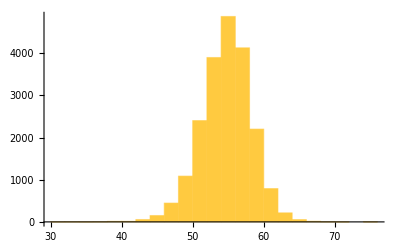

```mathematica
Histogram[Normal[tc2[[All, "Cells_Granularity_1_WGA"]]], PlotRange->All]
```

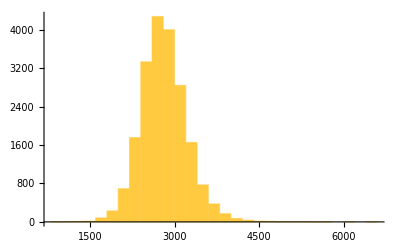

```mathematica
Histogram[Normal[tc2[[All, "Cells_AreaShape_Area"]]], PlotRange->All]
```

```mathematica
Module[{ru={299459058088077823758143088095350287424,4,1},init={{1},0},txspec={200,{-10,30}}},SeedRandom[6353];
polys = ({{"[◼]", "CAPolygon"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[ru,init,txspec,#,"ReturnPerturbations"->False]]&/@#&)@{{"[◼]", "allperts"}}[ru,init,txspec]];
```

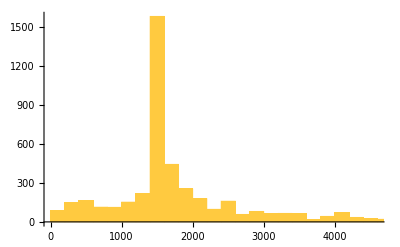

```mathematica
Histogram[Area/@ polys]
```

```mathematica
Histogram[Normal[tc2[[All, "Cells_Granularity_1_WGA"]]], PlotRange->All]
```

#### Looking at granularity

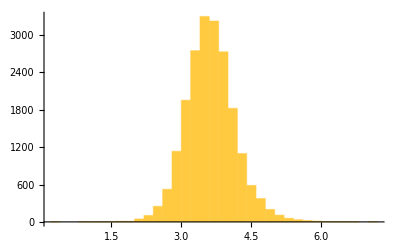
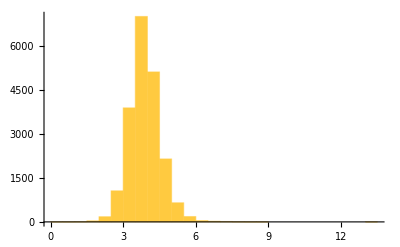
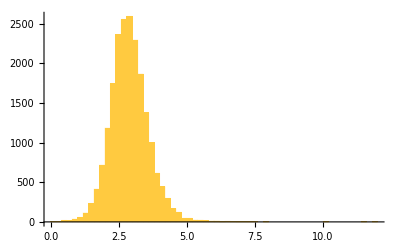
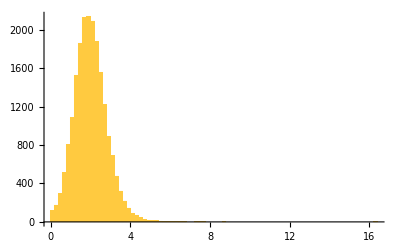
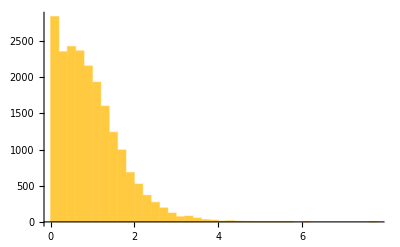
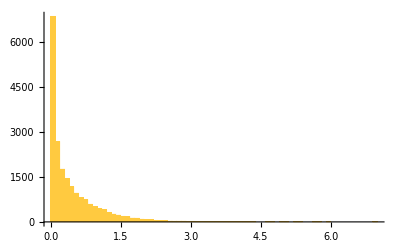
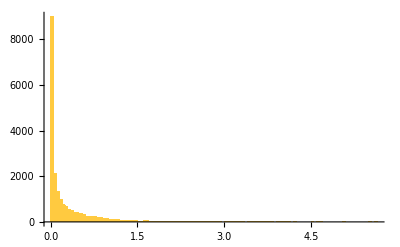
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Histogram[Normal[tc2[[All, "Cells_Granularity_"<>ToString[i]<>"_WGA"]]], PlotRange->All], {i, 8}]
```

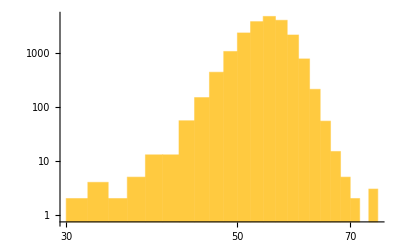
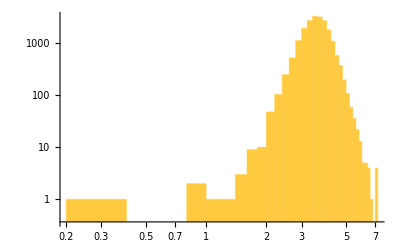
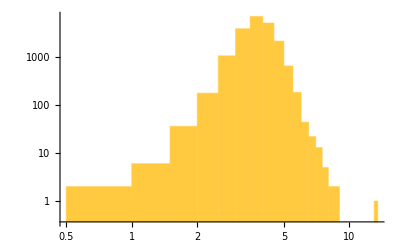
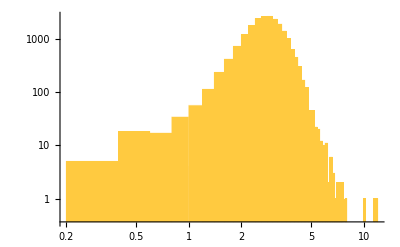
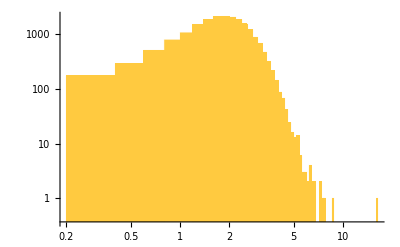
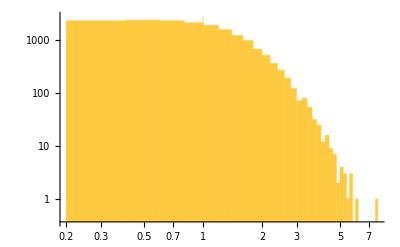
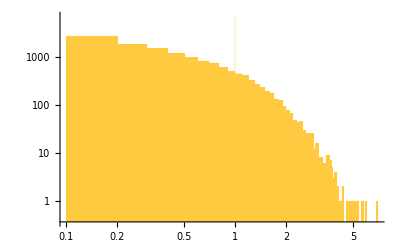
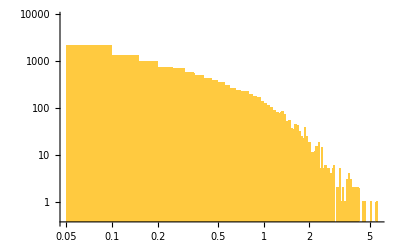

```mathematica
Table[Histogram[Normal[tc2[[All, "Cells_Granularity_"<>ToString[i]<>"_WGA"]]], PlotRange->All, ScalingFunctions->{"Log", "Log"}], {i, 8}]
```

```mathematica
Histogram[Normal[tc2[[All, "Cells_Granularity_"<>ToString[8]<>"_WGA"]]], ScalingFunctions->{"Log", "Log"},PlotRange->All]
```

-Graphics-

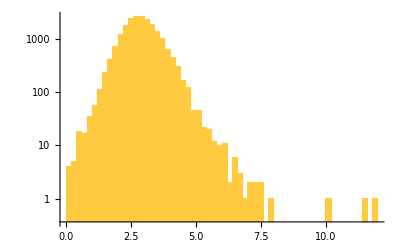

```mathematica
Histogram[Normal[tc2[[All, "Cells_Granularity_"<>ToString[4]<>"_WGA"]]], ScalingFunctions->{Automatic, "Log"},PlotRange->All]
```

Pe